# Results

### Clear Stagnant Parameters

```mathematica
Clear[ele,Vo,uVo,F,R,kB,T,β,e,eo,NA,a,ao ,aoSI,aSI,aCond,l,lcgs,lsi,Lcgs,Lsi,σo,η,ηSI,ϵo,ϵDL,ϵSL]
```

```mathematica
Clear[QpH1,QpH2,QpH3,QpH4,QpH5,QpH6,QpH7,QpH8,QpH9,QpH10,QpH11,QpH12,QpH13,QpHi ]
```

```mathematica
Clear[λpH1 ,λpH2,λpH3,λpH4,λpH5,λpH6,λpH7,λpH8,λpH9,λpH10,λpH11,λpH12,λpH13,λpHi]
```

```mathematica
Clear[σpH1,σpH2,σpH3,σpH4,σpH5,σpH6,σpH7,σpH8,σpH9,σpH10,σpH11,σpH12,σpH13,σpHi,σoSI,σo]
```

## 1. Stagnant parameters

## Input Voltage

```mathematica
Vo=0.15
```

0.15

```mathematica
uVo=Quantity[Vo,"Volts"]
```

0.15 V

## Standard Constants

```mathematica
F=UnitConvert[Quantity["FaradayConstant"],"StatCoulombs"/"Moles"]
```

2.892558×10^14 statC/mol

```mathematica
(*R = = UnitConvert[UnitConvert[Quantity["GasConstant"],""],"Grams"*"Centimeters"^2/("Seconds"^2*"Kelvins"*"Moles")]*)
```

```mathematica
R = UnitConvert[UnitConvert[Quantity["GasConstant"],"SIBase"],"Grams"*"Centimeters"^2/("Seconds"^2*"Kelvins"*"Moles")]
```

8.3145×10^7 g cm^2/(s^2 K mol)

```mathematica
kB =UnitConvert[ Quantity["BoltzmannConstant"],"Ergs"/"Kelvins"]
```

1.3806×10^-16 ergs/K

```mathematica
T=Quantity[298.15,"Kelvins"]
```

298.15 K

```mathematica
β=1/kB/T
```

2.42931×10^13 per erg

```mathematica
e =UnitConvert[Quantity["ElementaryCharge"],"StatCoulombs"]
```

4.803205×10^-10 statC

```mathematica
eo=e
```

4.803205×10^-10 statC

```mathematica
NA =UnitConvert[Quantity["AvogadroConstant"],1/"Moles"]
```

6.022141×10^23 /mol

## Actin3

### radius

```mathematica
ao = UnitConvert[Quantity[(23.83)*10^(-10),"Meters"],"Centimeters"]
```

2.383×10^-7 cm

```mathematica
a = UnitConvert[Quantity[(23.83+0*2.5)*10^(-10),"Meters"],"Centimeters"]
```

2.383×10^-7 cm

```mathematica
aCond= a
```

2.383×10^-7 cm

```mathematica
aoSI = UnitConvert[ao,"SIBase"]
```

2.383×10^-9 m

```mathematica
aSI = UnitConvert[a,"SIBase"]
```

2.383×10^-9 m

### length

```mathematica
l=Quantity[5.4*10^-9,"Meters"]
```

5.4×10^-9 m

```mathematica
lsi=Quantity[5.4*10^-9,"Meters"]
```

5.4×10^-9 m

```mathematica
Lsi=Quantity[422.20*10^(-10),"Meters"]
```

4.222×10^-8 m

### Charge Q

```mathematica
(*Charge coming from tabulated values for Cong Model*)
QpH1 = 657*e;
QpH2=617*e;
QpH3=561*e;
QpH4=296*e;
QpH5=23*e;
QpH6=-82*e;
QpH7=-154*e;
QpH8=-184*e;
QpH9=-222*e;
QpH10=-269*e;
QpH11=-432*e;
QpH12=-476*e;
QpH13=-502*e;
```

```mathematica
QpHi = {QpH1,QpH2,QpH3,QpH4,QpH5,QpH6,QpH7,QpH8,QpH9,QpH10,QpH11,QpH12,QpH13}
```

{3.155705×10^-7 statC,2.963577×10^-7 statC,2.694598×10^-7 statC,1.421749×10^-7 statC,1.104737×10^-8 statC,-3.938628×10^-8 statC,-7.396935×10^-8 statC,-8.837897×10^-8 statC,-1.066311×10^-7 statC,-1.292062×10^-7 statC,-2.074984×10^-7 statC,-2.286325×10^-7 statC,-2.411209×10^-7 statC}

### Linear Charge Density

```mathematica
λpH1 = QpH1/Lsi;
λpH2 = QpH2/Lsi;
λpH3 = QpH3/Lsi;
λpH4 = QpH4/Lsi;
λpH5 = QpH5/Lsi;
λpH6 = QpH6/Lsi;
λpH7 = QpH7/Lsi;
λpH8 = QpH8/Lsi;
λpH9 = QpH9/Lsi;
λpH10 = QpH10/Lsi;
λpH11 = QpH11/Lsi;
λpH12 = QpH12/Lsi;
λpH13 = QpH13/Lsi;
```

```mathematica
λpHi = {λpH1,λpH2,λpH3,λpH4,λpH5,λpH6,λpH7,λpH8,λpH9,λpH10,λpH11,λpH12,λpH13}
```

{7.47443 statC/m,7.01937 statC/m,6.38228 statC/m,3.36748 statC/m,0.261662 statC/m,-0.932882 statC/m,-1.752 statC/m,-2.0933 statC/m,-2.52561 statC/m,-3.06031 statC/m,-4.9147 statC/m,-5.41527 statC/m,-5.71106 statC/m}

### Surface Charge Density

```mathematica
σpH1 = λpHi[[1]]/(2*Pi*aoSI);
σpH2 = λpHi[[2]]/(2*Pi*aoSI);
σpH3 = λpHi[[3]]/(2*Pi*aoSI);
σpH4 = λpHi[[4]]/(2*Pi*aoSI);
σpH5 = λpHi[[5]]/(2*Pi*aoSI);
σpH6 = λpHi[[6]]/(2*Pi*aoSI);
σpH7 = λpHi[[7]]/(2*Pi*aoSI);
σpH8 = λpHi[[8]]/(2*Pi*aoSI);
σpH9 = λpHi[[9]]/(2*Pi*aoSI);
σpH10 = λpHi[[10]]/(2*Pi*aoSI);
σpH11 = λpHi[[11]]/(2*Pi*aoSI);
σpH12 = λpHi[[12]]/(2*Pi*aoSI);
σpH13 = λpHi[[13]]/(2*Pi*aoSI);
```

```mathematica
σpHi = UnitConvert[{σpH1,σpH2,σpH3,σpH4,σpH5,σpH6,σpH7,σpH8,σpH9,σpH10,σpH11,σpH12,σpH13},"Coulombs"/"Meters"^2]
```

{0.166515 C/m^2,0.156377 C/m^2,0.142184 C/m^2,0.0750205 C/m^2,0.0058293 C/m^2,-0.0207827 C/m^2,-0.0390309 C/m^2,-0.0466344 C/m^2,-0.0562654 C/m^2,-0.0681774 C/m^2,-0.109489 C/m^2,-0.120641 C/m^2,-0.127231 C/m^2}

```mathematica
σoSI=σpHi[[7]]
```

-0.0390309 C/m^2

```mathematica
(*σo=UnitConvert[σpHi[[7]],"Coulombs"/"Centimeters"^2]/e*)
```

### viscosity

```mathematica
(*actin viscosity*)
η=UnitConvert[Quantity[8.90×10^(-4),"Pascals"*"Seconds"],"Dynes"*"Seconds"/"Centimeters"^2]
```

0.0089 s dynes/cm^2

```mathematica
ηSI=Quantity[8.90×10^(-4),"Pascals"*"Seconds"]
```

0.00089 s Pa

## Permittivity

#### air

```mathematica
ϵo =  N[UnitConvert[ Quantity["ElectricConstant"],"SIBase"]]
```

8.85419×10^-12 s^4 A^2/(kg m^3)

#### Diffuse Layer

```mathematica
ϵDL =78.358
```

78.358

#### stern layer

```mathematica
ϵSL =5
```

5

```mathematica
(*ϵSL =78.358*)
```

## - pH7 σo = σ[7]/e= -2.43612×10^13 "/"("cm")^2 n6 ⇒ [Ca2+] ~ 10^(-6)

#### Clear Parameters of this notebook

```mathematica
Clear[zCa,zCl,zK,zp,zp,cCaSL,cCa,cCl,cK,cCaMolar,cClMolar,cKMolar,uCa,uCl,uK,lBDL,lBDLSI,lBSL,lBSLSI,κDL,κDLSI,κSL,κSLSI,λDL ,λDLSI,λSL,λSLSI,εDL,εSL,λεDL,λεSL,BDL,BSL,xcSLsig ,xcSLsig,δ,p,psiq,ζ ,q,ζo ,y1,βe,xcDLsig,xcεDL,xcDL,xc,xcSLsig,xcεSL,xcCondsPercnt]
```

```mathematica
Clear[κDLn6pH7,εDLxan6pH7,δn6pH7,pn6pH7,ζn6pH7,xcn6pH7,xcCondsPercntn6pH7,xcNonCondsPercntn6pH7]
```

```mathematica
Clear[σo,fpH7,fc1pH7 ,fc2pH7 ,fMpH7 ]
```

```mathematica
σo=UnitConvert[σpHi[[7]],"Coulombs"/"Centimeters"^2]/e
```

-2.43612×10^13 /cm^2

## 2. Parameters

Diffuse Layer

## Ions

### valence

```mathematica
zCa = 2;
```

```mathematica
zHPO42m = -2;
```

```mathematica
zCl = -1;
```

```mathematica
zK = 1;
```

```mathematica
zNa = 1;
```

### concentration

```mathematica
cCa = Quantity[((0.00005)),"Moles"/"Meters"^3]
```

0.00005 mol/m^3

```mathematica
cCl = Quantity[100+(2*QuantityMagnitude[cCa]),"Moles"/"Meters"^3]
```

100. mol/m^3

#### MM correction

```mathematica
(*cHPO42m = N[UnitConvert[Quantity[((77.50005)),"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*)
```

```mathematica
cK =Quantity[100,"Moles"/"Meters"^3]
```

100 mol/m^3

```mathematica
(*cNa =N[UnitConvert[Quantity[15,"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*)
```

#### Molar concentration value

```mathematica
cCaMolar=N[UnitConvert[cCa ,"Molar"]]
cCaMilliMolar=N[UnitConvert[cCa ,"MilliMolar"]]
cCaMicroMolar=N[UnitConvert[cCa ,"MicroMolar"]]
cCaNanoMolar=N[UnitConvert[cCa ,"NanoMolar"]]
```

5.×10^-8 M

0.00005 mM

0.05 μM

50. nM

```mathematica
cClMolar=N[UnitConvert[cCl ,"Molar"]]
```

0.1 M

```mathematica
cKMolar=N[UnitConvert[cK ,"Molar"]]
```

0.1 M

```mathematica
(*cNaMolar=UnitConvert[UnitConvert[cNa ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
(*cHPO42mMolar=UnitConvert[UnitConvert[cHPO42m ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
(*cHPO42mMolar2=UnitConvert[UnitConvert[cHPO42m2 ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
ElectroNeutrality=zCa cCa+zK cK+zCl cCl
```

-3.31965×10^-15 mol/m^3

#### MM correction

```mathematica
(*Solve[zCa cCaMolar+zK cKMolar(*+zNa cNaMolar+zHPO42m (cHPO42mMolar)*)+zCl ccClMolar==0,ccClMolar]*)
```

### concentration of divalent-monovalent mixture

```mathematica
zp=1+√(4 cCa/cK)
```

1.00141

```mathematica
1+√(4 cCa/cK)
```

1.00141

### ion size

```mathematica
(*size of ion radius; used for the self inductance calculations*)
```

#### monovalent

```mathematica
(*radius*)
```

```mathematica
srK = Quantity[1.52*10^(-10),"Meters"];
```

```mathematica
srNa = Quantity[1.16*10^(-10),"Meters"];
```

```mathematica
srCl = Quantity[1.67*10^(-10),"Meters"];
```

```mathematica
(*diameter*)
```

```mathematica
sCa = N[194*10^-12]
```

1.94×10^-10

```mathematica
sK = QuantityMagnitude[Quantity[3.04*10^(-10),"Meters"]];
```

```mathematica
sNa = QuantityMagnitude[Quantity[2.32*10^(-10),"Meters"]];
```

#### Divalent

```mathematica
(*radius*)
```

```mathematica
(*srCa =  Quantity[1.14*10^(-10),"Meters"];*)
```

```mathematica
sCa = N[Quantity[194*10^-12,"Meters"] ]
```

1.94×10^-10 m

```mathematica
sHPO42m=Quantity[5.5*10^(-10),"Meters"];
```

#### Rion

```mathematica
a
```

2.383×10^-7 cm

```mathematica
Rion=srK/a
```

0.0637851

```mathematica
Rion=0.0
```

0.

### mobility

```mathematica
mobilityPotassium=10.12*10^(-8);
```

```mathematica
uK=UnitConvert[Quantity[10.12*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

1.04886×10^-15 cm^2 mol/(s statC statV)

```mathematica
uCa = UnitConvert[Quantity[2.06*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

2.13504×10^-16 cm^2 mol/(s statC statV)

```mathematica
(*uCl=UnitConvert[Quantity[6.88*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)*)
```

```mathematica
uCl=UnitConvert[Quantity[1.0382*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

1.08893×10^-15 cm^2 mol/(s statC statV)

```mathematica
uNa = UnitConvert[Quantity[0.682*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

7.15325×10^-16 cm^2 mol/(s statC statV)

```mathematica
uHPO42mSIbase=Quantity[0.898*10.12*10^(-8),"Meters"^2/("Volts"*"Seconds")]
```

9.08776×10^-8 m^2/(s V)

```mathematica
uHPO42m=UnitConvert[uHPO42mSIbase,"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

9.4188×10^-16 cm^2 mol/(s statC statV)

```mathematica
Quantity[9.418799447028083*^-16, (("Centimeters")^2 "Moles")/("Seconds" "StatCoulombs" "StatVolts")]
```

(9.4188×10^-16 cm^2 mol/(s statC statV))

#### SI units

```mathematica
uClSIbase=Quantity[1.0382*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")]
```

1.05066×10^-7 m^2/(s V)

```mathematica
uNaSIbase = Quantity[0.682*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")]
```

6.90184×10^-8 m^2/(s V)

## bjerrum lengths

#### diffuse layer

```mathematica
lBDL =(e^2 β)/ϵDL
```

7.15255×10^-8 statC^2/erg

```mathematica
lBDLSI=UnitConvert[lBDL*(1/(4 π ϵo)),"SIBase"]
```

7.15255×10^-10 m

## Inverse Debye Length

#### diffuse layer

#### MM correction

```mathematica
lBDL
```

7.15255×10^-8 statC^2/erg

```mathematica
cK* NA* zK^2
```

6.022141×10^25 per meter^3

```mathematica
cCl*NA*zCl
```

-6.02215×10^25 per meter^3

```mathematica
(*κDL = √(8 π lBDL cK NA zK^2)*)
```

```mathematica
κDL = √(8 *π *lBDL*( cK* NA* zK^2+cCl*NA*zCl^2+cCa*NA*zCa^2))
```

1.47144×10^10 statC/(m^(3/2)√erg)

```mathematica
UnitConvert[κDL *(1/(√(4 π ϵo))),"SIBase"]
```

1.47144×10^9 per meter

## Debye Length

#### diffuse layer

```mathematica
λDL = 1/κDL
```

6.79609×10^-11 m^(3/2)√ergs/statC

```mathematica
λDLSI=UnitConvert[λDL  *(√(4 π ϵo)),"SIBase"]
```

6.79609×10^-10 m

## ε = κ a

#### diffuse layer

```mathematica
εDL =  QuantityMagnitude[κDL* a]
```

3.50643

```mathematica
UnitSimplify[κDLSI* aSI]
```

UnitSimplify[κDLSI (2.383×10^-9 m)]

## Dimensionless Debye Length

#### diffuse layer

```mathematica
λεDL=1/εDL
```

0.28519

```mathematica
(*λεDL=0.49/εDL^0.89*)
```

## B = 4 π lB z a σa

```mathematica
(*statC^2/(cm erg)=statC^2/1 1/cm 1/erg=(cm^2 g)/s^2 1/cm s^2/(g cm^2)=1*)
```

#### diffuse layer

```mathematica
BDL = QuantityMagnitude[ 4 π lBDL a zp σo]
```

-5.22525

## Diffuse Layer Parameters

```mathematica
δ=BesselK[0,εDL]/BesselK[1,εDL]
```

0.881452

```mathematica
p =(BDL*δ)/(2 εDL)
```

-0.656766

```mathematica
FindRoot[Sqrt[(psiq*p)^2+1]-1==δ^2*(1/2/p*Sinh[2/psiq*ArcSinh[psiq*p]]-1),{psiq,0.7}] /.Rule->Set
```

{0.91177}

```mathematica
ζ=psiq
```

0.91177

```mathematica
ζ*p
```

-0.598819

```mathematica
q = √((ζ p)^2+1)
```

1.16558

```mathematica
(* Limits on ζ: ζo < ζ < 1 *)   (*22*)
ζo = √((2*δ)/(3+δ^2))
```

0.683193

```mathematica
(* Surface Potential given by NLDH *)   (*21*)
y1=2/ζ ArcSinh[ζ p]
```

-1.24552

```mathematica
βe=zp*e β (* in 1/V*)
```

11685. statC/erg

## percent condensed

```mathematica
xcCondsPercnt=1-2/(1+q)
```

0.0764613

```mathematica
(-xcCondsPercnt+1)
```

0.923539

Stagnant Layer

#### MM correction

```mathematica
Clear[xxc2]
```

### Option 1

```mathematica
(*FindRoot[(xxc2^2-1)/2*eo*NA*(1*cKMolar+2*cCaMolar)*(Exp[-yDL[xxc2]]+Exp[-yDL[1]])/2-2/(1+q)*xxc2*σoSI/a*BesselK[1,xxc2*εDL]/BesselK[1,εDL]==-σoSI/a,{xxc2,1.3},WorkingPrecision->10,PrecisionGoal->100,MaxIterations->1000]/.Rule->Set*)
```

### Option 2

```mathematica
FindRoot[(xxc2^2-1)/2*eo*NA*(1*cKMolar*Exp[-yDL[xxc2]]+2*cCaMolar*Exp[-yDL[xxc2]])==-(1-2/(1+q))*σoSI/a,{xxc2,1.},WorkingPrecision->10,PrecisionGoal->100,MaxIterations->1000]/.Rule->Set
```

FindRoot::precw: The precision of the argument function ((-1+xxc2^2) (ⅇ^(62.3494 BesselK[0,Times[«1»]]) (1.×10^-7)+ⅇ^(62.3494 «1») (0.1)) (1.446279×10^14)==1.25235) is less than WorkingPrecision (10.).

{1.046213732}

```mathematica
(*xcεDL=xcDLsig*)
```

```mathematica
xcεDL=xxc2
```

1.046213732

```mathematica
(*xcDL=xcDLsig*)
```

```mathematica
xcDL=xxc2
```

1.046213732

```mathematica
xc=xcDL
```

1.046213732

## Ions SL

#### MM correction

```mathematica
xcCondsPercnt=(xc^2-1)/2*(Exp[-yDL[xc]]+Exp[-yDL[1]])/2
```

0.144424

```mathematica
cCaSL =cCa*xcCondsPercnt
```

7.22118×10^-6 mol/m^3

```mathematica
cKSL = cK*xcCondsPercnt
```

14.4424 mol/m^3

```mathematica
cNaSL = cNa*xcCondsPercnt
```

0.144424 cNa

#### Molar concentration value

```mathematica
cCaSLMolar=UnitConvert[UnitConvert[cCaSL ,"Moles"/"Meters"^3],"Molar"]
```

7.22118×10^-9 M

```mathematica
cKSLMolar=UnitConvert[UnitConvert[cKSL ,"Moles"/"Meters"^3],"Molar"]
```

0.0144424 M

```mathematica
cNaSLMolar=UnitConvert[UnitConvert[cNaSL ,"Moles"/"Meters"^3],"Molar"]
```

UnitConvert[UnitConvert[0.144424 cNa,Moles/Meters^3],Molar]

#### ...

```mathematica
(*cCa = N[UnitConvert[Quantity[((10*0.5)),"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*(-xcCondsPercnt+1)*)
```

## bjerrum lengths SL

#### stagnant layer

```mathematica
lBSL =(e^2 β)/ϵSL
```

1.12092×10^-6 statC^2/erg

```mathematica
lBSLSI=UnitConvert[lBSL *(1/(4 π ϵo)),"SIBase"]
```

1.12092×10^-8 m

## Inverse Debye Length SL

#### stagnant

```mathematica
(*κSL = √(8 π lBSL (cCaSL *zCa^2+cKSL *zK^2) NA zp )*)
```

```mathematica
κSL = √(8 π lBSL (cCaSL *zCa^2+cKSL *zK^2) NA(**xcCondsPercnt*))
```

1.56532×10^10 statC/(m^(3/2)√erg)

```mathematica
UnitConvert[κSL *(1/(√(4 π ϵo))),"SIBase"]
```

1.56532×10^9 per meter

## Debye Length SL

#### stagnant

```mathematica
λSL=1/κSL
```

6.38849×10^-11 m^(3/2)√ergs/statC

```mathematica
λSLSI=UnitConvert[λSL  *(√(4 π ϵo)),"SIBase"]
```

6.38849×10^-10 m

## ε = κ a -SL-

#### stern

```mathematica
εSL =   QuantityMagnitude[κSL* a]
```

3.73015

```mathematica
(*ϵMix = QuantityMagnitude[κMix*a]*)
```

### Dimensionless Debye Length SL

#### stern

```mathematica
λεSL= 1/εSL
```

0.268086

## B = 4 π lB z a σa -SL-

#### stern

```mathematica
BSL = QuantityMagnitude[4 π lBSL zp a σo]
```

-81.888

## 2a. Condensation Distance

### Condensation Distance

### Analysis on SL

#### MM correction

#### If we use HD solution, the (dimensionless) total charge accumulated in the Dl cancel out the (dimensionless) total charge of the cylinder providing electroneutrality. Thus, it does not allow for condensation in the SL.

```mathematica
NIntegrate[BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

1.

#### If we use NLHD solution, the (dimensionless) total charge accumulated in the DL partially cancel out the (dimensionless) total charge of the cylinder. Thus, some (dimensionless) charge should be condensation in the SL.

```mathematica
NIntegrate[2/(1+q)*BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

0.923539

#### the (dimensionless) charge accumulated in the SL that provide electroneutrality is given by

```mathematica
1.0-NIntegrate[2/(1+q)*BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

0.0764613

#### Cylinder charge per radius

```mathematica
totalcharge=-σoSI/a
```

16.3789 C/cm^3

#### contribution from SL

```mathematica
contsl=UnitConvert[(xc^2-1)/2*eo*NA*(1*cKMolar+2*cCaMolar)(Exp[-yDL[xc]]+Exp[-yDL[1]])/2,"Coulombs"/"Centimeters"^3]
```

1.39348 C/cm^3

#### contribution from DL

#### option 1

```mathematica
(*contdl=UnitConvert[-2/(1+q)*ϵo*ϵDL *BDL/β/eo/a^2/BesselK[1,εDL]/zp*1*BesselK[1,xc*εDL]*xc,"Coulombs"/"Centimeters"^3]*)
```

```mathematica
-2/(1+q)*xc*σoSI/a*BesselK[1,xc*εDL]/BesselK[1,εDL]
```

13.1084 C/cm^3

#### option 2

```mathematica
contdl=UnitConvert[-2/(1+q)*ϵo*ϵDL *BDL/β/eo/a^2/BesselK[1,εDL]/zp*1*BesselK[1,1*εDL],"Coulombs"/"Centimeters"^3]
```

15.1266 C/cm^3

#### electroneutrality validation

```mathematica
totalcharge-contdl-contsl
```

-0.141124 C/cm^3

#### fraction of condensed ions (Manning theory)

```mathematica
(*1-2/Abs[BDL]*)
```

```mathematica
manningTheoryVoEQ0p15VepsiEQ5cCa50nM=1-2/(Abs[BDL] zCa/zp)
```

0.808351

#### Our approach: fraction of total charge condensed in SL (same as 1-2/(1+q) )

```mathematica
contsl/totalcharge
```

0.0850775

```mathematica
prcntCondSLVoEQ0p15VepsiEQ5cCaEQ50nM=contsl/totalcharge
```

0.0850775

#### Our approach: fraction of total charge condensed in DL (same as 2/(1+q) )

```mathematica
contdl/totalcharge
```

0.923539

```mathematica
prcntCondDLVoEQ0p15VepsiEQ5cCaEQ50nM=contdl/totalcharge
```

0.923539

#### SL thickness

```mathematica
UnitConvert[(xc-1)*a,"Angstroms"]
```

1.10127 Å

```mathematica
δCL=UnitConvert[(xc-1)*a,"Angstroms"]
```

1.10127 Å

```mathematica
SLthickVoEQ0p15VepsiEQ5cCaEQ50nM=δCL
```

1.10127 Å

#### SL

```mathematica
FindRoot[xcSLsig ySL'[xcSLsig]/ySL'[1]+((ζ p)/(1+q)*ySL[xcSLsig]/ySL[1])^2==1,{xcSLsig,1.0}]/.Rule->Set
```

{1.04533}

```mathematica
xcεSL=xcSLsig
```

1.04533

```mathematica
xcSL=xcεSL
```

1.04533

```mathematica
(*xcDL=xcSLsig*)
```

```mathematica
(*xc=xcDL*)
```

## 2b. Electric Potential

## SL

#### dimensionless

```mathematica
ySL[x]
```

-1.00985+1.73925 (1.09456317-x^2)-85.6724 (0.045177677-Log[x])+3.80744 (-0.045177677+Log[x])

#### plots with dimensions

```mathematica
(*unitless CL thickness*)
nuδCL=QuantityMagnitude[δCL]
```

1.10127

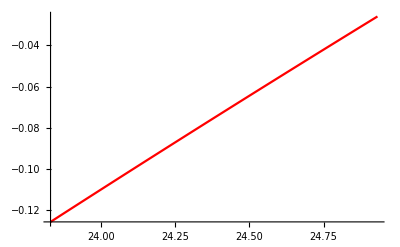

```mathematica
uSLplot=Plot[ UnitConvert[1/(β e)ySL[x*Quantity[10^(-10),"Meters"]/a],"SIBase"],{x,23.83,23.83+nuδCL},PlotStyle->Red]
```

## DL

#### dimensionless

```mathematica
yDL[x]
```

-62.3494 BesselK[0,3.50643 x]

#### plots with dimensions

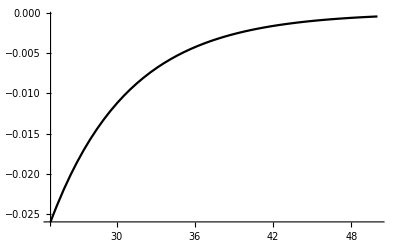

```mathematica
uDLplot=Plot[{UnitConvert[1/(β e)yDL[x*Quantity[10^(-10),"Meters"]/a],"SIBase"]},{x,23.83+nuδCL,50},PlotRange->Full,PlotStyle->Black,PlotLegends->"Expressions"]
```

```mathematica
UnitConvert[UnitConvert[1/(β e)yDL[(23.83+1.1012732237538216)*Quantity[10^(-10),"Meters"]/a],"SIBase"],"Volts"]
```

-0.0259457 V

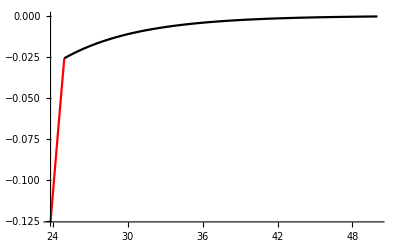

```mathematica
Show[uSLplot,uDLplot,PlotRange->All]
```

## 3. BDL vs “f”

eqn 44

```mathematica
fpH7 = 1-2/(1+√(1+√((-p/Log[δ])^2+1)))
```

0.430196

eqn 45 - NLDH

```mathematica
fc1pH7 = 1-4/(2+√(Abs[BDL]^2+4))
```

0.473333

eqn 46 - NLDH

```mathematica
fc2pH7 = 1-4/(2+√((Abs[BDL]*ArcSinh[BDL/2])^2+4))
```

0.637861

eqn 47 - Manning

```mathematica
fMpH7 = 1-2/Abs[BDL]
```

0.617243

## 4. Current

Transversal (Axial) Current

## SL

```mathematica
ΔVSLt=Vo
currRadial=CurrentTransSL
```

0.15

-14277.8 statC/(s statV)

```mathematica
(*currRadial=CurrentTransSL/.ΔVSLt->Vo*)
```

#### CGS

```mathematica
currRadial*UnitConvert[uVo,"StatVolts"]
```

-7.14386 statC/s

```mathematica
ItSLcgs =UnitConvert[currRadial*UnitConvert[uVo,"StatVolts"],"StatAmperes"]
```

-7.14386 statA

#### SI

```mathematica
ItSLsi =UnitConvert[ UnitSimplify[currRadial]*uVo,"Amperes"]
```

-2.38293×10^-9 A

## DL

```mathematica
ΔVDLt=Vo
```

0.15

```mathematica
CurrentTransDL
```

85457.3 statC/(s statV)

#### CGS

```mathematica
UnitConvert[CurrentTransDL,"Seconds"*"StatCoulombs"^2/("Grams"*"Centimeters"^2)]*UnitConvert[uVo,"StatVolts"]
```

42.7582 s statC^2 statV/(g cm^2)

```mathematica
ItDLcgs =UnitConvert[ UnitSimplify[CurrentTransDL]*uVo,"StatAmperes"]
```

42.7582 statA

#### SI

```mathematica
ItDLsi =UnitConvert[ UnitSimplify[CurrentTransDL]*uVo,"Amperes"]
```

1.42626×10^-8 A

Longitudinal (Axial) Current

## SL

```mathematica
ΔVSLl=Vo
ilSL=IlSL
```

0.15

5.93935 statC/(s statV)

```mathematica
(*ilSL=IlSL/.ΔVSLl->Vo*)
```

```mathematica
(*IlSL=ilSL/.ΔV->Vo*)
```

```mathematica
ilSL*uVo
```

0.00297173 statC/s

#### CGS

```mathematica
UnitConvert[ilSL,"Seconds"*"StatCoulombs"^2/("Grams"*"Centimeters"^2)]*UnitConvert[uVo,"StatVolts"]
```

0.00297173 s statC^2 statV/(g cm^2)

```mathematica
Ilslcgs=UnitConvert[ilSL*uVo,"StatAmperes"]
```

0.00297173 statA

```mathematica
UnitConvert[IlcSL (Quantity[0.05, "Volts"]),"StatAmperes"]
```

UnitConvert[IlcSL (0.05 V),StatAmperes]

#### SI

```mathematica
Ilslsi=UnitConvert[ilSL*uVo,"Amperes"]
```

9.91262×10^-13 A

## DL

```mathematica
ΔVDLl=Vo
ilDL=IlDL*uVo
```

0.15

0.364505 statC/s

```mathematica
(*ilDL=IlDL*uVo/.ΔVDLl->Vo*)
```

#### CGS

```mathematica
IlDLcgs=UnitConvert[ilDL,"StatAmperes"]
```

0.364505 statA

#### SI

```mathematica
IlDLsi=UnitConvert[ilDL,"Amperes"]
```

1.21586×10^-10 A

## 5. Resistance

Transversal (Axial) Resistance

## SL

```mathematica
RtSL
```

-0.0000105058 s statV/statC

```mathematica
RtSLsi=UnitConvert[RtSL,"Ohms"]
```

-9.44214×10^6 Ω

```mathematica
uRtSLsi=Abs[RtSLsi]
```

9.44214×10^6 Ω

## DL

```mathematica
RtDL
```

4.20823×10^-6 s statV/statC

```mathematica
RtDLsi=UnitConvert[RtDL,"Ohms"]
```

3.78217×10^6 Ω

```mathematica
uRtDLsi=RtDLsi
```

3.78217×10^6 Ω

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
(*uRtDLsi=Quantity[0.524*10^7,"Ohms"]*)
```

```mathematica
1.0868426051953934*^7/(4.74*10^6)
```

2.29292

## Equivalent Resistance

```mathematica
uRtEqsi =uRtDLsi +uRtSLsi
```

1.32243×10^7 Ω

Longitudinal (Axial) Resistance

## SL

```mathematica
RlSL
```

0.0252553 s statV/statC

```mathematica
RlSLsi=UnitConvert[RlSL,"Ohms"]
```

2.26983×10^10 Ω

```mathematica
uRlSLsi=RlSLsi
```

2.26983×10^10 Ω

## DL

```mathematica
RlDL
```

0.000205901 s statV/statC

```mathematica
RlDLsi=UnitConvert[RlDL,"Ohms"]
```

1.85054×10^8 Ω

```mathematica
uRlDLsi=RlDLsi
```

1.85054×10^8 Ω

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
(*uRlDLsi=Quantity[0.199*10^9,"Ohms"]*)
```

```mathematica
1.7434096079950902*^8/(195*10^6)
```

0.894056

## Equivalent Resistance

```mathematica
uRlEqsi = uRlDLsi*uRlSLsi /(uRlDLsi+uRlSLsi)
```

1.83558×10^8 Ω

## 6. Capacitance

## SL

### q, L, M, NN terms

```mathematica
ζv =2*δ √(1/(3+δ^2))
```

0.907105

#### for q

```mathematica
(*BSL=*)4 π lBSL zp a σo/eo*(1/(4 π ϵo))
```

-1.53225×10^23 kg m^2 statC/(s^4 A^2 erg)

```mathematica
(*p =*) BSL/(2 εSL)δ
```

-9.67527

```mathematica
(*ζζ =√(ζ^2+(9 (1-δ^2)δ^2 p^2)/(5(3+δ^2)^3))*)
```

```mathematica
(*q =*)√(Expand[ζζ^2 p^2]+1)
```

√(1+0.431341 ζζ^2)

#### check q

```mathematica
(*α=(9 δ^2 (1-δ^2))/(5 (3+δ^2)^3)*)
```

```mathematica
γSL=UnitConvert[(2 a lBSL π zp δ)/(eo εSL)*(1/(4 π ϵo)),"Meters"^2/"Coulombs"]
```

247.887 m^2/C

```mathematica
(*p=γ σo*)
```

```mathematica
(*q=√(Expand[(γ^2 ζ^2 +α γ^4 σo^2)σo^2]+1)*)
```

#### L, M, NN in SI

```mathematica
L=UnitSimplify[1/(8 eo zp β)εSL^2 (-1+xcεDL^2 (1-2 Log[xcεDL]))]
```

-0.000193505 V

```mathematica
M=UnitSimplify[(4 a π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]
```

2.54419 m V^2/N

```mathematica
NN=UnitSimplify[(8 a π BesselK[0,xcεDL εDL])/(ϵDL εDL BesselK[1,εDL])(1/(4 π ϵo))]
```

1.43753 m V^2/N

#### a check with SI units for L, M, NN

```mathematica
(*LSI =UnitSimplify[ (εSLSI^2 (-1+xcεDL^2 (1-2 Log[xcεDL])))/(8 eoSI zp βSI)]*)
```

```mathematica
(*MSI=UnitSimplify[(4 aSI π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]*)
```

```mathematica
(*NNSI=UnitSimplify[(8 aSI π BesselK[0,xcεDL εDL])/(ϵDL εDLSI BesselK[1,εDL])(1/(4 π ϵo))]*)
```

### constants a0, a1, a2, a3

```mathematica
UnitConvert[a0SL,"Coulombs"/"Meters"^2]
```

0.0000593042 C/m^2

```mathematica
UnitConvert[a1SL,"Coulombs"/"Meters"^2/"Volts"]
```

0.30648 C/(m^2 V)

```mathematica
UnitConvert[a2SL,"Coulombs"/"Meters"^2/"Volts"^2]
```

0.0465285 C/(m^2 V^2)

```mathematica
UnitConvert[a3SL,"Coulombs"/"Meters"^2/"Volts"^3]
```

80.1505 C/(m^2 V^3)

### bSL

```mathematica
bSL
```

-0.151816 /V

```mathematica
bSLsi= UnitConvert[bSL,"Volts"]
```

-0.151816 /V

```mathematica
ubSLsi=bSLsi
```

-0.151816 /V

```mathematica
bSLVoEQ0p15VepsiEQ5cCa50nM=ubSLsi
```

-0.151816 /V

### CoSL

```mathematica
Coslsi=UnitConvert[a1SL,"Farads"/"Meters"^2]
```

0.30648 F/m^2

```mathematica
CoSLsi = UnitConvert[2*Pi*l*a*Coslsi,"Farads"]
```

2.47799×10^-17 F

```mathematica
uCoSLsi=CoSLsi
```

2.47799×10^-17 F

```mathematica
CoSLVoEQ0p15VepsiEQ5cCa50nM=uCoSLsi
```

2.47799×10^-17 F

## DL

### q, A, W terms

#### check q

```mathematica
(*ζv =2*δ √(1/(3+δ^2))*)
```

```mathematica
(*(2 a lBDL π zp δ)/(eo εDL)*)
```

```mathematica
(*γDL=UnitConvert[(2 a lBDL π zp δ)/(eo εDL)*(1/(4 π ϵo)),"Meters"^2/"Coulombs"]*)
```

#### A, W

```mathematica
(*A = UnitConvert[(8 a π BesselK[0,xc εDL])/(ϵDL εDL BesselK[1,εDL]),"SIBase"]*)
```

```mathematica
(*W=UnitConvert[A/(4 π ϵo),"Volts"*"Meters"^2/"Coulombs"]*)
```

#### a check with SI units for L, M, NN

```mathematica
(*LSI =UnitSimplify[ (εSLSI^2 (-1+xcεDL^2 (1-2 Log[xcεDL])))/(8 eoSI zp βSI)]*)
```

```mathematica
(*MSI=UnitSimplify[(4 aSI π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]*)
```

```mathematica
(*NNSI=UnitSimplify[(8 aSI π BesselK[0,xcεDL εDL])/(ϵDL εDLSI BesselK[1,εDL])(1/(4 π ϵo))]*)
```

### constants a0, a1, a2, a3

```mathematica
(*a0DL*)
```

```mathematica
(*UnitConvert[a1DL,"Coulombs"/"Meters"^2/"Volts"]*)
```

```mathematica
(*a2DL*)
```

```mathematica
(*a3DL*)
```

```mathematica
(*UnitConvert[a3DL,"Coulombs"/"Meters"^2/"Volts"^3]*)
```

### bDL

```mathematica
(*ubDLsi=bDL*)
```

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
```

```mathematica
ubDLsi=-1/2 Quantity[0.49662052587250521,1/"Volts"]
```

-0.24831 /V

```mathematica
bDL= ubDLsi
```

-0.24831 /V

```mathematica
bDLVoEQ0p15VepsiEQ5cCa50nM=ubDLsi
```

-0.24831 /V

### CoDL

```mathematica
(*Codlsi = UnitConvert[a1DL,"Farads"/"Meters"^2]*)
```

```mathematica
(*CoDLsi=UnitConvert[2*Pi*l*a*Codlsi,"Farads"]*)
```

```mathematica
(*uCoDLsi=CoDLsi*)
```

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/preInflux/NaKCa_ClHPO4m2/07-30-2020__04-53-52_simulationresults*)
```

```mathematica
CoDLsi=Quantity[0.81534214273944006*2*π*(23.83*10^(-10))*(5.4*10^(-9)),"Farads"]
```

6.59231×10^-17 F

```mathematica
uCoDLsi=CoDLsi
```

6.59231×10^-17 F

```mathematica
CoDLVoEQ0p15VepsiEQ5cCa50nM=uCoDLsi
```

6.59231×10^-17 F

## Equivalent Capacitance and b parameter

### b parameter

```mathematica
btsi=(bSL  CoDLsi+bDL  CoSLsi)/(CoSLsi+CoDLsi)
```

-0.178178 /V

```mathematica
btsi
```

-0.178178 /V

```mathematica
ubtsi=btsi
```

-0.178178 /V

```mathematica
(*ubtsi=0.4489584775618532(*b parameter from SP1*)*)
```

```mathematica
0.4489584775618532
```

0.448958

```mathematica
(*PathforMacPro - /Users/chris/Desktop/Research/Research/00_OtherFolders/00_JACFC_Results/Divalent_Results/CaCl_KCl/pH7/cCaEQ0p005M/07-08-2020__18-03-51_simulationresults*)
(*ubtsi=Quantity[3.2381738940483373,1/"Volts"]*)
```

### Capacitance

```mathematica
uCoEqsi = (uCoSLsi*uCoDLsi)/(uCoSLsi+uCoDLsi)
```

1.80101×10^-17 F

```mathematica
(*PathforMacPro - /Users/chris/Desktop/Research/Research/00_OtherFolders/00_JACFC_Results/Divalent_Results/CaCl_KCl/pH7/cCaEQ0p005M/07-08-2020__18-03-51_simulationresults*)
(*uCoEqsi =Quantity[0.85545751961533945*2*π*(23.83*10^(-10))*(5.4*10^(-9)),"Farads"]*)
```

## 8. Self Inductance

## SL:

```mathematica
LSL
```

0

```mathematica
LSLsi=LSL
```

0

## DL:

```mathematica
LDL
```

0

```mathematica
LDLsi=LDL
```

0

## Equivalent:

```mathematica
LEq
```

0

#### CGS

```mathematica
LEqcgs=LEq
```

0

#### SI

```mathematica
LEqsi=LEq
```

0

## 8. Clear Parameters

### Clear Units

```mathematica
nuVo=QuantityMagnitude[uVo]
```

0.15

```mathematica
nul =QuantityMagnitude[l]
```

5.4×10^-9

#### Total

```mathematica
nuRtEq =QuantityMagnitude[uRtEqsi ]
```

1.32243×10^7

```mathematica
(*nuRtEq=4.748252092201714*^6*)
```

```mathematica
nuRlEq =QuantityMagnitude[uRlEqsi ]
```

1.83558×10^8

```mathematica
nuRtEq/nuRlEq
```

0.0720444

```mathematica
(*nuRlEq=195.0272920991057128*^6*)
```

```mathematica
(*MM: added this*)
```

```mathematica
(*nuZe=QuantityMagnitude[uZesi ]*)
```

```mathematica
(*nuZe=4.8972506598688365*^9*)
```

```mathematica
(*MM: added this*)
```

```mathematica
(*Vo=QuantityMagnitude[uVo]*)
```

```mathematica
(*MM: this parameter is negative*)
```

```mathematica
nubt=QuantityMagnitude[ubtsi]
```

-0.178178

```mathematica
(*nubt=0.47*)
```

```mathematica
nuCoEq=QuantityMagnitude[uCoEqsi]
```

1.80101×10^-17

```mathematica
(*l =5.4*10^(-10)*)
```

```mathematica
(*μ3 =(24 RlEq)/Ze*)
```

```mathematica
(*μ2 =(6 RtEq)/Ze*)
```

## 9. Impedance

### NEW IMPEDANCE ( newImpead )

```mathematica
Impedance=Sqrt[32/225 (25 π^4 nuRlEq^2+80 nubt π^4 nuRlEq nuRtEq nuVo+64 nubt^2 π^4 nuRtEq^2 nuVo^2)+8/225 √(-5625 π^4 nuRlEq^4+10000 π^8 nuRlEq^4-11250 π^4 nuRlEq^3 nuRtEq-5625 π^4 nuRlEq^2 nuRtEq^2-18000 nubt π^4 nuRlEq^3 nuRtEq nuVo+64000 nubt π^8 nuRlEq^3 nuRtEq nuVo-36000 nubt π^4 nuRlEq^2 nuRtEq^2 nuVo-18000 nubt π^4 nuRlEq nuRtEq^3 nuVo-14400 nubt^2 π^4 nuRlEq^2 nuRtEq^2 nuVo^2+153600 nubt^2 π^8 nuRlEq^2 nuRtEq^2 nuVo^2-28800 nubt^2 π^4 nuRlEq nuRtEq^3 nuVo^2-14400 nubt^2 π^4 nuRtEq^4 nuVo^2+163840 nubt^3 π^8 nuRlEq nuRtEq^3 nuVo^3+65536 nubt^4 π^8 nuRtEq^4 nuVo^4)];
```

```mathematica
nuZe= Impedance
```

4.81213×10^9

## Soliton

### KdV equation and more parameters Here we . . - solve for soliton

#### gamma

```mathematica
(*propagation of electrical impulse along actin filaments*)
(*alfa=(L/Ze+Co*Ze)*)

gamma=3*(LEq/nuZe+nuCoEq*nuZe)/(nubt*nuZe^(3/2)*nuCoEq);
```

#### μ2

```mathematica
μ2=nuRtEq*6/nuZe
```

0.0164887

#### μ3

```mathematica
μ3=nuRlEq*24/nuZe
```

0.915474

#### wo

```mathematica
(*      (*max possible value is 4.8*) (*Subscript[Ω, o] in equation 12 from Cameroon Paper*)*)
(* MM: I used the expression from our paper*)
```

```mathematica
wo=(nuVo*12/(Abs[gamma]*nuZe^(1/2)))^(1/2)
```

0.326966

#### alfa

```mathematica
alfa=(LEq/nuZe+nuCoEq*nuZe)
```

8.66669×10^-8

#### beta

```mathematica
beta=2*nul;
```

#### Ω

```mathematica
(*cwq=1/Sqrt[LEq*CEq];*)
```

```mathematica
Ω[τ1_]:=√((wo^2 ⅇ^(-(4 τ1 μ3)/3))/(1+((4 μ2  wo^2)/(5μ3))(1-ⅇ^(-(4 τ1 μ3)/3))));
```

#### ηe

```mathematica
(*MM: I changed from eta to etae. from some reason eta is protected....*)
```

```mathematica
ηe[τ1_] := -((5 (4 μ3 τ1+3 Log[5 μ3]-3 Log[-4 wo^2 μ2+ⅇ^((4 μ3 τ1)/3) (4 wo^2 μ2+5 μ3)]))/(4 μ2));
```

#### cW

```mathematica
cW[psi_,taoprima_]:=-2*(Ω[taoprima])^2*(Sech[Ω[taoprima]*(psi-ηe[taoprima])])^2;
```

#### velocityprop

```mathematica
(*MM: from our paper*)
```

```mathematica
(*velocityprop2[t_]:=4*wo^2* ⅇ^((-4 t μ3)/3)/(1+((4 μ2  wo^2)/(5μ3))(1-ⅇ^(-(4 t μ3)/3)));*)
```

```mathematica
velocityprop[t_]:=-1/(4 μ2)5 (4 μ3-(4 ⅇ^((4 t μ3)/3) μ3 (4 wo^2 μ2+5 μ3))/(-4 wo^2 μ2+ⅇ^((4 t μ3)/3) (4 wo^2 μ2+5 μ3)));
```

#### decaytime

```mathematica
decaytime=w/. Solve[Ω[w]==0.1*Ω[0],w][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

3.77152

```mathematica
(velocityprop[0]/24+1)/alfa*beta
```

0.126835

#### vavg

```mathematica
vavg = Integrate[(velocityprop[t/alfa/24]/24+1)/alfa*beta,{t,0,24*decaytime*alfa}]/(24*decaytime*alfa)
```

0.125092

```mathematica
avgVelocityVoEQ0p15VepsiEQ5cCaEQ50nM=vavg
```

0.125092

#### tmax

```mathematica
te=24*decaytime*alfa
tmax=te;
```

7.84479×10^-6

```mathematica
tmaxVoEQ0p15VϵSLEQ05cCaEQ50nM=7.844789434105876*^-6
```

7.84479×10^-6

#### xmax

```mathematica
xe=Abs[(1-te/alfa)*beta]*(1*10^6)
xmax=xe;
```

0.966779

```mathematica
xmaxVoEQ0p15VϵSLEQ05cCaEQ50nM=xmax
```

0.966779

#### velo

```mathematica
velo=xe/te*(1*10^-6)
```

0.123238

```mathematica
velocityVoEQ0p15VepsiEQ5cCaEQ50nM=velo
```

0.123238

#### Wx

```mathematica
(* with Dimensions *)
```

```mathematica
Wx[x_,t_]:=-2*(Ω[t/alfa/24])^2*(Sech[Ω[t/alfa/24]*((x/beta-t/alfa)-ηe[t/alfa/24])])^2
```

```mathematica
Wx[x,t]
```

-((0.213814 ⅇ^(-586841. t) Sech[0.326966 √(ⅇ^(-586841. t)/(1+0.00154041 (1-ⅇ^(-586841. t)))) (-1.15384×10^7 t+9.25926×10^7 x+75.8095 (4.56338+1.76052×10^6 t-3 Log[-0.00705102+4.58442 ⅇ^(586841. t)]))]^2)/(1+0.00154041 (1-ⅇ^(-586841. t))))

#### Snapshot times for Soliton Plot

```mathematica
0
24*decaytime*alfa/10
24*decaytime*alfa/5
24*decaytime*alfa/3
24*decaytime*alfa/2
24*decaytime*alfa
```

0

7.84479×10^-7

1.56896×10^-6

2.61493×10^-6

3.92239×10^-6

7.84479×10^-6

Plots

### Velocity plots

#### Total

Intracellular conditions

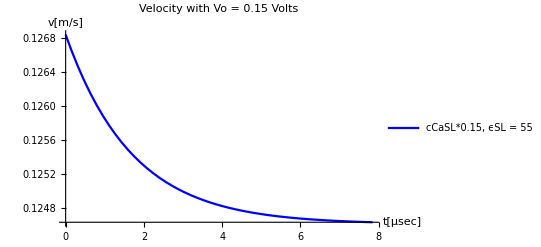

```mathematica
Print["Intracellular conditions"]

veloSP2=Plot[(velocityprop[t/alfa/24*10^-6]/24+1)/alfa*beta,{t,0,24*decaytime*alfa*10^6},PlotLegends->{"cCaSL*0.15, ϵSL = 55"},PlotLabel->"Velocity with Vo = 0.15 Volts",PlotStyle->Blue,PlotRange->Full,Axes->True,AxesLabel->{"t[μsec]","v[m/s]"}]
```

```mathematica
24*0.329*3.6
```

28.4256

```mathematica
veloSP2Data=Cases[veloSP2,Line[{x__}]->x,∞];
```

### Soliton Peak Attenuation plots

```mathematica
(*MM: added ABS[] and divided by 24, not 12*)
```

#### Total

Intracellular conditions

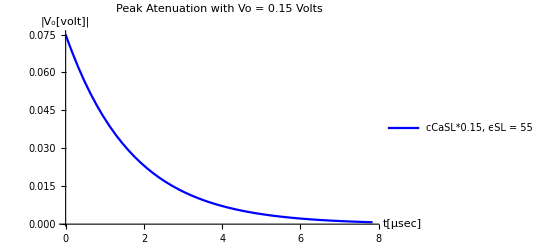

```mathematica
Print["Intracellular conditions"]

peakDecaySP2wSP1Capa=Plot[{Abs[Ω[t/alfa/24*10^-6]^2*gamma*nuZe^(1/2)/24]},{t,0,24*decaytime*alfa*10^6},PlotStyle->Blue,PlotLegends->{"cCaSL*0.15, ϵSL = 55"},PlotLabel->"Peak Atenuation with Vo = 0.15 Volts",Axes->True,AxesLabel->{"t[μsec]","|V_o[volt]|"},PlotRange->All]
```

```mathematica
peakDecaySP2wSP1CapaData=Cases[peakDecaySP2wSP1Capa,Line[{x__}]->x,∞];
```

Soliton Propagation plots

```mathematica
(*Vo=0.15V ϵSL = 78.358 cCa=50nM*)
tmaxVoEQ0p15VϵSLEQ78p358cCaEQ50nM=0.000016722898823157003
```

0.0000167229

```mathematica
(*Vo=0.05V ϵSL = 78.358 cCa=50nM*)
tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM=0.000016787268912085657
```

0.0000167873

```mathematica
tmaxThisFile=24*decaytime*alfa
```

7.84479×10^-6

## Soliton Normalized

#### Normalized - regular

Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot

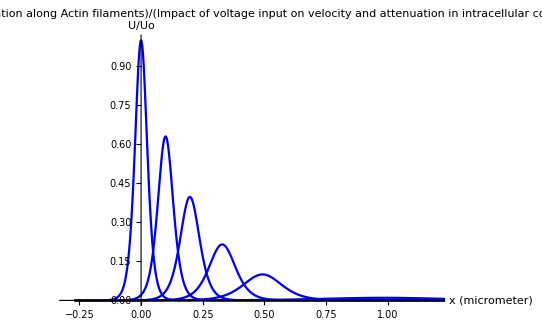

```mathematica
Print["Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot"]

SolNormTot=Plot[ {-Wx[x*10^-6,0]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/10]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/5]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/3]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/2]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile]/wo^2/2},{x,-25*beta*10^6,435*beta*10^6},PlotRange->{{-0.3,1.2},{0,1}},Axes->True,AxesLabel->{"x (micrometer)","U/Uo"},PlotLabel->Style["Soliton propagation along Actin filaments" /" in intracellular conditions" / "Impact of voltage input on velocity and attenuation",Black,FontSize->18,Bold],AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
NormSolSP22Data=Cases[SolNormTot,Line[{x__}]->x,∞];
```

{{-0.27,3.17748×10^-7},{-0.268476,3.48457×10^-7},{-0.266953,3.82135×10^-7},{-0.265429,4.19067×10^-7},{-0.263905,4.59568×10^-7},{-0.262382,5.03984×10^-7},{-0.260858,5.52693×10^-7},{-0.259334,6.06109×10^-7},{-0.257811,6.64687×10^-7},{-0.256287,7.28927×10^-7},{-0.254763,7.99376×10^-7},{-0.253239,8.76633×10^-7},{-0.251716,9.61357×10^-7},{-0.250192,1.05427×10^-6},{-0.248668,1.15616×10^-6},{-0.247145,1.2679×10^-6},{-0.245621,1.39044×10^-6},{-0.244097,1.52482×10^-6},{-0.242574,1.67219×10^-6},{-0.24105,1.8338×10^-6},{-0.239526,2.01103×10^-6},{-0.238003,2.20539×10^-6},{-0.236479,2.41854×10^-6},{-0.234955,2.65228×10^-6},{-0.233432,2.90862×10^-6},{-0.231908,3.18973×10^-6},{-0.230384,3.498×10^-6},{-0.228861,3.83607×10^-6},{-0.227337,4.20682×10^-6},{-0.225813,4.61339×10^-6},{-0.22429,5.05926×10^-6},{-0.222766,5.54822×10^-6},{-0.221242,6.08444×10^-6},{-0.219719,6.67248×10^-6},{-0.218195,7.31735×10^-6},{-0.216671,8.02455×10^-6},{-0.215148,8.8001×10^-6},{-0.213624,9.65059×10^-6},{-0.2121,0.0000105833},{-0.210577,0.0000116061},{-0.209053,0.0000127278},{-0.207529,0.0000139579},{-0.206006,0.0000153069},{-0.204482,0.0000167862},{-0.202958,0.0000184086},{-0.201435,0.0000201877},{-0.199911,0.0000221387},{-0.198387,0.0000242784},{-0.196864,0.0000266248},{-0.19534,0.0000291979},{-0.193816,0.0000320198},{-0.192293,0.0000351143},{-0.190769,0.000038508},{-0.189245,0.0000422296},{-0.187722,0.0000463108},{-0.186198,0.0000507865},{-0.184674,0.0000556947},{-0.183151,0.0000610773},{-0.181627,0.0000669801},{-0.180103,0.0000734532},{-0.17858,0.000080552},{-0.177056,0.0000883367},{-0.175532,0.0000968738},{-0.174008,0.000106236},{-0.172485,0.000116503},{-0.170833,0.000128757},{-0.169181,0.0001423},{-0.167529,0.000157267},{-0.165877,0.000173809},{-0.164226,0.00019209},{-0.162574,0.000212294},{-0.160922,0.000234622},{-0.15927,0.000259299},{-0.157618,0.000286571},{-0.155966,0.000316711},{-0.154315,0.00035002},{-0.152663,0.000386831},{-0.151011,0.000427514},{-0.149359,0.000472473},{-0.147707,0.00052216},{-0.146055,0.00057707},{-0.144404,0.000637753},{-0.142752,0.000704815},{-0.1411,0.000778926},{-0.139448,0.000860826},{-0.137796,0.000951333},{-0.136144,0.00105135},{-0.134493,0.00116188},{-0.132841,0.00128402},{-0.131189,0.00141899},{-0.129537,0.00156814},{-0.127885,0.00173295},{-0.126233,0.00191506},{-0.124582,0.00211629},{-0.12293,0.00233865},{-0.121278,0.00258433},{-0.119626,0.00285579},{-0.117974,0.00315572},{-0.116322,0.00348709},{-0.114671,0.00385319},{-0.113019,0.00425764},{-0.111367,0.00470445},{-0.109715,0.00519802},{-0.108063,0.00574323},{-0.106411,0.00634545},{-0.10476,0.00701058},{-0.103108,0.00774517},{-0.101456,0.00855639},{-0.099804,0.00945218},{-0.0981522,0.0104412},{-0.0965003,0.0115332},{-0.0948485,0.0127386},{-0.0931967,0.0140692},{-0.0915448,0.0155376},{-0.089893,0.0171579},{-0.0882412,0.0189456},{-0.0865893,0.0209175},{-0.0849375,0.0230923},{-0.0832856,0.0254902},{-0.0816338,0.0281336},{-0.079982,0.0310466},{-0.0783301,0.0342561},{-0.0766783,0.0377907},{-0.0750265,0.0416823},{-0.0733746,0.0459649},{-0.0717228,0.050676},{-0.070071,0.0558557},{-0.0684191,0.0615476},{-0.0667673,0.0677987},{-0.0652249,0.0741848},{-0.0636825,0.0811461},{-0.0621402,0.0887292},{-0.0605978,0.0969834},{-0.0590554,0.105961},{-0.0575131,0.115715},{-0.0544283,0.137786},{-0.0528859,0.150221},{-0.0513436,0.163672},{-0.0498012,0.178199},{-0.0482588,0.193865},{-0.0467164,0.21073},{-0.0451741,0.228851},{-0.0420893,0.269073},{-0.040547,0.291262},{-0.0390046,0.314881},{-0.0359198,0.366465},{-0.0343775,0.39442},{-0.0328351,0.423778},{-0.0297504,0.486442},{-0.028208,0.519548},{-0.0266656,0.553651},{-0.0235809,0.624086},{-0.0174114,0.766538},{-0.015869,0.80056},{-0.0143266,0.833179},{-0.0127843,0.863983},{-0.0112419,0.892557},{-0.00969952,0.918495},{-0.00815715,0.94141},{-0.00661477,0.960944},{-0.0050724,0.976784},{-0.00353003,0.988665},{-0.00198766,0.996388},{-0.000445286,0.999818},{0.00109709,0.998898},{0.00263946,0.993642},{0.00418183,0.984141},{0.0057242,0.970559},{0.00726657,0.953123},{0.00880895,0.932119},{0.0103513,0.907881},{0.0118937,0.88078},{0.0134361,0.851214},{0.0149784,0.819592},{0.0165208,0.78633},{0.0196055,0.716503},{0.0211479,0.680699},{0.0226903,0.644769},{0.025775,0.573727},{0.0319445,0.441347},{0.0334566,0.411782},{0.0349688,0.383535},{0.037993,0.331157},{0.0395051,0.307058},{0.0410172,0.284347},{0.0440415,0.24299},{0.0455536,0.224273},{0.0470657,0.206803},{0.0485778,0.190529},{0.0500899,0.175395},{0.051602,0.161344},{0.0531142,0.148319},{0.0561384,0.12511},{0.0576505,0.114813},{0.0591626,0.105312},{0.0606747,0.0965549},{0.0621869,0.08849},{0.063699,0.0810687},{0.0652111,0.0742445},{0.0682353,0.0622146},{0.0697474,0.0569287},{0.0712596,0.0520794},{0.0727717,0.0476329},{0.0742838,0.0435572},{0.0757959,0.039823},{0.077308,0.0364029},{0.0788201,0.0332714},{0.0803323,0.0304051},{0.0818444,0.0277821},{0.0833565,0.0253825},{0.0848686,0.0231876},{0.0863807,0.0211805},{0.0878928,0.0193454},{0.089405,0.0176679},{0.0909171,0.0161346},{0.0924292,0.0147334},{0.0939413,0.0134531},{0.0954534,0.0122833},{0.0969655,0.0112147},{0.0984777,0.0102385},{0.0999898,0.00934695},{0.101502,0.00853267},{0.103014,0.00778905},{0.104526,0.00711},{0.106038,0.00648996},{0.10755,0.00592383},{0.109062,0.00540695},{0.110575,0.00493506},{0.112087,0.00450426},{0.113599,0.00411098},{0.115111,0.00375198},{0.116623,0.00342428},{0.118135,0.00312516},{0.119647,0.00285212},{0.121159,0.00260291},{0.122672,0.00237545},{0.124184,0.00216784},{0.125696,0.00197836},{0.127208,0.00180543},{0.12872,0.0016476},{0.13036,0.00149195},{0.132001,0.00135098},{0.133641,0.00122333},{0.135281,0.00110774},{0.136921,0.00100306},{0.138562,0.000908268},{0.140202,0.000822431},{0.141842,0.000744703},{0.143483,0.000674319},{0.145123,0.000610585},{0.146763,0.000552873},{0.148403,0.000500615},{0.150044,0.000453295},{0.151684,0.000410447},{0.153324,0.000371648},{0.154964,0.000336517},{0.156605,0.000304706},{0.158245,0.000275901},{0.159885,0.000249819},{0.161526,0.000226203},{0.163166,0.000204819},{0.164806,0.000185456},{0.166446,0.000167923},{0.168087,0.000152048},{0.169727,0.000137674},{0.171367,0.000124658},{0.173008,0.000112873},{0.174648,0.000102202},{0.176288,0.0000925398},{0.177928,0.000083791},{0.179569,0.0000758692},{0.181209,0.0000686964},{0.182849,0.0000622017},{0.18449,0.000056321},{0.18613,0.0000509963},{0.18777,0.0000461749},{0.18941,0.0000418094},{0.191051,0.0000378566},{0.192691,0.0000342775},{0.194331,0.0000310368},{0.195971,0.0000281025},{0.197612,0.0000254456},{0.199252,0.0000230398},{0.200892,0.0000208615},{0.202533,0.0000188892},{0.204173,0.0000171033},{0.205813,0.0000154863},{0.207453,0.0000140222},{0.209094,0.0000126965},{0.210734,0.0000114961},{0.212374,0.0000104092},{0.214015,9.42505×10^-6},{0.215655,8.53396×10^-6},{0.217295,7.72712×10^-6},{0.218935,6.99656×10^-6},{0.220576,6.33507×10^-6},{0.222216,5.73613×10^-6},{0.223856,5.1938×10^-6},{0.225497,4.70276×10^-6},{0.227137,4.25814×10^-6},{0.228777,3.85555×10^-6},{0.230417,3.49103×10^-6},{0.232058,3.16097×10^-6},{0.233698,2.86212×10^-6},{0.235229,2.60875×10^-6},{0.23676,2.37781×10^-6},{0.23829,2.16732×10^-6},{0.239821,1.97546×10^-6},{0.241352,1.80059×10^-6},{0.242883,1.64119×10^-6},{0.244414,1.49591×10^-6},{0.245944,1.36348×10^-6},{0.247475,1.24278×10^-6},{0.249006,1.13277×10^-6},{0.250537,1.03249×10^-6},{0.252068,9.41091×10^-7},{0.253599,8.57782×10^-7},{0.255129,7.81848×10^-7},{0.25666,7.12636×10^-7},{0.258191,6.49551×10^-7},{0.259722,5.9205×10^-7},{0.261253,5.39639×10^-7},{0.262783,4.91869×10^-7},{0.264314,4.48326×10^-7},{0.265845,4.08639×10^-7},{0.267376,3.72465×10^-7},{0.268907,3.39493×10^-7},{0.270437,3.09439×10^-7},{0.271968,2.82047×10^-7},{0.273499,2.57079×10^-7},{0.27503,2.34321×10^-7},{0.276561,2.13578×10^-7},{0.278092,1.94672×10^-7},{0.279622,1.77438×10^-7},{0.281153,1.61731×10^-7},{0.282684,1.47414×10^-7},{0.284215,1.34364×10^-7},{0.285746,1.2247×10^-7},{0.287276,1.11628×10^-7},{0.288807,1.01747×10^-7},{0.290338,9.27396×10^-8},{0.291869,8.45299×10^-8},{0.2934,7.7047×10^-8},{0.294931,7.02265×10^-8},{0.296461,6.40098×10^-8},{0.297992,5.83434×10^-8},{0.299523,5.31786×10^-8},{0.301054,4.84711×10^-8},{0.302585,4.41802×10^-8},{0.304115,4.02692×10^-8},{0.305646,3.67044×10^-8},{0.307177,3.34552×10^-8},{0.308708,3.04936×10^-8},{0.310239,2.77942×10^-8},{0.31177,2.53338×10^-8},{0.3133,2.30911×10^-8},{0.314831,2.1047×10^-8},{0.316362,1.91839×10^-8},{0.317893,1.74856×10^-8},{0.319424,1.59377×10^-8},{0.320954,1.45269×10^-8},{0.322485,1.32409×10^-8},{0.324016,1.20688×10^-8},{0.325547,1.10004×10^-8},{0.327078,1.00266×10^-8},{0.328608,9.139×10^-9},{0.330139,8.32998×10^-9},{0.33167,7.59258×10^-9},{0.333329,6.86696×10^-9},{0.334988,6.21068×10^-9},{0.336647,5.61713×10^-9},{0.338306,5.0803×10^-9},{0.339965,4.59478×10^-9},{0.341624,4.15566×10^-9},{0.343283,3.7585×10^-9},{0.344942,3.39931×10^-9},{0.346601,3.07444×10^-9},{0.34826,2.78061×10^-9},{0.349919,2.51487×10^-9},{0.351578,2.27453×10^-9},{0.353237,2.05715×10^-9},{0.354896,1.86055×10^-9},{0.356555,1.68274×10^-9},{0.358214,1.52192×10^-9},{0.359873,1.37647×10^-9},{0.361532,1.24492×10^-9},{0.363191,1.12594×10^-9},{0.36485,1.01834×10^-9},{0.366509,9.21015×10^-10},{0.368168,8.32994×10^-10},{0.369827,7.53385×10^-10},{0.371486,6.81385×10^-10},{0.373145,6.16265×10^-10},{0.374804,5.57369×10^-10},{0.376463,5.04101×10^-10},{0.378122,4.55924×10^-10},{0.37978,4.12352×10^-10},{0.381439,3.72944×10^-10},{0.383098,3.37301×10^-10},{0.384757,3.05066×10^-10},{0.386416,2.75911×10^-10},{0.388075,2.49542×10^-10},{0.389734,2.25693×10^-10},{0.391393,2.04124×10^-10},{0.393052,1.84616×10^-10},{0.394711,1.66972×10^-10},{0.39637,1.51015×10^-10},{0.398029,1.36582×10^-10},{0.399688,1.23529×10^-10},{0.401347,1.11724×10^-10},{0.403006,1.01046×10^-10},{0.404665,9.13892×10^-11},{0.406324,8.26552×10^-11},{0.407983,7.47558×10^-11},{0.409642,6.76115×10^-11},{0.411301,6.11498×10^-11},{0.41296,5.53058×10^-11},{0.414619,5.00202×10^-11},{0.416278,4.52398×10^-11},{0.417937,4.09163×10^-11},{0.419596,3.70059×10^-11},{0.421255,3.34693×10^-11},{0.422914,3.02706×10^-11},{0.424573,2.73777×10^-11},{0.426232,2.47612×10^-11},{0.427891,2.23948×10^-11},{0.42955,2.02545×10^-11},{0.431209,1.83188×10^-11},{0.432868,1.65681×10^-11},{0.434527,1.49847×10^-11},{0.436186,1.35526×10^-11},{0.437845,1.22574×10^-11},{0.439473,1.11063×10^-11},{0.441102,1.00633×10^-11},{0.442731,9.11821×10^-12},{0.44436,8.26191×10^-12},{0.445988,7.48602×10^-12},{0.447617,6.783×10^-12},{0.449246,6.146×10^-12},{0.450875,5.56882×10^-12},{0.452503,5.04585×10^-12},{0.454132,4.57198×10^-12},{0.455761,4.14262×10^-12},{0.457389,3.75358×10^-12},{0.459018,3.40108×10^-12},{0.460647,3.08168×10^-12},{0.462276,2.79228×10^-12},{0.463904,2.53005×10^-12},{0.465533,2.29245×10^-12},{0.467162,2.07716×10^-12},{0.46879,1.88209×10^-12},{0.470419,1.70534×10^-12},{0.472048,1.54519×10^-12},{0.473677,1.40008×10^-12},{0.475305,1.2686×10^-12},{0.476934,1.14946×10^-12},{0.478563,1.04152×10^-12},{0.480192,9.43705×10^-13},{0.48182,8.55081×10^-13},{0.483449,7.74779×10^-13},{0.485078,7.02018×10^-13},{0.486706,6.36091×10^-13},{0.488335,5.76355×10^-13},{0.489964,5.22229×10^-13},{0.491593,4.73185×10^-13},{0.493221,4.28748×10^-13},{0.49485,3.88484×10^-13},{0.496479,3.52001×10^-13},{0.498108,3.18944×10^-13},{0.499736,2.88991×10^-13},{0.501365,2.61852×10^-13},{0.502994,2.37261×10^-13},{0.504622,2.1498×10^-13},{0.506251,1.94791×10^-13},{0.50788,1.76498×10^-13},{0.509509,1.59922×10^-13},{0.511137,1.44904×10^-13},{0.512766,1.31296×10^-13},{0.514395,1.18966×10^-13},{0.516023,1.07793×10^-13},{0.517652,9.76704×10^-14},{0.519281,8.84981×10^-14},{0.52091,8.01871×10^-14},{0.522538,7.26566×10^-14},{0.524167,6.58333×10^-14},{0.525796,5.96509×10^-14},{0.527425,5.4049×10^-14},{0.529053,4.89732×10^-14},{0.530682,4.4374×10^-14},{0.532311,4.02068×10^-14},{0.533939,3.64309×10^-14},{0.535568,3.30097×10^-14},{0.537197,2.99097×10^-14},{0.538826,2.71008×10^-14},{0.540454,2.45557×10^-14},{0.542083,2.22497×10^-14},{0.543602,2.02943×10^-14},{0.545122,1.85107×10^-14},{0.546641,1.68839×10^-14},{0.54816,1.54×10^-14},{0.549679,1.40466×10^-14},{0.551199,1.28121×10^-14},{0.552718,1.16861×10^-14},{0.554237,1.0659×10^-14},{0.555756,9.72225×10^-15},{0.557276,8.86781×10^-15},{0.558795,8.08845×10^-15},{0.560314,7.37759×10^-15},{0.561833,6.72921×10^-15},{0.563353,6.13781×10^-15},{0.564872,5.59838×10^-15},{0.566391,5.10636×10^-15},{0.56791,4.65758×10^-15},{0.56943,4.24825×10^-15},{0.570949,3.87489×10^-15},{0.572468,3.53434×10^-15},{0.573987,3.22372×10^-15},{0.575507,2.9404×10^-15},{0.577026,2.68198×10^-15},{0.578545,2.44628×10^-15},{0.580065,2.23128×10^-15},{0.581584,2.03518×10^-15},{0.583103,1.85632×10^-15},{0.584622,1.69318×10^-15},{0.587661,1.40864×10^-15},{0.590699,1.17192×10^-15},{0.593738,9.74984×10^-16},{0.596776,8.1114×10^-16},{0.599815,6.7483×10^-16},{0.602853,5.61427×10^-16},{0.60893,3.88588×10^-16},{0.615007,2.68959×10^-16},{0.616527,2.45322×10^-16},{0.618046,2.23761×10^-16},{0.621085,1.86159×10^-16},{0.627162,1.28849×10^-16},{0.639316,6.17269×10^-17},{0.640963,5.58668×10^-17},{0.64261,5.0563×10^-17},{0.645905,4.14181×10^-17},{0.652495,2.77912×10^-17},{0.665674,1.25123×10^-17},{0.692033,2.53631×10^-18},{0.744751,1.04215×10^-19},{0.84318,2.68914×10^-22},{0.939673,7.80212×10^-25},{1.04437,1.37759×10^-27},{1.14206,3.71748×10^-30},{1.24795,6.10501×10^-33},{1.35191,1.12731×10^-35},{1.44886,3.18142×10^-38},{1.55401,5.46396×10^-41},{1.65216,1.43422×10^-43},{1.7585,2.29105×10^-46},{1.86292,4.115×10^-49},{1.96032,1.12961×10^-51},{2.06593,1.8871×10^-54},{2.16454,4.8182×10^-57},{2.26121,1.38322×10^-59},{2.36608,2.41662×10^-62},{2.46394,6.45278×10^-65},{2.57001,1.04856×10^-67},{2.67414,1.91583×10^-70},{2.77126,5.34989×10^-73},{2.87659,9.09159×10^-76},{2.97491,2.36134×10^-78},{3.0713,6.89597×10^-81},{3.17588,1.22557×10^-83},{3.27346,3.32895×10^-86},{3.37925,5.50278×10^-89},{3.47803,1.39021×10^-91},{3.57487,3.9491×10^-94},{3.67991,6.82687×10^-97},{3.77795,1.80372×10^-99},{3.88419,2.90017×10^-102},{3.9885,5.2432×10^-105},{4.0858,1.44875×10^-107},{4.1913,2.43611×10^-110},{4.2898,6.26072×10^-113},{4.38636,1.80913×10^-115},{4.49112,3.18143×10^-118},{4.58887,8.55065×10^-121},{4.59058,7.71191×10^-121},{4.59228,6.95544×10^-121},{4.59569,5.65783×10^-121},{4.60252,3.7437×10^-121},{4.61616,1.63909×10^-121},{4.64344,3.142×10^-122},{4.64514,2.83379×10^-122},{4.64685,2.55583×10^-122},{4.65026,2.07901×10^-122},{4.65708,1.37565×10^-122},{4.67072,6.02295×10^-123},{4.67242,5.43215×10^-123},{4.67413,4.8993×10^-123},{4.67754,3.98529×10^-123},{4.68436,2.637×10^-123},{4.68606,2.37834×10^-123},{4.68777,2.14504×10^-123},{4.69118,1.74486×10^-123},{4.69288,1.57371×10^-123},{4.69459,1.41934×10^-123},{4.69629,1.28012×10^-123},{4.698,1.15455×10^-123},{-0.27,4.92798×10^-8},{-0.268476,5.30259×10^-8},{-0.266953,5.70569×10^-8},{-0.265429,6.13942×10^-8},{-0.263905,6.60613×10^-8},{-0.262382,7.10832×10^-8},{-0.260858,7.64868×10^-8},{-0.257811,8.85576×10^-8},{-0.256287,9.52896×10^-8},{-0.254763,1.02533×10^-7},{-0.253239,1.10328×10^-7},{-0.251716,1.18715×10^-7},{-0.250192,1.27739×10^-7},{-0.248668,1.3745×10^-7},{-0.245621,1.59141×10^-7},{-0.244097,1.71239×10^-7},{-0.242574,1.84256×10^-7},{-0.24105,1.98263×10^-7},{-0.239526,2.13334×10^-7},{-0.238003,2.29552×10^-7},{-0.236479,2.47002×10^-7},{-0.233432,2.85983×10^-7},{-0.231908,3.07722×10^-7},{-0.230384,3.31115×10^-7},{-0.228861,3.56286×10^-7},{-0.227337,3.8337×10^-7},{-0.225813,4.12513×10^-7},{-0.22429,4.43871×10^-7},{-0.221242,5.13921×10^-7},{-0.219719,5.52988×10^-7},{-0.218195,5.95025×10^-7},{-0.216671,6.40258×10^-7},{-0.215148,6.88929×10^-7},{-0.213624,7.41301×10^-7},{-0.2121,7.97653×10^-7},{-0.209053,9.23534×10^-7},{-0.207529,9.9374×10^-7},{-0.206006,1.06928×10^-6},{-0.204482,1.15057×10^-6},{-0.202958,1.23803×10^-6},{-0.201435,1.33214×10^-6},{-0.199911,1.43341×10^-6},{-0.196864,1.65962×10^-6},{-0.19534,1.78579×10^-6},{-0.193816,1.92154×10^-6},{-0.192293,2.06761×10^-6},{-0.190769,2.22478×10^-6},{-0.189245,2.39391×10^-6},{-0.187722,2.57589×10^-6},{-0.184674,2.9824×10^-6},{-0.183151,3.20912×10^-6},{-0.181627,3.45307×10^-6},{-0.180103,3.71556×10^-6},{-0.17858,3.99801×10^-6},{-0.177056,4.30193×10^-6},{-0.175532,4.62896×10^-6},{-0.172485,5.35948×10^-6},{-0.170833,5.80254×10^-6},{-0.169181,6.28224×10^-6},{-0.167529,6.80158×10^-6},{-0.165877,7.36387×10^-6},{-0.164226,7.97264×10^-6},{-0.162574,8.63173×10^-6},{-0.15927,0.0000101179},{-0.157618,0.0000109543},{-0.155966,0.0000118599},{-0.154315,0.0000128404},{-0.152663,0.0000139019},{-0.151011,0.0000150511},{-0.149359,0.0000162954},{-0.146055,0.000019101},{-0.144404,0.00002068},{-0.142752,0.0000223896},{-0.1411,0.0000242405},{-0.139448,0.0000262444},{-0.137796,0.000028414},{-0.136144,0.0000307629},{-0.132841,0.0000360594},{-0.131189,0.0000390403},{-0.129537,0.0000422677},{-0.127885,0.0000457618},{-0.126233,0.0000495448},{-0.124582,0.0000536405},{-0.12293,0.0000580748},{-0.119626,0.0000680732},{-0.117974,0.0000737005},{-0.116322,0.0000797929},{-0.114671,0.0000863889},{-0.113019,0.0000935302},{-0.111367,0.000101262},{-0.109715,0.000109632},{-0.106411,0.000128506},{-0.10476,0.000139129},{-0.103108,0.000150629},{-0.101456,0.00016308},{-0.099804,0.00017656},{-0.0981522,0.000191154},{-0.0965003,0.000206954},{-0.0931967,0.000242579},{-0.0915448,0.000262629},{-0.089893,0.000284336},{-0.0882412,0.000307836},{-0.0865893,0.000333278},{-0.0849375,0.000360822},{-0.0832856,0.000390642},{-0.079982,0.000457877},{-0.0783301,0.000495714},{-0.0766783,0.000536678},{-0.0750265,0.000581024},{-0.0733746,0.000629034},{-0.0717228,0.000681008},{-0.070071,0.000737274},{-0.0667673,0.000864127},{-0.0652249,0.000930603},{-0.0636825,0.00100219},{-0.0621402,0.00107928},{-0.0605978,0.00116229},{-0.0590554,0.00125168},{-0.0575131,0.00134794},{-0.0544283,0.00156321},{-0.0528859,0.00168339},{-0.0513436,0.00181281},{-0.0498012,0.00195215},{-0.0482588,0.00210219},{-0.0467164,0.00226374},{-0.0451741,0.00243768},{-0.0420893,0.00282658},{-0.040547,0.00304367},{-0.0390046,0.00327738},{-0.0374622,0.00352898},{-0.0359198,0.00379985},{-0.0343775,0.00409143},{-0.0328351,0.00440531},{-0.0297504,0.00510686},{-0.028208,0.0054983},{-0.0266656,0.0059196},{-0.0251232,0.00637302},{-0.0235809,0.00686098},{-0.0220385,0.00738608},{-0.0204961,0.00795111},{-0.0174114,0.00921317},{-0.015869,0.00991686},{-0.0143266,0.0106738},{-0.0127843,0.011488},{-0.0112419,0.0123638},{-0.00969952,0.0133055},{-0.00815715,0.0143182},{-0.0050724,0.0165773},{-0.00353003,0.0178354},{-0.00198766,0.0191874},{-0.000445286,0.0206402},{0.00109709,0.022201},{0.00263946,0.0238775},{0.00418183,0.025678},{0.00726657,0.0296862},{0.00880895,0.031913},{0.0103513,0.0343022},{0.0118937,0.0368647},{0.0134361,0.0396122},{0.0149784,0.0425572},{0.0165208,0.0457126},{0.0196055,0.0527104},{0.0211479,0.0565822},{0.0226903,0.0607235},{0.0242327,0.0651505},{0.025775,0.0698805},{0.0273174,0.074931},{0.0288598,0.0803202},{0.0319445,0.0921902},{0.0334566,0.0985776},{0.0349688,0.105364},{0.037993,0.120207},{0.0395051,0.128301},{0.0410172,0.136865},{0.0440415,0.155474},{0.0455536,0.165549},{0.0470657,0.176153},{0.0500899,0.198993},{0.051602,0.211242},{0.0531142,0.224045},{0.0561384,0.251305},{0.0576505,0.265742},{0.0591626,0.280695},{0.0621869,0.312049},{0.0682353,0.379438},{0.0697474,0.396937},{0.0712596,0.414553},{0.0742838,0.44978},{0.0803323,0.517329},{0.0818444,0.532941},{0.0833565,0.5478},{0.0848686,0.561781},{0.0863807,0.574765},{0.0878928,0.586634},{0.089405,0.597278},{0.0909171,0.606595},{0.0924292,0.614493},{0.0939413,0.620893},{0.0954534,0.62573},{0.0969655,0.628953},{0.0984777,0.630529},{0.0999898,0.63044},{0.101502,0.628689},{0.103014,0.625292},{0.104526,0.620287},{0.106038,0.613725},{0.10755,0.605672},{0.109062,0.596209},{0.110575,0.58543},{0.112087,0.573438},{0.113599,0.560342},{0.116623,0.531318},{0.118135,0.515633},{0.119647,0.49933},{0.122672,0.465358},{0.12872,0.395073},{0.13036,0.376118},{0.132001,0.357408},{0.135281,0.321062},{0.136921,0.303564},{0.138562,0.28659},{0.141842,0.254376},{0.143483,0.239193},{0.145123,0.224651},{0.148403,0.197522},{0.150044,0.184936},{0.151684,0.172993},{0.154964,0.150993},{0.156605,0.140905},{0.158245,0.131399},{0.159885,0.122455},{0.161526,0.114051},{0.163166,0.106163},{0.164806,0.09877},{0.168087,0.0853699},{0.169727,0.0793165},{0.171367,0.0736634},{0.173008,0.0683885},{0.174648,0.0634698},{0.176288,0.0588864},{0.177928,0.0546182},{0.181209,0.0469503},{0.182849,0.0435146},{0.18449,0.0403216},{0.18613,0.0373554},{0.18777,0.0346011},{0.18941,0.0320444},{0.191051,0.0296719},{0.194331,0.02543},{0.195971,0.0235376},{0.197612,0.0217835},{0.199252,0.020158},{0.200892,0.0186519},{0.202533,0.0172568},{0.204173,0.0159646},{0.207453,0.0136602},{0.209094,0.0126346},{0.210734,0.0116852},{0.212374,0.0108066},{0.214015,0.0099935},{0.215655,0.00924113},{0.217295,0.00854501},{0.220576,0.00730523},{0.222216,0.00675415},{0.223856,0.00624443},{0.225497,0.005773},{0.227137,0.00533701},{0.228777,0.00493381},{0.230417,0.00456097},{0.233698,0.00389742},{0.235229,0.00362163},{0.23676,0.0033653},{0.23829,0.00312707},{0.239821,0.00290566},{0.241352,0.0026999},{0.242883,0.00250867},{0.245944,0.00216583},{0.247475,0.00201238},{0.249006,0.00186978},{0.250537,0.00173727},{0.252068,0.00161414},{0.253599,0.00149972},{0.255129,0.00139341},{0.258191,0.00120284},{0.259722,0.00111755},{0.261253,0.00103831},{0.262783,0.000964679},{0.264314,0.000896268},{0.265845,0.000832705},{0.267376,0.000773646},{0.270437,0.000667792},{0.271968,0.000620425},{0.273499,0.000576415},{0.27503,0.000535526},{0.276561,0.000497537},{0.278092,0.000462241},{0.279622,0.000429448},{0.282684,0.000370675},{0.284215,0.000344377},{0.285746,0.000319944},{0.287276,0.000297244},{0.288807,0.000276154},{0.290338,0.00025656},{0.291869,0.000238356},{0.294931,0.000205731},{0.296461,0.000191133},{0.297992,0.000177571},{0.299523,0.000164971},{0.301054,0.000153265},{0.302585,0.00014239},{0.304115,0.000132286},{0.307177,0.000114178},{0.308708,0.000106076},{0.310239,0.0000985484},{0.31177,0.0000915552},{0.3133,0.0000850583},{0.314831,0.0000790224},{0.316362,0.0000734147},{0.319424,0.0000633649},{0.320954,0.0000588683},{0.322485,0.0000546908},{0.324016,0.0000508097},{0.325547,0.0000472041},{0.327078,0.0000438543},{0.328608,0.0000407422},{0.33167,0.0000351648},{0.333329,0.0000324687},{0.334988,0.0000299792},{0.336647,0.0000276806},{0.338306,0.0000255582},{0.339965,0.0000235986},{0.341624,0.0000217892},{0.344942,0.000018576},{0.346601,0.0000171517},{0.34826,0.0000158366},{0.349919,0.0000146224},{0.351578,0.0000135012},{0.353237,0.000012466},{0.354896,0.0000115102},{0.358214,9.8128×10^-6},{0.359873,9.06041×10^-6},{0.361532,8.36571×10^-6},{0.363191,7.72428×10^-6},{0.36485,7.13203×10^-6},{0.366509,6.58518×10^-6},{0.368168,6.08027×10^-6},{0.371486,5.18361×10^-6},{0.373145,4.78616×10^-6},{0.374804,4.41919×10^-6},{0.376463,4.08035×10^-6},{0.378122,3.76749×10^-6},{0.37978,3.47862×10^-6},{0.381439,3.2119×10^-6},{0.384757,2.73824×10^-6},{0.386416,2.52829×10^-6},{0.388075,2.33443×10^-6},{0.389734,2.15544×10^-6},{0.391393,1.99017×10^-6},{0.393052,1.83758×10^-6},{0.394711,1.69668×10^-6},{0.398029,1.44647×10^-6},{0.399688,1.33556×10^-6},{0.401347,1.23316×10^-6},{0.403006,1.13861×10^-6},{0.404665,1.0513×10^-6},{0.406324,9.70697×10^-7},{0.407983,8.96269×10^-7},{0.411301,7.64096×10^-7},{0.41296,7.05509×10^-7},{0.414619,6.51414×10^-7},{0.416278,6.01467×10^-7},{0.417937,5.5535×10^-7},{0.419596,5.12769×10^-7},{0.421255,4.73452×10^-7},{0.424573,4.03632×10^-7},{0.426232,3.72684×10^-7},{0.427891,3.44108×10^-7},{0.42955,3.17724×10^-7},{0.431209,2.93363×10^-7},{0.432868,2.70869×10^-7},{0.434527,2.501×10^-7},{0.437845,2.13218×10^-7},{0.439473,1.97156×10^-7},{0.441102,1.82304×10^-7},{0.442731,1.68571×10^-7},{0.44436,1.55873×10^-7},{0.445988,1.44131×10^-7},{0.447617,1.33273×10^-7},{0.450875,1.13951×10^-7},{0.452503,1.05367×10^-7},{0.454132,9.74293×10^-8},{0.455761,9.00899×10^-8},{0.457389,8.33034×10^-8},{0.459018,7.70281×10^-8},{0.460647,7.12255×10^-8},{0.463904,6.08988×10^-8},{0.465533,5.63113×10^-8},{0.467162,5.20693×10^-8},{0.46879,4.81469×10^-8},{0.470419,4.452×10^-8},{0.472048,4.11663×10^-8},{0.473677,3.80652×10^-8},{0.476934,3.25463×10^-8},{0.478563,3.00946×10^-8},{0.480192,2.78275×10^-8},{0.48182,2.57313×10^-8},{0.483449,2.37929×10^-8},{0.485078,2.20006×10^-8},{0.486706,2.03433×10^-8},{0.489964,1.73938×10^-8},{0.491593,1.60835×10^-8},{0.493221,1.48719×10^-8},{0.49485,1.37516×10^-8},{0.496479,1.27157×10^-8},{0.498108,1.17578×10^-8},{0.499736,1.08721×10^-8},{0.502994,9.2958×10^-9},{0.504622,8.59554×10^-9},{0.506251,7.94803×10^-9},{0.50788,7.34931×10^-9},{0.509509,6.79568×10^-9},{0.511137,6.28376×10^-9},{0.512766,5.8104×10^-9},{0.516023,4.96797×10^-9},{0.517652,4.59373×10^-9},{0.519281,4.24769×10^-9},{0.52091,3.92771×10^-9},{0.522538,3.63183×10^-9},{0.524167,3.35824×10^-9},{0.525796,3.10526×10^-9},{0.529053,2.65504×10^-9},{0.530682,2.45504×10^-9},{0.532311,2.2701×10^-9},{0.533939,2.09909×10^-9},{0.535568,1.94097×10^-9},{0.537197,1.79475×10^-9},{0.538826,1.65955×10^-9},{0.542083,1.41894×10^-9},{0.543602,1.31898×10^-9},{0.545122,1.22605×10^-9},{0.546641,1.13968×10^-9},{0.54816,1.05939×10^-9},{0.549679,9.84753×10^-10},{0.551199,9.15376×10^-10},{0.554237,7.90942×10^-10},{0.555756,7.3522×10^-10},{0.557276,6.83424×10^-10},{0.558795,6.35276×10^-10},{0.560314,5.90521×10^-10},{0.561833,5.48918×10^-10},{0.563353,5.10247×10^-10},{0.566391,4.40885×10^-10},{0.56791,4.09825×10^-10},{0.56943,3.80952×10^-10},{0.570949,3.54114×10^-10},{0.572468,3.29167×10^-10},{0.573987,3.05977×10^-10},{0.575507,2.8442×10^-10},{0.578545,2.45757×10^-10},{0.580065,2.28443×10^-10},{0.581584,2.12349×10^-10},{0.583103,1.97389×10^-10},{0.584622,1.83483×10^-10},{0.586142,1.70557×10^-10},{0.587661,1.58541×10^-10},{0.590699,1.36989×10^-10},{0.592219,1.27338×10^-10},{0.593738,1.18367×10^-10},{0.595257,1.10028×10^-10},{0.596776,1.02277×10^-10},{0.598296,9.50713×10^-11},{0.599815,8.83735×10^-11},{0.602853,7.63602×10^-11},{0.604373,7.09806×10^-11},{0.605892,6.598×10^-11},{0.607411,6.13317×10^-11},{0.60893,5.70108×10^-11},{0.61045,5.29944×10^-11},{0.611969,4.92609×10^-11},{0.615007,4.25645×10^-11},{0.616527,3.95658×10^-11},{0.618046,3.67784×10^-11},{0.619565,3.41873×10^-11},{0.621085,3.17788×10^-11},{0.622604,2.954×10^-11},{0.624123,2.74589×10^-11},{0.627162,2.37262×10^-11},{0.628681,2.20547×10^-11},{0.6302,2.05009×10^-11},{0.631719,1.90566×10^-11},{0.633239,1.77141×10^-11},{0.634758,1.64661×10^-11},{0.636277,1.53061×10^-11},{0.639316,1.32254×10^-11},{0.640963,1.22181×10^-11},{0.64261,1.12876×10^-11},{0.644258,1.04279×10^-11},{0.645905,9.6337×10^-12},{0.647553,8.89998×10^-12},{0.6492,8.22215×10^-12},{0.652495,7.01742×10^-12},{0.654142,6.48296×10^-12},{0.65579,5.98921×10^-12},{0.657437,5.53306×10^-12},{0.659085,5.11166×10^-12},{0.660732,4.72235×10^-12},{0.66238,4.36268×10^-12},{0.665674,3.72345×10^-12},{0.667322,3.43987×10^-12},{0.668969,3.17788×10^-12},{0.670617,2.93585×10^-12},{0.672264,2.71225×10^-12},{0.673911,2.50568×10^-12},{0.675559,2.31485×10^-12},{0.678854,1.97567×10^-12},{0.680501,1.8252×10^-12},{0.682149,1.68619×10^-12},{0.683796,1.55777×10^-12},{0.685443,1.43913×10^-12},{0.687091,1.32952×10^-12},{0.688738,1.22826×10^-12},{0.692033,1.04829×10^-12},{0.693681,9.68455×10^-13},{0.695328,8.94696×10^-13},{0.696975,8.26554×10^-13},{0.698623,7.63603×10^-13},{0.70027,7.05446×10^-13},{0.701918,6.51718×10^-13},{0.705213,5.56227×10^-13},{0.70686,5.13864×10^-13},{0.708507,4.74727×10^-13},{0.710155,4.38571×10^-13},{0.711802,4.05169×10^-13},{0.71345,3.74311×10^-13},{0.715097,3.45803×10^-13},{0.718392,2.95135×10^-13},{0.720039,2.72657×10^-13},{0.721687,2.51891×10^-13},{0.723334,2.32707×10^-13},{0.724982,2.14983×10^-13},{0.726629,1.9861×10^-13},{0.728276,1.83483×10^-13},{0.731571,1.56599×10^-13},{0.733219,1.44672×10^-13},{0.734866,1.33654×10^-13},{0.736514,1.23474×10^-13},{0.738161,1.1407×10^-13},{0.739808,1.05383×10^-13},{0.741456,9.73566×10^-14},{0.744751,8.30917×10^-14},{0.746289,7.71684×10^-14},{0.747827,7.16674×10^-14},{0.749365,6.65585×10^-14},{0.750902,6.18139×10^-14},{0.75244,5.74074×10^-14},{0.753978,5.33151×10^-14},{0.757054,4.59848×10^-14},{0.758592,4.27067×10^-14},{0.76013,3.96623×10^-14},{0.761668,3.6835×10^-14},{0.763206,3.42092×10^-14},{0.764744,3.17705×10^-14},{0.766282,2.95057×10^-14},{0.769358,2.5449×10^-14},{0.770896,2.36348×10^-14},{0.772434,2.195×10^-14},{0.773972,2.03853×10^-14},{0.77551,1.89321×10^-14},{0.777048,1.75825×10^-14},{0.778586,1.63291×10^-14},{0.781662,1.4084×10^-14},{0.7832,1.30801×10^-14},{0.784738,1.21476×10^-14},{0.786276,1.12817×10^-14},{0.787813,1.04775×10^-14},{0.789351,9.73056×10^-15},{0.790889,9.03691×10^-15},{0.793965,7.79442×10^-15},{0.795503,7.23879×10^-15},{0.797041,6.72277×10^-15},{0.798579,6.24353×10^-15},{0.800117,5.79845×10^-15},{0.801655,5.38511×10^-15},{0.803193,5.00122×10^-15},{0.806269,4.31361×10^-15},{0.807807,4.00611×10^-15},{0.809345,3.72053×10^-15},{0.810883,3.45531×10^-15},{0.812421,3.20899×10^-15},{0.813959,2.98024×10^-15},{0.815497,2.76779×10^-15},{0.818573,2.38725×10^-15},{0.821649,2.05902×10^-15},{0.824724,1.77593×10^-15},{0.8278,1.53176×10^-15},{0.830876,1.32115×10^-15},{0.833952,1.13951×10^-15},{0.837028,9.82838×10^-16},{0.840104,8.47708×10^-16},{0.84318,7.31156×10^-16},{0.849211,5.47099×10^-16},{0.855242,4.09375×10^-16},{0.856749,3.80746×10^-16},{0.858257,3.54119×10^-16},{0.861272,3.06321×10^-16},{0.867303,2.2921×10^-16},{0.868811,2.1318×10^-16},{0.870319,1.98272×10^-16},{0.873334,1.7151×10^-16},{0.879365,1.28335×10^-16},{0.891426,7.18547×10^-17},{0.892934,6.68297×10^-17},{0.894442,6.2156×10^-17},{0.897457,5.37664×10^-17},{0.903488,4.02315×10^-17},{0.91555,2.25257×10^-17},{0.939673,7.06156×10^-18},{0.941309,6.52736×10^-18},{0.942945,6.03358×10^-18},{0.946216,5.15525×10^-18},{0.95276,3.76357×10^-18},{0.965847,2.00585×10^-18},{0.992021,5.69768×10^-19},{1.04437,4.59722×10^-20},{1.14206,4.19173×10^-22},{1.24795,2.5763×10^-24},{1.35191,1.73795×10^-26},{1.44886,1.64203×10^-28},{1.55401,1.04575×10^-30},{1.65216,9.32785×10^-33},{1.7585,5.6084×10^-35},{1.86292,3.70112×10^-37},{1.96032,3.42083×10^-39},{2.06593,2.13125×10^-41},{2.16454,1.85969×10^-43},{2.26121,1.78108×10^-45},{2.36608,1.14983×10^-47},{2.46394,1.03964×10^-49},{2.57001,6.33638×10^-52},{2.67414,4.23872×10^-54},{2.77126,3.9713×10^-56},{2.87659,2.50805×10^-58},{2.97491,2.21841×10^-60},{3.0713,2.1537×10^-62},{3.17588,1.4094×10^-64},{3.27346,1.29177×10^-66},{3.37925,7.98071×10^-69},{3.47803,6.90561×10^-71},{3.57487,6.55843×10^-73},{3.67991,4.19857×10^-75},{3.77795,3.7645×10^-77},{3.88419,2.27519×10^-79},{3.9885,1.50927×10^-81},{4.0858,1.40222×10^-83},{4.1913,8.7816×10^-86},{4.2898,7.70253×10^-88},{4.38636,7.41534×10^-90},{4.49112,4.81208×10^-92},{4.58887,4.37359×10^-94},{4.59058,4.02931×10^-94},{4.59228,3.71212×10^-94},{4.59569,3.15069×10^-94},{4.60252,2.26973×10^-94},{4.61616,1.1779×10^-94},{4.64344,3.17233×10^-95},{4.64514,2.92261×10^-95},{4.64685,2.69254×10^-95},{4.65026,2.28531×10^-95},{4.65708,1.64632×10^-95},{4.67072,8.54374×10^-96},{4.67242,7.87118×10^-96},{4.67413,7.25157×10^-96},{4.67754,6.15482×10^-96},{4.68436,4.43387×10^-96},{4.68606,4.08484×10^-96},{4.68777,3.76328×10^-96},{4.69118,3.19412×10^-96},{4.69288,2.94268×10^-96},{4.69459,2.71103×10^-96},{4.69629,2.49762×10^-96},{4.698,2.30101×10^-96},{-0.27,2.77141×10^-8},{-0.268476,2.93747×10^-8},{-0.266953,3.11348×10^-8},{-0.263905,3.49777×10^-8},{-0.262382,3.70736×10^-8},{-0.260858,3.9295×10^-8},{-0.257811,4.41451×10^-8},{-0.256287,4.67902×10^-8},{-0.254763,4.95938×10^-8},{-0.251716,5.57151×10^-8},{-0.250192,5.90534×10^-8},{-0.248668,6.25919×10^-8},{-0.245621,7.03174×10^-8},{-0.244097,7.45308×10^-8},{-0.242574,7.89966×10^-8},{-0.239526,8.8747×10^-8},{-0.238003,9.40646×10^-8},{-0.236479,9.97008×10^-8},{-0.233432,1.12007×10^-7},{-0.231908,1.18718×10^-7},{-0.230384,1.25831×10^-7},{-0.227337,1.41363×10^-7},{-0.225813,1.49833×10^-7},{-0.22429,1.58811×10^-7},{-0.221242,1.78412×10^-7},{-0.219719,1.89103×10^-7},{-0.218195,2.00433×10^-7},{-0.215148,2.25172×10^-7},{-0.213624,2.38665×10^-7},{-0.2121,2.52965×10^-7},{-0.209053,2.84188×10^-7},{-0.207529,3.01216×10^-7},{-0.206006,3.19265×10^-7},{-0.202958,3.58671×10^-7},{-0.201435,3.80162×10^-7},{-0.199911,4.02941×10^-7},{-0.196864,4.52675×10^-7},{-0.19534,4.79799×10^-7},{-0.193816,5.08548×10^-7},{-0.190769,5.71317×10^-7},{-0.189245,6.05549×10^-7},{-0.187722,6.41833×10^-7},{-0.184674,7.21053×10^-7},{-0.183151,7.64258×10^-7},{-0.181627,8.10051×10^-7},{-0.17858,9.10034×10^-7},{-0.177056,9.64562×10^-7},{-0.175532,1.02236×10^-6},{-0.172485,1.14854×10^-6},{-0.170833,1.22334×10^-6},{-0.169181,1.303×10^-6},{-0.167529,1.38785×10^-6},{-0.165877,1.47823×10^-6},{-0.164226,1.57449×10^-6},{-0.162574,1.67702×10^-6},{-0.15927,1.90254×10^-6},{-0.157618,2.02644×10^-6},{-0.155966,2.1584×10^-6},{-0.154315,2.29895×10^-6},{-0.152663,2.44866×10^-6},{-0.151011,2.60811×10^-6},{-0.149359,2.77795×10^-6},{-0.146055,3.15153×10^-6},{-0.144404,3.35676×10^-6},{-0.142752,3.57535×10^-6},{-0.1411,3.80817×10^-6},{-0.139448,4.05616×10^-6},{-0.137796,4.32029×10^-6},{-0.136144,4.60162×10^-6},{-0.132841,5.22045×10^-6},{-0.131189,5.5604×10^-6},{-0.129537,5.92249×10^-6},{-0.127885,6.30815×10^-6},{-0.126233,6.71894×10^-6},{-0.124582,7.15647×10^-6},{-0.12293,7.62249×10^-6},{-0.119626,8.64755×10^-6},{-0.117974,9.21067×10^-6},{-0.116322,9.81046×10^-6},{-0.114671,0.0000104493},{-0.113019,0.0000111297},{-0.111367,0.0000118545},{-0.109715,0.0000126265},{-0.106411,0.0000143244},{-0.10476,0.0000152572},{-0.103108,0.0000162507},{-0.101456,0.000017309},{-0.099804,0.0000184361},{-0.0981522,0.0000196366},{-0.0965003,0.0000209153},{-0.0931967,0.0000237279},{-0.0915448,0.000025273},{-0.089893,0.0000269187},{-0.0882412,0.0000286716},{-0.0865893,0.0000305386},{-0.0849375,0.0000325272},{-0.0832856,0.0000346453},{-0.079982,0.0000393041},{-0.0783301,0.0000418635},{-0.0766783,0.0000445894},{-0.0750265,0.0000474929},{-0.0733746,0.0000505855},{-0.0717228,0.0000538793},{-0.070071,0.0000573877},{-0.0667673,0.0000651046},{-0.0652249,0.0000690545},{-0.0636825,0.0000732441},{-0.0621402,0.0000776878},{-0.0605978,0.0000824011},{-0.0590554,0.0000874003},{-0.0575131,0.0000927028},{-0.0544283,0.000104292},{-0.0528859,0.000110619},{-0.0513436,0.00011733},{-0.0498012,0.000124448},{-0.0482588,0.000131998},{-0.0467164,0.000140006},{-0.0451741,0.000148499},{-0.0420893,0.000167063},{-0.040547,0.000177197},{-0.0390046,0.000187946},{-0.0374622,0.000199347},{-0.0359198,0.00021144},{-0.0343775,0.000224266},{-0.0328351,0.000237869},{-0.0297504,0.000267601},{-0.028208,0.000283832},{-0.0266656,0.000301047},{-0.0251232,0.000319306},{-0.0235809,0.000338672},{-0.0220385,0.000359212},{-0.0204961,0.000380997},{-0.0174114,0.000428609},{-0.015869,0.0004546},{-0.0143266,0.000482167},{-0.0127843,0.000511404},{-0.0112419,0.000542413},{-0.00969952,0.000575301},{-0.00815715,0.000610181},{-0.0050724,0.000686408},{-0.00353003,0.000728019},{-0.00198766,0.000772149},{-0.000445286,0.000818952},{0.00109709,0.000868588},{0.00263946,0.00092123},{0.00418183,0.000977058},{0.00726657,0.00109905},{0.00880895,0.00116564},{0.0103513,0.00123626},{0.0118937,0.00131115},{0.0134361,0.00139056},{0.0149784,0.00147478},{0.0165208,0.00156409},{0.0196055,0.00175922},{0.0211479,0.00186571},{0.0226903,0.00197863},{0.0242327,0.00209837},{0.025775,0.00222534},{0.0273174,0.00235996},{0.0288598,0.0025027},{0.0319445,0.00281452},{0.0334566,0.00298121},{0.0349688,0.00315775},{0.037993,0.00354264},{0.0395051,0.00375226},{0.0410172,0.00397422},{0.0440415,0.00445808},{0.0455536,0.00472154},{0.0470657,0.00500047},{0.0500899,0.00560838},{0.051602,0.00593931},{0.0531142,0.00628961},{0.0561384,0.00705283},{0.0576505,0.00746818},{0.0591626,0.00790773},{0.0621869,0.00886509},{0.063699,0.00938587},{0.0652111,0.00993686},{0.0682353,0.0111364},{0.0697474,0.0117885},{0.0712596,0.0124783},{0.0742838,0.0139791},{0.0757959,0.0147945},{0.077308,0.0156566},{0.0803323,0.0175309},{0.0818444,0.0185485},{0.0833565,0.0196237},{0.0863807,0.0219592},{0.0878928,0.023226},{0.089405,0.0245636},{0.0924292,0.0274655},{0.0939413,0.0290376},{0.0954534,0.0306961},{0.0984777,0.034289},{0.0999898,0.0362325},{0.101502,0.0382804},{0.104526,0.042709},{0.106038,0.0451},{0.10755,0.0476159},{0.110575,0.053044},{0.112087,0.0559676},{0.113599,0.0590384},{0.116623,0.0656451},{0.118135,0.0691927},{0.119647,0.0729109},{0.122672,0.0808817},{0.124184,0.0851457},{0.125696,0.0896024},{0.12872,0.0991141},{0.13036,0.104617},{0.132001,0.110369},{0.135281,0.122634},{0.136921,0.129153},{0.138562,0.135933},{0.141842,0.15027},{0.143483,0.157823},{0.145123,0.165627},{0.148403,0.181958},{0.154964,0.217182},{0.156605,0.226424},{0.158245,0.235795},{0.161526,0.254816},{0.168087,0.293019},{0.169727,0.302374},{0.171367,0.311563},{0.174648,0.329251},{0.176288,0.337652},{0.177928,0.345691},{0.181209,0.360487},{0.182849,0.367147},{0.18449,0.373253},{0.18613,0.378763},{0.18777,0.383637},{0.18941,0.38784},{0.191051,0.391339},{0.192691,0.394109},{0.194331,0.396127},{0.195971,0.397379},{0.197612,0.397855},{0.199252,0.39755},{0.200892,0.396468},{0.202533,0.394616},{0.204173,0.39201},{0.205813,0.388669},{0.207453,0.384618},{0.209094,0.379888},{0.210734,0.374514},{0.212374,0.368535},{0.214015,0.361993},{0.215655,0.354933},{0.217295,0.347402},{0.220576,0.331122},{0.222216,0.322473},{0.223856,0.313551},{0.227137,0.295083},{0.233698,0.256916},{0.235229,0.247995},{0.23676,0.239128},{0.239821,0.221658},{0.245944,0.188345},{0.247475,0.18045},{0.249006,0.172751},{0.252068,0.157978},{0.258191,0.131073},{0.259722,0.124911},{0.261253,0.118975},{0.264314,0.107773},{0.265845,0.102501},{0.267376,0.0974447},{0.270437,0.0879589},{0.271968,0.0835199},{0.273499,0.0792764},{0.276561,0.0713537},{0.278092,0.0676627},{0.279622,0.0641439},{0.282684,0.0575991},{0.284215,0.0545609},{0.285746,0.0516709},{0.288807,0.0463116},{0.290338,0.0438309},{0.291869,0.0414752},{0.294931,0.0371173},{0.296461,0.0351047},{0.297992,0.0331961},{0.301054,0.0296723},{0.302585,0.0280477},{0.304115,0.0265089},{0.307177,0.023672},{0.308708,0.0223661},{0.310239,0.0211301},{0.3133,0.0188543},{0.314831,0.0178079},{0.316362,0.0168182},{0.319424,0.0149976},{0.320954,0.0141612},{0.322485,0.0133706},{0.325547,0.0119174},{0.327078,0.0112503},{0.328608,0.01062},{0.33167,0.00946206},{0.333329,0.00888767},{0.334988,0.00834777},{0.336647,0.00784034},{0.338306,0.00736346},{0.339965,0.00691533},{0.341624,0.00649425},{0.344942,0.00572689},{0.346601,0.00537768},{0.34826,0.00504962},{0.349919,0.00474145},{0.351578,0.00445199},{0.353237,0.0041801},{0.354896,0.00392474},{0.358214,0.00345965},{0.359873,0.00324812},{0.361532,0.00304947},{0.363191,0.00286292},{0.36485,0.00268775},{0.366509,0.00252326},{0.368168,0.00236881},{0.371486,0.00208761},{0.373145,0.00195976},{0.374804,0.00183972},{0.376463,0.00172702},{0.378122,0.00162121},{0.37978,0.00152186},{0.381439,0.0014286},{0.384757,0.00125883},{0.386416,0.00118166},{0.388075,0.00110922},{0.389734,0.00104121},{0.391393,0.000977361},{0.393052,0.000917426},{0.394711,0.000861162},{0.398029,0.000758765},{0.399688,0.000712223},{0.401347,0.000668533},{0.403006,0.000627521},{0.404665,0.000589023},{0.406324,0.000552886},{0.407983,0.000518964},{0.411301,0.000457232},{0.41296,0.000429176},{0.414619,0.00040284},{0.416278,0.00037812},{0.417937,0.000354916},{0.419596,0.000333135},{0.421255,0.00031269},{0.424573,0.000275487},{0.426232,0.000258579},{0.427891,0.000242709},{0.42955,0.000227812},{0.431209,0.000213829},{0.432868,0.000200705},{0.434527,0.000188385},{0.437845,0.000165969},{0.439473,0.000155961},{0.441102,0.000146557},{0.442731,0.00013772},{0.44436,0.000129415},{0.445988,0.000121612},{0.447617,0.000114278},{0.450875,0.000100912},{0.452503,0.0000948264},{0.454132,0.0000891082},{0.455761,0.0000837347},{0.457389,0.0000786852},{0.459018,0.0000739402},{0.460647,0.0000694813},{0.463904,0.0000613539},{0.465533,0.000057654},{0.467162,0.0000541772},{0.46879,0.00005091},{0.470419,0.0000478398},{0.472048,0.0000449548},{0.473677,0.0000422438},{0.476934,0.0000373023},{0.478563,0.0000350527},{0.480192,0.0000329388},{0.48182,0.0000309523},{0.483449,0.0000290857},{0.485078,0.0000273316},{0.486706,0.0000256833},{0.489964,0.0000226789},{0.491593,0.0000213112},{0.493221,0.000020026},{0.49485,0.0000188183},{0.496479,0.0000176834},{0.498108,0.0000166169},{0.499736,0.0000156148},{0.502994,0.0000137882},{0.504622,0.0000129566},{0.506251,0.0000121753},{0.50788,0.000011441},{0.509509,0.000010751},{0.511137,0.0000101026},{0.512766,9.49335×10^-6},{0.516023,8.38281×10^-6},{0.517652,7.87726×10^-6},{0.519281,7.40219×10^-6},{0.52091,6.95577×10^-6},{0.522538,6.53628×10^-6},{0.524167,6.14209×10^-6},{0.525796,5.77166×10^-6},{0.529053,5.09649×10^-6},{0.530682,4.78913×10^-6},{0.532311,4.5003×10^-6},{0.533939,4.22889×10^-6},{0.535568,3.97385×10^-6},{0.537197,3.73419×10^-6},{0.538826,3.50899×10^-6},{0.542083,3.0985×10^-6},{0.543602,2.92383×10^-6},{0.545122,2.75901×10^-6},{0.54816,2.45671×10^-6},{0.549679,2.31822×10^-6},{0.551199,2.18754×10^-6},{0.554237,1.94786×10^-6},{0.555756,1.83805×10^-6},{0.557276,1.73444×10^-6},{0.560314,1.5444×10^-6},{0.561833,1.45734×10^-6},{0.563353,1.37519×10^-6},{0.566391,1.22451×10^-6},{0.56791,1.15548×10^-6},{0.56943,1.09034×10^-6},{0.572468,9.70879×10^-7},{0.573987,9.16148×10^-7},{0.575507,8.64503×10^-7},{0.578545,7.69782×10^-7},{0.580065,7.26387×10^-7},{0.581584,6.85439×10^-7},{0.584622,6.10338×10^-7},{0.586142,5.75931×10^-7},{0.587661,5.43465×10^-7},{0.590699,4.83919×10^-7},{0.592219,4.56639×10^-7},{0.593738,4.30897×10^-7},{0.596776,3.83685×10^-7},{0.598296,3.62056×10^-7},{0.599815,3.41646×10^-7},{0.602853,3.04213×10^-7},{0.604373,2.87064×10^-7},{0.605892,2.70881×10^-7},{0.60893,2.41202×10^-7},{0.61045,2.27604×10^-7},{0.611969,2.14774×10^-7},{0.615007,1.91242×10^-7},{0.616527,1.80461×10^-7},{0.618046,1.70288×10^-7},{0.621085,1.5163×10^-7},{0.622604,1.43082×10^-7},{0.624123,1.35016×10^-7},{0.627162,1.20223×10^-7},{0.628681,1.13446×10^-7},{0.6302,1.0705×10^-7},{0.633239,9.53212×10^-8},{0.634758,8.99478×10^-8},{0.636277,8.48772×10^-8},{0.639316,7.55774×10^-8},{0.640963,7.09687×10^-8},{0.64261,6.6641×10^-8},{0.644258,6.25773×10^-8},{0.645905,5.87613×10^-8},{0.647553,5.5178×10^-8},{0.6492,5.18133×10^-8},{0.652495,4.56868×10^-8},{0.654142,4.29008×10^-8},{0.65579,4.02847×10^-8},{0.657437,3.78281×10^-8},{0.659085,3.55214×10^-8},{0.660732,3.33553×10^-8},{0.66238,3.13213×10^-8},{0.665674,2.76178×10^-8},{0.667322,2.59337×10^-8},{0.668969,2.43522×10^-8},{0.670617,2.28672×10^-8},{0.672264,2.14728×10^-8},{0.673911,2.01634×10^-8},{0.675559,1.89338×10^-8},{0.678854,1.6695×10^-8},{0.680501,1.5677×10^-8},{0.682149,1.4721×10^-8},{0.683796,1.38233×10^-8},{0.685443,1.29804×10^-8},{0.687091,1.21888×10^-8},{0.688738,1.14455×10^-8},{0.692033,1.00922×10^-8},{0.693681,9.47678×10^-9},{0.695328,8.89888×10^-9},{0.696975,8.35623×10^-9},{0.698623,7.84667×10^-9},{0.70027,7.36818×10^-9},{0.701918,6.91886×10^-9},{0.705213,6.10077×10^-9},{0.70686,5.72874×10^-9},{0.708507,5.3794×10^-9},{0.710155,5.05137×10^-9},{0.711802,4.74333×10^-9},{0.71345,4.45408×10^-9},{0.715097,4.18247×10^-9},{0.718392,3.68793×10^-9},{0.720039,3.46304×10^-9},{0.721687,3.25186×10^-9},{0.723334,3.05357×10^-9},{0.724982,2.86736×10^-9},{0.726629,2.69251×10^-9},{0.728276,2.52832×10^-9},{0.731571,2.22937×10^-9},{0.733219,2.09342×10^-9},{0.734866,1.96576×10^-9},{0.736514,1.84589×10^-9},{0.738161,1.73333×10^-9},{0.739808,1.62763×10^-9},{0.741456,1.52838×10^-9},{0.744751,1.34766×10^-9},{0.746289,1.27078×10^-9},{0.747827,1.19829×10^-9},{0.750902,1.06547×10^-9},{0.75244,1.00469×10^-9},{0.753978,9.47376×10^-10},{0.757054,8.42371×10^-10},{0.758592,7.94317×10^-10},{0.76013,7.49004×10^-10},{0.763206,6.65986×10^-10},{0.764744,6.27994×10^-10},{0.766282,5.9217×10^-10},{0.769358,5.26535×10^-10},{0.770896,4.96498×10^-10},{0.772434,4.68175×10^-10},{0.77551,4.16283×10^-10},{0.777048,3.92536×10^-10},{0.778586,3.70143×10^-10},{0.781662,3.29117×10^-10},{0.7832,3.10342×10^-10},{0.784738,2.92639×10^-10},{0.787813,2.60203×10^-10},{0.789351,2.45359×10^-10},{0.790889,2.31363×10^-10},{0.793965,2.05719×10^-10},{0.795503,1.93983×10^-10},{0.797041,1.82917×10^-10},{0.800117,1.62643×10^-10},{0.801655,1.53365×10^-10},{0.803193,1.44616×10^-10},{0.806269,1.28587×10^-10},{0.807807,1.21252×10^-10},{0.809345,1.14335×10^-10},{0.812421,1.01662×10^-10},{0.813959,9.58628×10^-11},{0.815497,9.03942×10^-11},{0.818573,8.03751×10^-11},{0.820111,7.579×10^-11},{0.821649,7.14665×10^-11},{0.824724,6.35453×10^-11},{0.826262,5.99203×10^-11},{0.8278,5.6502×10^-11},{0.830876,5.02395×10^-11},{0.832414,4.73735×10^-11},{0.833952,4.4671×10^-11},{0.837028,3.97198×10^-11},{0.838566,3.74539×10^-11},{0.840104,3.53173×10^-11},{0.84318,3.14028×10^-11},{0.844688,2.96456×10^-11},{0.846195,2.79868×10^-11},{0.849211,2.49424×10^-11},{0.850718,2.35467×10^-11},{0.852226,2.22291×10^-11},{0.855242,1.9811×10^-11},{0.856749,1.87025×10^-11},{0.858257,1.7656×10^-11},{0.861272,1.57353×10^-11},{0.86278,1.48549×10^-11},{0.864288,1.40236×10^-11},{0.867303,1.24981×10^-11},{0.868811,1.17988×10^-11},{0.870319,1.11386×10^-11},{0.873334,9.92692×10^-12},{0.874842,9.37145×10^-12},{0.876349,8.84706×10^-12},{0.879365,7.88467×10^-12},{0.880873,7.44348×10^-12},{0.88238,7.02697×10^-12},{0.885396,6.26257×10^-12},{0.886903,5.91214×10^-12},{0.888411,5.58132×10^-12},{0.891426,4.97418×10^-12},{0.892934,4.69585×10^-12},{0.894442,4.43309×10^-12},{0.897457,3.95085×10^-12},{0.898965,3.72978×10^-12},{0.900473,3.52108×10^-12},{0.903488,3.13805×10^-12},{0.904996,2.96246×10^-12},{0.906503,2.79669×10^-12},{0.909519,2.49247×10^-12},{0.911027,2.353×10^-12},{0.912534,2.22133×10^-12},{0.91555,1.9797×10^-12},{0.917057,1.86892×10^-12},{0.918565,1.76434×10^-12},{0.92158,1.57242×10^-12},{0.923088,1.48443×10^-12},{0.924596,1.40137×10^-12},{0.927611,1.24893×10^-12},{0.929119,1.17904×10^-12},{0.930627,1.11307×10^-12},{0.933642,9.91986×10^-13},{0.93515,9.36479×10^-13},{0.936658,8.84077×10^-13},{0.939673,7.87907×10^-13},{0.941309,7.40187×10^-13},{0.942945,6.95357×10^-13},{0.944581,6.53242×10^-13},{0.946216,6.13678×10^-13},{0.947852,5.76511×10^-13},{0.949488,5.41594×10^-13},{0.95276,4.77977×10^-13},{0.954396,4.49028×10^-13},{0.956032,4.21832×10^-13},{0.957667,3.96284×10^-13},{0.959303,3.72283×10^-13},{0.960939,3.49735×10^-13},{0.962575,3.28553×10^-13},{0.965847,2.8996×10^-13},{0.967483,2.72399×10^-13},{0.969118,2.55901×10^-13},{0.970754,2.40402×10^-13},{0.97239,2.25842×10^-13},{0.974026,2.12164×10^-13},{0.975662,1.99314×10^-13},{0.978934,1.75902×10^-13},{0.98057,1.65248×10^-13},{0.982205,1.5524×10^-13},{0.983841,1.45838×10^-13},{0.985477,1.37005×10^-13},{0.987113,1.28707×10^-13},{0.988749,1.20912×10^-13},{0.992021,1.06709×10^-13},{0.993656,1.00246×10^-13},{0.995292,9.4175×10^-14},{0.996928,8.84712×10^-14},{0.998564,8.31129×10^-14},{1.0002,7.80791×10^-14},{1.00184,7.33502×10^-14},{1.00511,6.47343×10^-14},{1.00674,6.08136×10^-14},{1.00838,5.71304×10^-14},{1.01002,5.36703×10^-14},{1.01165,5.04197×10^-14},{1.01329,4.7366×10^-14},{1.01492,4.44973×10^-14},{1.01819,3.92705×10^-14},{1.01983,3.68921×10^-14},{1.02147,3.46577×10^-14},{1.0231,3.25586×10^-14},{1.02474,3.05867×10^-14},{1.02637,2.87342×10^-14},{1.02801,2.69939×10^-14},{1.03128,2.38231×10^-14},{1.03292,2.23802×10^-14},{1.03455,2.10248×10^-14},{1.03619,1.97514×10^-14},{1.03782,1.85551×10^-14},{1.03946,1.74313×10^-14},{1.0411,1.63756×10^-14},{1.04437,1.44521×10^-14},{1.04589,1.36337×10^-14},{1.04742,1.28616×10^-14},{1.05047,1.14461×10^-14},{1.052,1.07979×10^-14},{1.05353,1.01865×10^-14},{1.05658,9.06541×10^-15},{1.05811,8.55203×10^-15},{1.05963,8.06773×10^-15},{1.06269,7.17986×10^-15},{1.06421,6.77326×10^-15},{1.06574,6.38969×10^-15},{1.06879,5.68649×10^-15},{1.07032,5.36447×10^-15},{1.07184,5.06068×10^-15},{1.0749,4.50374×10^-15},{1.07795,4.00809×10^-15},{1.081,3.56699×10^-15},{1.08405,3.17443×10^-15},{1.08711,2.82507×10^-15},{1.09016,2.51417×10^-15},{1.09321,2.23748×10^-15},{1.09627,1.99124×10^-15},{1.09932,1.7721×10^-15},{1.10237,1.57707×10^-15},{1.10542,1.40351×10^-15},{1.10848,1.24905×10^-15},{1.11153,1.11159×10^-15},{1.11458,9.89255×10^-16},{1.11764,8.80385×10^-16},{1.12374,6.9727×10^-16},{1.12985,5.52242×10^-16},{1.13137,5.20969×10^-16},{1.1329,4.91467×10^-16},{1.13595,4.37379×10^-16},{1.14206,3.46407×10^-16},{1.14371,3.25194×10^-16},{1.14537,3.05281×10^-16},{1.14868,2.69037×10^-16},{1.15529,2.08948×10^-16},{1.16853,1.26034×10^-16},{1.17019,1.18316×10^-16},{1.17184,1.11071×10^-16},{1.17515,9.78844×10^-17},{1.18177,7.60219×10^-17},{1.195,4.58553×10^-17},{1.19666,4.30473×10^-17},{1.19831,4.04113×10^-17},{1.20162,3.56135×10^-17},{1.20824,2.76592×10^-17},{1.22148,1.66837×10^-17},{1.24795,6.07005×10^-18},{1.24957,5.70493×10^-18},{1.2512,5.36178×10^-18},{1.25445,4.73615×10^-18},{1.26094,3.69537×10^-18},{1.27394,2.24969×10^-18},{1.29993,8.33785×10^-19},{1.35191,1.14529×10^-19},{1.44886,2.82384×10^-21},{1.55401,5.08995×10^-23},{1.65216,1.19891×10^-24},{1.7585,2.06449×10^-26},{1.86292,3.82783×10^-28},{1.96032,9.27461×10^-30},{2.06593,1.64281×10^-31},{2.16454,3.80259×10^-33},{2.26121,9.47742×10^-35},{2.36608,1.72683×10^-36},{2.46394,4.11159×10^-38},{2.57001,7.15681×10^-40},{2.67414,1.34136×10^-41},{2.77126,3.2853×10^-43},{2.87659,5.88237×10^-45},{2.97491,1.37636×10^-46},{3.0713,3.46759×10^-48},{3.17588,6.38664×10^-50},{3.27346,1.53716×10^-51},{3.37925,2.70467×10^-53},{3.47803,6.21887×10^-55},{3.57487,1.53966×10^-56},{3.67991,2.78669×10^-58},{3.77795,6.59103×10^-60},{3.88419,1.13964×10^-61},{3.9885,2.12177×10^-63},{4.0858,5.16215×10^-65},{4.1913,9.18146×10^-67},{4.2898,2.134×10^-68},{4.38636,5.34065×10^-70},{4.49112,9.7711×10^-72},{4.58887,2.33611×10^-73},{4.59058,2.18883×10^-73},{4.59228,2.05084×10^-73},{4.59569,1.80039×10^-73},{4.60252,1.38753×10^-73},{4.61616,8.24115×10^-74},{4.64344,2.90725×10^-74},{4.64514,2.72396×10^-74},{4.64685,2.55222×10^-74},{4.65026,2.24055×10^-74},{4.65708,1.72675×10^-74},{4.67072,1.02559×10^-74},{4.67242,9.60935×10^-75},{4.67413,9.00353×10^-75},{4.67754,7.90404×10^-75},{4.68436,6.09148×10^-75},{4.68606,5.70744×10^-75},{4.68777,5.34761×10^-75},{4.69118,4.69458×10^-75},{4.69288,4.3986×10^-75},{4.69459,4.12129×10^-75},{4.69629,3.86146×10^-75},{4.698,3.61801×10^-75},{-0.27,4.25208×10^-8},{-0.268476,4.43805×10^-8},{-0.266953,4.63216×10^-8},{-0.263905,5.04621×10^-8},{-0.262382,5.26691×10^-8},{-0.260858,5.49727×10^-8},{-0.257811,5.98865×10^-8},{-0.256287,6.25057×10^-8},{-0.254763,6.52395×10^-8},{-0.251716,7.1071×10^-8},{-0.245621,8.43443×10^-8},{-0.244097,8.80332×10^-8},{-0.242574,9.18835×10^-8},{-0.239526,1.00097×10^-7},{-0.238003,1.04474×10^-7},{-0.236479,1.09044×10^-7},{-0.233432,1.18791×10^-7},{-0.231908,1.23986×10^-7},{-0.230384,1.29409×10^-7},{-0.227337,1.40976×10^-7},{-0.221242,1.67305×10^-7},{-0.219719,1.74623×10^-7},{-0.218195,1.8226×10^-7},{-0.215148,1.98552×10^-7},{-0.213624,2.07235×10^-7},{-0.2121,2.16299×10^-7},{-0.209053,2.35633×10^-7},{-0.207529,2.45939×10^-7},{-0.206006,2.56696×10^-7},{-0.202958,2.79641×10^-7},{-0.196864,3.31867×10^-7},{-0.19534,3.46381×10^-7},{-0.193816,3.61531×10^-7},{-0.190769,3.93847×10^-7},{-0.189245,4.11072×10^-7},{-0.187722,4.29051×10^-7},{-0.184674,4.67402×10^-7},{-0.183151,4.87845×10^-7},{-0.181627,5.09181×10^-7},{-0.17858,5.54695×10^-7},{-0.177056,5.78955×10^-7},{-0.175532,6.04277×10^-7},{-0.172485,6.5829×10^-7},{-0.170833,6.8956×10^-7},{-0.169181,7.22315×10^-7},{-0.165877,7.92567×10^-7},{-0.164226,8.30215×10^-7},{-0.162574,8.69651×10^-7},{-0.15927,9.54233×10^-7},{-0.157618,9.9956×10^-7},{-0.155966,1.04704×10^-6},{-0.152663,1.14887×10^-6},{-0.151011,1.20345×10^-6},{-0.149359,1.26061×10^-6},{-0.146055,1.38322×10^-6},{-0.144404,1.44892×10^-6},{-0.142752,1.51775×10^-6},{-0.139448,1.66536×10^-6},{-0.137796,1.74447×10^-6},{-0.136144,1.82734×10^-6},{-0.132841,2.00506×10^-6},{-0.131189,2.1003×10^-6},{-0.129537,2.20007×10^-6},{-0.126233,2.41405×10^-6},{-0.124582,2.52872×10^-6},{-0.12293,2.64883×10^-6},{-0.119626,2.90646×10^-6},{-0.117974,3.04452×10^-6},{-0.116322,3.18913×10^-6},{-0.113019,3.4993×10^-6},{-0.111367,3.66552×10^-6},{-0.109715,3.83964×10^-6},{-0.106411,4.21308×10^-6},{-0.10476,4.4132×10^-6},{-0.103108,4.62284×10^-6},{-0.099804,5.07244×10^-6},{-0.0981522,5.31339×10^-6},{-0.0965003,5.56578×10^-6},{-0.0931967,6.1071×10^-6},{-0.0915448,6.39719×10^-6},{-0.089893,6.70106×10^-6},{-0.0865893,7.35279×10^-6},{-0.0849375,7.70205×10^-6},{-0.0832856,8.0679×10^-6},{-0.079982,8.85257×10^-6},{-0.0783301,9.27307×10^-6},{-0.0766783,9.71354×10^-6},{-0.0733746,0.0000106583},{-0.0717228,0.0000111645},{-0.070071,0.0000116948},{-0.0667673,0.0000128322},{-0.0652249,0.0000134005},{-0.0636825,0.0000139939},{-0.0605978,0.0000152608},{-0.0590554,0.0000159366},{-0.0575131,0.0000166423},{-0.0544283,0.0000181489},{-0.0528859,0.0000189525},{-0.0513436,0.0000197918},{-0.0482588,0.0000215835},{-0.0420893,0.0000256681},{-0.040547,0.0000268047},{-0.0390046,0.0000279917},{-0.0359198,0.0000305257},{-0.0343775,0.0000318774},{-0.0328351,0.000033289},{-0.0297504,0.0000363024},{-0.028208,0.0000379099},{-0.0266656,0.0000395886},{-0.0235809,0.0000431722},{-0.0174114,0.000051342},{-0.015869,0.0000536153},{-0.0143266,0.0000559894},{-0.0112419,0.0000610575},{-0.00969952,0.000063761},{-0.00815715,0.0000665842},{-0.0050724,0.0000726111},{-0.00353003,0.0000758261},{-0.00198766,0.0000791835},{0.00109709,0.0000863506},{0.00726657,0.000102689},{0.00880895,0.000107236},{0.0103513,0.000111983},{0.0134361,0.000122119},{0.0149784,0.000127525},{0.0165208,0.000133171},{0.0196055,0.000145223},{0.0211479,0.000151652},{0.0226903,0.000158365},{0.025775,0.000172696},{0.0319445,0.000205365},{0.0334566,0.000214273},{0.0349688,0.000223567},{0.037993,0.000243381},{0.0395051,0.000253937},{0.0410172,0.000264951},{0.0440415,0.00028843},{0.0455536,0.000300939},{0.0470657,0.000313989},{0.0500899,0.000341811},{0.0561384,0.000405063},{0.0576505,0.000422624},{0.0591626,0.000440946},{0.0621869,0.000480005},{0.063699,0.000500812},{0.0652111,0.00052252},{0.0682353,0.000568795},{0.0697474,0.000593445},{0.0712596,0.000619163},{0.0742838,0.000673983},{0.0803323,0.000798587},{0.0818444,0.000833177},{0.0833565,0.000869262},{0.0863807,0.000946178},{0.0878928,0.000987145},{0.089405,0.00102988},{0.0924292,0.00112097},{0.0939413,0.00116949},{0.0954534,0.0012201},{0.0984777,0.00132796},{0.104526,0.00157303},{0.106038,0.00164103},{0.10755,0.00171197},{0.110575,0.00186312},{0.112087,0.00194361},{0.113599,0.00202756},{0.116623,0.00220644},{0.118135,0.00230168},{0.119647,0.00240101},{0.122672,0.00261263},{0.12872,0.00309306},{0.13036,0.00323783},{0.132001,0.00338933},{0.135281,0.00371372},{0.136921,0.00388728},{0.138562,0.00406887},{0.141842,0.00445762},{0.143483,0.00466556},{0.145123,0.00488308},{0.148403,0.00534864},{0.150044,0.00559759},{0.151684,0.00585796},{0.154964,0.00641504},{0.156605,0.00671283},{0.158245,0.00702421},{0.161526,0.00769016},{0.163166,0.008046},{0.164806,0.00841797},{0.168087,0.00921313},{0.169727,0.0096378},{0.171367,0.0100816},{0.174648,0.0110297},{0.181209,0.0131928},{0.182849,0.0137948},{0.18449,0.0144232},{0.18777,0.0157638},{0.18941,0.0164783},{0.191051,0.0172237},{0.194331,0.0188123},{0.195971,0.0196581},{0.197612,0.0205399},{0.200892,0.022417},{0.207453,0.026665},{0.209094,0.0278385},{0.210734,0.0290597},{0.214015,0.0316513},{0.215655,0.0330248},{0.217295,0.0344524},{0.220576,0.037476},{0.222216,0.0390752},{0.223856,0.0407347},{0.227137,0.0442413},{0.233698,0.0520455},{0.235229,0.0540255},{0.23676,0.0560677},{0.239821,0.0603426},{0.245944,0.0696725},{0.247475,0.07217},{0.249006,0.0747339},{0.252068,0.0800601},{0.258191,0.0914911},{0.259722,0.0945053},{0.261253,0.0975793},{0.264314,0.103898},{0.270437,0.117148},{0.282684,0.145237},{0.284215,0.148797},{0.285746,0.152347},{0.288807,0.159388},{0.294931,0.173014},{0.296461,0.176277},{0.297992,0.179465},{0.301054,0.185585},{0.302585,0.188498},{0.304115,0.191302},{0.307177,0.196548},{0.308708,0.198974},{0.310239,0.201258},{0.31177,0.203391},{0.3133,0.205369},{0.314831,0.207182},{0.316362,0.208825},{0.317893,0.210293},{0.319424,0.21158},{0.320954,0.212682},{0.322485,0.213594},{0.324016,0.214313},{0.325547,0.214837},{0.327078,0.215163},{0.328608,0.215291},{0.330139,0.21522},{0.33167,0.214949},{0.333329,0.214434},{0.334988,0.213688},{0.336647,0.212715},{0.338306,0.211519},{0.339965,0.210106},{0.341624,0.208482},{0.343283,0.206652},{0.344942,0.204625},{0.346601,0.202409},{0.34826,0.200013},{0.351578,0.194717},{0.353237,0.191837},{0.354896,0.188818},{0.358214,0.182401},{0.359873,0.179027},{0.361532,0.175556},{0.36485,0.16837},{0.371486,0.15332},{0.384757,0.122656},{0.386416,0.118926},{0.388075,0.115241},{0.391393,0.108023},{0.398029,0.0943085},{0.399688,0.0910489},{0.401347,0.0878616},{0.404665,0.0817104},{0.411301,0.0703292},{0.41296,0.0676783},{0.414619,0.0651052},{0.417937,0.06019},{0.419596,0.0578467},{0.421255,0.0555784},{0.424573,0.0512626},{0.426232,0.0492126},{0.427891,0.0472329},{0.431209,0.0434786},{0.437845,0.0367471},{0.439473,0.0352442},{0.441102,0.0337969},{0.44436,0.0310632},{0.445988,0.0297736},{0.447617,0.0285333},{0.450875,0.0261949},{0.452503,0.0250937},{0.454132,0.0240359},{0.457389,0.0220445},{0.463904,0.0185199},{0.465533,0.0177264},{0.467162,0.0169654},{0.470419,0.0155363},{0.472048,0.0148659},{0.473677,0.0142233},{0.476934,0.0130176},{0.478563,0.0124525},{0.480192,0.0119111},{0.483449,0.0108962},{0.489964,0.00911272},{0.491593,0.00871347},{0.493221,0.00833135},{0.496479,0.00761575},{0.498108,0.00728093},{0.499736,0.00696058},{0.502994,0.00636091},{0.504622,0.00608045},{0.506251,0.00581219},{0.509509,0.0053102},{0.511137,0.00507551},{0.512766,0.00485106},{0.516023,0.00443121},{0.517652,0.00423497},{0.519281,0.00404734},{0.522538,0.00369644},{0.524167,0.00353247},{0.525796,0.00337571},{0.529053,0.00308262},{0.530682,0.00294569},{0.532311,0.0028148},{0.535568,0.00257011},{0.537197,0.00245581},{0.538826,0.00234657},{0.542083,0.00214237},{0.543602,0.00205328},{0.545122,0.00196788},{0.54816,0.00180754},{0.549679,0.00173231},{0.551199,0.00166021},{0.554237,0.00152485},{0.555756,0.00146135},{0.557276,0.00140048},{0.560314,0.00128623},{0.566391,0.00108486},{0.56791,0.00103964},{0.56943,0.000996303},{0.572468,0.000914955},{0.573987,0.000876801},{0.575507,0.000840236},{0.578545,0.000771608},{0.580065,0.000739421},{0.581584,0.000708576},{0.584622,0.000650685},{0.590699,0.000548688},{0.592219,0.000525789},{0.593738,0.000503845},{0.596776,0.000462663},{0.598296,0.00044335},{0.599815,0.000424843},{0.602853,0.000390112},{0.604373,0.000373826},{0.605892,0.000358218},{0.60893,0.00032893},{0.615007,0.000277337},{0.616527,0.000265755},{0.618046,0.000254657},{0.621085,0.000233832},{0.622604,0.000224066},{0.624123,0.000214708},{0.627162,0.000197148},{0.628681,0.000188914},{0.6302,0.000181023},{0.633239,0.000166217},{0.634758,0.000159274},{0.636277,0.000152621},{0.639316,0.000140137},{0.640963,0.000133801},{0.64261,0.000127751},{0.645905,0.000116459},{0.647553,0.000111193},{0.6492,0.000106165},{0.652495,0.0000967812},{0.654142,0.0000924048},{0.65579,0.0000882263},{0.659085,0.0000804275},{0.660732,0.0000767905},{0.66238,0.0000733179},{0.665674,0.0000668367},{0.667322,0.0000638142},{0.668969,0.0000609284},{0.672264,0.0000555422},{0.673911,0.0000530304},{0.675559,0.0000506322},{0.678854,0.0000461562},{0.680501,0.0000440688},{0.682149,0.0000420758},{0.685443,0.0000383561},{0.687091,0.0000366214},{0.688738,0.0000349652},{0.692033,0.0000318741},{0.693681,0.0000304326},{0.695328,0.0000290562},{0.698623,0.0000264874},{0.70027,0.0000252895},{0.701918,0.0000241458},{0.705213,0.0000220111},{0.70686,0.0000210156},{0.708507,0.0000200651},{0.711802,0.0000182912},{0.71345,0.0000174639},{0.715097,0.0000166741},{0.718392,0.0000151999},{0.720039,0.0000145125},{0.721687,0.0000138561},{0.724982,0.0000126311},{0.726629,0.0000120598},{0.728276,0.0000115144},{0.731571,0.0000104964},{0.733219,0.0000100217},{0.734866,9.56841×10^-6},{0.738161,8.72246×10^-6},{0.739808,8.32796×10^-6},{0.741456,7.9513×10^-6},{0.744751,7.24832×10^-6},{0.746289,6.94181×10^-6},{0.747827,6.64826×10^-6},{0.750902,6.09787×10^-6},{0.75244,5.84×10^-6},{0.753978,5.59304×10^-6},{0.757054,5.13001×10^-6},{0.758592,4.91307×10^-6},{0.76013,4.70531×10^-6},{0.763206,4.31577×10^-6},{0.769358,3.63077×10^-6},{0.770896,3.47723×10^-6},{0.772434,3.33019×10^-6},{0.77551,3.05449×10^-6},{0.777048,2.92532×10^-6},{0.778586,2.80161×10^-6},{0.781662,2.56967×10^-6},{0.7832,2.46101×10^-6},{0.784738,2.35694×10^-6},{0.787813,2.16181×10^-6},{0.793965,1.81869×10^-6},{0.795503,1.74178×10^-6},{0.797041,1.66812×10^-6},{0.800117,1.53002×10^-6},{0.801655,1.46532×10^-6},{0.803193,1.40335×10^-6},{0.806269,1.28717×10^-6},{0.807807,1.23274×10^-6},{0.809345,1.18061×10^-6},{0.812421,1.08287×10^-6},{0.818573,9.10994×10^-7},{0.820111,8.7247×10^-7},{0.821649,8.35575×10^-7},{0.824724,7.66399×10^-7},{0.826262,7.3399×10^-7},{0.8278,7.02951×10^-7},{0.830876,6.44755×10^-7},{0.832414,6.17489×10^-7},{0.833952,5.91377×10^-7},{0.837028,5.42418×10^-7},{0.84318,4.56324×10^-7},{0.844688,4.37399×10^-7},{0.846195,4.19258×10^-7},{0.849211,3.85203×10^-7},{0.850718,3.69227×10^-7},{0.852226,3.53914×10^-7},{0.855242,3.25166×10^-7},{0.856749,3.1168×10^-7},{0.858257,2.98754×10^-7},{0.861272,2.74487×10^-7},{0.867303,2.31706×10^-7},{0.868811,2.22096×10^-7},{0.870319,2.12885×10^-7},{0.873334,1.95593×10^-7},{0.874842,1.87481×10^-7},{0.876349,1.79706×10^-7},{0.879365,1.65108×10^-7},{0.880873,1.58261×10^-7},{0.88238,1.51697×10^-7},{0.885396,1.39375×10^-7},{0.891426,1.17653×10^-7},{0.892934,1.12773×10^-7},{0.894442,1.08096×10^-7},{0.897457,9.93156×10^-8},{0.898965,9.51966×10^-8},{0.900473,9.12484×10^-8},{0.903488,8.38365×10^-8},{0.904996,8.03595×10^-8},{0.906503,7.70267×10^-8},{0.909519,7.077×10^-8},{0.91555,5.974×10^-8},{0.917057,5.72623×10^-8},{0.918565,5.48875×10^-8},{0.92158,5.04291×10^-8},{0.923088,4.83376×10^-8},{0.924596,4.63329×10^-8},{0.927611,4.25693×10^-8},{0.929119,4.08038×10^-8},{0.930627,3.91115×10^-8},{0.933642,3.59346×10^-8},{0.939673,3.03339×10^-8},{0.941309,2.89714×10^-8},{0.942945,2.767×10^-8},{0.946216,2.524×10^-8},{0.947852,2.41063×10^-8},{0.949488,2.30234×10^-8},{0.95276,2.10015×10^-8},{0.954396,2.00582×10^-8},{0.956032,1.91572×10^-8},{0.959303,1.74748×10^-8},{0.960939,1.66898×10^-8},{0.962575,1.59401×10^-8},{0.965847,1.45403×10^-8},{0.967483,1.38871×10^-8},{0.969118,1.32633×10^-8},{0.97239,1.20985×10^-8},{0.974026,1.15551×10^-8},{0.975662,1.10361×10^-8},{0.978934,1.00669×10^-8},{0.98057,9.61467×10^-9},{0.982205,9.18279×10^-9},{0.985477,8.37636×10^-9},{0.987113,8.0001×10^-9},{0.988749,7.64074×10^-9},{0.992021,6.96973×10^-9},{0.993656,6.65666×10^-9},{0.995292,6.35765×10^-9},{0.998564,5.79932×10^-9},{1.0002,5.53882×10^-9},{1.00184,5.29002×10^-9},{1.00511,4.82545×10^-9},{1.00674,4.60869×10^-9},{1.00838,4.40168×10^-9},{1.01165,4.01512×10^-9},{1.01329,3.83477×10^-9},{1.01492,3.66251×10^-9},{1.01819,3.34087×10^-9},{1.01983,3.1908×10^-9},{1.02147,3.04747×10^-9},{1.02474,2.77984×10^-9},{1.02637,2.65498×10^-9},{1.02801,2.53572×10^-9},{1.03128,2.31303×10^-9},{1.03292,2.20913×10^-9},{1.03455,2.1099×10^-9},{1.03782,1.92461×10^-9},{1.03946,1.83816×10^-9},{1.0411,1.75559×10^-9},{1.04437,1.60141×10^-9},{1.04589,1.53419×10^-9},{1.04742,1.46979×10^-9},{1.05047,1.34898×10^-9},{1.052,1.29236×10^-9},{1.05353,1.23811×10^-9},{1.05658,1.13634×10^-9},{1.05811,1.08864×10^-9},{1.05963,1.04294×10^-9},{1.06269,9.57223×10^-10},{1.06879,8.06337×10^-10},{1.07032,7.72489×10^-10},{1.07184,7.40062×10^-10},{1.0749,6.79234×10^-10},{1.07642,6.50722×10^-10},{1.07795,6.23407×10^-10},{1.081,5.72167×10^-10},{1.08253,5.48149×10^-10},{1.08405,5.2514×10^-10},{1.08711,4.81977×10^-10},{1.09321,4.06003×10^-10},{1.09474,3.88961×10^-10},{1.09627,3.72633×10^-10},{1.09932,3.42005×10^-10},{1.10085,3.27649×10^-10},{1.10237,3.13895×10^-10},{1.10542,2.88095×10^-10},{1.10695,2.76002×10^-10},{1.10848,2.64416×10^-10},{1.11153,2.42683×10^-10},{1.11764,2.04429×10^-10},{1.11916,1.95848×10^-10},{1.12069,1.87627×10^-10},{1.12374,1.72205×10^-10},{1.12527,1.64977×10^-10},{1.12679,1.58051×10^-10},{1.12985,1.45061×10^-10},{1.13137,1.38971×10^-10},{1.1329,1.33138×10^-10},{1.13595,1.22195×10^-10},{1.13748,1.17065×10^-10},{1.13901,1.12151×10^-10},{1.14206,1.02933×10^-10},{1.14371,9.82581×10^-11},{1.14537,9.37952×10^-11},{1.14868,8.54682×10^-11},{1.15033,8.15862×10^-11},{1.15199,7.78805×10^-11},{1.15529,7.09664×10^-11},{1.15695,6.77431×10^-11},{1.1586,6.46662×10^-11},{1.16191,5.89252×10^-11},{1.16357,5.62488×10^-11},{1.16522,5.3694×10^-11},{1.16853,4.89271×10^-11},{1.17019,4.67048×10^-11},{1.17184,4.45834×10^-11},{1.17515,4.06254×10^-11},{1.1768,3.87802×10^-11},{1.17846,3.70188×10^-11},{1.18177,3.37323×10^-11},{1.18342,3.22002×10^-11},{1.18508,3.07376×10^-11},{1.18839,2.80088×10^-11},{1.19004,2.67366×10^-11},{1.19169,2.55222×10^-11},{1.195,2.32564×10^-11},{1.19666,2.22001×10^-11},{1.19831,2.11917×10^-11},{1.20162,1.93104×10^-11},{1.20328,1.84333×10^-11},{1.20493,1.7596×10^-11},{1.20824,1.60339×10^-11},{1.2099,1.53056×10^-11},{1.21155,1.46104×10^-11},{1.21486,1.33134×10^-11},{1.21651,1.27087×10^-11},{1.21817,1.21314×10^-11},{1.22148,1.10544×10^-11},{1.22313,1.05523×10^-11},{1.22479,1.0073×10^-11},{1.2281,9.17876×10^-12},{1.22975,8.76186×10^-12},{1.2314,8.36389×10^-12},{1.23471,7.62136×10^-12},{1.23637,7.27519×10^-12},{1.23802,6.94475×10^-12},{1.24133,6.32821×10^-12},{1.24299,6.04078×10^-12},{1.24464,5.7664×10^-12},{1.24795,5.25447×10^-12},{1.24957,5.02007×10^-12},{1.2512,4.79613×10^-12},{1.25445,4.37778×10^-12},{1.25607,4.18249×10^-12},{1.2577,3.99592×10^-12},{1.26094,3.64736×10^-12},{1.26257,3.48466×10^-12},{1.26419,3.32921×10^-12},{1.26744,3.03881×10^-12},{1.26907,2.90325×10^-12},{1.27069,2.77374×10^-12},{1.27394,2.53179×10^-12},{1.27556,2.41885×10^-12},{1.27719,2.31095×10^-12},{1.28044,2.10937×10^-12},{1.28206,2.01528×10^-12},{1.28368,1.92538×10^-12},{1.28693,1.75743×10^-12},{1.28856,1.67903×10^-12},{1.29018,1.60413×10^-12},{1.29343,1.46421×10^-12},{1.29506,1.39889×10^-12},{1.29668,1.33649×10^-12},{1.29993,1.21991×10^-12},{1.30155,1.16549×10^-12},{1.30318,1.1135×10^-12},{1.30643,1.01637×10^-12},{1.30805,9.71033×10^-13},{1.30967,9.27717×10^-13},{1.31292,8.46794×10^-13},{1.31455,8.0902×10^-13},{1.31617,7.7293×10^-13},{1.31942,7.05509×10^-13},{1.32104,6.74037×10^-13},{1.32267,6.43969×10^-13},{1.32592,5.87797×10^-13},{1.32754,5.61576×10^-13},{1.32917,5.36525×10^-13},{1.33241,4.89725×10^-13},{1.33404,4.67879×10^-13},{1.33566,4.47008×10^-13},{1.33891,4.08016×10^-13},{1.34054,3.89815×10^-13},{1.34216,3.72426×10^-13},{1.34541,3.3994×10^-13},{1.34703,3.24776×10^-13},{1.34866,3.10288×10^-13},{1.35191,2.83222×10^-13},{1.35342,2.71421×10^-13},{1.35494,2.60112×10^-13},{1.35797,2.38888×10^-13},{1.35948,2.28935×10^-13},{1.361,2.19396×10^-13},{1.36402,2.01494×10^-13},{1.36554,1.93098×10^-13},{1.36705,1.85053×10^-13},{1.37008,1.69953×10^-13},{1.37614,1.4335×10^-13},{1.37766,1.37377×10^-13},{1.37917,1.31653×10^-13},{1.3822,1.20911×10^-13},{1.38372,1.15873×10^-13},{1.38523,1.11045×10^-13},{1.38826,1.01984×10^-13},{1.38978,9.77346×10^-14},{1.39129,9.36624×10^-14},{1.39432,8.60199×10^-14},{1.40038,7.25548×10^-14},{1.4019,6.95317×10^-14},{1.40341,6.66346×10^-14},{1.40644,6.11975×10^-14},{1.40796,5.86476×10^-14},{1.40947,5.6204×10^-14},{1.4125,5.1618×10^-14},{1.41401,4.94672×10^-14},{1.41553,4.74061×10^-14},{1.41856,4.3538×10^-14},{1.42462,3.67228×10^-14},{1.42613,3.51927×10^-14},{1.42765,3.37263×10^-14},{1.43068,3.09744×10^-14},{1.43219,2.96838×10^-14},{1.43371,2.8447×10^-14},{1.43674,2.61258×10^-14},{1.43825,2.50373×10^-14},{1.43977,2.39941×10^-14},{1.4428,2.20362×10^-14},{1.44886,1.85868×10^-14},{1.4505,1.77484×10^-14},{1.45214,1.69477×10^-14},{1.45543,1.54532×10^-14},{1.45707,1.47561×10^-14},{1.45871,1.40904×10^-14},{1.462,1.28478×10^-14},{1.46364,1.22683×10^-14},{1.46529,1.17148×10^-14},{1.46857,1.06817×10^-14},{1.47022,1.01999×10^-14},{1.47186,9.73975×10^-15},{1.47514,8.88084×10^-15},{1.47679,8.48022×10^-15},{1.47843,8.09767×10^-15},{1.48172,7.38357×10^-15},{1.48336,7.05049×10^-15},{1.485,6.73244×10^-15},{1.48829,6.13873×10^-15},{1.49157,5.59738×10^-15},{1.49486,5.10377×10^-15},{1.49815,4.65369×10^-15},{1.50143,4.2433×10^-15},{1.50472,3.8691×10^-15},{1.508,3.5279×10^-15},{1.51129,3.21678×10^-15},{1.51458,2.93311×10^-15},{1.51786,2.67445×10^-15},{1.52115,2.4386×10^-15},{1.52443,2.22355×10^-15},{1.52772,2.02746×10^-15},{1.53101,1.84867×10^-15},{1.53429,1.68564×10^-15},{1.53758,1.53699×10^-15},{1.54086,1.40145×10^-15},{1.54744,1.16517×10^-15},{1.55401,9.68728×10^-16},{1.56014,8.15373×10^-16},{1.56628,6.86296×10^-16},{1.56781,6.57355×10^-16},{1.56934,6.29635×10^-16},{1.57241,5.77652×10^-16},{1.57855,4.86206×10^-16},{1.59081,3.44453×10^-16},{1.60308,2.44028×10^-16},{1.60462,2.33738×10^-16},{1.60615,2.23881×10^-16},{1.60922,2.05397×10^-16},{1.61535,1.72882×10^-16},{1.62762,1.22478×10^-16},{1.65216,6.14721×10^-17},{1.65382,5.86682×10^-17},{1.65548,5.59922×10^-17},{1.6588,5.10009×10^-17},{1.66545,4.23133×10^-17},{1.67874,2.91257×10^-17},{1.70533,1.37999×10^-17},{1.7585,3.09794×10^-18},{1.86292,1.64852×10^-19},{1.96032,1.06806×10^-20},{2.06593,5.49558×10^-22},{2.16454,3.44281×10^-23},{2.26121,2.27739×10^-24},{2.36608,1.19641×10^-25},{2.46394,7.65251×10^-27},{2.57001,3.88728×10^-28},{2.67414,2.08504×10^-29},{2.77126,1.36164×10^-30},{2.87659,7.06201×10^-32},{2.97491,4.45937×10^-33},{3.0713,2.97335×10^-34},{3.17588,1.57448×10^-35},{3.27346,1.01509×10^-36},{3.37925,5.19751×10^-38},{3.47803,3.24014×10^-39},{3.57487,2.13284×10^-40},{3.67991,1.11499×10^-41},{3.77795,7.09682×10^-43},{3.88419,3.58737×10^-44},{3.9885,1.91476×10^-45},{4.0858,1.24432×10^-46},{4.1913,6.42195×10^-48},{4.2898,4.03536×10^-49},{4.38636,2.67746×10^-50},{4.49112,1.41086×10^-51},{4.58887,9.05156×10^-53},{4.59058,8.62818×10^-53},{4.59228,8.2246×10^-53},{4.59569,7.47319×10^-53},{4.60252,6.17005×10^-53},{4.61616,4.20585×10^-53},{4.64344,1.95427×10^-53},{4.64514,1.86286×10^-53},{4.64685,1.77572×10^-53},{4.65026,1.61349×10^-53},{4.65708,1.33214×10^-53},{4.67072,9.0806×10^-54},{4.67242,8.65586×10^-54},{4.67413,8.25099×10^-54},{4.67754,7.49717×10^-54},{4.68436,6.18984×10^-54},{4.68606,5.90032×10^-54},{4.68777,5.62433×10^-54},{4.69118,5.11049×10^-54},{4.69288,4.87145×10^-54},{4.69459,4.64359×10^-54},{4.69629,4.42639×10^-54},{4.698,4.21934×10^-54},{-0.27,1.84367×10^-7},{-0.268476,1.89823×10^-7},{-0.266953,1.95441×10^-7},{-0.263905,2.0718×10^-7},{-0.262382,2.13311×10^-7},{-0.260858,2.19624×10^-7},{-0.257811,2.32816×10^-7},{-0.256287,2.39706×10^-7},{-0.254763,2.468×10^-7},{-0.251716,2.61624×10^-7},{-0.245621,2.93997×10^-7},{-0.244097,3.02698×10^-7},{-0.242574,3.11656×10^-7},{-0.239526,3.30376×10^-7},{-0.238003,3.40153×10^-7},{-0.236479,3.5022×10^-7},{-0.233432,3.71256×10^-7},{-0.231908,3.82243×10^-7},{-0.230384,3.93556×10^-7},{-0.227337,4.17195×10^-7},{-0.221242,4.68817×10^-7},{-0.219719,4.82692×10^-7},{-0.218195,4.96977×10^-7},{-0.215148,5.26828×10^-7},{-0.213624,5.42419×10^-7},{-0.2121,5.58472×10^-7},{-0.209053,5.92017×10^-7},{-0.207529,6.09537×10^-7},{-0.206006,6.27576×10^-7},{-0.202958,6.65272×10^-7},{-0.196864,7.47591×10^-7},{-0.19534,7.69715×10^-7},{-0.193816,7.92495×10^-7},{-0.190769,8.40096×10^-7},{-0.189245,8.64958×10^-7},{-0.187722,8.90556×10^-7},{-0.184674,9.44048×10^-7},{-0.183151,9.71986×10^-7},{-0.181627,1.00075×10^-6},{-0.17858,1.06086×10^-6},{-0.172485,1.19213×10^-6},{-0.170833,1.23043×10^-6},{-0.169181,1.26995×10^-6},{-0.165877,1.35285×10^-6},{-0.164226,1.39631×10^-6},{-0.162574,1.44116×10^-6},{-0.15927,1.53524×10^-6},{-0.157618,1.58456×10^-6},{-0.155966,1.63546×10^-6},{-0.152663,1.74222×10^-6},{-0.146055,1.9771×10^-6},{-0.144404,2.04062×10^-6},{-0.142752,2.10617×10^-6},{-0.139448,2.24365×10^-6},{-0.137796,2.31573×10^-6},{-0.136144,2.39012×10^-6},{-0.132841,2.54614×10^-6},{-0.131189,2.62793×10^-6},{-0.129537,2.71235×10^-6},{-0.126233,2.8894×10^-6},{-0.119626,3.27895×10^-6},{-0.117974,3.38428×10^-6},{-0.116322,3.49299×10^-6},{-0.113019,3.72101×10^-6},{-0.111367,3.84054×10^-6},{-0.109715,3.96391×10^-6},{-0.106411,4.22266×10^-6},{-0.10476,4.3583×10^-6},{-0.103108,4.49831×10^-6},{-0.099804,4.79194×10^-6},{-0.0931967,5.43798×10^-6},{-0.0915448,5.61266×10^-6},{-0.089893,5.79295×10^-6},{-0.0865893,6.1711×10^-6},{-0.0849375,6.36933×10^-6},{-0.0832856,6.57393×10^-6},{-0.079982,7.00306×10^-6},{-0.0783301,7.22801×10^-6},{-0.0766783,7.46019×10^-6},{-0.0733746,7.94717×10^-6},{-0.0667673,9.01856×10^-6},{-0.0652249,9.28877×10^-6},{-0.0636825,9.56708×10^-6},{-0.0605978,0.000010149},{-0.0590554,0.000010453},{-0.0575131,0.0000107662},{-0.0544283,0.000011421},{-0.0528859,0.0000117632},{-0.0513436,0.0000121157},{-0.0482588,0.0000128526},{-0.0420893,0.0000144635},{-0.040547,0.0000148968},{-0.0390046,0.0000153432},{-0.0359198,0.0000162763},{-0.0343775,0.000016764},{-0.0328351,0.0000172662},{-0.0297504,0.0000183163},{-0.028208,0.0000188651},{-0.0266656,0.0000194303},{-0.0235809,0.000020612},{-0.0174114,0.0000231954},{-0.015869,0.0000238903},{-0.0143266,0.0000246061},{-0.0112419,0.0000261025},{-0.00969952,0.0000268846},{-0.00815715,0.00002769},{-0.0050724,0.000029374},{-0.00353003,0.000030254},{-0.00198766,0.0000311603},{0.00109709,0.0000330553},{0.00726657,0.000037198},{0.00880895,0.0000383124},{0.0103513,0.0000394601},{0.0134361,0.0000418597},{0.0149784,0.0000431137},{0.0165208,0.0000444053},{0.0196055,0.0000471055},{0.0211479,0.0000485166},{0.0226903,0.00004997},{0.025775,0.0000530086},{0.0319445,0.0000596511},{0.0334566,0.0000614024},{0.0349688,0.000063205},{0.037993,0.0000669705},{0.0440415,0.0000751877},{0.0455536,0.0000773949},{0.0470657,0.0000796668},{0.0500899,0.0000844127},{0.0561384,0.0000947689},{0.0576505,0.0000975507},{0.0591626,0.000100414},{0.0621869,0.000106395},{0.0682353,0.000119447},{0.0697474,0.000122952},{0.0712596,0.000126561},{0.0742838,0.000134098},{0.0803323,0.000150546},{0.0818444,0.000154963},{0.0833565,0.000159511},{0.0863807,0.000169009},{0.0924292,0.000189734},{0.0939413,0.0001953},{0.0954534,0.00020103},{0.0984777,0.000212998},{0.104526,0.000239111},{0.106038,0.000246124},{0.10755,0.000253343},{0.110575,0.000268421},{0.116623,0.000301319},{0.118135,0.000310154},{0.119647,0.000319247},{0.122672,0.000338241},{0.12872,0.000379679},{0.13036,0.000391766},{0.132001,0.000404236},{0.135281,0.000430377},{0.136921,0.000444074},{0.138562,0.000458205},{0.141842,0.000487828},{0.143483,0.000503348},{0.145123,0.000519361},{0.148403,0.000552926},{0.154964,0.000626684},{0.156605,0.000646608},{0.158245,0.000667163},{0.161526,0.000710246},{0.163166,0.000732817},{0.164806,0.000756101},{0.168087,0.000804905},{0.169727,0.000830471},{0.171367,0.000856845},{0.174648,0.000912122},{0.181209,0.00103355},{0.182849,0.00106633},{0.18449,0.00110016},{0.18777,0.00117104},{0.18941,0.00120816},{0.191051,0.00124646},{0.194331,0.0013267},{0.195971,0.00136872},{0.197612,0.00141207},{0.200892,0.00150289},{0.207453,0.00170228},{0.209094,0.0017561},{0.210734,0.0018116},{0.214015,0.00192787},{0.215655,0.00198874},{0.217295,0.00205152},{0.220576,0.00218302},{0.222216,0.00225186},{0.223856,0.00232284},{0.227137,0.00247151},{0.233698,0.00279757},{0.235229,0.00287955},{0.23676,0.0029639},{0.239821,0.00313995},{0.245944,0.00352348},{0.247475,0.00362633},{0.249006,0.00373213},{0.252068,0.00395288},{0.258191,0.00443342},{0.259722,0.0045622},{0.261253,0.00469464},{0.264314,0.00497085},{0.270437,0.00557153},{0.271968,0.00573238},{0.273499,0.00589773},{0.276561,0.00624239},{0.282684,0.00699104},{0.284215,0.0071913},{0.285746,0.00739708},{0.288807,0.0078257},{0.294931,0.0087553},{0.296461,0.00900364},{0.297992,0.00925867},{0.301054,0.00978943},{0.307177,0.0109383},{0.308708,0.0112447},{0.310239,0.0115592},{0.3133,0.0122129},{0.319424,0.0136245},{0.320954,0.0140002},{0.322485,0.0143854},{0.325547,0.015185},{0.33167,0.0169066},{0.333329,0.0174023},{0.334988,0.0179111},{0.338306,0.0189684},{0.344942,0.021249},{0.346601,0.0218551},{0.34826,0.022476},{0.351578,0.023763},{0.358214,0.0265235},{0.359873,0.0272535},{0.361532,0.0279997},{0.36485,0.0295413},{0.371486,0.032824},{0.384757,0.0401917},{0.386416,0.0411866},{0.388075,0.0421973},{0.391393,0.0442651},{0.398029,0.0485774},{0.411301,0.0577976},{0.41296,0.0589931},{0.414619,0.0601955},{0.417937,0.0626167},{0.424573,0.0674955},{0.437845,0.0771216},{0.439473,0.0782643},{0.441102,0.0793937},{0.44436,0.0816065},{0.450875,0.0858059},{0.452503,0.0867996},{0.454132,0.0877677},{0.457389,0.0896213},{0.459018,0.0905037},{0.460647,0.0913546},{0.463904,0.0929561},{0.465533,0.093704},{0.467162,0.0944149},{0.46879,0.0950875},{0.470419,0.0957206},{0.472048,0.0963132},{0.473677,0.096864},{0.475305,0.097372},{0.476934,0.0978364},{0.478563,0.0982563},{0.480192,0.0986308},{0.48182,0.0989593},{0.483449,0.0992412},{0.485078,0.0994758},{0.486706,0.0996627},{0.488335,0.0998016},{0.489964,0.0998922},{0.491593,0.0999344},{0.493221,0.099928},{0.49485,0.099873},{0.496479,0.0997697},{0.498108,0.0996181},{0.499736,0.0994185},{0.501365,0.0991714},{0.502994,0.0988772},{0.504622,0.0985365},{0.506251,0.09815},{0.50788,0.0977183},{0.509509,0.0972423},{0.511137,0.0967228},{0.512766,0.0961609},{0.516023,0.0949139},{0.517652,0.0942311},{0.519281,0.0935103},{0.522538,0.0919601},{0.529053,0.0884633},{0.530682,0.087515},{0.532311,0.0865399},{0.535568,0.084516},{0.542083,0.0802158},{0.543602,0.0791728},{0.545122,0.0781172},{0.54816,0.0759731},{0.554237,0.0715856},{0.566391,0.0626579},{0.56791,0.0615467},{0.56943,0.0604395},{0.572468,0.05824},{0.578545,0.0539206},{0.590699,0.0457286},{0.592219,0.0447553},{0.593738,0.0437944},{0.596776,0.041911},{0.602853,0.0383032},{0.604373,0.0374353},{0.605892,0.0365814},{0.60893,0.0349153},{0.615007,0.0317519},{0.616527,0.0309962},{0.618046,0.0302545},{0.621085,0.028813},{0.627162,0.0260952},{0.628681,0.0254496},{0.6302,0.0248173},{0.633239,0.023592},{0.639316,0.0212948},{0.640963,0.0207063},{0.64261,0.020132},{0.645905,0.019025},{0.652495,0.0169714},{0.654142,0.01649},{0.65579,0.016021},{0.659085,0.015119},{0.665674,0.0134526},{0.667322,0.0130632},{0.668969,0.0126843},{0.672264,0.011957},{0.678854,0.0106175},{0.680501,0.0103054},{0.682149,0.0100019},{0.685443,0.00942017},{0.692033,0.00835156},{0.693681,0.00810305},{0.695328,0.00786162},{0.698623,0.00739925},{0.705213,0.00655167},{0.70686,0.00635486},{0.708507,0.00616378},{0.711802,0.00579814},{0.718392,0.00512891},{0.720039,0.00497372},{0.721687,0.00482309},{0.724982,0.00453507},{0.726629,0.00439743},{0.728276,0.00426387},{0.731571,0.00400854},{0.733219,0.00388655},{0.734866,0.0037682},{0.738161,0.00354201},{0.744751,0.00312889},{0.746289,0.00303951},{0.747827,0.00295265},{0.750902,0.0027862},{0.757054,0.00248056},{0.758592,0.00240947},{0.76013,0.00234039},{0.763206,0.00220806},{0.769358,0.0019652},{0.770896,0.00190874},{0.772434,0.00185388},{0.77551,0.00174882},{0.781662,0.00155607},{0.7832,0.00151127},{0.784738,0.00146775},{0.787813,0.00138441},{0.793965,0.00123157},{0.795503,0.00119606},{0.797041,0.00116156},{0.800117,0.00109551},{0.806269,0.000974413},{0.807807,0.00094628},{0.809345,0.000918955},{0.812421,0.00086664},{0.818573,0.00077074},{0.820111,0.000748465},{0.821649,0.000726832},{0.824724,0.000685416},{0.830876,0.000609509},{0.832414,0.000591879},{0.833952,0.000574759},{0.837028,0.000541985},{0.84318,0.000481923},{0.844688,0.000468246},{0.846195,0.000454956},{0.849211,0.000429495},{0.855242,0.000382759},{0.856749,0.000371891},{0.858257,0.000361331},{0.861272,0.0003411},{0.867303,0.000303969},{0.868811,0.000295335},{0.870319,0.000286945},{0.873334,0.000270874},{0.879365,0.000241378},{0.880873,0.000234519},{0.88238,0.000227855},{0.885396,0.00021509},{0.891426,0.000191662},{0.892934,0.000186215},{0.894442,0.000180923},{0.897457,0.000170784},{0.903488,0.000152179},{0.904996,0.000147853},{0.906503,0.00014365},{0.909519,0.000135599},{0.91555,0.000120824},{0.917057,0.000117389},{0.918565,0.000114052},{0.92158,0.000107659},{0.927611,0.0000959269},{0.929119,0.0000931993},{0.930627,0.0000905493},{0.933642,0.000085473},{0.939673,0.0000761579},{0.941309,0.000073811},{0.942945,0.0000715364},{0.946216,0.0000671952},{0.947852,0.0000651245},{0.949488,0.0000631175},{0.95276,0.0000592871},{0.954396,0.0000574599},{0.956032,0.0000556891},{0.959303,0.0000523093},{0.965847,0.0000461527},{0.967483,0.0000447302},{0.969118,0.0000433516},{0.97239,0.0000407205},{0.974026,0.0000394654},{0.975662,0.000038249},{0.978934,0.0000359275},{0.98057,0.0000348202},{0.982205,0.0000337469},{0.985477,0.0000316986},{0.992021,0.0000279675},{0.993656,0.0000271054},{0.995292,0.0000262699},{0.998564,0.0000246754},{1.0002,0.0000239148},{1.00184,0.0000231777},{1.00511,0.0000217708},{1.00674,0.0000210997},{1.00838,0.0000204494},{1.01165,0.0000192081},{1.01819,0.000016947},{1.01983,0.0000164246},{1.02147,0.0000159183},{1.02474,0.0000149521},{1.02637,0.0000144912},{1.02801,0.0000140445},{1.03128,0.000013192},{1.03292,0.0000127853},{1.03455,0.0000123912},{1.03782,0.0000116391},{1.04437,0.0000102689},{1.04589,9.97324×10^-6},{1.04742,9.68608×10^-6},{1.05047,9.13632×10^-6},{1.05658,8.12863×10^-6},{1.05811,7.89458×10^-6},{1.05963,7.66727×10^-6},{1.06269,7.23209×10^-6},{1.06879,6.43442×10^-6},{1.07032,6.24915×10^-6},{1.07184,6.06921×10^-6},{1.0749,5.72473×10^-6},{1.081,5.09331×10^-6},{1.08253,4.94666×10^-6},{1.08405,4.80422×10^-6},{1.08711,4.53154×10^-6},{1.09321,4.03173×10^-6},{1.09474,3.91564×10^-6},{1.09627,3.80289×10^-6},{1.09932,3.58704×10^-6},{1.10542,3.1914×10^-6},{1.10695,3.0995×10^-6},{1.10848,3.01026×10^-6},{1.11153,2.83939×10^-6},{1.11764,2.52622×10^-6},{1.11916,2.45348×10^-6},{1.12069,2.38283×10^-6},{1.12374,2.24758×10^-6},{1.12985,1.99968×10^-6},{1.13137,1.9421×10^-6},{1.1329,1.88618×10^-6},{1.13595,1.77912×10^-6},{1.14206,1.58288×10^-6},{1.14371,1.53354×10^-6},{1.14537,1.48573×10^-6},{1.14868,1.39454×10^-6},{1.15033,1.35107×10^-6},{1.15199,1.30895×10^-6},{1.15529,1.22861×10^-6},{1.15695,1.19031×10^-6},{1.1586,1.1532×10^-6},{1.16191,1.08242×10^-6},{1.16853,9.5363×10^-7},{1.17019,9.23901×10^-7},{1.17184,8.95099×10^-7},{1.17515,8.40161×10^-7},{1.1768,8.1397×10^-7},{1.17846,7.88595×10^-7},{1.18177,7.40193×10^-7},{1.18342,7.17118×10^-7},{1.18508,6.94763×10^-7},{1.18839,6.5212×10^-7},{1.195,5.74527×10^-7},{1.19666,5.56616×10^-7},{1.19831,5.39264×10^-7},{1.20162,5.06166×10^-7},{1.20328,4.90386×10^-7},{1.20493,4.75099×10^-7},{1.20824,4.45939×10^-7},{1.2099,4.32037×10^-7},{1.21155,4.18569×10^-7},{1.21486,3.92878×10^-7},{1.22148,3.46131×10^-7},{1.22313,3.3534×10^-7},{1.22479,3.24886×10^-7},{1.2281,3.04946×10^-7},{1.22975,2.95439×10^-7},{1.2314,2.86229×10^-7},{1.23471,2.68661×10^-7},{1.23637,2.60286×10^-7},{1.23802,2.52172×10^-7},{1.24133,2.36694×10^-7},{1.24795,2.08531×10^-7},{1.24957,2.02147×10^-7},{1.2512,1.95959×10^-7},{1.25445,1.84144×10^-7},{1.25607,1.78507×10^-7},{1.2577,1.73043×10^-7},{1.26094,1.6261×10^-7},{1.26257,1.57632×10^-7},{1.26419,1.52806×10^-7},{1.26744,1.43594×10^-7},{1.27394,1.26801×10^-7},{1.27556,1.2292×10^-7},{1.27719,1.19157×10^-7},{1.28044,1.11973×10^-7},{1.28206,1.08545×10^-7},{1.28368,1.05222×10^-7},{1.28693,9.88783×10^-8},{1.28856,9.58513×10^-8},{1.29018,9.2917×10^-8},{1.29343,8.73151×10^-8},{1.29993,7.71042×10^-8},{1.30155,7.47438×10^-8},{1.30318,7.24556×10^-8},{1.30643,6.80874×10^-8},{1.30805,6.6003×10^-8},{1.30967,6.39824×10^-8},{1.31292,6.0125×10^-8},{1.31455,5.82844×10^-8},{1.31617,5.65001×10^-8},{1.31942,5.30937×10^-8},{1.32592,4.68848×10^-8},{1.32754,4.54495×10^-8},{1.32917,4.40581×10^-8},{1.33241,4.14019×10^-8},{1.33404,4.01345×10^-8},{1.33566,3.89058×10^-8},{1.33891,3.65602×10^-8},{1.34054,3.5441×10^-8},{1.34216,3.4356×10^-8},{1.34541,3.22847×10^-8},{1.35191,2.85092×10^-8},{1.35342,2.76944×10^-8},{1.35494,2.69029×10^-8},{1.35797,2.53872×10^-8},{1.36402,2.2607×10^-8},{1.36554,2.19609×10^-8},{1.36705,2.13332×10^-8},{1.37008,2.01312×10^-8},{1.37614,1.79266×10^-8},{1.37766,1.74143×10^-8},{1.37917,1.69166×10^-8},{1.3822,1.59635×10^-8},{1.38826,1.42153×10^-8},{1.38978,1.3809×10^-8},{1.39129,1.34144×10^-8},{1.39432,1.26586×10^-8},{1.40038,1.12723×10^-8},{1.4019,1.09501×10^-8},{1.40341,1.06372×10^-8},{1.40644,1.00379×10^-8},{1.4125,8.93859×10^-9},{1.41401,8.68313×10^-9},{1.41553,8.43497×10^-9},{1.41856,7.95972×10^-9},{1.42462,7.08804×10^-9},{1.42613,6.88546×10^-9},{1.42765,6.68868×10^-9},{1.43068,6.31182×10^-9},{1.43674,5.6206×10^-9},{1.43825,5.45996×10^-9},{1.43977,5.30392×10^-9},{1.4428,5.00508×10^-9},{1.44886,4.45697×10^-9},{1.4505,4.31898×10^-9},{1.45214,4.18526×10^-9},{1.45543,3.93012×10^-9},{1.45707,3.80845×10^-9},{1.45871,3.69054×10^-9},{1.462,3.46555×10^-9},{1.46364,3.35826×10^-9},{1.46529,3.25429×10^-9},{1.46857,3.0559×10^-9},{1.47514,2.69467×10^-9},{1.47679,2.61125×10^-9},{1.47843,2.5304×10^-9},{1.48172,2.37614×10^-9},{1.48336,2.30258×10^-9},{1.485,2.23129×10^-9},{1.48829,2.09527×10^-9},{1.48993,2.0304×10^-9},{1.49157,1.96754×10^-9},{1.49486,1.84759×10^-9},{1.50143,1.62919×10^-9},{1.50308,1.57875×10^-9},{1.50472,1.52988×10^-9},{1.508,1.43661×10^-9},{1.50965,1.39213×10^-9},{1.51129,1.34903×10^-9},{1.51458,1.26679×10^-9},{1.51622,1.22757×10^-9},{1.51786,1.18957×10^-9},{1.52115,1.11705×10^-9},{1.52772,9.85007×10^-10},{1.52936,9.54511×10^-10},{1.53101,9.2496×10^-10},{1.53429,8.68573×10^-10},{1.53594,8.41681×10^-10},{1.53758,8.15623×10^-10},{1.54086,7.65901×10^-10},{1.54251,7.42189×10^-10},{1.54415,7.19211×10^-10},{1.54744,6.75366×10^-10},{1.55401,5.95533×10^-10},{1.55554,5.78306×10^-10},{1.55708,5.61577×10^-10},{1.56014,5.29557×10^-10},{1.56628,4.7089×10^-10},{1.56781,4.57268×10^-10},{1.56934,4.4404×10^-10},{1.57241,4.18722×10^-10},{1.57855,3.72334×10^-10},{1.58008,3.61563×10^-10},{1.58161,3.51104×10^-10},{1.58468,3.31085×10^-10},{1.59081,2.94405×10^-10},{1.59235,2.85889×10^-10},{1.59388,2.77619×10^-10},{1.59695,2.61789×10^-10},{1.60308,2.32787×10^-10},{1.60462,2.26053×10^-10},{1.60615,2.19514×10^-10},{1.60922,2.06998×10^-10},{1.61535,1.84065×10^-10},{1.61688,1.78741×10^-10},{1.61842,1.7357×10^-10},{1.62148,1.63674×10^-10},{1.62762,1.45541×10^-10},{1.62915,1.41331×10^-10},{1.63069,1.37242×10^-10},{1.63375,1.29417×10^-10},{1.63989,1.1508×10^-10},{1.64142,1.11751×10^-10},{1.64295,1.08518×10^-10},{1.64602,1.0233×10^-10},{1.65216,9.09937×10^-11},{1.65382,8.8145×10^-11},{1.65548,8.53854×10^-11},{1.6588,8.01228×10^-11},{1.66046,7.76144×10^-11},{1.66213,7.51846×10^-11},{1.66545,7.05507×10^-11},{1.66711,6.8342×10^-11},{1.66877,6.62024×10^-11},{1.6721,6.21221×10^-11},{1.67874,5.47005×10^-11},{1.6804,5.2988×10^-11},{1.68207,5.13291×10^-11},{1.68539,4.81655×10^-11},{1.68705,4.66576×10^-11},{1.68871,4.51969×10^-11},{1.69204,4.24112×10^-11},{1.6937,4.10835×10^-11},{1.69536,3.97973×10^-11},{1.69868,3.73444×10^-11},{1.70533,3.28829×10^-11},{1.70699,3.18535×10^-11},{1.70865,3.08562×10^-11},{1.71198,2.89545×10^-11},{1.71364,2.8048×10^-11},{1.7153,2.71699×10^-11},{1.71862,2.54953×10^-11},{1.72029,2.46971×10^-11},{1.72195,2.39239×10^-11},{1.72527,2.24494×10^-11},{1.73192,1.97674×10^-11},{1.73358,1.91486×10^-11},{1.73524,1.85491×10^-11},{1.73856,1.74058×10^-11},{1.74023,1.68609×10^-11},{1.74189,1.63331×10^-11},{1.74521,1.53264×10^-11},{1.74687,1.48466×10^-11},{1.74853,1.43818×10^-11},{1.75186,1.34954×10^-11},{1.7585,1.18831×10^-11},{1.76014,1.15177×10^-11},{1.76177,1.11636×10^-11},{1.76503,1.04877×10^-11},{1.76666,1.01653×10^-11},{1.76829,9.85272×10^-12},{1.77156,9.25618×10^-12},{1.77319,8.97159×10^-12},{1.77482,8.69575×10^-12},{1.77808,8.16926×10^-12},{1.78461,7.20997×10^-12},{1.78624,6.9883×10^-12},{1.78787,6.77344×10^-12},{1.79113,6.36333×10^-12},{1.79277,6.16769×10^-12},{1.7944,5.97806×10^-12},{1.79766,5.61611×10^-12},{1.79929,5.44344×10^-12},{1.80092,5.27607×10^-12},{1.80419,4.95663×10^-12},{1.81071,4.37459×10^-12},{1.81234,4.24009×10^-12},{1.81397,4.10973×10^-12},{1.81724,3.8609×10^-12},{1.81887,3.74219×10^-12},{1.8205,3.62714×10^-12},{1.82376,3.40753×10^-12},{1.82539,3.30276×10^-12},{1.82703,3.20121×10^-12},{1.83029,3.00739×10^-12},{1.83681,2.65425×10^-12},{1.83845,2.57264×10^-12},{1.84008,2.49354×10^-12},{1.84334,2.34257×10^-12},{1.84497,2.27054×10^-12},{1.8466,2.20073×10^-12},{1.84987,2.06749×10^-12},{1.8515,2.00392×10^-12},{1.85313,1.94231×10^-12},{1.85639,1.82471×10^-12},{1.86292,1.61044×10^-12},{1.86444,1.5642×10^-12},{1.86596,1.51929×10^-12},{1.86901,1.4333×10^-12},{1.87509,1.27564×10^-12},{1.87662,1.23901×10^-12},{1.87814,1.20343×10^-12},{1.88118,1.13532×10^-12},{1.88727,1.01043×10^-12},{1.88879,9.81423×10^-13},{1.89031,9.53243×10^-13},{1.89336,8.99289×10^-13},{1.89945,8.00369×10^-13},{1.90097,7.77388×10^-13},{1.90249,7.55067×10^-13},{1.90553,7.1233×10^-13},{1.91162,6.33975×10^-13},{1.91314,6.15771×10^-13},{1.91467,5.98091×10^-13},{1.91771,5.64238×10^-13},{1.9238,5.02173×10^-13},{1.92532,4.87754×10^-13},{1.92684,4.7375×10^-13},{1.92988,4.46935×10^-13},{1.93597,3.97773×10^-13},{1.93749,3.86352×10^-13},{1.93902,3.75259×10^-13},{1.94206,3.54019×10^-13},{1.94815,3.15077×10^-13},{1.94967,3.0603×10^-13},{1.95119,2.97244×10^-13},{1.95424,2.80419×10^-13},{1.96032,2.49574×10^-13},{1.96197,2.41814×10^-13},{1.96362,2.34295×10^-13},{1.96693,2.19952×10^-13},{1.96858,2.13113×10^-13},{1.97023,2.06487×10^-13},{1.97353,1.93846×10^-13},{1.97518,1.87819×10^-13},{1.97683,1.81979×10^-13},{1.98013,1.70839×10^-13},{1.98673,1.50562×10^-13},{1.98838,1.45881×10^-13},{1.99003,1.41345×10^-13},{1.99333,1.32692×10^-13},{1.99498,1.28566×10^-13},{1.99663,1.24569×10^-13},{1.99993,1.16943×10^-13},{2.00158,1.13307×10^-13},{2.00323,1.09784×10^-13},{2.00653,1.03063×10^-13},{2.01313,9.08306×10^-14},{2.01478,8.80064×10^-14},{2.01643,8.52701×10^-14},{2.01973,8.005×10^-14},{2.02138,7.7561×10^-14},{2.02303,7.51495×10^-14},{2.02633,7.05489×10^-14},{2.02798,6.83554×10^-14},{2.02963,6.623×10^-14},{2.03293,6.21755×10^-14},{2.03953,5.4796×10^-14},{2.04118,5.30922×10^-14},{2.04283,5.14415×10^-14},{2.04613,4.82923×10^-14},{2.04778,4.67908×10^-14},{2.04943,4.53359×10^-14},{2.05273,4.25605×10^-14},{2.05438,4.12372×10^-14},{2.05603,3.99551×10^-14},{2.05933,3.75091×10^-14},{2.06593,3.30572×10^-14},{2.06747,3.20965×10^-14},{2.06902,3.11638×10^-14},{2.0721,2.93788×10^-14},{2.07826,2.61098×10^-14},{2.0798,2.5351×10^-14},{2.08134,2.46143×10^-14},{2.08442,2.32045×10^-14},{2.09059,2.06225×10^-14},{2.09213,2.00232×10^-14},{2.09367,1.94413×10^-14},{2.09675,1.83278×10^-14},{2.10291,1.62885×10^-14},{2.10599,1.53555×10^-14},{2.10907,1.4476×10^-14},{2.11524,1.28652×10^-14},{2.11832,1.21284×10^-14},{2.1214,1.14337×10^-14},{2.12756,1.01615×10^-14},{2.13064,9.57946×10^-15},{2.13372,9.03078×10^-15},{2.13989,8.02591×10^-15},{2.14297,7.56622×10^-15},{2.14605,7.13286×10^-15},{2.15221,6.33917×10^-15},{2.15529,5.97609×10^-15},{2.15838,5.6338×10^-15},{2.16454,5.00692×10^-15},{2.16756,4.72562×10^-15},{2.17058,4.46011×10^-15},{2.17662,3.97302×10^-15},{2.18266,3.53913×10^-15},{2.18871,3.15262×10^-15},{2.19475,2.80832×10^-15},{2.20079,2.50162×10^-15},{2.20683,2.22842×10^-15},{2.21287,1.98505×10^-15},{2.21891,1.76826×10^-15},{2.22496,1.57515×10^-15},{2.231,1.40313×10^-15},{2.23704,1.24989×10^-15},{2.24912,9.91797×10^-16},{2.26121,7.86997×10^-16},{2.27431,6.1235×10^-16},{2.28742,4.7646×10^-16},{2.28906,4.61748×10^-16},{2.2907,4.4749×10^-16},{2.29398,4.20281×10^-16},{2.30053,3.70727×10^-16},{2.31364,2.88457×10^-16},{2.31528,2.7955×10^-16},{2.31692,2.70918×10^-16},{2.3202,2.54445×10^-16},{2.32675,2.24444×10^-16},{2.33986,1.74636×10^-16},{2.36608,1.05728×10^-16},{2.3676,1.02678×10^-16},{2.36913,9.9716×10^-17},{2.37219,9.40463×10^-17},{2.37831,8.36556×10^-17},{2.39054,6.61914×10^-17},{2.41501,4.14396×10^-17},{2.46394,1.62421×10^-17},{2.57001,2.1326×10^-18},{2.67414,2.90585×10^-19},{2.77126,4.52767×10^-20},{2.87659,6.02962×10^-21},{2.97491,9.18214×10^-22},{3.0713,1.45109×10^-22},{3.17588,1.96001×10^-23},{3.27346,3.02733×10^-24},{3.37925,3.99646×10^-25},{3.47803,6.03295×10^-26},{3.57487,9.45106×10^-27},{3.67991,1.26545×10^-27},{3.77795,1.93752×10^-28},{3.88419,2.53549×10^-29},{3.9885,3.44329×10^-30},{4.0858,5.34718×10^-31},{4.1913,7.09723×10^-32},{4.2898,1.07719×10^-32},{4.38636,1.69664×10^-33},{4.49112,2.28403×10^-34},{4.58887,3.51604×10^-35},{4.59058,3.40313×10^-35},{4.59228,3.29386×10^-35},{4.59569,3.08572×10^-35},{4.60252,2.70806×10^-35},{4.61616,2.08576×10^-35},{4.64344,1.2373×10^-35},{4.64514,1.19756×10^-35},{4.64685,1.15911×10^-35},{4.65026,1.08586×10^-35},{4.65708,9.52968×10^-36},{4.67072,7.33978×10^-36},{4.67242,7.1041×10^-36},{4.67413,6.87598×10^-36},{4.67754,6.44148×10^-36},{4.68436,5.65312×10^-36},{4.68606,5.47159×10^-36},{4.68777,5.2959×10^-36},{4.69118,4.96124×10^-36},{4.69288,4.80193×10^-36},{4.69459,4.64774×10^-36},{4.69629,4.4985×10^-36},{4.698,4.35405×10^-36},{-0.27,0.0000204697},{-0.268476,0.0000206592},{-0.266953,0.0000208505},{-0.263905,0.0000212384},{-0.257811,0.0000220359},{-0.245621,0.0000237218},{-0.244097,0.0000239414},{-0.242574,0.000024163},{-0.239526,0.0000246124},{-0.233432,0.0000255365},{-0.221242,0.0000274898},{-0.219719,0.0000277443},{-0.218195,0.0000280011},{-0.215148,0.0000285218},{-0.209053,0.0000295924},{-0.196864,0.0000318555},{-0.172485,0.0000369131},{-0.170833,0.0000372835},{-0.169181,0.0000376576},{-0.165877,0.000038417},{-0.15927,0.0000399819},{-0.146055,0.0000433053},{-0.144404,0.0000437397},{-0.142752,0.0000441783},{-0.139448,0.000045069},{-0.132841,0.0000469043},{-0.119626,0.0000508016},{-0.117974,0.0000513109},{-0.116322,0.0000518253},{-0.113019,0.0000528697},{-0.106411,0.0000550218},{-0.0931967,0.0000595915},{-0.0667673,0.0000698971},{-0.0652249,0.0000705506},{-0.0636825,0.0000712102},{-0.0605978,0.0000725479},{-0.0544283,0.0000752988},{-0.0420893,0.0000811162},{-0.040547,0.0000818742},{-0.0390046,0.0000826392},{-0.0359198,0.0000841907},{-0.0297504,0.0000873811},{-0.0174114,0.0000941276},{-0.015869,0.0000950066},{-0.0143266,0.0000958937},{-0.0112419,0.0000976928},{-0.0050724,0.000101392},{0.00726657,0.000109215},{0.0319445,0.000126704},{0.0334566,0.000127862},{0.0349688,0.000129031},{0.037993,0.000131399},{0.0440415,0.000136267},{0.0561384,0.000146547},{0.0576505,0.000147885},{0.0591626,0.000149235},{0.0621869,0.000151972},{0.0682353,0.000157596},{0.0803323,0.00016947},{0.0818444,0.000171016},{0.0833565,0.000172575},{0.0863807,0.000175736},{0.0924292,0.000182231},{0.104526,0.000195944},{0.12872,0.000226505},{0.13036,0.00022874},{0.132001,0.000230996},{0.135281,0.000235576},{0.141842,0.000245005},{0.154964,0.000264996},{0.156605,0.000267605},{0.158245,0.00027024},{0.161526,0.000275586},{0.168087,0.000286594},{0.181209,0.000309924},{0.182849,0.000312969},{0.18449,0.000316043},{0.18777,0.00032228},{0.194331,0.00033512},{0.207453,0.000362327},{0.233698,0.000423397},{0.235229,0.000427254},{0.23676,0.000431146},{0.239821,0.000439034},{0.245944,0.000455235},{0.258191,0.000489407},{0.259722,0.000493851},{0.261253,0.000498333},{0.264314,0.000507418},{0.270437,0.000526073},{0.282684,0.000565405},{0.284215,0.000570517},{0.285746,0.000575675},{0.288807,0.000586126},{0.294931,0.000607582},{0.307177,0.000652796},{0.33167,0.000753154},{0.333329,0.000760463},{0.334988,0.00076784},{0.338306,0.000782799},{0.344942,0.00081356},{0.358214,0.00087858},{0.359873,0.000887047},{0.361532,0.000895592},{0.36485,0.000912917},{0.371486,0.000948527},{0.384757,0.00102373},{0.386416,0.00103352},{0.388075,0.00104339},{0.391393,0.00106341},{0.398029,0.00110453},{0.411301,0.00119128},{0.437845,0.00138411},{0.439473,0.00139684},{0.441102,0.00140967},{0.44436,0.00143566},{0.450875,0.00148895},{0.463904,0.00160098},{0.465533,0.00161551},{0.467162,0.00163016},{0.470419,0.00165982},{0.476934,0.00172059},{0.489964,0.00184814},{0.491593,0.00186466},{0.493221,0.00188131},{0.496479,0.00191501},{0.502994,0.001984},{0.516023,0.00212854},{0.542083,0.00244499},{0.543602,0.0024646},{0.545122,0.00248435},{0.54816,0.00252424},{0.554237,0.00260561},{0.566391,0.00277483},{0.590699,0.00313971},{0.592219,0.0031637},{0.593738,0.00318784},{0.596776,0.00323653},{0.602853,0.00333559},{0.615007,0.0035405},{0.639316,0.00397715},{0.640963,0.00400802},{0.64261,0.00403905},{0.645905,0.00410158},{0.652495,0.00422851},{0.665674,0.00448971},{0.692033,0.0050394},{0.744751,0.00622319},{0.746289,0.00625883},{0.747827,0.00629449},{0.750902,0.00636591},{0.757054,0.00650903},{0.769358,0.0067957},{0.793965,0.00736511},{0.795503,0.00740028},{0.797041,0.00743538},{0.800117,0.00750536},{0.806269,0.0076443},{0.818573,0.00791725},{0.84318,0.00843635},{0.844688,0.00846671},{0.846195,0.00849688},{0.849211,0.00855663},{0.855242,0.00867368},{0.867303,0.00889709},{0.868811,0.00892394},{0.870319,0.00895053},{0.873334,0.00900296},{0.879365,0.00910462},{0.891426,0.00929441},{0.892934,0.00931679},{0.894442,0.00933887},{0.897457,0.00938208},{0.903488,0.00946466},{0.904996,0.00948449},{0.906503,0.00950398},{0.909519,0.00954195},{0.91555,0.00961375},{0.917057,0.00963082},{0.918565,0.00964753},{0.92158,0.00967988},{0.927611,0.00974018},{0.929119,0.00975432},{0.930627,0.00976809},{0.933642,0.00979449},{0.939673,0.00984268},{0.941309,0.00985468},{0.942945,0.00986621},{0.946216,0.00988789},{0.947852,0.00989802},{0.949488,0.00990769},{0.95276,0.0099256},{0.954396,0.00993384},{0.956032,0.0099416},{0.957667,0.00994889},{0.959303,0.00995569},{0.960939,0.00996202},{0.962575,0.00996786},{0.964211,0.00997321},{0.965847,0.00997808},{0.967483,0.00998247},{0.969118,0.00998636},{0.970754,0.00998977},{0.97239,0.00999269},{0.974026,0.00999512},{0.975662,0.00999706},{0.977298,0.00999852},{0.978934,0.00999948},{0.98057,0.00999995},{0.982205,0.00999993},{0.983841,0.00999942},{0.985477,0.00999842},{0.987113,0.00999693},{0.988749,0.00999495},{0.990385,0.00999248},{0.992021,0.00998952},{0.993656,0.00998607},{0.995292,0.00998213},{0.996928,0.00997771},{0.998564,0.0099728},{1.0002,0.00996741},{1.00184,0.00996153},{1.00511,0.00994832},{1.00674,0.009941},{1.00838,0.0099332},{1.01165,0.00991616},{1.01329,0.00990693},{1.01492,0.00989723},{1.01819,0.00987642},{1.01983,0.00986531},{1.02147,0.00985374},{1.02474,0.00982921},{1.02637,0.00981625},{1.02801,0.00980285},{1.03128,0.00977468},{1.03292,0.00975992},{1.03455,0.00974472},{1.03782,0.009713},{1.04437,0.00964435},{1.04589,0.00962736},{1.04742,0.00961},{1.05047,0.0095742},{1.05658,0.00949834},{1.06879,0.00933029},{1.07032,0.00930782},{1.07184,0.00928503},{1.0749,0.00923852},{1.081,0.00914187},{1.09321,0.00893491},{1.09474,0.00890783},{1.09627,0.00888049},{1.09932,0.00882507},{1.10542,0.00871133},{1.11764,0.00847315},{1.14206,0.00796119},{1.14371,0.0079251},{1.14537,0.00788886},{1.14868,0.00781595},{1.15529,0.00766855},{1.16853,0.00736849},{1.195,0.00675568},{1.24795,0.00553714},{1.24957,0.0055008},{1.2512,0.00546456},{1.25445,0.00539237},{1.26094,0.00524919},{1.27394,0.00496813},{1.29993,0.00443025},{1.30155,0.0043978},{1.30318,0.0043655},{1.30643,0.00430134},{1.31292,0.00417479},{1.32592,0.00392898},{1.35191,0.0034675},{1.35342,0.00344186},{1.35494,0.00341637},{1.35797,0.00336579},{1.36402,0.00326633},{1.37614,0.00307414},{1.40038,0.00271638},{1.4019,0.00269519},{1.40341,0.00267413},{1.40644,0.00263241},{1.4125,0.00255058},{1.42462,0.00239325},{1.44886,0.00210311},{1.4505,0.00208459},{1.45214,0.00206621},{1.45543,0.00202988},{1.462,0.00195887},{1.47514,0.00182339},{1.47679,0.00180706},{1.47843,0.00179085},{1.48172,0.00175882},{1.48829,0.00169631},{1.50143,0.00157723},{1.50308,0.00156288},{1.50472,0.00154866},{1.508,0.00152057},{1.51458,0.00146577},{1.52772,0.00136156},{1.55401,0.00117336},{1.55554,0.00116317},{1.55708,0.00115305},{1.56014,0.00113308},{1.56628,0.00109409},{1.57855,0.00101987},{1.58008,0.00101093},{1.58161,0.00100207},{1.58468,0.000984562},{1.59081,0.000950414},{1.60308,0.000885457},{1.60462,0.00087764},{1.60615,0.00086989},{1.60922,0.000854583},{1.61535,0.000824738},{1.62762,0.000768007},{1.65216,0.000665572},{1.65382,0.000659132},{1.65548,0.000652752},{1.6588,0.000640171},{1.66545,0.000615709},{1.67874,0.000569468},{1.6804,0.00056393},{1.68207,0.000558444},{1.68539,0.000547628},{1.69204,0.000526602},{1.70533,0.00048688},{1.70699,0.000482125},{1.70865,0.000477415},{1.71198,0.000468129},{1.71862,0.000450083},{1.73192,0.000416007},{1.7585,0.000355259},{1.76014,0.000351829},{1.76177,0.000348431},{1.76503,0.000341732},{1.77156,0.000328712},{1.78461,0.000304118},{1.78624,0.000301174},{1.78787,0.000298258},{1.79113,0.000292509},{1.79766,0.000281337},{1.81071,0.00026024},{1.81234,0.000257715},{1.81397,0.000255214},{1.81724,0.000250284},{1.82376,0.000240705},{1.83681,0.00022262},{1.86292,0.000190385},{1.86444,0.000188655},{1.86596,0.000186941},{1.86901,0.000183559},{1.87509,0.000176974},{1.88727,0.0001645},{1.88879,0.000163004},{1.89031,0.000161521},{1.89336,0.000158594},{1.89945,0.000152899},{1.91162,0.000142109},{1.91314,0.000140815},{1.91467,0.000139532},{1.91771,0.000137002},{1.9238,0.000132076},{1.93597,0.000122747},{1.96032,0.000106009},{1.96197,0.00010496},{1.96362,0.000103922},{1.96693,0.000101877},{1.97353,0.0000979051},{1.98673,0.000090418},{1.98838,0.0000895231},{1.99003,0.000088637},{1.99333,0.000086891},{1.99993,0.000083501},{2.01313,0.0000771112},{2.01478,0.0000763475},{2.01643,0.0000755913},{2.01973,0.0000741013},{2.02633,0.0000712085},{2.03953,0.0000657562},{2.06593,0.0000560686},{2.06747,0.0000555494},{2.06902,0.0000550351},{2.0721,0.0000540205},{2.07826,0.000052047},{2.09059,0.0000483132},{2.09213,0.0000478657},{2.09367,0.0000474223},{2.09675,0.0000465478},{2.10291,0.0000448467},{2.11524,0.0000416283},{2.11678,0.0000412426},{2.11832,0.0000408604},{2.1214,0.0000401067},{2.12756,0.0000386405},{2.13989,0.0000358667},{2.16454,0.0000309013},{2.16605,0.0000306204},{2.16756,0.0000303421},{2.17058,0.000029793},{2.17662,0.0000287243},{2.18871,0.0000267005},{2.19022,0.0000264577},{2.19173,0.0000262171},{2.19475,0.0000257426},{2.20079,0.000024819},{2.21287,0.00002307},{2.21438,0.0000228602},{2.21589,0.0000226523},{2.21891,0.0000222422},{2.22496,0.0000214441},{2.23704,0.0000199327},{2.26121,0.0000172217},{2.26284,0.0000170518},{2.26448,0.0000168836},{2.26776,0.0000165522},{2.27431,0.0000159086},{2.28742,0.0000146956},{2.28906,0.0000145507},{2.2907,0.0000144071},{2.29398,0.0000141242},{2.30053,0.0000135751},{2.31364,0.0000125399},{2.31528,0.0000124161},{2.31692,0.0000122936},{2.3202,0.0000120522},{2.32675,0.0000115836},{2.33986,0.0000107002},{2.36608,9.13025×10^-6},{2.3676,9.04615×10^-6},{2.36913,8.96281×10^-6},{2.37219,8.79844×10^-6},{2.37831,8.47869×10^-6},{2.39054,7.87361×10^-6},{2.39207,7.80107×10^-6},{2.3936,7.7292×10^-6},{2.39666,7.58745×10^-6},{2.40277,7.31169×10^-6},{2.41501,6.78986×10^-6},{2.41654,6.7273×10^-6},{2.41807,6.66532×10^-6},{2.42112,6.54307×10^-6},{2.42724,6.30526×10^-6},{2.43947,5.85524×10^-6},{2.46394,5.04923×10^-6},{2.4656,4.99883×10^-6},{2.46725,4.94893×10^-6},{2.47057,4.85062×10^-6},{2.4772,4.65982×10^-6},{2.49046,4.30044×10^-6},{2.49211,4.25751×10^-6},{2.49377,4.21501×10^-6},{2.49709,4.13128×10^-6},{2.50372,3.96877×10^-6},{2.51697,3.66267×10^-6},{2.51863,3.62611×10^-6},{2.52029,3.58991×10^-6},{2.5236,3.51859×10^-6},{2.53023,3.38018×10^-6},{2.54349,3.11947×10^-6},{2.57001,2.65682×10^-6},{2.57163,2.63078×10^-6},{2.57326,2.60499×10^-6},{2.57651,2.55417×10^-6},{2.58302,2.45549×10^-6},{2.59604,2.26942×10^-6},{2.59767,2.24717×10^-6},{2.59929,2.22515×10^-6},{2.60255,2.18174×10^-6},{2.60906,2.09744×10^-6},{2.62207,1.9385×10^-6},{2.6237,1.9195×10^-6},{2.62533,1.90068×10^-6},{2.62858,1.8636×10^-6},{2.63509,1.7916×10^-6},{2.6481,1.65583×10^-6},{2.67414,1.41438×10^-6},{2.67565,1.40144×10^-6},{2.67717,1.38862×10^-6},{2.68021,1.36334×10^-6},{2.68628,1.31414×10^-6},{2.69842,1.22101×10^-6},{2.69994,1.20984×10^-6},{2.70145,1.19878×10^-6},{2.70449,1.17695×10^-6},{2.71056,1.13448×10^-6},{2.7227,1.05408×10^-6},{2.72422,1.04444×10^-6},{2.72573,1.03488×10^-6},{2.72877,1.01604×10^-6},{2.73484,9.79375×10^-7},{2.74698,9.09967×10^-7},{2.77126,7.85557×10^-7},{2.77291,7.77768×10^-7},{2.77455,7.70057×10^-7},{2.77784,7.54862×10^-7},{2.78443,7.25367×10^-7},{2.79759,6.69789×10^-7},{2.79924,6.63148×10^-7},{2.80089,6.56572×10^-7},{2.80418,6.43617×10^-7},{2.81076,6.18468×10^-7},{2.82393,5.7108×10^-7},{2.82557,5.65418×10^-7},{2.82722,5.59812×10^-7},{2.83051,5.48766×10^-7},{2.83709,5.27323×10^-7},{2.85026,4.86919×10^-7},{2.87659,4.1516×10^-7},{2.87813,4.11316×10^-7},{2.87966,4.07508×10^-7},{2.88273,3.99997×10^-7},{2.88888,3.85387×10^-7},{2.90117,3.5775×10^-7},{2.90271,3.54438×10^-7},{2.90424,3.51156×10^-7},{2.90731,3.44684×10^-7},{2.91346,3.32094×10^-7},{2.92575,3.08279×10^-7},{2.92729,3.05424×10^-7},{2.92882,3.02597×10^-7},{2.93189,2.97019×10^-7},{2.93804,2.86171×10^-7},{2.95033,2.65649×10^-7},{2.97491,2.28913×10^-7},{2.97642,2.26836×10^-7},{2.97792,2.24776×10^-7},{2.98093,2.20714×10^-7},{2.98696,2.12809×10^-7},{2.99901,1.97837×10^-7},{3.00051,1.96041×10^-7},{3.00202,1.94262×10^-7},{3.00503,1.90751×10^-7},{3.01105,1.83919×10^-7},{3.0231,1.7098×10^-7},{3.02461,1.69428×10^-7},{3.02611,1.6789×10^-7},{3.02913,1.64856×10^-7},{3.03515,1.58951×10^-7},{3.0472,1.47768×10^-7},{3.0713,1.27708×10^-7},{3.07293,1.2645×10^-7},{3.07456,1.25205×10^-7},{3.07783,1.22752×10^-7},{3.08437,1.17988×10^-7},{3.09744,1.09009×10^-7},{3.09908,1.07935×10^-7},{3.10071,1.06873×10^-7},{3.10398,1.04778×10^-7},{3.11052,1.00712×10^-7},{3.12359,9.30476×10^-8},{3.12522,9.21314×10^-8},{3.12686,9.12243×10^-8},{3.13013,8.94368×10^-8},{3.13666,8.59661×10^-8},{3.14974,7.94235×10^-8},{3.17588,6.77943×10^-8},{3.17741,6.71713×10^-8},{3.17893,6.6554×10^-8},{3.18198,6.53364×10^-8},{3.18808,6.29677×10^-8},{3.20028,5.84847×10^-8},{3.2018,5.79473×10^-8},{3.20333,5.74147×10^-8},{3.20638,5.63644×10^-8},{3.21248,5.43209×10^-8},{3.22467,5.04535×10^-8},{3.2262,4.99899×10^-8},{3.22772,4.95305×10^-8},{3.23077,4.86244×10^-8},{3.23687,4.68615×10^-8},{3.24907,4.35252×10^-8},{3.27346,3.75483×10^-8},{3.27512,3.71744×10^-8},{3.27677,3.68042×10^-8},{3.28008,3.60749×10^-8},{3.28669,3.46592×10^-8},{3.29991,3.19924×10^-8},{3.30156,3.16739×10^-8},{3.30322,3.13584×10^-8},{3.30652,3.0737×10^-8},{3.31313,2.95308×10^-8},{3.32636,2.72586×10^-8},{3.32801,2.69872×10^-8},{3.32966,2.67185×10^-8},{3.33297,2.6189×10^-8},{3.33958,2.51613×10^-8},{3.3528,2.32253×10^-8},{3.37925,1.97887×10^-8},{3.38079,1.96047×10^-8},{3.38234,1.94223×10^-8},{3.38542,1.90627×10^-8},{3.3916,1.83632×10^-8},{3.40394,1.70404×10^-8},{3.40549,1.68819×10^-8},{3.40703,1.67249×10^-8},{3.41012,1.64152×10^-8},{3.41629,1.58129×10^-8},{3.42864,1.46738×10^-8},{3.43018,1.45373×10^-8},{3.43172,1.44021×10^-8},{3.43481,1.41354×10^-8},{3.44099,1.36168×10^-8},{3.45333,1.26359×10^-8},{3.47803,1.0881×10^-8},{3.47954,1.07817×10^-8},{3.48105,1.06834×10^-8},{3.48408,1.04894×10^-8},{3.49013,1.0112×10^-8},{3.50224,9.39731×10^-9},{3.50375,9.31161×10^-9},{3.50526,9.22668×10^-9},{3.50829,9.05915×10^-9},{3.51434,8.73316×10^-9},{3.52645,8.11595×10^-9},{3.52796,8.04193×10^-9},{3.52947,7.96858×10^-9},{3.5325,7.82389×10^-9},{3.53855,7.54235×10^-9},{3.55066,7.0093×10^-9},{3.57487,6.05355×10^-9},{3.57651,5.99369×10^-9},{3.57815,5.93442×10^-9},{3.58143,5.81763×10^-9},{3.588,5.5909×10^-9},{3.60113,5.16361×10^-9},{3.60277,5.11254×10^-9},{3.60441,5.06199×10^-9},{3.6077,4.96237×10^-9},{3.61426,4.76897×10^-9},{3.62739,4.4045×10^-9},{3.62903,4.36094×10^-9},{3.63067,4.31782×10^-9},{3.63396,4.23284×10^-9},{3.64052,4.06788×10^-9},{3.65365,3.75698×10^-9},{3.67991,3.20466×10^-9},{3.68145,3.17508×10^-9},{3.68298,3.14576×10^-9},{3.68604,3.08795×10^-9},{3.69217,2.97548×10^-9},{3.70442,2.76268×10^-9},{3.70596,2.73718×10^-9},{3.70749,2.71191×10^-9},{3.71055,2.66206×10^-9},{3.71668,2.56511×10^-9},{3.72893,2.38166×10^-9},{3.73047,2.35967×10^-9},{3.732,2.33789×10^-9},{3.73506,2.29492×10^-9},{3.74119,2.21133×10^-9},{3.75344,2.05319×10^-9},{3.77795,1.77002×10^-9},{3.77961,1.75231×10^-9},{3.78127,1.73479×10^-9},{3.78459,1.70026×10^-9},{3.79123,1.63326×10^-9},{3.80451,1.50707×10^-9},{3.80617,1.492×10^-9},{3.80783,1.47708×10^-9},{3.81115,1.44768×10^-9},{3.81779,1.39063×10^-9},{3.83107,1.28319×10^-9},{3.83273,1.27035×10^-9},{3.83439,1.25765×10^-9},{3.83771,1.23262×10^-9},{3.84435,1.18404×10^-9},{3.85763,1.09256×10^-9},{3.88419,9.30257×10^-10},{3.88582,9.21122×10^-10},{3.88745,9.12077×10^-10},{3.89071,8.94252×10^-10},{3.89723,8.59642×10^-10},{3.91027,7.94387×10^-10},{3.9119,7.86586×10^-10},{3.91353,7.78862×10^-10},{3.91679,7.63641×10^-10},{3.92331,7.34086×10^-10},{3.93635,6.78362×10^-10},{3.93798,6.71701×10^-10},{3.93961,6.65105×10^-10},{3.94287,6.52107×10^-10},{3.94938,6.26868×10^-10},{3.96242,5.79283×10^-10},{3.9885,4.94675×10^-10},{3.99002,4.90142×10^-10},{3.99154,4.85651×10^-10},{3.99458,4.76792×10^-10},{4.00066,4.59555×10^-10},{4.01282,4.26928×10^-10},{4.01434,4.23016×10^-10},{4.01586,4.1914×10^-10},{4.01891,4.11494×10^-10},{4.02499,3.96618×10^-10},{4.03715,3.6846×10^-10},{4.03867,3.65083×10^-10},{4.04019,3.61738×10^-10},{4.04323,3.55139×10^-10},{4.04931,3.423×10^-10},{4.06147,3.17998×10^-10},{4.0858,2.74448×10^-10},{4.08745,2.71722×10^-10},{4.0891,2.69023×10^-10},{4.09239,2.63706×10^-10},{4.09899,2.53385×10^-10},{4.11217,2.33939×10^-10},{4.11382,2.31615×10^-10},{4.11547,2.29315×10^-10},{4.11877,2.24783×10^-10},{4.12536,2.15985×10^-10},{4.13855,1.99409×10^-10},{4.1402,1.97429×10^-10},{4.14185,1.95468×10^-10},{4.14514,1.91604×10^-10},{4.15174,1.84105×10^-10},{4.16492,1.69976×10^-10},{4.1913,1.44887×10^-10},{4.19284,1.43543×10^-10},{4.19438,1.42212×10^-10},{4.19746,1.39586×10^-10},{4.20361,1.34479×10^-10},{4.21592,1.24818×10^-10},{4.21746,1.23661×10^-10},{4.219,1.22514×10^-10},{4.22208,1.20251×10^-10},{4.22824,1.15852×10^-10},{4.24055,1.07529×10^-10},{4.24209,1.06532×10^-10},{4.24363,1.05544×10^-10},{4.2467,1.03595×10^-10},{4.25286,9.98046×10^-11},{4.26517,9.26349×10^-11},{4.2898,7.98037×10^-11},{4.29131,7.90779×10^-11},{4.29281,7.83588×10^-11},{4.29583,7.69402×10^-11},{4.30187,7.41794×10^-11},{4.31394,6.89515×10^-11},{4.31544,6.83245×10^-11},{4.31695,6.77032×10^-11},{4.31997,6.64774×10^-11},{4.32601,6.40921×10^-11},{4.33808,5.95751×10^-11},{4.33958,5.90334×10^-11},{4.34109,5.84966×10^-11},{4.34411,5.74375×10^-11},{4.35015,5.53765×10^-11},{4.36222,5.14738×10^-11},{4.38636,4.44741×10^-11},{4.38799,4.40355×10^-11},{4.38963,4.36012×10^-11},{4.3929,4.27454×10^-11},{4.39945,4.10839×10^-11},{4.41255,3.79521×10^-11},{4.41418,3.75778×10^-11},{4.41582,3.72072×10^-11},{4.41909,3.64769×10^-11},{4.42564,3.50591×10^-11},{4.43874,3.23866×10^-11},{4.44037,3.20672×10^-11},{4.44201,3.17509×10^-11},{4.44528,3.11277×10^-11},{4.45183,2.99178×10^-11},{4.46493,2.76372×10^-11},{4.49112,2.35843×10^-11},{4.49265,2.33672×10^-11},{4.49417,2.31521×10^-11},{4.49723,2.27277×10^-11},{4.50334,2.19023×10^-11},{4.51556,2.03403×10^-11},{4.51708,2.0153×10^-11},{4.51861,1.99675×10^-11},{4.52167,1.96016×10^-11},{4.52778,1.88897×10^-11},{4.54,1.75425×10^-11},{4.54152,1.7381×10^-11},{4.54305,1.7221×10^-11},{4.54611,1.69054×10^-11},{4.55222,1.62914×10^-11},{4.56444,1.51295×10^-11},{4.58887,1.30485×10^-11},{4.59058,1.29145×10^-11},{4.59228,1.27818×10^-11},{4.59569,1.25206×10^-11},{4.60252,1.20141×10^-11},{4.61616,1.10617×10^-11},{4.61786,1.09481×10^-11},{4.61957,1.08356×10^-11},{4.62298,1.06142×10^-11},{4.6298,1.01848×10^-11},{4.64344,9.37737×10^-12},{4.64514,9.28105×10^-12},{4.64685,9.18573×10^-12},{4.65026,8.998×10^-12},{4.65708,8.63398×10^-12},{4.67072,7.94953×10^-12},{4.67242,7.86788×10^-12},{4.67413,7.78707×10^-12},{4.67754,7.62792×10^-12},{4.68436,7.31933×10^-12},{4.68606,7.24415×10^-12},{4.68777,7.16975×10^-12},{4.69118,7.02322×10^-12},{4.69288,6.95109×10^-12},{4.69459,6.87969×10^-12},{4.69629,6.80903×10^-12},{4.698,6.7391×10^-12}}

#### -- normalized compare with tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM

Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot

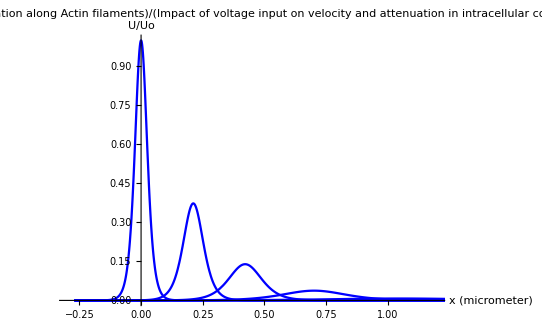

```mathematica
Print["Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot"]

SolNormTot2=Plot[ {-Wx[x*10^-6,0]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/10]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/5]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/3]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/2]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM]/wo^2/2},{x,-25*beta*10^6,435*beta*10^6},PlotRange->{{-0.3,1.2},{0,1}},Axes->True,AxesLabel->{"x (micrometer)","U/Uo"},PlotLabel->Style["Soliton propagation along Actin filaments" /" in intracellular conditions" / "Impact of voltage input on velocity and attenuation",Black,FontSize->18,Bold],AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
NormSolSP22Data2=Cases[SolNormTot2,Line[{x__}]->x,∞];
```

{{-0.27,3.17748×10^-7},{-0.268476,3.48457×10^-7},{-0.266953,3.82135×10^-7},{-0.265429,4.19067×10^-7},{-0.263905,4.59568×10^-7},{-0.262382,5.03984×10^-7},{-0.260858,5.52693×10^-7},{-0.259334,6.06109×10^-7},{-0.257811,6.64687×10^-7},{-0.256287,7.28927×10^-7},{-0.254763,7.99376×10^-7},{-0.253239,8.76633×10^-7},{-0.251716,9.61357×10^-7},{-0.250192,1.05427×10^-6},{-0.248668,1.15616×10^-6},{-0.247145,1.2679×10^-6},{-0.245621,1.39044×10^-6},{-0.244097,1.52482×10^-6},{-0.242574,1.67219×10^-6},{-0.24105,1.8338×10^-6},{-0.239526,2.01103×10^-6},{-0.238003,2.20539×10^-6},{-0.236479,2.41854×10^-6},{-0.234955,2.65228×10^-6},{-0.233432,2.90862×10^-6},{-0.231908,3.18973×10^-6},{-0.230384,3.498×10^-6},{-0.228861,3.83607×10^-6},{-0.227337,4.20682×10^-6},{-0.225813,4.61339×10^-6},{-0.22429,5.05926×10^-6},{-0.222766,5.54822×10^-6},{-0.221242,6.08444×10^-6},{-0.219719,6.67248×10^-6},{-0.218195,7.31735×10^-6},{-0.216671,8.02455×10^-6},{-0.215148,8.8001×10^-6},{-0.213624,9.65059×10^-6},{-0.2121,0.0000105833},{-0.210577,0.0000116061},{-0.209053,0.0000127278},{-0.207529,0.0000139579},{-0.206006,0.0000153069},{-0.204482,0.0000167862},{-0.202958,0.0000184086},{-0.201435,0.0000201877},{-0.199911,0.0000221387},{-0.198387,0.0000242784},{-0.196864,0.0000266248},{-0.19534,0.0000291979},{-0.193816,0.0000320198},{-0.192293,0.0000351143},{-0.190769,0.000038508},{-0.189245,0.0000422296},{-0.187722,0.0000463108},{-0.186198,0.0000507865},{-0.184674,0.0000556947},{-0.183151,0.0000610773},{-0.181627,0.0000669801},{-0.180103,0.0000734532},{-0.17858,0.000080552},{-0.177056,0.0000883367},{-0.175532,0.0000968738},{-0.174008,0.000106236},{-0.172485,0.000116503},{-0.170833,0.000128757},{-0.169181,0.0001423},{-0.167529,0.000157267},{-0.165877,0.000173809},{-0.164226,0.00019209},{-0.162574,0.000212294},{-0.160922,0.000234622},{-0.15927,0.000259299},{-0.157618,0.000286571},{-0.155966,0.000316711},{-0.154315,0.00035002},{-0.152663,0.000386831},{-0.151011,0.000427514},{-0.149359,0.000472473},{-0.147707,0.00052216},{-0.146055,0.00057707},{-0.144404,0.000637753},{-0.142752,0.000704815},{-0.1411,0.000778926},{-0.139448,0.000860826},{-0.137796,0.000951333},{-0.136144,0.00105135},{-0.134493,0.00116188},{-0.132841,0.00128402},{-0.131189,0.00141899},{-0.129537,0.00156814},{-0.127885,0.00173295},{-0.126233,0.00191506},{-0.124582,0.00211629},{-0.12293,0.00233865},{-0.121278,0.00258433},{-0.119626,0.00285579},{-0.117974,0.00315572},{-0.116322,0.00348709},{-0.114671,0.00385319},{-0.113019,0.00425764},{-0.111367,0.00470445},{-0.109715,0.00519802},{-0.108063,0.00574323},{-0.106411,0.00634545},{-0.10476,0.00701058},{-0.103108,0.00774517},{-0.101456,0.00855639},{-0.099804,0.00945218},{-0.0981522,0.0104412},{-0.0965003,0.0115332},{-0.0948485,0.0127386},{-0.0931967,0.0140692},{-0.0915448,0.0155376},{-0.089893,0.0171579},{-0.0882412,0.0189456},{-0.0865893,0.0209175},{-0.0849375,0.0230923},{-0.0832856,0.0254902},{-0.0816338,0.0281336},{-0.079982,0.0310466},{-0.0783301,0.0342561},{-0.0766783,0.0377907},{-0.0750265,0.0416823},{-0.0733746,0.0459649},{-0.0717228,0.050676},{-0.070071,0.0558557},{-0.0684191,0.0615476},{-0.0667673,0.0677987},{-0.0652249,0.0741848},{-0.0636825,0.0811461},{-0.0621402,0.0887292},{-0.0605978,0.0969834},{-0.0590554,0.105961},{-0.0575131,0.115715},{-0.0544283,0.137786},{-0.0528859,0.150221},{-0.0513436,0.163672},{-0.0498012,0.178199},{-0.0482588,0.193865},{-0.0467164,0.21073},{-0.0451741,0.228851},{-0.0420893,0.269073},{-0.040547,0.291262},{-0.0390046,0.314881},{-0.0359198,0.366465},{-0.0343775,0.39442},{-0.0328351,0.423778},{-0.0297504,0.486442},{-0.028208,0.519548},{-0.0266656,0.553651},{-0.0235809,0.624086},{-0.0174114,0.766538},{-0.015869,0.80056},{-0.0143266,0.833179},{-0.0127843,0.863983},{-0.0112419,0.892557},{-0.00969952,0.918495},{-0.00815715,0.94141},{-0.00661477,0.960944},{-0.0050724,0.976784},{-0.00353003,0.988665},{-0.00198766,0.996388},{-0.000445286,0.999818},{0.00109709,0.998898},{0.00263946,0.993642},{0.00418183,0.984141},{0.0057242,0.970559},{0.00726657,0.953123},{0.00880895,0.932119},{0.0103513,0.907881},{0.0118937,0.88078},{0.0134361,0.851214},{0.0149784,0.819592},{0.0165208,0.78633},{0.0196055,0.716503},{0.0211479,0.680699},{0.0226903,0.644769},{0.025775,0.573727},{0.0319445,0.441347},{0.0334566,0.411782},{0.0349688,0.383535},{0.037993,0.331157},{0.0395051,0.307058},{0.0410172,0.284347},{0.0440415,0.24299},{0.0455536,0.224273},{0.0470657,0.206803},{0.0485778,0.190529},{0.0500899,0.175395},{0.051602,0.161344},{0.0531142,0.148319},{0.0561384,0.12511},{0.0576505,0.114813},{0.0591626,0.105312},{0.0606747,0.0965549},{0.0621869,0.08849},{0.063699,0.0810687},{0.0652111,0.0742445},{0.0682353,0.0622146},{0.0697474,0.0569287},{0.0712596,0.0520794},{0.0727717,0.0476329},{0.0742838,0.0435572},{0.0757959,0.039823},{0.077308,0.0364029},{0.0788201,0.0332714},{0.0803323,0.0304051},{0.0818444,0.0277821},{0.0833565,0.0253825},{0.0848686,0.0231876},{0.0863807,0.0211805},{0.0878928,0.0193454},{0.089405,0.0176679},{0.0909171,0.0161346},{0.0924292,0.0147334},{0.0939413,0.0134531},{0.0954534,0.0122833},{0.0969655,0.0112147},{0.0984777,0.0102385},{0.0999898,0.00934695},{0.101502,0.00853267},{0.103014,0.00778905},{0.104526,0.00711},{0.106038,0.00648996},{0.10755,0.00592383},{0.109062,0.00540695},{0.110575,0.00493506},{0.112087,0.00450426},{0.113599,0.00411098},{0.115111,0.00375198},{0.116623,0.00342428},{0.118135,0.00312516},{0.119647,0.00285212},{0.121159,0.00260291},{0.122672,0.00237545},{0.124184,0.00216784},{0.125696,0.00197836},{0.127208,0.00180543},{0.12872,0.0016476},{0.13036,0.00149195},{0.132001,0.00135098},{0.133641,0.00122333},{0.135281,0.00110774},{0.136921,0.00100306},{0.138562,0.000908268},{0.140202,0.000822431},{0.141842,0.000744703},{0.143483,0.000674319},{0.145123,0.000610585},{0.146763,0.000552873},{0.148403,0.000500615},{0.150044,0.000453295},{0.151684,0.000410447},{0.153324,0.000371648},{0.154964,0.000336517},{0.156605,0.000304706},{0.158245,0.000275901},{0.159885,0.000249819},{0.161526,0.000226203},{0.163166,0.000204819},{0.164806,0.000185456},{0.166446,0.000167923},{0.168087,0.000152048},{0.169727,0.000137674},{0.171367,0.000124658},{0.173008,0.000112873},{0.174648,0.000102202},{0.176288,0.0000925398},{0.177928,0.000083791},{0.179569,0.0000758692},{0.181209,0.0000686964},{0.182849,0.0000622017},{0.18449,0.000056321},{0.18613,0.0000509963},{0.18777,0.0000461749},{0.18941,0.0000418094},{0.191051,0.0000378566},{0.192691,0.0000342775},{0.194331,0.0000310368},{0.195971,0.0000281025},{0.197612,0.0000254456},{0.199252,0.0000230398},{0.200892,0.0000208615},{0.202533,0.0000188892},{0.204173,0.0000171033},{0.205813,0.0000154863},{0.207453,0.0000140222},{0.209094,0.0000126965},{0.210734,0.0000114961},{0.212374,0.0000104092},{0.214015,9.42505×10^-6},{0.215655,8.53396×10^-6},{0.217295,7.72712×10^-6},{0.218935,6.99656×10^-6},{0.220576,6.33507×10^-6},{0.222216,5.73613×10^-6},{0.223856,5.1938×10^-6},{0.225497,4.70276×10^-6},{0.227137,4.25814×10^-6},{0.228777,3.85555×10^-6},{0.230417,3.49103×10^-6},{0.232058,3.16097×10^-6},{0.233698,2.86212×10^-6},{0.235229,2.60875×10^-6},{0.23676,2.37781×10^-6},{0.23829,2.16732×10^-6},{0.239821,1.97546×10^-6},{0.241352,1.80059×10^-6},{0.242883,1.64119×10^-6},{0.244414,1.49591×10^-6},{0.245944,1.36348×10^-6},{0.247475,1.24278×10^-6},{0.249006,1.13277×10^-6},{0.250537,1.03249×10^-6},{0.252068,9.41091×10^-7},{0.253599,8.57782×10^-7},{0.255129,7.81848×10^-7},{0.25666,7.12636×10^-7},{0.258191,6.49551×10^-7},{0.259722,5.9205×10^-7},{0.261253,5.39639×10^-7},{0.262783,4.91869×10^-7},{0.264314,4.48326×10^-7},{0.265845,4.08639×10^-7},{0.267376,3.72465×10^-7},{0.268907,3.39493×10^-7},{0.270437,3.09439×10^-7},{0.271968,2.82047×10^-7},{0.273499,2.57079×10^-7},{0.27503,2.34321×10^-7},{0.276561,2.13578×10^-7},{0.278092,1.94672×10^-7},{0.279622,1.77438×10^-7},{0.281153,1.61731×10^-7},{0.282684,1.47414×10^-7},{0.284215,1.34364×10^-7},{0.285746,1.2247×10^-7},{0.287276,1.11628×10^-7},{0.288807,1.01747×10^-7},{0.290338,9.27396×10^-8},{0.291869,8.45299×10^-8},{0.2934,7.7047×10^-8},{0.294931,7.02265×10^-8},{0.296461,6.40098×10^-8},{0.297992,5.83434×10^-8},{0.299523,5.31786×10^-8},{0.301054,4.84711×10^-8},{0.302585,4.41802×10^-8},{0.304115,4.02692×10^-8},{0.305646,3.67044×10^-8},{0.307177,3.34552×10^-8},{0.308708,3.04936×10^-8},{0.310239,2.77942×10^-8},{0.31177,2.53338×10^-8},{0.3133,2.30911×10^-8},{0.314831,2.1047×10^-8},{0.316362,1.91839×10^-8},{0.317893,1.74856×10^-8},{0.319424,1.59377×10^-8},{0.320954,1.45269×10^-8},{0.322485,1.32409×10^-8},{0.324016,1.20688×10^-8},{0.325547,1.10004×10^-8},{0.327078,1.00266×10^-8},{0.328608,9.139×10^-9},{0.330139,8.32998×10^-9},{0.33167,7.59258×10^-9},{0.333329,6.86696×10^-9},{0.334988,6.21068×10^-9},{0.336647,5.61713×10^-9},{0.338306,5.0803×10^-9},{0.339965,4.59478×10^-9},{0.341624,4.15566×10^-9},{0.343283,3.7585×10^-9},{0.344942,3.39931×10^-9},{0.346601,3.07444×10^-9},{0.34826,2.78061×10^-9},{0.349919,2.51487×10^-9},{0.351578,2.27453×10^-9},{0.353237,2.05715×10^-9},{0.354896,1.86055×10^-9},{0.356555,1.68274×10^-9},{0.358214,1.52192×10^-9},{0.359873,1.37647×10^-9},{0.361532,1.24492×10^-9},{0.363191,1.12594×10^-9},{0.36485,1.01834×10^-9},{0.366509,9.21015×10^-10},{0.368168,8.32994×10^-10},{0.369827,7.53385×10^-10},{0.371486,6.81385×10^-10},{0.373145,6.16265×10^-10},{0.374804,5.57369×10^-10},{0.376463,5.04101×10^-10},{0.378122,4.55924×10^-10},{0.37978,4.12352×10^-10},{0.381439,3.72944×10^-10},{0.383098,3.37301×10^-10},{0.384757,3.05066×10^-10},{0.386416,2.75911×10^-10},{0.388075,2.49542×10^-10},{0.389734,2.25693×10^-10},{0.391393,2.04124×10^-10},{0.393052,1.84616×10^-10},{0.394711,1.66972×10^-10},{0.39637,1.51015×10^-10},{0.398029,1.36582×10^-10},{0.399688,1.23529×10^-10},{0.401347,1.11724×10^-10},{0.403006,1.01046×10^-10},{0.404665,9.13892×10^-11},{0.406324,8.26552×10^-11},{0.407983,7.47558×10^-11},{0.409642,6.76115×10^-11},{0.411301,6.11498×10^-11},{0.41296,5.53058×10^-11},{0.414619,5.00202×10^-11},{0.416278,4.52398×10^-11},{0.417937,4.09163×10^-11},{0.419596,3.70059×10^-11},{0.421255,3.34693×10^-11},{0.422914,3.02706×10^-11},{0.424573,2.73777×10^-11},{0.426232,2.47612×10^-11},{0.427891,2.23948×10^-11},{0.42955,2.02545×10^-11},{0.431209,1.83188×10^-11},{0.432868,1.65681×10^-11},{0.434527,1.49847×10^-11},{0.436186,1.35526×10^-11},{0.437845,1.22574×10^-11},{0.439473,1.11063×10^-11},{0.441102,1.00633×10^-11},{0.442731,9.11821×10^-12},{0.44436,8.26191×10^-12},{0.445988,7.48602×10^-12},{0.447617,6.783×10^-12},{0.449246,6.146×10^-12},{0.450875,5.56882×10^-12},{0.452503,5.04585×10^-12},{0.454132,4.57198×10^-12},{0.455761,4.14262×10^-12},{0.457389,3.75358×10^-12},{0.459018,3.40108×10^-12},{0.460647,3.08168×10^-12},{0.462276,2.79228×10^-12},{0.463904,2.53005×10^-12},{0.465533,2.29245×10^-12},{0.467162,2.07716×10^-12},{0.46879,1.88209×10^-12},{0.470419,1.70534×10^-12},{0.472048,1.54519×10^-12},{0.473677,1.40008×10^-12},{0.475305,1.2686×10^-12},{0.476934,1.14946×10^-12},{0.478563,1.04152×10^-12},{0.480192,9.43705×10^-13},{0.48182,8.55081×10^-13},{0.483449,7.74779×10^-13},{0.485078,7.02018×10^-13},{0.486706,6.36091×10^-13},{0.488335,5.76355×10^-13},{0.489964,5.22229×10^-13},{0.491593,4.73185×10^-13},{0.493221,4.28748×10^-13},{0.49485,3.88484×10^-13},{0.496479,3.52001×10^-13},{0.498108,3.18944×10^-13},{0.499736,2.88991×10^-13},{0.501365,2.61852×10^-13},{0.502994,2.37261×10^-13},{0.504622,2.1498×10^-13},{0.506251,1.94791×10^-13},{0.50788,1.76498×10^-13},{0.509509,1.59922×10^-13},{0.511137,1.44904×10^-13},{0.512766,1.31296×10^-13},{0.514395,1.18966×10^-13},{0.516023,1.07793×10^-13},{0.517652,9.76704×10^-14},{0.519281,8.84981×10^-14},{0.52091,8.01871×10^-14},{0.522538,7.26566×10^-14},{0.524167,6.58333×10^-14},{0.525796,5.96509×10^-14},{0.527425,5.4049×10^-14},{0.529053,4.89732×10^-14},{0.530682,4.4374×10^-14},{0.532311,4.02068×10^-14},{0.533939,3.64309×10^-14},{0.535568,3.30097×10^-14},{0.537197,2.99097×10^-14},{0.538826,2.71008×10^-14},{0.540454,2.45557×10^-14},{0.542083,2.22497×10^-14},{0.543602,2.02943×10^-14},{0.545122,1.85107×10^-14},{0.546641,1.68839×10^-14},{0.54816,1.54×10^-14},{0.549679,1.40466×10^-14},{0.551199,1.28121×10^-14},{0.552718,1.16861×10^-14},{0.554237,1.0659×10^-14},{0.555756,9.72225×10^-15},{0.557276,8.86781×10^-15},{0.558795,8.08845×10^-15},{0.560314,7.37759×10^-15},{0.561833,6.72921×10^-15},{0.563353,6.13781×10^-15},{0.564872,5.59838×10^-15},{0.566391,5.10636×10^-15},{0.56791,4.65758×10^-15},{0.56943,4.24825×10^-15},{0.570949,3.87489×10^-15},{0.572468,3.53434×10^-15},{0.573987,3.22372×10^-15},{0.575507,2.9404×10^-15},{0.577026,2.68198×10^-15},{0.578545,2.44628×10^-15},{0.580065,2.23128×10^-15},{0.581584,2.03518×10^-15},{0.583103,1.85632×10^-15},{0.584622,1.69318×10^-15},{0.587661,1.40864×10^-15},{0.590699,1.17192×10^-15},{0.593738,9.74984×10^-16},{0.596776,8.1114×10^-16},{0.599815,6.7483×10^-16},{0.602853,5.61427×10^-16},{0.60893,3.88588×10^-16},{0.615007,2.68959×10^-16},{0.616527,2.45322×10^-16},{0.618046,2.23761×10^-16},{0.621085,1.86159×10^-16},{0.627162,1.28849×10^-16},{0.639316,6.17269×10^-17},{0.640963,5.58668×10^-17},{0.64261,5.0563×10^-17},{0.645905,4.14181×10^-17},{0.652495,2.77912×10^-17},{0.665674,1.25123×10^-17},{0.692033,2.53631×10^-18},{0.744751,1.04215×10^-19},{0.84318,2.68914×10^-22},{0.939673,7.80212×10^-25},{1.04437,1.37759×10^-27},{1.14206,3.71748×10^-30},{1.24795,6.10501×10^-33},{1.35191,1.12731×10^-35},{1.44886,3.18142×10^-38},{1.55401,5.46396×10^-41},{1.65216,1.43422×10^-43},{1.7585,2.29105×10^-46},{1.86292,4.115×10^-49},{1.96032,1.12961×10^-51},{2.06593,1.8871×10^-54},{2.16454,4.8182×10^-57},{2.26121,1.38322×10^-59},{2.36608,2.41662×10^-62},{2.46394,6.45278×10^-65},{2.57001,1.04856×10^-67},{2.67414,1.91583×10^-70},{2.77126,5.34989×10^-73},{2.87659,9.09159×10^-76},{2.97491,2.36134×10^-78},{3.0713,6.89597×10^-81},{3.17588,1.22557×10^-83},{3.27346,3.32895×10^-86},{3.37925,5.50278×10^-89},{3.47803,1.39021×10^-91},{3.57487,3.9491×10^-94},{3.67991,6.82687×10^-97},{3.77795,1.80372×10^-99},{3.88419,2.90017×10^-102},{3.9885,5.2432×10^-105},{4.0858,1.44875×10^-107},{4.1913,2.43611×10^-110},{4.2898,6.26072×10^-113},{4.38636,1.80913×10^-115},{4.49112,3.18143×10^-118},{4.58887,8.55065×10^-121},{4.59058,7.71191×10^-121},{4.59228,6.95544×10^-121},{4.59569,5.65783×10^-121},{4.60252,3.7437×10^-121},{4.61616,1.63909×10^-121},{4.64344,3.142×10^-122},{4.64514,2.83379×10^-122},{4.64685,2.55583×10^-122},{4.65026,2.07901×10^-122},{4.65708,1.37565×10^-122},{4.67072,6.02295×10^-123},{4.67242,5.43215×10^-123},{4.67413,4.8993×10^-123},{4.67754,3.98529×10^-123},{4.68436,2.637×10^-123},{4.68606,2.37834×10^-123},{4.68777,2.14504×10^-123},{4.69118,1.74486×10^-123},{4.69288,1.57371×10^-123},{4.69459,1.41934×10^-123},{4.69629,1.28012×10^-123},{4.698,1.15455×10^-123},{-0.27,2.75157×10^-8},{-0.268476,2.91106×10^-8},{-0.266953,3.0798×10^-8},{-0.263905,3.44718×10^-8},{-0.262382,3.647×10^-8},{-0.260858,3.85839×10^-8},{-0.257811,4.31866×10^-8},{-0.256287,4.56899×10^-8},{-0.254763,4.83383×10^-8},{-0.251716,5.41045×10^-8},{-0.250192,5.72406×10^-8},{-0.248668,6.05586×10^-8},{-0.245621,6.77825×10^-8},{-0.244097,7.17115×10^-8},{-0.242574,7.58682×10^-8},{-0.239526,8.49185×10^-8},{-0.238003,8.98407×10^-8},{-0.236479,9.50483×10^-8},{-0.233432,1.06387×10^-7},{-0.231908,1.12553×10^-7},{-0.230384,1.19077×10^-7},{-0.227337,1.33282×10^-7},{-0.225813,1.41008×10^-7},{-0.22429,1.49181×10^-7},{-0.221242,1.66977×10^-7},{-0.219719,1.76655×10^-7},{-0.218195,1.86895×10^-7},{-0.215148,2.0919×10^-7},{-0.213624,2.21315×10^-7},{-0.2121,2.34144×10^-7},{-0.209053,2.62074×10^-7},{-0.207529,2.77265×10^-7},{-0.206006,2.93337×10^-7},{-0.202958,3.28329×10^-7},{-0.201435,3.4736×10^-7},{-0.199911,3.67495×10^-7},{-0.196864,4.11333×10^-7},{-0.19534,4.35176×10^-7},{-0.193816,4.604×10^-7},{-0.190769,5.15321×10^-7},{-0.189245,5.45191×10^-7},{-0.187722,5.76793×10^-7},{-0.184674,6.45598×10^-7},{-0.183151,6.8302×10^-7},{-0.181627,7.22611×10^-7},{-0.17858,8.0881×10^-7},{-0.177056,8.55693×10^-7},{-0.175532,9.05293×10^-7},{-0.172485,1.01328×10^-6},{-0.170833,1.07711×10^-6},{-0.169181,1.14496×10^-6},{-0.167529,1.21708×10^-6},{-0.165877,1.29375×10^-6},{-0.164226,1.37524×10^-6},{-0.162574,1.46187×10^-6},{-0.15927,1.65184×10^-6},{-0.157618,1.75589×10^-6},{-0.155966,1.86649×10^-6},{-0.154315,1.98406×10^-6},{-0.152663,2.10904×10^-6},{-0.151011,2.24189×10^-6},{-0.149359,2.38311×10^-6},{-0.146055,2.69279×10^-6},{-0.144404,2.86241×10^-6},{-0.142752,3.04271×10^-6},{-0.1411,3.23437×10^-6},{-0.139448,3.43811×10^-6},{-0.137796,3.65468×10^-6},{-0.136144,3.88489×10^-6},{-0.132841,4.38972×10^-6},{-0.131189,4.66623×10^-6},{-0.129537,4.96016×10^-6},{-0.127885,5.2726×10^-6},{-0.126233,5.60473×10^-6},{-0.124582,5.95777×10^-6},{-0.12293,6.33305×10^-6},{-0.119626,7.15602×10^-6},{-0.117974,7.60678×10^-6},{-0.116322,8.08593×10^-6},{-0.114671,8.59526×10^-6},{-0.113019,9.13668×10^-6},{-0.111367,9.7122×10^-6},{-0.109715,0.000010324},{-0.106411,0.0000116655},{-0.10476,0.0000124004},{-0.103108,0.0000131814},{-0.101456,0.0000140117},{-0.099804,0.0000148943},{-0.0981522,0.0000158325},{-0.0965003,0.0000168298},{-0.0931967,0.0000190168},{-0.0915448,0.0000202146},{-0.089893,0.0000214879},{-0.0882412,0.0000228414},{-0.0865893,0.0000242802},{-0.0849375,0.0000258095},{-0.0832856,0.0000274352},{-0.079982,0.0000310003},{-0.0783301,0.0000329529},{-0.0766783,0.0000350286},{-0.0750265,0.0000372349},{-0.0733746,0.0000395803},{-0.0717228,0.0000420733},{-0.070071,0.0000447234},{-0.0667673,0.0000505348},{-0.0652249,0.0000535008},{-0.0636825,0.0000566408},{-0.0605978,0.0000634846},{-0.0590554,0.0000672106},{-0.0575131,0.0000711553},{-0.0544283,0.0000797526},{-0.0528859,0.0000844333},{-0.0513436,0.0000893886},{-0.0482588,0.000100189},{-0.0467164,0.000106069},{-0.0451741,0.000112293},{-0.0420893,0.000125861},{-0.040547,0.000133247},{-0.0390046,0.000141066},{-0.0359198,0.000158109},{-0.0343775,0.000167387},{-0.0328351,0.00017721},{-0.0297504,0.000198618},{-0.028208,0.000210273},{-0.0266656,0.000222611},{-0.0235809,0.000249502},{-0.0220385,0.000264142},{-0.0204961,0.000279641},{-0.0174114,0.000313418},{-0.015869,0.000331806},{-0.0143266,0.000351272},{-0.0112419,0.000393697},{-0.00969952,0.000416793},{-0.00815715,0.000441243},{-0.0050724,0.000494526},{-0.00353003,0.000523533},{-0.00198766,0.000554239},{0.00109709,0.000621157},{0.00263946,0.000657584},{0.00418183,0.000696146},{0.00726657,0.000780179},{0.00880895,0.000825922},{0.0103513,0.000874344},{0.0134361,0.000979859},{0.0149784,0.00103729},{0.0165208,0.00109809},{0.0196055,0.00123056},{0.0211479,0.00130266},{0.0226903,0.00137898},{0.025775,0.00154527},{0.0273174,0.00163578},{0.0288598,0.00173157},{0.0319445,0.00194026},{0.0334566,0.00205154},{0.0349688,0.00216919},{0.037993,0.00242504},{0.0395051,0.00256403},{0.0410172,0.00271096},{0.0440415,0.00303045},{0.0455536,0.00320398},{0.0470657,0.00338741},{0.0500899,0.00378622},{0.051602,0.0040028},{0.0531142,0.0042317},{0.0561384,0.00472927},{0.0576505,0.00499943},{0.0591626,0.00528492},{0.0621869,0.00590533},{0.063699,0.0062421},{0.0652111,0.00659791},{0.0682353,0.00737091},{0.0697474,0.00779038},{0.0712596,0.00823346},{0.0742838,0.00919566},{0.0757959,0.0097176},{0.077308,0.0102687},{0.0803323,0.0114651},{0.0818444,0.0121136},{0.0833565,0.0127983},{0.0863807,0.0142835},{0.0878928,0.0150882},{0.089405,0.0159372},{0.0924292,0.0177776},{0.0939413,0.018774},{0.0954534,0.0198247},{0.0984777,0.0221001},{0.0999898,0.0233307},{0.101502,0.0246275},{0.104526,0.0274327},{0.106038,0.028948},{0.10755,0.0305433},{0.110575,0.0339892},{0.112087,0.0358477},{0.113599,0.0378022},{0.116623,0.0420164},{0.118135,0.044285},{0.119647,0.0466675},{0.122672,0.0517928},{0.124184,0.0545454},{0.125696,0.0574312},{0.12872,0.063622},{0.13036,0.0672249},{0.132001,0.0710083},{0.135281,0.0791411},{0.136921,0.0835023},{0.138562,0.0880676},{0.141842,0.0978308},{0.143483,0.103038},{0.145123,0.108467},{0.148403,0.120001},{0.154964,0.145806},{0.156605,0.152819},{0.158245,0.160048},{0.161526,0.175128},{0.168087,0.207456},{0.181209,0.276407},{0.182849,0.284877},{0.18449,0.293194},{0.18777,0.309207},{0.18941,0.31682},{0.191051,0.324113},{0.194331,0.337572},{0.195971,0.343656},{0.197612,0.349258},{0.199252,0.35434},{0.200892,0.358868},{0.202533,0.362811},{0.204173,0.366142},{0.205813,0.368838},{0.207453,0.370877},{0.209094,0.372247},{0.210734,0.372937},{0.212374,0.372941},{0.214015,0.37226},{0.215655,0.370899},{0.217295,0.368867},{0.218935,0.36618},{0.220576,0.362857},{0.222216,0.358921},{0.223856,0.3544},{0.225497,0.349325},{0.227137,0.34373},{0.228777,0.337651},{0.230417,0.331129},{0.233698,0.316914},{0.235229,0.309822},{0.23676,0.302486},{0.239821,0.287219},{0.245944,0.255221},{0.247475,0.247096},{0.249006,0.238975},{0.252068,0.222845},{0.258191,0.191618},{0.259722,0.184126},{0.261253,0.176786},{0.264314,0.162608},{0.265845,0.155786},{0.267376,0.14915},{0.270437,0.136455},{0.271968,0.130402},{0.273499,0.124548},{0.276561,0.113437},{0.282684,0.0935674},{0.284215,0.0890755},{0.285746,0.0847669},{0.288807,0.0766823},{0.290338,0.0728973},{0.291869,0.0692774},{0.294931,0.062513},{0.296461,0.0593583},{0.297992,0.0563485},{0.301054,0.0507426},{0.302585,0.0481365},{0.304115,0.0456547},{0.307177,0.0410446},{0.308708,0.0389067},{0.310239,0.0368741},{0.3133,0.0331063},{0.314831,0.0313625},{0.316362,0.0297065},{0.319424,0.0266423},{0.320954,0.0252264},{0.322485,0.0238832},{0.325547,0.0214011},{0.327078,0.0202556},{0.328608,0.0191698},{0.33167,0.0171655},{0.333329,0.0161665},{0.334988,0.0152243},{0.338306,0.0134984},{0.339965,0.012709},{0.341624,0.011965},{0.344942,0.0106031},{0.346601,0.00998068},{0.34826,0.00939429},{0.349919,0.00884193},{0.351578,0.00832168},{0.353237,0.00783172},{0.354896,0.00737031},{0.358214,0.00652672},{0.359873,0.00614155},{0.361532,0.00577893},{0.363191,0.00543756},{0.36485,0.00511622},{0.366509,0.00481374},{0.368168,0.00452904},{0.371486,0.00400888},{0.373145,0.00377153},{0.374804,0.00354817},{0.376463,0.00333798},{0.378122,0.00314019},{0.37978,0.00295407},{0.381439,0.00277894},{0.384757,0.00245911},{0.386416,0.00231323},{0.388075,0.00217598},{0.389734,0.00204685},{0.391393,0.00192536},{0.393052,0.00181107},{0.394711,0.00170355},{0.398029,0.00150723},{0.399688,0.00141771},{0.401347,0.0013335},{0.403006,0.00125428},{0.404665,0.00117976},{0.406324,0.00110966},{0.407983,0.00104372},{0.411301,0.000923351},{0.41296,0.00086847},{0.414619,0.000816847},{0.416278,0.000768289},{0.417937,0.000722615},{0.419596,0.000679654},{0.421255,0.000639245},{0.424573,0.000565486},{0.426232,0.00053186},{0.427891,0.000500232},{0.42955,0.000470484},{0.431209,0.000442503},{0.432868,0.000416186},{0.434527,0.000391433},{0.437845,0.000346255},{0.439473,0.000326024},{0.441102,0.000306974},{0.442731,0.000289038},{0.44436,0.000272148},{0.445988,0.000256246},{0.447617,0.000241272},{0.450875,0.000213898},{0.452503,0.000201398},{0.454132,0.000189629},{0.455761,0.000178547},{0.457389,0.000168113},{0.459018,0.000158288},{0.460647,0.000149037},{0.463904,0.000132126},{0.465533,0.000124404},{0.467162,0.000117133},{0.46879,0.000110287},{0.470419,0.000103842},{0.472048,0.0000977724},{0.473677,0.000092058},{0.476934,0.0000816114},{0.478563,0.0000768414},{0.480192,0.0000723502},{0.48182,0.0000681215},{0.483449,0.0000641398},{0.485078,0.0000603909},{0.486706,0.0000568611},{0.489964,0.0000504084},{0.491593,0.000047462},{0.493221,0.0000446879},{0.49485,0.0000420758},{0.496479,0.0000396165},{0.498108,0.0000373009},{0.499736,0.0000351206},{0.502994,0.0000311349},{0.504622,0.000029315},{0.506251,0.0000276015},{0.50788,0.0000259882},{0.509509,0.0000244691},{0.511137,0.0000230389},{0.512766,0.0000216922},{0.516023,0.0000192304},{0.517652,0.0000181063},{0.519281,0.000017048},{0.52091,0.0000160515},{0.522538,0.0000151132},{0.524167,0.0000142298},{0.525796,0.0000133981},{0.529053,0.0000118775},{0.530682,0.0000111833},{0.532311,0.0000105296},{0.533939,9.91408×10^-6},{0.535568,9.33457×10^-6},{0.537197,8.78894×10^-6},{0.538826,8.2752×10^-6},{0.542083,7.33605×10^-6},{0.543602,6.93525×10^-6},{0.545122,6.55635×10^-6},{0.54816,5.85952×10^-6},{0.549679,5.53939×10^-6},{0.551199,5.23675×10^-6},{0.554237,4.68018×10^-6},{0.555756,4.42448×10^-6},{0.557276,4.18275×10^-6},{0.560314,3.73819×10^-6},{0.561833,3.53396×10^-6},{0.563353,3.34089×10^-6},{0.566391,2.9858×10^-6},{0.56791,2.82268×10^-6},{0.56943,2.66846×10^-6},{0.572468,2.38485×10^-6},{0.573987,2.25455×10^-6},{0.575507,2.13138×10^-6},{0.578545,1.90485×10^-6},{0.580065,1.80078×10^-6},{0.581584,1.70239×10^-6},{0.584622,1.52146×10^-6},{0.586142,1.43833×10^-6},{0.587661,1.35975×10^-6},{0.590699,1.21523×10^-6},{0.592219,1.14884×10^-6},{0.593738,1.08607×10^-6},{0.596776,9.70639×10^-7},{0.598296,9.17609×10^-7},{0.599815,8.67476×10^-7},{0.602853,7.75277×10^-7},{0.604373,7.3292×10^-7},{0.605892,6.92878×10^-7},{0.60893,6.19236×10^-7},{0.61045,5.85404×10^-7},{0.611969,5.53421×10^-7},{0.615007,4.94601×10^-7},{0.616527,4.67579×10^-7},{0.618046,4.42033×10^-7},{0.621085,3.95052×10^-7},{0.622604,3.73469×10^-7},{0.624123,3.53065×10^-7},{0.627162,3.15539×10^-7},{0.628681,2.983×10^-7},{0.6302,2.82003×10^-7},{0.633239,2.5203×10^-7},{0.634758,2.38261×10^-7},{0.636277,2.25244×10^-7},{0.639316,2.01304×10^-7},{0.640963,1.89406×10^-7},{0.64261,1.78211×10^-7},{0.644258,1.67678×10^-7},{0.645905,1.57767×10^-7},{0.647553,1.48443×10^-7},{0.6492,1.39669×10^-7},{0.652495,1.23647×10^-7},{0.654142,1.16339×10^-7},{0.65579,1.09463×10^-7},{0.657437,1.02993×10^-7},{0.659085,9.69056×10^-8},{0.660732,9.1178×10^-8},{0.66238,8.5789×10^-8},{0.665674,7.59476×10^-8},{0.667322,7.14588×10^-8},{0.668969,6.72353×10^-8},{0.670617,6.32613×10^-8},{0.672264,5.95223×10^-8},{0.673911,5.60043×10^-8},{0.675559,5.26942×10^-8},{0.678854,4.66493×10^-8},{0.680501,4.38921×10^-8},{0.682149,4.12979×10^-8},{0.683796,3.8857×10^-8},{0.685443,3.65604×10^-8},{0.687091,3.43995×10^-8},{0.688738,3.23664×10^-8},{0.692033,2.86534×10^-8},{0.693681,2.69599×10^-8},{0.695328,2.53664×10^-8},{0.696975,2.38672×10^-8},{0.698623,2.24565×10^-8},{0.70027,2.11292×10^-8},{0.701918,1.98804×10^-8},{0.705213,1.75998×10^-8},{0.70686,1.65596×10^-8},{0.708507,1.55808×10^-8},{0.710155,1.46599×10^-8},{0.711802,1.37935×10^-8},{0.71345,1.29782×10^-8},{0.715097,1.22111×10^-8},{0.718392,1.08103×10^-8},{0.720039,1.01714×10^-8},{0.721687,9.57021×10^-9},{0.723334,9.00457×10^-9},{0.724982,8.47236×10^-9},{0.726629,7.97161×10^-9},{0.728276,7.50045×10^-9},{0.731571,6.64003×10^-9},{0.733219,6.24757×10^-9},{0.734866,5.87831×10^-9},{0.736514,5.53088×10^-9},{0.738161,5.20398×10^-9},{0.739808,4.8964×10^-9},{0.741456,4.607×10^-9},{0.744751,4.07851×10^-9},{0.746289,3.85301×10^-9},{0.747827,3.63999×10^-9},{0.750902,3.24862×10^-9},{0.75244,3.06901×10^-9},{0.753978,2.89933×10^-9},{0.757054,2.5876×10^-9},{0.758592,2.44454×10^-9},{0.76013,2.30938×10^-9},{0.763206,2.06108×10^-9},{0.764744,1.94713×10^-9},{0.766282,1.83947×10^-9},{0.769358,1.64169×10^-9},{0.770896,1.55093×10^-9},{0.772434,1.46518×10^-9},{0.77551,1.30765×10^-9},{0.777048,1.23535×10^-9},{0.778586,1.16705×10^-9},{0.781662,1.04157×10^-9},{0.7832,9.83983×10^-10},{0.784738,9.29581×10^-10},{0.787813,8.29633×10^-10},{0.789351,7.83764×10^-10},{0.790889,7.40431×10^-10},{0.793965,6.60821×10^-10},{0.795503,6.24285×10^-10},{0.797041,5.8977×10^-10},{0.800117,5.26358×10^-10},{0.801655,4.97257×10^-10},{0.803193,4.69765×10^-10},{0.806269,4.19256×10^-10},{0.807807,3.96076×10^-10},{0.809345,3.74178×10^-10},{0.812421,3.33947×10^-10},{0.813959,3.15484×10^-10},{0.815497,2.98041×10^-10},{0.818573,2.65996×10^-10},{0.820111,2.5129×10^-10},{0.821649,2.37396×10^-10},{0.824724,2.11872×10^-10},{0.826262,2.00158×10^-10},{0.8278,1.89091×10^-10},{0.830876,1.6876×10^-10},{0.832414,1.5943×10^-10},{0.833952,1.50616×10^-10},{0.837028,1.34421×10^-10},{0.838566,1.2699×10^-10},{0.840104,1.19969×10^-10},{0.84318,1.0707×10^-10},{0.844688,1.01263×10^-10},{0.846195,9.57717×10^-11},{0.849211,8.56659×10^-11},{0.850718,8.10202×10^-11},{0.852226,7.66264×10^-11},{0.855242,6.85408×10^-11},{0.856749,6.48238×10^-11},{0.858257,6.13084×10^-11},{0.861272,5.48392×10^-11},{0.86278,5.18652×10^-11},{0.864288,4.90526×10^-11},{0.867303,4.38765×10^-11},{0.868811,4.14971×10^-11},{0.870319,3.92467×10^-11},{0.873334,3.51054×10^-11},{0.874842,3.32016×10^-11},{0.876349,3.14011×10^-11},{0.879365,2.80877×10^-11},{0.880873,2.65644×10^-11},{0.88238,2.51238×10^-11},{0.885396,2.24728×10^-11},{0.886903,2.12541×10^-11},{0.888411,2.01015×10^-11},{0.891426,1.79804×10^-11},{0.892934,1.70053×10^-11},{0.894442,1.60831×10^-11},{0.897457,1.4386×10^-11},{0.898965,1.36058×10^-11},{0.900473,1.2868×10^-11},{0.903488,1.15102×10^-11},{0.904996,1.0886×10^-11},{0.906503,1.02956×10^-11},{0.909519,9.20922×10^-12},{0.911027,8.7098×10^-12},{0.912534,8.23747×10^-12},{0.91555,7.36825×10^-12},{0.917057,6.96867×10^-12},{0.918565,6.59076×10^-12},{0.92158,5.8953×10^-12},{0.923088,5.5756×10^-12},{0.924596,5.27323×10^-12},{0.927611,4.7168×10^-12},{0.929119,4.46101×10^-12},{0.930627,4.21908×10^-12},{0.933642,3.77389×10^-12},{0.93515,3.56923×10^-12},{0.936658,3.37567×10^-12},{0.939673,3.01947×10^-12},{0.941309,2.84222×10^-12},{0.942945,2.67537×10^-12},{0.944581,2.51832×10^-12},{0.946216,2.37049×10^-12},{0.947852,2.23134×10^-12},{0.949488,2.10035×10^-12},{0.95276,1.861×10^-12},{0.954396,1.75176×10^-12},{0.956032,1.64892×10^-12},{0.957667,1.55213×10^-12},{0.959303,1.46101×10^-12},{0.960939,1.37525×10^-12},{0.962575,1.29452×10^-12},{0.965847,1.147×10^-12},{0.967483,1.07967×10^-12},{0.969118,1.01629×10^-12},{0.970754,9.56629×10^-13},{0.97239,9.00472×10^-13},{0.974026,8.47612×10^-13},{0.975662,7.97856×10^-13},{0.978934,7.06933×10^-13},{0.98057,6.65435×10^-13},{0.982205,6.26372×10^-13},{0.983841,5.89603×10^-13},{0.985477,5.54991×10^-13},{0.987113,5.22412×10^-13},{0.988749,4.91745×10^-13},{0.992021,4.35707×10^-13},{0.993656,4.1013×10^-13},{0.995292,3.86054×10^-13},{0.996928,3.63392×10^-13},{0.998564,3.4206×10^-13},{1.0002,3.2198×10^-13},{1.00184,3.03079×10^-13},{1.00511,2.68541×10^-13},{1.00674,2.52777×10^-13},{1.00838,2.37938×10^-13},{1.01002,2.23971×10^-13},{1.01165,2.10823×10^-13},{1.01329,1.98447×10^-13},{1.01492,1.86798×10^-13},{1.01819,1.65511×10^-13},{1.01983,1.55795×10^-13},{1.02147,1.46649×10^-13},{1.0231,1.38041×10^-13},{1.02474,1.29937×10^-13},{1.02637,1.2231×10^-13},{1.02801,1.1513×10^-13},{1.03128,1.0201×10^-13},{1.03292,9.60217×10^-14},{1.03455,9.0385×10^-14},{1.03619,8.50792×10^-14},{1.03782,8.00848×10^-14},{1.03946,7.53837×10^-14},{1.0411,7.09585×10^-14},{1.04437,6.28721×10^-14},{1.04589,5.94215×10^-14},{1.04742,5.61602×10^-14},{1.05047,5.01647×10^-14},{1.052,4.74115×10^-14},{1.05353,4.48093×10^-14},{1.05658,4.00257×10^-14},{1.05811,3.78289×10^-14},{1.05963,3.57527×10^-14},{1.06269,3.19359×10^-14},{1.06421,3.01831×10^-14},{1.06574,2.85265×10^-14},{1.06879,2.54812×10^-14},{1.07032,2.40826×10^-14},{1.07184,2.27609×10^-14},{1.0749,2.0331×10^-14},{1.07642,1.92152×10^-14},{1.07795,1.81606×10^-14},{1.081,1.62218×10^-14},{1.08253,1.53315×10^-14},{1.08405,1.449×10^-14},{1.08711,1.29431×10^-14},{1.08863,1.22328×10^-14},{1.09016,1.15614×10^-14},{1.09321,1.03271×10^-14},{1.09474,9.76035×10^-15},{1.09627,9.22466×10^-15},{1.09932,8.23987×10^-15},{1.10085,7.78763×10^-15},{1.10237,7.36022×10^-15},{1.10542,6.57447×10^-15},{1.10695,6.21363×10^-15},{1.10848,5.8726×10^-15},{1.11153,5.24567×10^-15},{1.11306,4.95777×10^-15},{1.11458,4.68566×10^-15},{1.11764,4.18544×10^-15},{1.12069,3.73862×10^-15},{1.12374,3.3395×10^-15},{1.12679,2.98299×10^-15},{1.12985,2.66454×10^-15},{1.1329,2.38008×10^-15},{1.13595,2.12599×10^-15},{1.13901,1.89903×10^-15},{1.14206,1.6963×10^-15},{1.14537,1.50091×10^-15},{1.14868,1.32803×10^-15},{1.15199,1.17507×10^-15},{1.15529,1.03972×10^-15},{1.16191,8.13996×10^-16},{1.16853,6.37278×10^-16},{1.17515,4.98926×10^-16},{1.18177,3.90609×10^-16},{1.18342,3.67425×10^-16},{1.18508,3.45618×10^-16},{1.18839,3.05808×10^-16},{1.195,2.39418×10^-16},{1.19666,2.25207×10^-16},{1.19831,2.11841×10^-16},{1.20162,1.8744×10^-16},{1.20824,1.46747×10^-16},{1.22148,8.99462×10^-17},{1.24795,3.37917×10^-17},{1.24957,3.18216×10^-17},{1.2512,2.99664×10^-17},{1.25445,2.65742×10^-17},{1.26094,2.08983×10^-17},{1.27394,1.29244×10^-17},{1.29993,4.94326×10^-18},{1.35191,7.2313×10^-19},{1.44886,2.00511×10^-20},{1.55401,4.10511×10^-22},{1.65216,1.089×10^-23},{1.7585,2.13302×10^-25},{1.86292,4.48806×10^-27},{1.96032,1.2236×10^-28},{2.06593,2.46312×10^-30},{2.16454,6.4246×10^-32},{2.26121,1.80014×10^-33},{2.36608,3.72417×10^-35},{2.46394,9.98319×10^-37},{2.57001,1.97594×10^-38},{2.67414,4.20122×10^-40},{2.77126,1.15743×10^-41},{2.87659,2.35438×10^-43},{2.97491,6.20546×10^-45},{3.0713,1.757×10^-46},{3.17588,3.6731×10^-48},{3.27346,9.94968×10^-50},{3.37925,1.98999×10^-51},{3.47803,5.15712×10^-53},{3.57487,1.4357×10^-54},{3.67991,2.95109×10^-56},{3.77795,7.85991×10^-58},{3.88419,1.54567×10^-59},{3.9885,3.26524×10^-61},{4.0858,8.93777×10^-63},{4.1913,1.80637×10^-64},{4.2898,4.73044×10^-66},{4.38636,1.33074×10^-67},{4.49112,2.76408×10^-69},{4.58887,7.43916×10^-71},{4.59058,6.98456×10^-71},{4.59228,6.55774×10^-71},{4.59569,5.78076×10^-71},{4.60252,4.49207×10^-71},{4.61616,2.71249×10^-71},{4.64344,9.89038×10^-72},{4.64514,9.286×10^-72},{4.64685,8.71854×10^-72},{4.65026,7.68554×10^-72},{4.65708,5.97222×10^-72},{4.67072,3.60627×10^-72},{4.67242,3.38589×10^-72},{4.67413,3.17898×10^-72},{4.67754,2.80233×10^-72},{4.68436,2.17761×10^-72},{4.68606,2.04454×10^-72},{4.68777,1.9196×10^-72},{4.69118,1.69216×10^-72},{4.69288,1.58875×10^-72},{4.69459,1.49167×10^-72},{4.69629,1.40051×10^-72},{4.698,1.31493×10^-72},{-0.27,9.10588×10^-8},{-0.268476,9.42481×10^-8},{-0.266953,9.7549×10^-8},{-0.263905,1.04502×10^-7},{-0.262382,1.08162×10^-7},{-0.260858,1.1195×10^-7},{-0.257811,1.19929×10^-7},{-0.256287,1.2413×10^-7},{-0.254763,1.28477×10^-7},{-0.251716,1.37634×10^-7},{-0.245621,1.57953×10^-7},{-0.244097,1.63486×10^-7},{-0.242574,1.69211×10^-7},{-0.239526,1.81272×10^-7},{-0.238003,1.87621×10^-7},{-0.236479,1.94192×10^-7},{-0.233432,2.08033×10^-7},{-0.231908,2.15319×10^-7},{-0.230384,2.22861×10^-7},{-0.227337,2.38745×10^-7},{-0.221242,2.73991×10^-7},{-0.219719,2.83587×10^-7},{-0.218195,2.93519×10^-7},{-0.215148,3.1444×10^-7},{-0.213624,3.25453×10^-7},{-0.2121,3.36851×10^-7},{-0.209053,3.6086×10^-7},{-0.207529,3.73499×10^-7},{-0.206006,3.86581×10^-7},{-0.202958,4.14134×10^-7},{-0.196864,4.75272×10^-7},{-0.19534,4.91918×10^-7},{-0.193816,5.09147×10^-7},{-0.190769,5.45436×10^-7},{-0.189245,5.6454×10^-7},{-0.187722,5.84312×10^-7},{-0.184674,6.25959×10^-7},{-0.183151,6.47882×10^-7},{-0.181627,6.70574×10^-7},{-0.17858,7.18369×10^-7},{-0.172485,8.24421×10^-7},{-0.170833,8.5577×10^-7},{-0.169181,8.88311×10^-7},{-0.165877,9.57152×10^-7},{-0.164226,9.93547×10^-7},{-0.162574,1.03133×10^-6},{-0.15927,1.11125×10^-6},{-0.157618,1.15351×10^-6},{-0.155966,1.19737×10^-6},{-0.152663,1.29016×10^-6},{-0.146055,1.49788×10^-6},{-0.144404,1.55483×10^-6},{-0.142752,1.61396×10^-6},{-0.139448,1.73903×10^-6},{-0.137796,1.80516×10^-6},{-0.136144,1.8738×10^-6},{-0.132841,2.01901×10^-6},{-0.131189,2.09578×10^-6},{-0.129537,2.17548×10^-6},{-0.126233,2.34407×10^-6},{-0.119626,2.72146×10^-6},{-0.117974,2.82494×10^-6},{-0.116322,2.93236×10^-6},{-0.113019,3.15961×10^-6},{-0.111367,3.27975×10^-6},{-0.109715,3.40446×10^-6},{-0.106411,3.66829×10^-6},{-0.10476,3.80778×10^-6},{-0.103108,3.95257×10^-6},{-0.099804,4.25888×10^-6},{-0.0931967,4.94454×10^-6},{-0.0915448,5.13256×10^-6},{-0.089893,5.32772×10^-6},{-0.0865893,5.74059×10^-6},{-0.0849375,5.95888×10^-6},{-0.0832856,6.18546×10^-6},{-0.079982,6.6648×10^-6},{-0.0783301,6.91823×10^-6},{-0.0766783,7.18129×10^-6},{-0.0733746,7.7378×10^-6},{-0.0667673,8.98354×10^-6},{-0.0652249,9.3021×10^-6},{-0.0636825,9.63195×10^-6},{-0.0605978,0.0000103272},{-0.0590554,0.0000106934},{-0.0575131,0.0000110726},{-0.0544283,0.0000118717},{-0.0528859,0.0000122927},{-0.0513436,0.0000127286},{-0.0482588,0.0000136473},{-0.0420893,0.0000156884},{-0.040547,0.0000162447},{-0.0390046,0.0000168208},{-0.0359198,0.0000180348},{-0.0343775,0.0000186743},{-0.0328351,0.0000193365},{-0.0297504,0.0000207321},{-0.028208,0.0000214672},{-0.0266656,0.0000222284},{-0.0235809,0.0000238327},{-0.0174114,0.0000273971},{-0.015869,0.0000283685},{-0.0143266,0.0000293744},{-0.0112419,0.0000314944},{-0.00969952,0.0000326111},{-0.00815715,0.0000337674},{-0.0050724,0.0000362044},{-0.00353003,0.0000374881},{-0.00198766,0.0000388173},{0.00109709,0.0000416187},{0.00726657,0.0000478426},{0.00880895,0.0000495389},{0.0103513,0.0000512953},{0.0134361,0.000054997},{0.0149784,0.0000569469},{0.0165208,0.0000589659},{0.0196055,0.0000632211},{0.0211479,0.0000654625},{0.0226903,0.0000677833},{0.025775,0.0000726746},{0.0319445,0.0000835414},{0.0334566,0.0000864439},{0.0349688,0.0000894471},{0.037993,0.0000957703},{0.0395051,0.0000990975},{0.0410172,0.00010254},{0.0440415,0.000109789},{0.0455536,0.000113603},{0.0470657,0.000117549},{0.0500899,0.000125858},{0.0561384,0.000144278},{0.0576505,0.000149289},{0.0591626,0.000154475},{0.0621869,0.000165392},{0.063699,0.000171137},{0.0652111,0.00017708},{0.0682353,0.000189594},{0.0697474,0.000196179},{0.0712596,0.000202992},{0.0742838,0.000217335},{0.0803323,0.000249131},{0.0818444,0.000257782},{0.0833565,0.000266732},{0.0863807,0.000285575},{0.0878928,0.000295489},{0.089405,0.000305747},{0.0924292,0.000327343},{0.0939413,0.000338705},{0.0954534,0.000350462},{0.0984777,0.000375212},{0.104526,0.000430069},{0.106038,0.000444992},{0.10755,0.000460432},{0.110575,0.000492934},{0.112087,0.000510034},{0.113599,0.000527726},{0.116623,0.000564968},{0.118135,0.000584562},{0.119647,0.000604833},{0.122672,0.000647505},{0.12872,0.000742067},{0.13036,0.000770006},{0.132001,0.000798994},{0.135281,0.000860273},{0.136921,0.000892648},{0.138562,0.000926237},{0.141842,0.000997241},{0.143483,0.00103475},{0.145123,0.00107367},{0.148403,0.00115592},{0.154964,0.00133974},{0.156605,0.00139006},{0.158245,0.00144227},{0.161526,0.00155261},{0.163166,0.00161089},{0.164806,0.00167134},{0.168087,0.00179909},{0.169727,0.00186656},{0.171367,0.00193654},{0.174648,0.00208441},{0.181209,0.00241457},{0.182849,0.0025049},{0.18449,0.00259859},{0.18777,0.00279649},{0.18941,0.00290097},{0.191051,0.0030093},{0.194331,0.00323811},{0.195971,0.00335888},{0.197612,0.0034841},{0.200892,0.00374851},{0.207453,0.00433808},{0.209094,0.00449919},{0.210734,0.00466619},{0.214015,0.00501865},{0.215655,0.00520455},{0.217295,0.0053972},{0.220576,0.00580369},{0.222216,0.00601801},{0.223856,0.00624007},{0.227137,0.00670844},{0.233698,0.00775014},{0.235229,0.00801491},{0.23676,0.00828844},{0.239821,0.00886287},{0.241352,0.00916433},{0.242883,0.00947566},{0.245944,0.0101292},{0.247475,0.010472},{0.249006,0.0108259},{0.252068,0.0115684},{0.258191,0.0132015},{0.259722,0.0136427},{0.261253,0.0140979},{0.264314,0.0150515},{0.265845,0.0155507},{0.267376,0.0160655},{0.270437,0.017143},{0.271968,0.0177066},{0.273499,0.0182874},{0.276561,0.0195021},{0.282684,0.0221561},{0.284215,0.0228689},{0.285746,0.0236024},{0.288807,0.0251329},{0.294931,0.0284604},{0.296461,0.0293502},{0.297992,0.0302641},{0.301054,0.0321654},{0.307177,0.0362724},{0.308708,0.0373644},{0.310239,0.0384832},{0.3133,0.0408018},{0.319424,0.0457681},{0.33167,0.0570253},{0.333329,0.0586831},{0.334988,0.0603711},{0.338306,0.0638353},{0.344942,0.0710911},{0.358214,0.0866116},{0.359873,0.088611},{0.361532,0.090616},{0.36485,0.0946323},{0.371486,0.102609},{0.373145,0.104573},{0.374804,0.106519},{0.378122,0.110341},{0.384757,0.117603},{0.386416,0.119318},{0.388075,0.120984},{0.391393,0.12416},{0.393052,0.125661},{0.394711,0.127099},{0.398029,0.129775},{0.399688,0.131006},{0.401347,0.132161},{0.403006,0.133238},{0.404665,0.134233},{0.406324,0.135144},{0.407983,0.135968},{0.409642,0.136703},{0.411301,0.137348},{0.41296,0.1379},{0.414619,0.138358},{0.416278,0.138721},{0.417937,0.138988},{0.419596,0.139157},{0.421255,0.139229},{0.422914,0.139203},{0.424573,0.139079},{0.426232,0.138858},{0.427891,0.13854},{0.42955,0.138127},{0.431209,0.137618},{0.432868,0.137017},{0.434527,0.136324},{0.436186,0.135541},{0.437845,0.13467},{0.439473,0.133732},{0.441102,0.132715},{0.44436,0.130451},{0.445988,0.12921},{0.447617,0.127901},{0.450875,0.125089},{0.452503,0.123593},{0.454132,0.122041},{0.457389,0.118786},{0.463904,0.111764},{0.465533,0.109922},{0.467162,0.108053},{0.470419,0.104247},{0.476934,0.0964496},{0.489964,0.0807733},{0.491593,0.0788547},{0.493221,0.0769522},{0.496479,0.0732023},{0.502994,0.0659641},{0.504622,0.0642163},{0.506251,0.0624954},{0.509509,0.0591371},{0.516023,0.0527732},{0.517652,0.0512583},{0.519281,0.0497746},{0.522538,0.0469009},{0.529053,0.0415302},{0.530682,0.0402655},{0.532311,0.0390317},{0.535568,0.0366557},{0.542083,0.0322611},{0.543602,0.0313028},{0.545122,0.030369},{0.54816,0.0285731},{0.554237,0.0252578},{0.555756,0.0244841},{0.557276,0.0237317},{0.560314,0.0222889},{0.566391,0.0196394},{0.56791,0.0190236},{0.56943,0.0184257},{0.572468,0.0172817},{0.573987,0.0167348},{0.575507,0.016204},{0.578545,0.0151893},{0.580065,0.0147046},{0.581584,0.0142345},{0.584622,0.0133365},{0.590699,0.0116991},{0.592219,0.0113208},{0.593738,0.0109541},{0.596776,0.0102546},{0.598296,0.00992119},{0.599815,0.00959817},{0.602853,0.00898226},{0.604373,0.00868879},{0.605892,0.0084046},{0.60893,0.00786297},{0.615007,0.00687948},{0.616527,0.00665296},{0.618046,0.00643372},{0.621085,0.0060162},{0.622604,0.00581748},{0.624123,0.00562519},{0.627162,0.0052591},{0.628681,0.00508491},{0.6302,0.00491639},{0.633239,0.00459564},{0.639316,0.00401463},{0.640963,0.00387},{0.64261,0.00373051},{0.645905,0.00346625},{0.647553,0.00334113},{0.6492,0.00322048},{0.652495,0.00299194},{0.654142,0.00288377},{0.65579,0.00277946},{0.659085,0.00258193},{0.665674,0.00222764},{0.667322,0.00214688},{0.668969,0.00206903},{0.672264,0.00192163},{0.673911,0.00185189},{0.675559,0.00178466},{0.678854,0.0016574},{0.680501,0.00159719},{0.682149,0.00153916},{0.685443,0.00142931},{0.692033,0.00123247},{0.693681,0.00118763},{0.695328,0.00114442},{0.698623,0.00106264},{0.70027,0.00102395},{0.701918,0.000986676},{0.705213,0.000916127},{0.70686,0.000882762},{0.708507,0.000850607},{0.711802,0.00078976},{0.718392,0.00068078},{0.720039,0.000655966},{0.721687,0.000632054},{0.724982,0.000586807},{0.726629,0.000565411},{0.728276,0.000544793},{0.731571,0.000505782},{0.733219,0.000487335},{0.734866,0.00046956},{0.738161,0.000435927},{0.744751,0.000375707},{0.746289,0.000362893},{0.747827,0.000350516},{0.750902,0.000327011},{0.75244,0.000315857},{0.753978,0.000305082},{0.757054,0.000284621},{0.758592,0.000274911},{0.76013,0.000265531},{0.763206,0.000247721},{0.769358,0.000215601},{0.770896,0.000208243},{0.772434,0.000201137},{0.77551,0.000187642},{0.777048,0.000181239},{0.778586,0.000175053},{0.781662,0.000163308},{0.7832,0.000157734},{0.784738,0.00015235},{0.787813,0.000142127},{0.793965,0.000123693},{0.795503,0.00011947},{0.797041,0.000115392},{0.800117,0.000107648},{0.801655,0.000103973},{0.803193,0.000100424},{0.806269,0.0000936841},{0.807807,0.0000904857},{0.809345,0.0000873966},{0.812421,0.0000815309},{0.818573,0.0000709539},{0.820111,0.0000685314},{0.821649,0.0000661916},{0.824724,0.0000617488},{0.826262,0.0000596405},{0.8278,0.0000576041},{0.830876,0.0000537376},{0.832414,0.0000519028},{0.833952,0.0000501306},{0.837028,0.0000467656},{0.84318,0.0000406981},{0.844688,0.0000393353},{0.846195,0.0000380181},{0.849211,0.0000355146},{0.850718,0.0000343254},{0.852226,0.0000331759},{0.855242,0.0000309913},{0.856749,0.0000299535},{0.858257,0.0000289504},{0.861272,0.000027044},{0.867303,0.0000235994},{0.868811,0.0000228091},{0.870319,0.0000220453},{0.873334,0.0000205935},{0.874842,0.0000199039},{0.876349,0.0000192374},{0.879365,0.0000179705},{0.880873,0.0000173687},{0.88238,0.000016787},{0.885396,0.0000156815},{0.891426,0.0000136841},{0.892934,0.0000132259},{0.894442,0.0000127829},{0.897457,0.0000119411},{0.898965,0.0000115412},{0.900473,0.0000111547},{0.903488,0.0000104201},{0.904996,0.0000100711},{0.906503,9.73387×10^-6},{0.909519,9.09283×10^-6},{0.91555,7.93462×10^-6},{0.917057,7.66889×10^-6},{0.918565,7.41206×10^-6},{0.92158,6.92393×10^-6},{0.923088,6.69205×10^-6},{0.924596,6.46794×10^-6},{0.927611,6.04198×10^-6},{0.929119,5.83963×10^-6},{0.930627,5.64407×10^-6},{0.933642,5.27236×10^-6},{0.939673,4.60078×10^-6},{0.941309,4.43384×10^-6},{0.942945,4.27296×10^-6},{0.946216,3.96851×10^-6},{0.947852,3.82451×10^-6},{0.949488,3.68574×10^-6},{0.95276,3.42313×10^-6},{0.954396,3.29892×10^-6},{0.956032,3.17922×10^-6},{0.959303,2.95269×10^-6},{0.965847,2.54691×10^-6},{0.967483,2.4545×10^-6},{0.969118,2.36544×10^-6},{0.97239,2.1969×10^-6},{0.974026,2.11718×10^-6},{0.975662,2.04036×10^-6},{0.978934,1.89498×10^-6},{0.98057,1.82622×10^-6},{0.982205,1.75996×10^-6},{0.985477,1.63456×10^-6},{0.992021,1.40992×10^-6},{0.993656,1.35876×10^-6},{0.995292,1.30946×10^-6},{0.998564,1.21616×10^-6},{1.0002,1.17203×10^-6},{1.00184,1.1295×10^-6},{1.00511,1.04902×10^-6},{1.00674,1.01096×10^-6},{1.00838,9.74278×10^-7},{1.01165,9.04858×10^-7},{1.01819,7.80505×10^-7},{1.01983,7.52185×10^-7},{1.02147,7.24892×10^-7},{1.02474,6.73241×10^-7},{1.02637,6.48813×10^-7},{1.02801,6.25271×10^-7},{1.03128,5.80719×10^-7},{1.03292,5.59647×10^-7},{1.03455,5.39341×10^-7},{1.03782,5.00911×10^-7},{1.04437,4.32072×10^-7},{1.04589,4.17425×10^-7},{1.04742,4.03275×10^-7},{1.05047,3.76398×10^-7},{1.052,3.63638×10^-7},{1.05353,3.51312×10^-7},{1.05658,3.27898×10^-7},{1.05811,3.16782×10^-7},{1.05963,3.06044×10^-7},{1.06269,2.85647×10^-7},{1.06879,2.4884×10^-7},{1.07032,2.40405×10^-7},{1.07184,2.32256×10^-7},{1.0749,2.16776×10^-7},{1.07642,2.09428×10^-7},{1.07795,2.02329×10^-7},{1.081,1.88844×10^-7},{1.08253,1.82442×10^-7},{1.08405,1.76258×10^-7},{1.08711,1.64511×10^-7},{1.09321,1.43313×10^-7},{1.09474,1.38455×10^-7},{1.09627,1.33761×10^-7},{1.09932,1.24847×10^-7},{1.10085,1.20614×10^-7},{1.10237,1.16526×10^-7},{1.10542,1.0876×10^-7},{1.10695,1.05073×10^-7},{1.10848,1.01511×10^-7},{1.11153,9.47456×10^-8},{1.11764,8.25373×10^-8},{1.11916,7.97394×10^-8},{1.12069,7.70364×10^-8},{1.12374,7.19021×10^-8},{1.12527,6.94647×10^-8},{1.12679,6.711×10^-8},{1.12985,6.26372×10^-8},{1.13137,6.05139×10^-8},{1.1329,5.84626×10^-8},{1.13595,5.45662×10^-8},{1.14206,4.75352×10^-8},{1.14371,4.5791×10^-8},{1.14537,4.41109×10^-8},{1.14868,4.09332×10^-8},{1.15033,3.94313×10^-8},{1.15199,3.79845×10^-8},{1.15529,3.52482×10^-8},{1.15695,3.39549×10^-8},{1.1586,3.2709×10^-8},{1.16191,3.03527×10^-8},{1.16853,2.61372×10^-8},{1.17019,2.51782×10^-8},{1.17184,2.42543×10^-8},{1.17515,2.25071×10^-8},{1.1768,2.16813×10^-8},{1.17846,2.08858×10^-8},{1.18177,1.93812×10^-8},{1.18342,1.86701×10^-8},{1.18508,1.7985×10^-8},{1.18839,1.66894×10^-8},{1.195,1.43715×10^-8},{1.19666,1.38442×10^-8},{1.19831,1.33362×10^-8},{1.20162,1.23755×10^-8},{1.20328,1.19214×10^-8},{1.20493,1.1484×10^-8},{1.20824,1.06568×10^-8},{1.2099,1.02657×10^-8},{1.21155,9.88907×10^-9},{1.21486,9.17668×10^-9},{1.22148,7.90218×10^-9},{1.22313,7.61223×10^-9},{1.22479,7.33292×10^-9},{1.2281,6.80468×10^-9},{1.22975,6.555×10^-9},{1.2314,6.31449×10^-9},{1.23471,5.85961×10^-9},{1.23637,5.64461×10^-9},{1.23802,5.4375×10^-9},{1.24133,5.0458×10^-9},{1.24795,4.34501×10^-9},{1.24957,4.18844×10^-9},{1.2512,4.03752×10^-9},{1.25445,3.75179×10^-9},{1.25607,3.61661×10^-9},{1.2577,3.48629×10^-9},{1.26094,3.23957×10^-9},{1.26257,3.12284×10^-9},{1.26419,3.01031×10^-9},{1.26744,2.79728×10^-9},{1.27394,2.41537×10^-9},{1.27556,2.32834×10^-9},{1.27719,2.24444×10^-9},{1.28044,2.08561×10^-9},{1.28206,2.01046×10^-9},{1.28368,1.93801×10^-9},{1.28693,1.80087×10^-9},{1.28856,1.73597×10^-9},{1.29018,1.67342×10^-9},{1.29343,1.555×10^-9},{1.29993,1.3427×10^-9},{1.30155,1.29432×10^-9},{1.30318,1.24768×10^-9},{1.30643,1.15938×10^-9},{1.30805,1.11761×10^-9},{1.30967,1.07734×10^-9},{1.31292,1.00109×10^-9},{1.31455,9.65022×10^-10},{1.31617,9.30249×10^-10},{1.31942,8.64417×10^-10},{1.32592,7.464×10^-10},{1.32754,7.19505×10^-10},{1.32917,6.93579×10^-10},{1.33241,6.44496×10^-10},{1.33404,6.21273×10^-10},{1.33566,5.98887×10^-10},{1.33891,5.56505×10^-10},{1.34054,5.36452×10^-10},{1.34216,5.17122×10^-10},{1.34541,4.80526×10^-10},{1.35191,4.14921×10^-10},{1.35342,4.00961×10^-10},{1.35494,3.8747×10^-10},{1.35797,3.61835×10^-10},{1.35948,3.4966×10^-10},{1.361,3.37896×10^-10},{1.36402,3.15541×10^-10},{1.36554,3.04924×10^-10},{1.36705,2.94664×10^-10},{1.37008,2.75169×10^-10},{1.37614,2.39963×10^-10},{1.37766,2.31889×10^-10},{1.37917,2.24087×10^-10},{1.3822,2.09262×10^-10},{1.38372,2.02221×10^-10},{1.38523,1.95417×10^-10},{1.38826,1.82488×10^-10},{1.38978,1.76348×10^-10},{1.39129,1.70414×10^-10},{1.39432,1.5914×10^-10},{1.40038,1.38779×10^-10},{1.4019,1.3411×10^-10},{1.40341,1.29597×10^-10},{1.40644,1.21023×10^-10},{1.40796,1.16951×10^-10},{1.40947,1.13016×10^-10},{1.4125,1.05539×10^-10},{1.41401,1.01988×10^-10},{1.41553,9.85565×10^-11},{1.41856,9.2036×10^-11},{1.42462,8.02606×10^-11},{1.42613,7.75602×10^-11},{1.42765,7.49506×10^-11},{1.43068,6.99918×10^-11},{1.43219,6.76369×10^-11},{1.43371,6.53611×10^-11},{1.43674,6.10368×10^-11},{1.43825,5.89832×10^-11},{1.43977,5.69986×10^-11},{1.4428,5.32276×10^-11},{1.44886,4.64175×10^-11},{1.4505,4.4726×10^-11},{1.45214,4.30962×10^-11},{1.45543,4.00125×10^-11},{1.45707,3.85545×10^-11},{1.45871,3.71495×10^-11},{1.462,3.44914×10^-11},{1.46364,3.32345×10^-11},{1.46529,3.20234×10^-11},{1.46857,2.97321×10^-11},{1.47514,2.56295×10^-11},{1.47679,2.46955×10^-11},{1.47843,2.37956×10^-11},{1.48172,2.2093×10^-11},{1.48336,2.12879×10^-11},{1.485,2.05122×10^-11},{1.48829,1.90445×10^-11},{1.48993,1.83505×10^-11},{1.49157,1.76818×10^-11},{1.49486,1.64166×10^-11},{1.50143,1.41514×10^-11},{1.50308,1.36357×10^-11},{1.50472,1.31388×10^-11},{1.508,1.21987×10^-11},{1.50965,1.17541×10^-11},{1.51129,1.13258×10^-11},{1.51458,1.05154×10^-11},{1.51622,1.01322×10^-11},{1.51786,9.76302×10^-12},{1.52115,9.06445×10^-12},{1.52772,7.81369×10^-12},{1.52936,7.52895×10^-12},{1.53101,7.2546×10^-12},{1.53429,6.73551×10^-12},{1.53594,6.49007×10^-12},{1.53758,6.25357×10^-12},{1.54086,5.80611×10^-12},{1.54251,5.59453×10^-12},{1.54415,5.39067×10^-12},{1.54744,5.00495×10^-12},{1.55401,4.31434×10^-12},{1.55554,4.16742×10^-12},{1.55708,4.0255×10^-12},{1.56014,3.756×10^-12},{1.56168,3.62809×10^-12},{1.56321,3.50454×10^-12},{1.56628,3.26991×10^-12},{1.56781,3.15856×10^-12},{1.56934,3.05099×10^-12},{1.57241,2.84673×10^-12},{1.57855,2.47832×10^-12},{1.58008,2.39392×10^-12},{1.58161,2.3124×10^-12},{1.58468,2.15759×10^-12},{1.58621,2.08411×10^-12},{1.58775,2.01314×10^-12},{1.59081,1.87836×10^-12},{1.59235,1.8144×10^-12},{1.59388,1.75261×10^-12},{1.59695,1.63527×10^-12},{1.60308,1.42364×10^-12},{1.60462,1.37516×10^-12},{1.60615,1.32833×10^-12},{1.60922,1.2394×10^-12},{1.61075,1.19719×10^-12},{1.61228,1.15642×10^-12},{1.61535,1.079×10^-12},{1.61688,1.04226×10^-12},{1.61842,1.00677×10^-12},{1.62148,9.39363×10^-13},{1.62762,8.17795×10^-13},{1.62915,7.89945×10^-13},{1.63069,7.63044×10^-13},{1.63375,7.11959×10^-13},{1.63529,6.87714×10^-13},{1.63682,6.64295×10^-13},{1.63989,6.19821×10^-13},{1.64142,5.98713×10^-13},{1.64295,5.78324×10^-13},{1.64602,5.39606×10^-13},{1.65216,4.69773×10^-13},{1.65382,4.52463×10^-13},{1.65548,4.35791×10^-13},{1.6588,4.04267×10^-13},{1.66046,3.89371×10^-13},{1.66213,3.75024×10^-13},{1.66545,3.47896×10^-13},{1.66711,3.35077×10^-13},{1.66877,3.2273×10^-13},{1.6721,2.99385×10^-13},{1.67874,2.57638×10^-13},{1.6804,2.48145×10^-13},{1.68207,2.39002×10^-13},{1.68539,2.21713×10^-13},{1.68705,2.13543×10^-13},{1.68871,2.05675×10^-13},{1.69204,1.90797×10^-13},{1.6937,1.83767×10^-13},{1.69536,1.76995×10^-13},{1.69868,1.64192×10^-13},{1.70533,1.41297×10^-13},{1.70699,1.36091×10^-13},{1.70865,1.31076×10^-13},{1.71198,1.21594×10^-13},{1.71364,1.17114×10^-13},{1.7153,1.12799×10^-13},{1.71862,1.04639×10^-13},{1.72029,1.00783×10^-13},{1.72195,9.70699×10^-14},{1.72527,9.00482×10^-14},{1.73192,7.74918×10^-14},{1.73358,7.46364×10^-14},{1.73524,7.18863×10^-14},{1.73856,6.66862×10^-14},{1.74023,6.4229×10^-14},{1.74189,6.18624×10^-14},{1.74521,5.73874×10^-14},{1.74687,5.52729×10^-14},{1.74853,5.32362×10^-14},{1.75186,4.93853×10^-14},{1.7585,4.24989×10^-14},{1.76014,4.0961×10^-14},{1.76177,3.94786×10^-14},{1.76503,3.6673×10^-14},{1.76666,3.53458×10^-14},{1.76829,3.40667×10^-14},{1.77156,3.16457×10^-14},{1.77319,3.05005×10^-14},{1.77482,2.93967×10^-14},{1.77808,2.73075×10^-14},{1.78461,2.35641×10^-14},{1.78624,2.27113×10^-14},{1.78787,2.18894×10^-14},{1.79113,2.03338×10^-14},{1.79277,1.9598×10^-14},{1.7944,1.88887×10^-14},{1.79766,1.75464×10^-14},{1.79929,1.69114×10^-14},{1.80092,1.62994×10^-14},{1.80419,1.5141×10^-14},{1.81071,1.30654×10^-14},{1.81234,1.25926×10^-14},{1.81397,1.21369×10^-14},{1.81724,1.12743×10^-14},{1.81887,1.08663×10^-14},{1.8205,1.04731×10^-14},{1.82376,9.7288×10^-15},{1.82703,9.0374×10^-15},{1.83029,8.39513×10^-15},{1.83681,7.24428×10^-15},{1.84008,6.72945×10^-15},{1.84334,6.2512×10^-15},{1.8466,5.80694×10^-15},{1.84987,5.39426×10^-15},{1.85313,5.0109×10^-15},{1.85639,4.65479×10^-15},{1.86292,4.01669×10^-15},{1.86596,3.74973×10^-15},{1.86901,3.50052×10^-15},{1.87205,3.26787×10^-15},{1.87509,3.05068×10^-15},{1.88118,2.65865×10^-15},{1.88727,2.317×10^-15},{1.89336,2.01925×10^-15},{1.89945,1.75976×10^-15},{1.90553,1.53362×10^-15},{1.91162,1.33654×10^-15},{1.91771,1.16479×10^-15},{1.9238,1.01511×10^-15},{1.92988,8.8466×10^-16},{1.93597,7.70976×10^-16},{1.94815,5.85558×10^-16},{1.96032,4.44732×10^-16},{1.96197,4.28457×10^-16},{1.96362,4.12777×10^-16},{1.96693,3.83118×10^-16},{1.97353,3.3004×10^-16},{1.98673,2.44926×10^-16},{1.98838,2.35963×10^-16},{1.99003,2.27328×10^-16},{1.99333,2.10994×10^-16},{1.99993,1.81762×10^-16},{2.01313,1.34888×10^-16},{2.01478,1.29951×10^-16},{2.01643,1.25196×10^-16},{2.01973,1.162×10^-16},{2.02633,1.00102×10^-16},{2.03953,7.42864×10^-17},{2.06593,4.09116×10^-17},{2.06747,3.9512×10^-17},{2.06902,3.81603×10^-17},{2.0721,3.5594×10^-17},{2.07826,3.09676×10^-17},{2.09059,2.34406×10^-17},{2.11524,1.34304×10^-17},{2.16454,4.40894×10^-18},{2.26121,4.96389×10^-19},{2.36608,4.6433×10^-20},{2.46394,5.0883×10^-21},{2.57001,4.63271×10^-22},{2.67414,4.40653×10^-23},{2.77126,4.9102×10^-24},{2.87659,4.54589×10^-25},{2.97491,4.93037×10^-26},{3.0713,5.58649×10^-27},{3.17588,5.25916×10^-28},{3.27346,5.80007×10^-29},{3.37925,5.31457×10^-30},{3.47803,5.70483×10^-31},{3.57487,6.39761×10^-32},{3.67991,5.96086×10^-33},{3.77795,6.50641×10^-34},{3.88419,5.90053×10^-35},{3.9885,5.59036×10^-36},{4.0858,6.20482×10^-37},{4.1913,5.72183×10^-38},{4.2898,6.18134×10^-39},{4.38636,6.97636×10^-40},{4.49112,6.54173×10^-41},{4.58887,7.18616×10^-42},{4.59058,6.91459×10^-42},{4.59228,6.65328×10^-42},{4.59569,6.15992×10^-42},{4.60252,5.28023×10^-42},{4.61616,3.8798×10^-42},{4.64344,2.0947×10^-42},{4.64514,2.01554×10^-42},{4.64685,1.93937×10^-42},{4.65026,1.79556×10^-42},{4.65708,1.53914×10^-42},{4.67072,1.13093×10^-42},{4.67242,1.08819×10^-42},{4.67413,1.04706×10^-42},{4.67754,9.69421×10^-43},{4.68436,8.3098×10^-43},{4.68606,7.99577×10^-43},{4.68777,7.6936×10^-43},{4.69118,7.12309×10^-43},{4.69288,6.85391×10^-43},{4.69459,6.59489×10^-43},{4.69629,6.34567×10^-43},{4.698,6.10586×10^-43},{-0.27,1.72025×10^-6},{-0.268476,1.75123×10^-6},{-0.266953,1.78276×10^-6},{-0.263905,1.84755×10^-6},{-0.257811,1.98428×10^-6},{-0.256287,2.02001×10^-6},{-0.254763,2.05639×10^-6},{-0.251716,2.13112×10^-6},{-0.245621,2.28883×10^-6},{-0.244097,2.33004×10^-6},{-0.242574,2.37201×10^-6},{-0.239526,2.45821×10^-6},{-0.233432,2.64012×10^-6},{-0.221242,3.04533×10^-6},{-0.219719,3.10017×10^-6},{-0.218195,3.156×10^-6},{-0.215148,3.27069×10^-6},{-0.209053,3.51272×10^-6},{-0.207529,3.57598×10^-6},{-0.206006,3.64038×10^-6},{-0.202958,3.77267×10^-6},{-0.196864,4.05185×10^-6},{-0.19534,4.12482×10^-6},{-0.193816,4.1991×10^-6},{-0.190769,4.35169×10^-6},{-0.184674,4.67372×10^-6},{-0.172485,5.39102×10^-6},{-0.170833,5.49635×10^-6},{-0.169181,5.60373×10^-6},{-0.165877,5.82483×10^-6},{-0.15927,6.29354×10^-6},{-0.157618,6.4165×10^-6},{-0.155966,6.54185×10^-6},{-0.152663,6.79996×10^-6},{-0.146055,7.34713×10^-6},{-0.144404,7.49067×10^-6},{-0.142752,7.63701×10^-6},{-0.139448,7.93832×10^-6},{-0.132841,8.57708×10^-6},{-0.119626,0.0000100129},{-0.117974,0.0000102085},{-0.116322,0.0000104079},{-0.113019,0.0000108186},{-0.106411,0.0000116891},{-0.10476,0.0000119174},{-0.103108,0.0000121502},{-0.099804,0.0000126296},{-0.0931967,0.0000136457},{-0.0915448,0.0000139123},{-0.089893,0.0000141841},{-0.0865893,0.0000147436},{-0.079982,0.0000159299},{-0.0667673,0.0000185963},{-0.0652249,0.0000189352},{-0.0636825,0.0000192804},{-0.0605978,0.0000199896},{-0.0544283,0.0000214874},{-0.0528859,0.000021879},{-0.0513436,0.0000222778},{-0.0482588,0.0000230973},{-0.0420893,0.0000248277},{-0.040547,0.0000252802},{-0.0390046,0.000025741},{-0.0359198,0.0000266878},{-0.0297504,0.0000286872},{-0.0174114,0.0000331464},{-0.015869,0.0000337505},{-0.0143266,0.0000343655},{-0.0112419,0.0000356294},{-0.0050724,0.0000382984},{-0.00353003,0.0000389963},{-0.00198766,0.0000397069},{0.00109709,0.0000411671},{0.00726657,0.0000442506},{0.00880895,0.0000450569},{0.0103513,0.0000458779},{0.0134361,0.000047565},{0.0196055,0.0000511274},{0.0319445,0.0000590719},{0.0334566,0.0000601267},{0.0349688,0.0000612004},{0.037993,0.0000634055},{0.0440415,0.0000680567},{0.0455536,0.0000692719},{0.0470657,0.0000705087},{0.0500899,0.0000730488},{0.0561384,0.0000784067},{0.0576505,0.0000798065},{0.0591626,0.0000812311},{0.0621869,0.0000841572},{0.0682353,0.0000903288},{0.0803323,0.000104061},{0.0818444,0.000105918},{0.0833565,0.000107808},{0.0863807,0.00011169},{0.0924292,0.000119878},{0.0939413,0.000122017},{0.0954534,0.000124194},{0.0984777,0.000128665},{0.104526,0.000138094},{0.106038,0.000140558},{0.10755,0.000143065},{0.110575,0.000148214},{0.116623,0.000159073},{0.12872,0.000183231},{0.13036,0.000186776},{0.132001,0.000190391},{0.135281,0.00019783},{0.141842,0.000213589},{0.143483,0.000217721},{0.145123,0.000221932},{0.148403,0.0002306},{0.154964,0.000248961},{0.156605,0.000253775},{0.158245,0.000258681},{0.161526,0.000268779},{0.168087,0.000290168},{0.181209,0.000338165},{0.182849,0.000344695},{0.18449,0.000351351},{0.18777,0.000365049},{0.194331,0.000394058},{0.195971,0.000401662},{0.197612,0.000409412},{0.200892,0.00042536},{0.207453,0.000459133},{0.209094,0.000467984},{0.210734,0.000477005},{0.214015,0.000495569},{0.220576,0.000534876},{0.233698,0.000623009},{0.235229,0.000634186},{0.23676,0.000645561},{0.239821,0.000668923},{0.245944,0.000718188},{0.247475,0.000731055},{0.249006,0.000744151},{0.252068,0.000771043},{0.258191,0.000827743},{0.259722,0.000842551},{0.261253,0.000857621},{0.264314,0.000888563},{0.270437,0.000953794},{0.282684,0.00109875},{0.284215,0.00111833},{0.285746,0.00113826},{0.288807,0.00117916},{0.294931,0.00126536},{0.296461,0.00128785},{0.297992,0.00131074},{0.301054,0.00135773},{0.307177,0.00145672},{0.308708,0.00148255},{0.310239,0.00150882},{0.3133,0.00156276},{0.319424,0.00167634},{0.33167,0.00192819},{0.333329,0.00196502},{0.334988,0.00200254},{0.338306,0.00207967},{0.344942,0.00224267},{0.346601,0.00228531},{0.34826,0.00232874},{0.351578,0.00241801},{0.358214,0.00260654},{0.359873,0.00265585},{0.361532,0.00270604},{0.36485,0.00280919},{0.371486,0.00302691},{0.384757,0.00351162},{0.386416,0.00357716},{0.388075,0.00364385},{0.391393,0.00378078},{0.398029,0.00406933},{0.399688,0.00414464},{0.401347,0.00422125},{0.404665,0.00437846},{0.411301,0.00470942},{0.41296,0.00479571},{0.414619,0.00488347},{0.417937,0.00506345},{0.424573,0.00544188},{0.437845,0.00627722},{0.439473,0.00638734},{0.441102,0.00649919},{0.44436,0.00672816},{0.450875,0.00720772},{0.463904,0.00825757},{0.465533,0.00839767},{0.467162,0.00853979},{0.470419,0.00883019},{0.476934,0.00943603},{0.489964,0.010751},{0.491593,0.0109253},{0.493221,0.0111018},{0.496479,0.0114616},{0.502994,0.0122083},{0.516023,0.0138105},{0.542083,0.0174372},{0.543602,0.0176648},{0.545122,0.0178941},{0.54816,0.0183574},{0.554237,0.0193021},{0.566391,0.0212551},{0.590699,0.0253187},{0.592219,0.0255749},{0.593738,0.025831},{0.596776,0.0263421},{0.602853,0.027358},{0.615007,0.0293434},{0.616527,0.0295853},{0.618046,0.0298255},{0.621085,0.0303001},{0.627162,0.0312239},{0.639316,0.0329453},{0.640963,0.0331633},{0.64261,0.0333774},{0.645905,0.0337927},{0.652495,0.0345687},{0.654142,0.0347506},{0.65579,0.0349275},{0.659085,0.0352655},{0.665674,0.0358754},{0.667322,0.0360135},{0.668969,0.0361457},{0.672264,0.0363919},{0.673911,0.0365057},{0.675559,0.0366132},{0.678854,0.036809},{0.680501,0.0368972},{0.682149,0.0369788},{0.683796,0.0370537},{0.685443,0.037122},{0.687091,0.0371835},{0.688738,0.0372383},{0.690386,0.0372862},{0.692033,0.0373272},{0.693681,0.0373614},{0.695328,0.0373886},{0.696975,0.0374089},{0.698623,0.0374223},{0.70027,0.0374287},{0.701918,0.0374281},{0.703565,0.0374205},{0.705213,0.037406},{0.70686,0.0373845},{0.708507,0.0373561},{0.710155,0.0373208},{0.711802,0.0372786},{0.71345,0.0372295},{0.715097,0.0371736},{0.716744,0.037111},{0.718392,0.0370415},{0.720039,0.0369655},{0.721687,0.0368827},{0.723334,0.0367935},{0.724982,0.0366977},{0.726629,0.0365955},{0.728276,0.0364869},{0.731571,0.036251},{0.733219,0.0361238},{0.734866,0.0359906},{0.738161,0.0357066},{0.744751,0.0350705},{0.746289,0.0349096},{0.747827,0.0347442},{0.750902,0.0344002},{0.757054,0.0336622},{0.769358,0.0320102},{0.770896,0.0317893},{0.772434,0.0315656},{0.77551,0.0311101},{0.781662,0.0301702},{0.793965,0.028199},{0.795503,0.0279462},{0.797041,0.0276922},{0.800117,0.0271814},{0.806269,0.0261512},{0.818573,0.0240768},{0.84318,0.0200149},{0.844688,0.0197744},{0.846195,0.0195352},{0.849211,0.0190608},{0.855242,0.0181291},{0.867303,0.0163417},{0.868811,0.016126},{0.870319,0.015912},{0.873334,0.0154894},{0.879365,0.0146665},{0.891426,0.0131115},{0.892934,0.0129258},{0.894442,0.0127421},{0.897457,0.0123805},{0.903488,0.0116805},{0.91555,0.0103733},{0.917057,0.0102184},{0.918565,0.0100655},{0.92158,0.00976524},{0.927611,0.00918686},{0.939673,0.00811622},{0.941309,0.00797958},{0.942945,0.00784494},{0.946216,0.00758156},{0.95276,0.00707791},{0.954396,0.0069567},{0.956032,0.00683733},{0.959303,0.00660404},{0.965847,0.00615871},{0.967483,0.00605168},{0.969118,0.00594634},{0.97239,0.00574063},{0.978934,0.00534852},{0.992021,0.0046371},{0.993656,0.00455462},{0.995292,0.0044735},{0.998564,0.00431529},{1.00511,0.00401446},{1.00674,0.00394239},{1.00838,0.00387153},{1.01165,0.00373342},{1.01819,0.00347103},{1.01983,0.00340822},{1.02147,0.00334649},{1.02474,0.00322621},{1.03128,0.0029979},{1.04437,0.00258681},{1.04589,0.00254255},{1.04742,0.00249903},{1.05047,0.00241412},{1.05658,0.00225258},{1.05811,0.00221386},{1.05963,0.00217578},{1.06269,0.00210152},{1.06879,0.00196032},{1.07032,0.00192648},{1.07184,0.00189322},{1.0749,0.00182836},{1.081,0.00170506},{1.09321,0.00148235},{1.09474,0.0014566},{1.09627,0.00143128},{1.09932,0.00138194},{1.10542,0.00128821},{1.10695,0.00126577},{1.10848,0.00124371},{1.11153,0.00120073},{1.11764,0.0011191},{1.11916,0.00109956},{1.12069,0.00108036},{1.12374,0.00104294},{1.12985,0.000971889},{1.14206,0.000843819},{1.14371,0.000827802},{1.14537,0.000812086},{1.14868,0.000781532},{1.15529,0.000723797},{1.15695,0.000710036},{1.1586,0.000696534},{1.16191,0.000670289},{1.16853,0.000620702},{1.17019,0.000608885},{1.17184,0.000597291},{1.17515,0.000574756},{1.18177,0.000532185},{1.195,0.000456214},{1.19666,0.000447509},{1.19831,0.000438969},{1.20162,0.000422373},{1.20824,0.00039103},{1.2099,0.000383562},{1.21155,0.000376237},{1.21486,0.000362001},{1.22148,0.000335117},{1.22313,0.000328713},{1.22479,0.00032243},{1.2281,0.000310222},{1.23471,0.000287168},{1.24795,0.000246057},{1.24957,0.000241435},{1.2512,0.000236899},{1.25445,0.00022808},{1.26094,0.000211412},{1.26257,0.000207438},{1.26419,0.000203539},{1.26744,0.000195959},{1.27394,0.000181633},{1.27556,0.000178218},{1.27719,0.000174867},{1.28044,0.000168352},{1.28693,0.00015604},{1.29993,0.000134046},{1.30155,0.000131524},{1.30318,0.00012905},{1.30643,0.000124239},{1.31292,0.000115148},{1.31455,0.000112981},{1.31617,0.000110855},{1.31942,0.000106721},{1.32592,0.0000989103},{1.32754,0.0000970485},{1.32917,0.0000952217},{1.33241,0.0000916705},{1.33891,0.0000849599},{1.35191,0.0000729752},{1.35342,0.0000716929},{1.35494,0.0000704331},{1.35797,0.0000679794},{1.36402,0.0000633254},{1.36554,0.0000622125},{1.36705,0.0000611192},{1.37008,0.0000589897},{1.37614,0.0000549507},{1.37766,0.0000539849},{1.37917,0.000053036},{1.3822,0.000051188},{1.38826,0.0000476828},{1.40038,0.0000413757},{1.4019,0.0000406483},{1.40341,0.0000399338},{1.40644,0.0000385421},{1.4125,0.0000359024},{1.41401,0.0000352712},{1.41553,0.0000346511},{1.41856,0.0000334434},{1.42462,0.0000311528},{1.42613,0.0000306051},{1.42765,0.000030067},{1.43068,0.0000290191},{1.43674,0.0000270314},{1.44886,0.000023455},{1.4505,0.000023008},{1.45214,0.0000225696},{1.45543,0.0000217175},{1.462,0.0000201088},{1.46364,0.0000197255},{1.46529,0.0000193496},{1.46857,0.0000186191},{1.47514,0.0000172398},{1.47679,0.0000169112},{1.47843,0.0000165889},{1.48172,0.0000159626},{1.48829,0.0000147801},{1.50143,0.0000126713},{1.50308,0.0000124298},{1.50472,0.0000121928},{1.508,0.0000117325},{1.51458,0.0000108633},{1.51622,0.0000106562},{1.51786,0.0000104531},{1.52115,0.0000100584},{1.52772,9.31322×10^-6},{1.52936,9.13571×10^-6},{1.53101,8.96158×10^-6},{1.53429,8.62321×10^-6},{1.54086,7.98432×10^-6},{1.55401,6.84503×10^-6},{1.55554,6.72317×10^-6},{1.55708,6.60348×10^-6},{1.56014,6.37046×10^-6},{1.56628,5.92879×10^-6},{1.56781,5.82324×10^-6},{1.56934,5.71957×10^-6},{1.57241,5.51774×10^-6},{1.57855,5.13519×10^-6},{1.58008,5.04377×10^-6},{1.58161,4.95397×10^-6},{1.58468,4.77915×10^-6},{1.59081,4.4478×10^-6},{1.60308,3.85243×10^-6},{1.60462,3.78384×10^-6},{1.60615,3.71648×10^-6},{1.60922,3.58533×10^-6},{1.61535,3.33675×10^-6},{1.61688,3.27734×10^-6},{1.61842,3.219×10^-6},{1.62148,3.1054×10^-6},{1.62762,2.89009×10^-6},{1.62915,2.83864×10^-6},{1.63069,2.7881×10^-6},{1.63375,2.68971×10^-6},{1.63989,2.50322×10^-6},{1.65216,2.16814×10^-6},{1.65382,2.12634×10^-6},{1.65548,2.08535×10^-6},{1.6588,2.00573×10^-6},{1.66545,1.85549×10^-6},{1.66711,1.81972×10^-6},{1.66877,1.78464×10^-6},{1.6721,1.7165×10^-6},{1.67874,1.58792×10^-6},{1.6804,1.55731×10^-6},{1.68207,1.52729×10^-6},{1.68539,1.46897×10^-6},{1.69204,1.35894×10^-6},{1.70533,1.16297×10^-6},{1.70699,1.14056×10^-6},{1.70865,1.11857×10^-6},{1.71198,1.07586×10^-6},{1.71862,9.95269×10^-7},{1.72029,9.76083×10^-7},{1.72195,9.57267×10^-7},{1.72527,9.20716×10^-7},{1.73192,8.51747×10^-7},{1.73358,8.35328×10^-7},{1.73524,8.19225×10^-7},{1.73856,7.87945×10^-7},{1.74521,7.28921×10^-7},{1.7585,6.23808×10^-7},{1.76014,6.11999×10^-7},{1.76177,6.00414×10^-7},{1.76503,5.77898×10^-7},{1.77156,5.35367×10^-7},{1.77319,5.25233×10^-7},{1.77482,5.15291×10^-7},{1.77808,4.95967×10^-7},{1.78461,4.59466×10^-7},{1.78624,4.50768×10^-7},{1.78787,4.42235×10^-7},{1.79113,4.25651×10^-7},{1.79766,3.94325×10^-7},{1.81071,3.38419×10^-7},{1.81234,3.32013×10^-7},{1.81397,3.25728×10^-7},{1.81724,3.13513×10^-7},{1.82376,2.9044×10^-7},{1.82539,2.84942×10^-7},{1.82703,2.79548×10^-7},{1.83029,2.69065×10^-7},{1.83681,2.49263×10^-7},{1.83845,2.44544×10^-7},{1.84008,2.39915×10^-7},{1.84334,2.30918×10^-7},{1.84987,2.13923×10^-7},{1.86292,1.83594×10^-7},{1.86444,1.8035×10^-7},{1.86596,1.77163×10^-7},{1.86901,1.70957×10^-7},{1.87509,1.5919×10^-7},{1.87662,1.56377×10^-7},{1.87814,1.53613×10^-7},{1.88118,1.48232×10^-7},{1.88727,1.38029×10^-7},{1.88879,1.3559×10^-7},{1.89031,1.33194×10^-7},{1.89336,1.28528×10^-7},{1.89945,1.19682×10^-7},{1.91162,1.03773×10^-7},{1.91314,1.01939×10^-7},{1.91467,1.00138×10^-7},{1.91771,9.66298×10^-8},{1.9238,8.99786×10^-8},{1.92532,8.83886×10^-8},{1.92684,8.68267×10^-8},{1.92988,8.37852×10^-8},{1.93597,7.80181×10^-8},{1.93749,7.66394×10^-8},{1.93902,7.52851×10^-8},{1.94206,7.26479×10^-8},{1.94815,6.76474×10^-8},{1.96032,5.86553×10^-8},{1.96197,5.75323×10^-8},{1.96362,5.64309×10^-8},{1.96693,5.42909×10^-8},{1.97353,5.02513×10^-8},{1.97518,4.92892×10^-8},{1.97683,4.83456×10^-8},{1.98013,4.65122×10^-8},{1.98673,4.30513×10^-8},{1.98838,4.22271×10^-8},{1.99003,4.14187×10^-8},{1.99333,3.9848×10^-8},{1.99993,3.6883×10^-8},{2.01313,3.15985×10^-8},{2.01478,3.09935×10^-8},{2.01643,3.04002×10^-8},{2.01973,2.92473×10^-8},{2.02633,2.70711×10^-8},{2.02798,2.65528×10^-8},{2.02963,2.60445×10^-8},{2.03293,2.50568×10^-8},{2.03953,2.31924×10^-8},{2.04118,2.27484×10^-8},{2.04283,2.23129×10^-8},{2.04613,2.14667×10^-8},{2.05273,1.98694×10^-8},{2.06593,1.70226×10^-8},{2.06747,1.67181×10^-8},{2.06902,1.64191×10^-8},{2.0721,1.5837×10^-8},{2.07826,1.4734×10^-8},{2.0798,1.44704×10^-8},{2.08134,1.42116×10^-8},{2.08442,1.37078×10^-8},{2.09059,1.27531×10^-8},{2.09213,1.2525×10^-8},{2.09367,1.23009×10^-8},{2.09675,1.18649×10^-8},{2.10291,1.10385×10^-8},{2.11524,9.55443×10^-9},{2.11678,9.38354×10^-9},{2.11832,9.2157×10^-9},{2.1214,8.88898×10^-9},{2.12756,8.26989×10^-9},{2.1291,8.12197×10^-9},{2.13064,7.9767×10^-9},{2.13372,7.69391×10^-9},{2.13989,7.15804×10^-9},{2.14143,7.03001×10^-9},{2.14297,6.90428×10^-9},{2.14605,6.6595×10^-9},{2.15221,6.19568×10^-9},{2.16454,5.36271×10^-9},{2.16605,5.26866×10^-9},{2.16756,5.17626×10^-9},{2.17058,4.99629×10^-9},{2.17662,4.6549×10^-9},{2.17813,4.57326×10^-9},{2.17964,4.49306×10^-9},{2.18266,4.33684×10^-9},{2.18871,4.04051×10^-9},{2.19022,3.96965×10^-9},{2.19173,3.90003×10^-9},{2.19475,3.76443×10^-9},{2.20079,3.50722×10^-9},{2.21287,3.04431×10^-9},{2.21438,2.99092×10^-9},{2.21589,2.93847×10^-9},{2.21891,2.8363×10^-9},{2.22496,2.6425×10^-9},{2.22647,2.59616×10^-9},{2.22798,2.55063×10^-9},{2.231,2.46195×10^-9},{2.23704,2.29373×10^-9},{2.23855,2.2535×10^-9},{2.24006,2.21398×10^-9},{2.24308,2.137×10^-9},{2.24912,1.99098×10^-9},{2.26121,1.7282×10^-9},{2.26284,1.69534×10^-9},{2.26448,1.66311×10^-9},{2.26776,1.60048×10^-9},{2.27431,1.48219×10^-9},{2.27595,1.45401×10^-9},{2.27759,1.42637×10^-9},{2.28087,1.37265×10^-9},{2.28742,1.2712×10^-9},{2.28906,1.24703×10^-9},{2.2907,1.22332×10^-9},{2.29398,1.17725×10^-9},{2.30053,1.09025×10^-9},{2.31364,9.35049×10^-10},{2.31528,9.17272×10^-10},{2.31692,8.99833×10^-10},{2.3202,8.65943×10^-10},{2.32675,8.01945×10^-10},{2.32839,7.86698×10^-10},{2.33003,7.71742×10^-10},{2.3333,7.42676×10^-10},{2.33986,6.87788×10^-10},{2.3415,6.74712×10^-10},{2.34314,6.61884×10^-10},{2.34641,6.36956×10^-10},{2.35297,5.89881×10^-10},{2.36608,5.05912×10^-10},{2.3676,4.9693×10^-10},{2.36913,4.88108×10^-10},{2.37219,4.70931×10^-10},{2.37831,4.38369×10^-10},{2.37984,4.30587×10^-10},{2.38137,4.22942×10^-10},{2.38443,4.08058×10^-10},{2.39054,3.79844×10^-10},{2.39207,3.731×10^-10},{2.3936,3.66477×10^-10},{2.39666,3.5358×10^-10},{2.40277,3.29132×10^-10},{2.41501,2.85191×10^-10},{2.41654,2.80128×10^-10},{2.41807,2.75155×10^-10},{2.42112,2.65472×10^-10},{2.42724,2.47116×10^-10},{2.42877,2.42729×10^-10},{2.4303,2.3842×10^-10},{2.43336,2.30029×10^-10},{2.43947,2.14124×10^-10},{2.441,2.10323×10^-10},{2.44253,2.06589×10^-10},{2.44559,1.99319×10^-10},{2.45171,1.85537×10^-10},{2.46394,1.60767×10^-10},{2.4656,1.57676×10^-10},{2.46725,1.54644×10^-10},{2.47057,1.48755×10^-10},{2.4772,1.3764×10^-10},{2.47886,1.34994×10^-10},{2.48051,1.32398×10^-10},{2.48383,1.27356×10^-10},{2.49046,1.1784×10^-10},{2.49211,1.15575×10^-10},{2.49377,1.13353×10^-10},{2.49709,1.09036×10^-10},{2.50372,1.00889×10^-10},{2.51697,8.63759×10^-11},{2.51863,8.47151×10^-11},{2.52029,8.30863×10^-11},{2.5236,7.99221×10^-11},{2.53023,7.39505×10^-11},{2.53189,7.25287×10^-11},{2.53355,7.11342×10^-11},{2.53686,6.84252×10^-11},{2.54349,6.33126×10^-11},{2.54515,6.20953×10^-11},{2.5468,6.09015×10^-11},{2.55012,5.85821×10^-11},{2.55675,5.4205×10^-11},{2.57001,4.64075×10^-11},{2.57163,4.55314×10^-11},{2.57326,4.46718×10^-11},{2.57651,4.3001×10^-11},{2.58302,3.98445×10^-11},{2.58465,3.90923×10^-11},{2.58628,3.83543×10^-11},{2.58953,3.69198×10^-11},{2.59604,3.42097×10^-11},{2.59767,3.35639×10^-11},{2.59929,3.29302×10^-11},{2.60255,3.16986×10^-11},{2.60906,2.93717×10^-11},{2.62207,2.5218×10^-11},{2.6237,2.47419×10^-11},{2.62533,2.42748×10^-11},{2.62858,2.33669×10^-11},{2.63509,2.16516×10^-11},{2.63672,2.12429×10^-11},{2.63834,2.08418×10^-11},{2.6416,2.00623×10^-11},{2.6481,1.85896×10^-11},{2.64973,1.82387×10^-11},{2.65136,1.78944×10^-11},{2.65461,1.72251×10^-11},{2.66112,1.59607×10^-11},{2.67414,1.37035×10^-11},{2.67565,1.3462×10^-11},{2.67717,1.32248×10^-11},{2.68021,1.27629×10^-11},{2.68628,1.18869×10^-11},{2.6878,1.16774×10^-11},{2.68931,1.14717×10^-11},{2.69235,1.1071×10^-11},{2.69842,1.0311×10^-11},{2.69994,1.01294×10^-11},{2.70145,9.95089×10^-12},{2.70449,9.6033×10^-12},{2.71056,8.94414×10^-12},{2.7227,7.75843×10^-12},{2.72422,7.62173×10^-12},{2.72573,7.48743×10^-12},{2.72877,7.2259×10^-12},{2.73484,6.72991×10^-12},{2.73636,6.61133×10^-12},{2.73788,6.49484×10^-12},{2.74091,6.26797×10^-12},{2.74698,5.83774×10^-12},{2.7485,5.73488×10^-12},{2.75002,5.63383×10^-12},{2.75305,5.43704×10^-12},{2.75912,5.06385×10^-12},{2.77126,4.39254×10^-12},{2.77291,4.30867×10^-12},{2.77455,4.2264×10^-12},{2.77784,4.06655×10^-12},{2.78443,3.76474×10^-12},{2.78607,3.69286×10^-12},{2.78772,3.62235×10^-12},{2.79101,3.48534×10^-12},{2.79759,3.22667×10^-12},{2.79924,3.16506×10^-12},{2.80089,3.10463×10^-12},{2.80418,2.9872×10^-12},{2.81076,2.7655×10^-12},{2.82393,2.37025×10^-12},{2.82557,2.32499×10^-12},{2.82722,2.2806×10^-12},{2.83051,2.19434×10^-12},{2.83709,2.03148×10^-12},{2.83874,1.99269×10^-12},{2.84038,1.95464×10^-12},{2.84367,1.88071×10^-12},{2.85026,1.74113×10^-12},{2.8519,1.70789×10^-12},{2.85355,1.67528×10^-12},{2.85684,1.61191×10^-12},{2.86342,1.49228×10^-12},{2.87659,1.279×10^-12},{2.87813,1.25619×10^-12},{2.87966,1.23379×10^-12},{2.88273,1.19017×10^-12},{2.88888,1.1075×10^-12},{2.89042,1.08775×10^-12},{2.89195,1.06835×10^-12},{2.89502,1.03058×10^-12},{2.90117,9.59003×10^-13},{2.90271,9.41899×10^-13},{2.90424,9.251×10^-13},{2.90731,8.92396×10^-13},{2.91346,8.30414×10^-13},{2.92575,7.19067×10^-13},{2.92729,7.06242×10^-13},{2.92882,6.93646×10^-13},{2.93189,6.69124×10^-13},{2.93804,6.2265×10^-13},{2.93958,6.11544×10^-13},{2.94111,6.00637×10^-13},{2.94418,5.79403×10^-13},{2.95033,5.39161×10^-13},{2.95187,5.29545×10^-13},{2.9534,5.201×10^-13},{2.95648,5.01713×10^-13},{2.96262,4.66867×10^-13},{2.97491,4.04266×10^-13},{2.97642,3.97197×10^-13},{2.97792,3.90251×10^-13},{2.98093,3.76721×10^-13},{2.98696,3.51053×10^-13},{2.98846,3.44914×10^-13},{2.98997,3.38883×10^-13},{2.99298,3.27134×10^-13},{2.99901,3.04845×10^-13},{3.00051,2.99514×10^-13},{3.00202,2.94276×10^-13},{3.00503,2.84074×10^-13},{3.01105,2.64719×10^-13},{3.0231,2.29875×10^-13},{3.02461,2.25855×10^-13},{3.02611,2.21905×10^-13},{3.02913,2.14212×10^-13},{3.03515,1.99617×10^-13},{3.03666,1.96126×10^-13},{3.03816,1.92696×10^-13},{3.04118,1.86016×10^-13},{3.0472,1.73342×10^-13},{3.04871,1.7031×10^-13},{3.05021,1.67332×10^-13},{3.05322,1.61531×10^-13},{3.05925,1.50525×10^-13},{3.0713,1.30712×10^-13},{3.07293,1.28233×10^-13},{3.07456,1.25802×10^-13},{3.07783,1.21076×10^-13},{3.08437,1.12151×10^-13},{3.086,1.10025×10^-13},{3.08764,1.07939×10^-13},{3.09091,1.03884×10^-13},{3.09744,9.62263×10^-14},{3.09908,9.44018×10^-14},{3.10071,9.26118×10^-14},{3.10398,8.9133×10^-14},{3.11052,8.25626×10^-14},{3.12359,7.08391×10^-14},{3.12522,6.9496×10^-14},{3.12686,6.81782×10^-14},{3.13013,6.56173×10^-14},{3.13666,6.07803×10^-14},{3.1383,5.96279×10^-14},{3.13993,5.84973×10^-14},{3.1432,5.62999×10^-14},{3.14974,5.21498×10^-14},{3.15137,5.1161×10^-14},{3.153,5.01909×10^-14},{3.15627,4.83056×10^-14},{3.16281,4.47448×10^-14},{3.17588,3.83912×10^-14},{3.17893,3.7044×10^-14},{3.18198,3.57441×10^-14},{3.18808,3.32795×10^-14},{3.19113,3.21117×10^-14},{3.19418,3.09849×10^-14},{3.20028,2.88484×10^-14},{3.20333,2.78361×10^-14},{3.20638,2.68593×10^-14},{3.21248,2.50073×10^-14},{3.22467,2.16776×10^-14},{3.22772,2.09169×10^-14},{3.23077,2.01829×10^-14},{3.23687,1.87913×10^-14},{3.23992,1.81319×10^-14},{3.24297,1.74956×10^-14},{3.24907,1.62893×10^-14},{3.25212,1.57176×10^-14},{3.25517,1.51661×10^-14},{3.26127,1.41204×10^-14},{3.27346,1.22403×10^-14},{3.27677,1.17753×10^-14},{3.28008,1.13281×10^-14},{3.28669,1.04838×10^-14},{3.28999,1.00856×10^-14},{3.2933,9.70251×10^-15},{3.29991,8.97942×10^-15},{3.30652,8.31023×10^-15},{3.31313,7.6909×10^-15},{3.32636,6.58728×10^-15},{3.33297,6.09635×10^-15},{3.33958,5.64202×10^-15},{3.34619,5.22154×10^-15},{3.3528,4.8324×10^-15},{3.35941,4.47227×10^-15},{3.36603,4.13897×10^-15},{3.37925,3.54504×10^-15},{3.38542,3.29771×10^-15},{3.3916,3.06764×10^-15},{3.39777,2.85362×10^-15},{3.40394,2.65453×10^-15},{3.41629,2.29706×10^-15},{3.42864,1.98772×10^-15},{3.44099,1.72004×10^-15},{3.45333,1.48841×10^-15},{3.46568,1.28797×10^-15},{3.47803,1.11453×10^-15},{3.49013,9.67178×10^-16},{3.50224,8.39309×10^-16},{3.50375,8.24562×10^-16},{3.50526,8.10075×10^-16},{3.50829,7.8186×10^-16},{3.51434,7.28345×10^-16},{3.52645,6.32051×10^-16},{3.55066,4.75973×10^-16},{3.57487,3.58437×10^-16},{3.57651,3.51611×10^-16},{3.57815,3.44915×10^-16},{3.58143,3.31904×10^-16},{3.588,3.07335×10^-16},{3.60113,2.63518×10^-16},{3.62739,1.93735×10^-16},{3.62903,1.90046×10^-16},{3.63067,1.86427×10^-16},{3.63396,1.79394×10^-16},{3.64052,1.66115×10^-16},{3.65365,1.42432×10^-16},{3.67991,1.04714×10^-16},{3.68145,1.02852×10^-16},{3.68298,1.01023×10^-16},{3.68604,9.74613×10^-17},{3.69217,9.07109×10^-17},{3.70442,7.85803×10^-17},{3.72893,5.89687×10^-17},{3.77795,3.32077×10^-17},{3.88419,9.56627×10^-18},{3.9885,2.81902×10^-18},{4.0858,9.01766×10^-19},{4.1913,2.62036×10^-19},{4.2898,8.26548×10^-20},{4.38636,2.66703×10^-20},{4.49112,7.8173×10^-21},{4.58887,2.48729×10^-21},{4.59058,2.43811×10^-21},{4.59228,2.38989×10^-21},{4.59569,2.2963×10^-21},{4.60252,2.11998×10^-21},{4.61616,1.8069×10^-21},{4.64344,1.31263×10^-21},{4.64514,1.28667×10^-21},{4.64685,1.26123×10^-21},{4.65026,1.21184×10^-21},{4.65708,1.11879×10^-21},{4.67072,9.53566×10^-22},{4.67242,9.34708×10^-22},{4.67413,9.16224×10^-22},{4.67754,8.80344×10^-22},{4.68436,8.12746×10^-22},{4.68606,7.96673×10^-22},{4.68777,7.80918×10^-22},{4.69118,7.50337×10^-22},{4.69288,7.35499×10^-22},{4.69459,7.20954×10^-22},{4.69629,7.06697×10^-22},{4.698,6.92721×10^-22},{-0.27,0.0000321393},{-0.268476,0.0000323921},{-0.266953,0.0000326469},{-0.263905,0.0000331626},{-0.257811,0.0000342184},{-0.245621,0.0000364316},{-0.244097,0.0000367181},{-0.242574,0.0000370069},{-0.239526,0.0000375912},{-0.233432,0.0000387876},{-0.221242,0.0000412955},{-0.219719,0.0000416202},{-0.218195,0.0000419474},{-0.215148,0.0000426095},{-0.209053,0.0000439651},{-0.196864,0.0000468068},{-0.172485,0.0000530508},{-0.170833,0.0000535027},{-0.169181,0.0000539585},{-0.165877,0.0000548816},{-0.15927,0.0000567754},{-0.146055,0.0000607605},{-0.144404,0.0000612778},{-0.142752,0.0000617995},{-0.139448,0.0000628562},{-0.132841,0.0000650239},{-0.119626,0.0000695851},{-0.117974,0.0000701772},{-0.116322,0.0000707743},{-0.113019,0.0000719837},{-0.106411,0.0000744646},{-0.0931967,0.0000796843},{-0.0667673,0.00009124},{-0.0652249,0.0000919635},{-0.0636825,0.0000926928},{-0.0605978,0.0000941687},{-0.0544283,0.0000971909},{-0.0420893,0.000103527},{-0.040547,0.000104347},{-0.0390046,0.000105174},{-0.0359198,0.000106847},{-0.0297504,0.000110273},{-0.0174114,0.000117455},{-0.015869,0.000118385},{-0.0143266,0.000119322},{-0.0112419,0.000121219},{-0.0050724,0.000125101},{0.00726657,0.00013324},{0.0319445,0.000151123},{0.0334566,0.000152293},{0.0349688,0.000153472},{0.037993,0.000155857},{0.0440415,0.000160738},{0.0561384,0.000170956},{0.0576505,0.000172278},{0.0591626,0.00017361},{0.0621869,0.000176304},{0.0682353,0.000181816},{0.0803323,0.000193356},{0.0818444,0.000194849},{0.0833565,0.000196352},{0.0863807,0.000199394},{0.0924292,0.000205618},{0.104526,0.000218646},{0.12872,0.000247185},{0.13036,0.000249247},{0.132001,0.000251326},{0.135281,0.000255536},{0.141842,0.000264164},{0.154964,0.000282285},{0.156605,0.000284634},{0.158245,0.000287003},{0.161526,0.000291797},{0.168087,0.000301623},{0.181209,0.000322255},{0.182849,0.000324929},{0.18449,0.000327624},{0.18777,0.000333081},{0.194331,0.000344263},{0.207453,0.000367734},{0.233698,0.000419436},{0.235229,0.00042266},{0.23676,0.000425908},{0.239821,0.000432477},{0.245944,0.000445911},{0.258191,0.000474},{0.282684,0.000535382},{0.284215,0.000539462},{0.285746,0.000543572},{0.288807,0.000551882},{0.294931,0.000568869},{0.307177,0.000604357},{0.33167,0.000681764},{0.333329,0.000687334},{0.334988,0.000692947},{0.338306,0.000704304},{0.344942,0.000727548},{0.358214,0.000776225},{0.359873,0.00078252},{0.361532,0.000788864},{0.36485,0.000801696},{0.371486,0.00082795},{0.384757,0.000882887},{0.386416,0.000889988},{0.388075,0.000897142},{0.391393,0.00091161},{0.398029,0.0009412},{0.411301,0.00100306},{0.437845,0.00113811},{0.439473,0.00114691},{0.441102,0.00115578},{0.44436,0.00117369},{0.450875,0.00121028},{0.463904,0.00128653},{0.489964,0.00145198},{0.491593,0.00146292},{0.493221,0.00147393},{0.496479,0.00149616},{0.502994,0.0015415},{0.516023,0.00163575},{0.542083,0.00183902},{0.543602,0.00185149},{0.545122,0.00186404},{0.54816,0.00188934},{0.554237,0.00194078},{0.566391,0.00204711},{0.590699,0.0022737},{0.592219,0.00228848},{0.593738,0.00230334},{0.596776,0.00233329},{0.602853,0.00239406},{0.615007,0.00251915},{0.639316,0.00278349},{0.640963,0.00280209},{0.64261,0.00282076},{0.645905,0.00285837},{0.652495,0.00293459},{0.665674,0.00309099},{0.692033,0.00341896},{0.744751,0.00412685},{0.84318,0.00552676},{0.844688,0.00554765},{0.846195,0.0055685},{0.849211,0.00561004},{0.855242,0.00569246},{0.867303,0.00585423},{0.891426,0.00616251},{0.892934,0.00618098},{0.894442,0.00619934},{0.897457,0.00623575},{0.903488,0.00630725},{0.91555,0.00644453},{0.917057,0.00646113},{0.918565,0.00647759},{0.92158,0.00651011},{0.927611,0.0065735},{0.939673,0.00669331},{0.941309,0.00670881},{0.942945,0.00672412},{0.946216,0.00675419},{0.95276,0.006812},{0.954396,0.00682597},{0.956032,0.00683973},{0.959303,0.00686664},{0.965847,0.00691799},{0.967483,0.0069303},{0.969118,0.0069424},{0.97239,0.00696594},{0.978934,0.00701039},{0.98057,0.00702094},{0.982205,0.00703127},{0.985477,0.00705124},{0.992021,0.0070884},{0.993656,0.00709711},{0.995292,0.00710558},{0.998564,0.0071218},{1.0002,0.00712955},{1.00184,0.00713706},{1.00511,0.00715136},{1.00674,0.00715814},{1.00838,0.00716467},{1.01165,0.00717701},{1.01329,0.0071828},{1.01492,0.00718835},{1.01819,0.00719869},{1.01983,0.00720349},{1.02147,0.00720803},{1.0231,0.00721233},{1.02474,0.00721637},{1.02637,0.00722015},{1.02801,0.00722368},{1.03128,0.00722999},{1.03292,0.00723275},{1.03455,0.00723527},{1.03619,0.00723752},{1.03782,0.00723952},{1.03946,0.00724127},{1.0411,0.00724275},{1.04273,0.00724398},{1.04437,0.00724495},{1.04589,0.00724563},{1.04742,0.00724608},{1.04895,0.00724631},{1.05047,0.00724631},{1.052,0.00724609},{1.05353,0.00724564},{1.05505,0.00724497},{1.05658,0.00724408},{1.05811,0.00724296},{1.05963,0.00724162},{1.06116,0.00724005},{1.06269,0.00723826},{1.06421,0.00723625},{1.06574,0.00723401},{1.06726,0.00723155},{1.06879,0.00722887},{1.07032,0.00722597},{1.07184,0.00722285},{1.0749,0.00721593},{1.07642,0.00721214},{1.07795,0.00720814},{1.081,0.00719946},{1.08253,0.0071948},{1.08405,0.00718992},{1.08711,0.0071795},{1.09321,0.00715608},{1.09474,0.00714969},{1.09627,0.00714309},{1.09932,0.00712925},{1.10542,0.00709906},{1.10695,0.007091},{1.10848,0.00708272},{1.11153,0.00706557},{1.11764,0.00702885},{1.11916,0.00701917},{1.12069,0.00700929},{1.12374,0.00698895},{1.12985,0.00694597},{1.14206,0.00685105},{1.14371,0.0068373},{1.14537,0.00682334},{1.14868,0.00679482},{1.15529,0.00673537},{1.16853,0.00660734},{1.195,0.00631848},{1.19666,0.00629912},{1.19831,0.00627963},{1.20162,0.00624024},{1.20824,0.00615989},{1.22148,0.00599341},{1.24795,0.00564149},{1.24957,0.00561922},{1.2512,0.0055969},{1.25445,0.00555207},{1.26094,0.00546172},{1.27394,0.00527875},{1.29993,0.00490716},{1.35191,0.00416595},{1.35342,0.00414476},{1.35494,0.00412361},{1.35797,0.00408141},{1.36402,0.00399749},{1.37614,0.00383171},{1.40038,0.00350977},{1.4019,0.00349012},{1.40341,0.00347053},{1.40644,0.00343153},{1.4125,0.00335425},{1.42462,0.00320274},{1.44886,0.00291251},{1.4505,0.00289347},{1.45214,0.00287452},{1.45543,0.00283687},{1.462,0.00276259},{1.47514,0.00261809},{1.50143,0.00234564},{1.50308,0.00232935},{1.50472,0.00231314},{1.508,0.00228099},{1.51458,0.00221772},{1.52772,0.0020953},{1.55401,0.00186672},{1.55554,0.00185404},{1.55708,0.00184143},{1.56014,0.00181643},{1.56628,0.00176728},{1.57855,0.00167233},{1.60308,0.00149542},{1.60462,0.00148493},{1.60615,0.00147449},{1.60922,0.00145382},{1.61535,0.00141323},{1.62762,0.00133502},{1.65216,0.00119007},{1.65382,0.00118079},{1.65548,0.00117157},{1.6588,0.00115332},{1.66545,0.0011176},{1.67874,0.00104916},{1.6804,0.00104088},{1.68207,0.00103266},{1.68539,0.0010164},{1.69204,0.000984581},{1.70533,0.00092368},{1.70699,0.000916317},{1.70865,0.000909009},{1.71198,0.000894555},{1.71862,0.000866286},{1.73192,0.000812231},{1.7585,0.000713477},{1.76014,0.000707802},{1.76177,0.00070217},{1.76503,0.000691032},{1.77156,0.000669257},{1.78461,0.000627645},{1.78624,0.000622621},{1.78787,0.000617634},{1.79113,0.000607775},{1.79766,0.000588506},{1.81071,0.000551706},{1.81234,0.000547264},{1.81397,0.000542856},{1.81724,0.000534143},{1.82376,0.000517118},{1.83681,0.00048462},{1.86292,0.000425433},{1.86444,0.000422207},{1.86596,0.000419005},{1.86901,0.000412671},{1.87509,0.00040028},{1.88727,0.000376572},{1.88879,0.000373707},{1.89031,0.000370862},{1.89336,0.000365236},{1.89945,0.000354233},{1.91162,0.000333186},{1.91314,0.000330643},{1.91467,0.000328119},{1.91771,0.000323126},{1.9238,0.000313362},{1.93597,0.000294692},{1.96032,0.000260562},{1.96197,0.000258395},{1.96362,0.000256246},{1.96693,0.000251999},{1.97353,0.000243713},{1.98673,0.000227936},{1.98838,0.000226036},{1.99003,0.000224151},{1.99333,0.000220429},{1.99993,0.000213165},{2.01313,0.000199337},{2.01478,0.000197672},{2.01643,0.000196021},{2.01973,0.000192759},{2.02633,0.000186395},{2.03953,0.000174282},{2.06593,0.000152342},{2.06747,0.00015115},{2.06902,0.000149967},{2.0721,0.000147628},{2.07826,0.000143058},{2.09059,0.000134334},{2.09213,0.000133282},{2.09367,0.000132237},{2.09675,0.000130172},{2.10291,0.000126138},{2.11524,0.000118438},{2.11678,0.000117508},{2.11832,0.000116586},{2.1214,0.000114764},{2.12756,0.000111204},{2.13989,0.000104408},{2.16454,0.0000920298},{2.16605,0.0000913206},{2.16756,0.0000906169},{2.17058,0.0000892255},{2.17662,0.0000865061},{2.18871,0.0000813122},{2.19022,0.0000806851},{2.19173,0.0000800629},{2.19475,0.0000788327},{2.20079,0.0000764284},{2.21287,0.0000718364},{2.21438,0.0000712821},{2.21589,0.000070732},{2.21891,0.0000696445},{2.22496,0.0000675191},{2.23704,0.0000634601},{2.26121,0.0000560566},{2.26284,0.0000555869},{2.26448,0.0000551212},{2.26776,0.0000542014},{2.27431,0.0000524074},{2.28742,0.000048995},{2.28906,0.0000485844},{2.2907,0.0000481771},{2.29398,0.0000473728},{2.30053,0.0000458041},{2.31364,0.0000428204},{2.31528,0.0000424613},{2.31692,0.0000421053},{2.3202,0.000041402},{2.32675,0.0000400305},{2.33986,0.0000374219},{2.36608,0.0000327025},{2.3676,0.0000324463},{2.36913,0.0000321922},{2.37219,0.0000316898},{2.37831,0.0000307084},{2.39054,0.0000288357},{2.39207,0.0000286097},{2.3936,0.0000283856},{2.39666,0.0000279425},{2.40277,0.0000270769},{2.41501,0.0000254253},{2.41654,0.000025226},{2.41807,0.0000250283},{2.42112,0.0000246376},{2.42724,0.0000238742},{2.43947,0.0000224176},{2.46394,0.0000197653},{2.4656,0.0000195974},{2.46725,0.0000194309},{2.47057,0.0000191022},{2.4772,0.0000184613},{2.49046,0.0000172433},{2.49211,0.0000170968},{2.49377,0.0000169516},{2.49709,0.0000166648},{2.50372,0.0000161056},{2.51697,0.0000150429},{2.51863,0.000014915},{2.52029,0.0000147883},{2.5236,0.0000145381},{2.53023,0.0000140502},{2.54349,0.0000131229},{2.57001,0.0000114479},{2.57163,0.0000113523},{2.57326,0.0000112576},{2.57651,0.0000110705},{2.58302,0.0000107056},{2.59604,0.0000100114},{2.59767,9.92783×10^-6},{2.59929,9.84498×10^-6},{2.60255,9.68134×10^-6},{2.60906,9.36217×10^-6},{2.62207,8.75504×10^-6},{2.6237,8.68197×10^-6},{2.62533,8.60951×10^-6},{2.62858,8.4664×10^-6},{2.63509,8.18726×10^-6},{2.6481,7.65628×10^-6},{2.67414,6.69535×10^-6},{2.67565,6.64321×10^-6},{2.67717,6.59147×10^-6},{2.68021,6.4892×10^-6},{2.68628,6.2894×10^-6},{2.69842,5.90805×10^-6},{2.69994,5.86203×10^-6},{2.70145,5.81638×10^-6},{2.70449,5.72613×10^-6},{2.71056,5.54981×10^-6},{2.7227,5.21329×10^-6},{2.72422,5.17269×10^-6},{2.72573,5.1324×10^-6},{2.72877,5.05276×10^-6},{2.73484,4.89717×10^-6},{2.74698,4.60021×10^-6},{2.77126,4.05921×10^-6},{2.77291,4.02493×10^-6},{2.77455,3.99094×10^-6},{2.77784,3.92382×10^-6},{2.78443,3.79295×10^-6},{2.79759,3.54416×10^-6},{2.79924,3.51423×10^-6},{2.80089,3.48455×10^-6},{2.80418,3.42595×10^-6},{2.81076,3.31168×10^-6},{2.82393,3.09445×10^-6},{2.82557,3.06832×10^-6},{2.82722,3.04241×10^-6},{2.83051,2.99124×10^-6},{2.83709,2.89147×10^-6},{2.85026,2.7018×10^-6},{2.87659,2.35896×10^-6},{2.87813,2.34035×10^-6},{2.87966,2.3219×10^-6},{2.88273,2.28542×10^-6},{2.88888,2.21418×10^-6},{2.90117,2.07829×10^-6},{2.90271,2.0619×10^-6},{2.90424,2.04564×10^-6},{2.90731,2.0135×10^-6},{2.91346,1.95073×10^-6},{2.92575,1.83101×10^-6},{2.92729,1.81657×10^-6},{2.92882,1.80224×10^-6},{2.93189,1.77393×10^-6},{2.93804,1.71863×10^-6},{2.95033,1.61315×10^-6},{2.97491,1.42121×10^-6},{2.97642,1.41022×10^-6},{2.97792,1.39932×10^-6},{2.98093,1.37776×10^-6},{2.98696,1.33564×10^-6},{2.99901,1.25523×10^-6},{3.00051,1.24553×10^-6},{3.00202,1.2359×10^-6},{3.00503,1.21686×10^-6},{3.01105,1.17966×10^-6},{3.0231,1.10864×10^-6},{3.02461,1.10006×10^-6},{3.02611,1.09156×10^-6},{3.02913,1.07475×10^-6},{3.03515,1.04189×10^-6},{3.0472,9.79161×10^-7},{3.0713,8.64806×10^-7},{3.07293,8.57553×10^-7},{3.07456,8.5036×10^-7},{3.07783,8.36156×10^-7},{3.08437,8.08455×10^-7},{3.09744,7.55775×10^-7},{3.09908,7.49436×10^-7},{3.10071,7.43151×10^-7},{3.10398,7.30737×10^-7},{3.11052,7.06528×10^-7},{3.12359,6.6049×10^-7},{3.12522,6.5495×10^-7},{3.12686,6.49457×10^-7},{3.13013,6.38609×10^-7},{3.13666,6.17452×10^-7},{3.14974,5.77218×10^-7},{3.17588,5.04444×10^-7},{3.17741,5.00495×10^-7},{3.17893,4.96577×10^-7},{3.18198,4.88834×10^-7},{3.18808,4.73706×10^-7},{3.20028,4.44842×10^-7},{3.2018,4.4136×10^-7},{3.20333,4.37905×10^-7},{3.20638,4.31076×10^-7},{3.21248,4.17736×10^-7},{3.22467,3.92282×10^-7},{3.2262,3.89212×10^-7},{3.22772,3.86165×10^-7},{3.23077,3.80143×10^-7},{3.23687,3.68379×10^-7},{3.24907,3.45933×10^-7},{3.27346,3.05059×10^-7},{3.27512,3.02471×10^-7},{3.27677,2.99906×10^-7},{3.28008,2.94839×10^-7},{3.28669,2.84961×10^-7},{3.29991,2.66187×10^-7},{3.30156,2.63929×10^-7},{3.30322,2.6169×10^-7},{3.30652,2.57269×10^-7},{3.31313,2.48649×10^-7},{3.32636,2.32268×10^-7},{3.32801,2.30297×10^-7},{3.32966,2.28344×10^-7},{3.33297,2.24486×10^-7},{3.33958,2.16965×10^-7},{3.3528,2.02671×10^-7},{3.37925,1.76845×10^-7},{3.38079,1.75444×10^-7},{3.38234,1.74054×10^-7},{3.38542,1.71306×10^-7},{3.3916,1.65941×10^-7},{3.40394,1.55709×10^-7},{3.40549,1.54476×10^-7},{3.40703,1.53252×10^-7},{3.41012,1.50833×10^-7},{3.41629,1.46109×10^-7},{3.42864,1.371×10^-7},{3.43018,1.36014×10^-7},{3.43172,1.34936×10^-7},{3.43481,1.32806×10^-7},{3.44099,1.28647×10^-7},{3.45333,1.20714×10^-7},{3.47803,1.06287×10^-7},{3.47954,1.05462×10^-7},{3.48105,1.04642×10^-7},{3.48408,1.03023×10^-7},{3.49013,9.98583×10^-8},{3.50224,9.38182×10^-8},{3.50375,9.30893×10^-8},{3.50526,9.23661×10^-8},{3.50829,9.09365×10^-8},{3.51434,8.81434×10^-8},{3.52645,8.28118×10^-8},{3.52796,8.21685×10^-8},{3.52947,8.15301×10^-8},{3.5325,8.02683×10^-8},{3.53855,7.78028×10^-8},{3.55066,7.30967×10^-8},{3.57487,6.45214×10^-8},{3.57651,6.39778×10^-8},{3.57815,6.34389×10^-8},{3.58143,6.23745×10^-8},{3.588,6.02991×10^-8},{3.60113,5.63532×10^-8},{3.60277,5.58785×10^-8},{3.60441,5.54078×10^-8},{3.6077,5.44782×10^-8},{3.61426,5.26655×10^-8},{3.62739,4.92191×10^-8},{3.62903,4.88045×10^-8},{3.63067,4.83934×10^-8},{3.63396,4.75815×10^-8},{3.64052,4.59983×10^-8},{3.65365,4.29882×10^-8},{3.67991,3.75461×10^-8},{3.68145,3.72508×10^-8},{3.68298,3.69578×10^-8},{3.68604,3.63788×10^-8},{3.69217,3.52478×10^-8},{3.70442,3.30903×10^-8},{3.70596,3.283×10^-8},{3.70749,3.25718×10^-8},{3.71055,3.20615×10^-8},{3.71668,3.10648×10^-8},{3.72893,2.91632×10^-8},{3.73047,2.89339×10^-8},{3.732,2.87063×10^-8},{3.73506,2.82566×10^-8},{3.74119,2.73781×10^-8},{3.75344,2.57023×10^-8},{3.77795,2.2652×10^-8},{3.77961,2.2459×10^-8},{3.78127,2.22677×10^-8},{3.78459,2.18899×10^-8},{3.79123,2.11534×10^-8},{3.80451,1.97539×10^-8},{3.80617,1.95856×10^-8},{3.80783,1.94187×10^-8},{3.81115,1.90893×10^-8},{3.81779,1.8447×10^-8},{3.83107,1.72265×10^-8},{3.83273,1.70798×10^-8},{3.83439,1.69343×10^-8},{3.83771,1.66469×10^-8},{3.84435,1.60868×10^-8},{3.85763,1.50225×10^-8},{3.88419,1.31005×10^-8},{3.88582,1.29909×10^-8},{3.88745,1.28823×10^-8},{3.89071,1.26676×10^-8},{3.89723,1.22491×10^-8},{3.91027,1.1453×10^-8},{3.9119,1.13572×10^-8},{3.91353,1.12621×10^-8},{3.91679,1.10745×10^-8},{3.92331,1.07086×10^-8},{3.93635,1.00126×10^-8},{3.93798,9.92884×10^-9},{3.93961,9.84578×10^-9},{3.94287,9.68175×10^-9},{3.94938,9.36184×10^-9},{3.96242,8.75338×10^-9},{3.9885,7.65252×10^-9},{3.99002,7.59279×10^-9},{3.99154,7.53353×10^-9},{3.99458,7.41638×10^-9},{4.00066,7.18752×10^-9},{4.01282,6.75078×10^-9},{4.01434,6.69809×10^-9},{4.01586,6.64581×10^-9},{4.01891,6.54247×10^-9},{4.02499,6.34058×10^-9},{4.03715,5.9553×10^-9},{4.03867,5.90881×10^-9},{4.04019,5.86269×10^-9},{4.04323,5.77153×10^-9},{4.04931,5.59343×10^-9},{4.06147,5.25355×10^-9},{4.0858,4.6345×10^-9},{4.08745,4.59528×10^-9},{4.0891,4.55641×10^-9},{4.09239,4.47963×10^-9},{4.09899,4.32994×10^-9},{4.11217,4.0454×10^-9},{4.11382,4.01118×10^-9},{4.11547,3.97724×10^-9},{4.11877,3.91022×10^-9},{4.12536,3.77956×10^-9},{4.13855,3.53119×10^-9},{4.1402,3.50131×10^-9},{4.14185,3.47169×10^-9},{4.14514,3.41319×10^-9},{4.15174,3.29914×10^-9},{4.16492,3.08234×10^-9},{4.1913,2.69054×10^-9},{4.19284,2.66928×10^-9},{4.19438,2.64819×10^-9},{4.19746,2.60651×10^-9},{4.20361,2.5251×10^-9},{4.21592,2.36984×10^-9},{4.21746,2.35112×10^-9},{4.219,2.33254×10^-9},{4.22208,2.29583×10^-9},{4.22824,2.22412×10^-9},{4.24055,2.08737×10^-9},{4.24209,2.07088×10^-9},{4.24363,2.05451×10^-9},{4.2467,2.02218×10^-9},{4.25286,1.95902×10^-9},{4.26517,1.83856×10^-9},{4.2898,1.61942×10^-9},{4.29131,1.60687×10^-9},{4.29281,1.59442×10^-9},{4.29583,1.56982×10^-9},{4.30187,1.52174×10^-9},{4.31394,1.42995×10^-9},{4.31544,1.41888×10^-9},{4.31695,1.40789×10^-9},{4.31997,1.38616×10^-9},{4.32601,1.3437×10^-9},{4.33808,1.26266×10^-9},{4.33958,1.25288×10^-9},{4.34109,1.24317×10^-9},{4.34411,1.22398×10^-9},{4.35015,1.1865×10^-9},{4.36222,1.11493×10^-9},{4.38636,9.84491×10^-10},{4.38799,9.7622×10^-10},{4.38963,9.68018×10^-10},{4.3929,9.51821×10^-10},{4.39945,9.20234×10^-10},{4.41255,8.60172×10^-10},{4.41418,8.52945×10^-10},{4.41582,8.45779×10^-10},{4.41909,8.31627×10^-10},{4.42564,8.04029×10^-10},{4.43874,7.51551×10^-10},{4.44037,7.45236×10^-10},{4.44201,7.38975×10^-10},{4.44528,7.2661×10^-10},{4.45183,7.02497×10^-10},{4.46493,6.56646×10^-10},{4.49112,5.73726×10^-10},{4.49265,5.69227×10^-10},{4.49417,5.64763×10^-10},{4.49723,5.5594×10^-10},{4.50334,5.38705×10^-10},{4.51556,5.05822×10^-10},{4.51708,5.01856×10^-10},{4.51861,4.9792×10^-10},{4.52167,4.90142×10^-10},{4.52778,4.74947×10^-10},{4.54,4.45956×10^-10},{4.54152,4.42459×10^-10},{4.54305,4.38989×10^-10},{4.54611,4.32131×10^-10},{4.55222,4.18734×10^-10},{4.56444,3.93175×10^-10},{4.58887,3.4664×10^-10},{4.59058,3.43607×10^-10},{4.59228,3.40601×10^-10},{4.59569,3.34666×10^-10},{4.60252,3.23106×10^-10},{4.61616,3.01169×10^-10},{4.61786,2.98534×10^-10},{4.61957,2.95922×10^-10},{4.62298,2.90766×10^-10},{4.6298,2.80722×10^-10},{4.64344,2.61663×10^-10},{4.64514,2.59373×10^-10},{4.64685,2.57104×10^-10},{4.65026,2.52624×10^-10},{4.65708,2.43897×10^-10},{4.67072,2.27338×10^-10},{4.67242,2.25349×10^-10},{4.67413,2.23377×10^-10},{4.67754,2.19485×10^-10},{4.68436,2.11904×10^-10},{4.68606,2.1005×10^-10},{4.68777,2.08212×10^-10},{4.69118,2.04584×10^-10},{4.69288,2.02794×10^-10},{4.69459,2.01019×10^-10},{4.69629,1.9926×10^-10},{4.698,1.97517×10^-10},{-0.27,0.0000406121},{-0.268476,0.0000406251},{-0.266953,0.0000406381},{-0.263905,0.000040664},{-0.257811,0.0000407158},{-0.245621,0.0000408192},{-0.221242,0.0000410256},{-0.172485,0.0000414358},{-0.0667673,0.000042313},{0.0319445,0.0000431152},{0.12872,0.0000438835},{0.233698,0.0000446943},{0.33167,0.0000454276},{0.437845,0.0000461941},{0.542083,0.0000469156},{0.639316,0.0000475587},{0.744751,0.0000482211},{0.84318,0.0000488045},{0.939673,0.0000493417},{1.04437,0.0000498838},{1.14206,0.0000503494},{1.24795,0.0000508085},{1.35191,0.0000512112},{1.44886,0.0000515425},{1.4505,0.0000515478},{1.45214,0.000051553},{1.45543,0.0000515634},{1.462,0.0000515841},{1.47514,0.0000516248},{1.50143,0.0000517039},{1.55401,0.0000518522},{1.55554,0.0000518563},{1.55708,0.0000518604},{1.56014,0.0000518686},{1.56628,0.0000518849},{1.57855,0.0000519169},{1.60308,0.0000519787},{1.60462,0.0000519824},{1.60615,0.0000519862},{1.60922,0.0000519937},{1.61535,0.0000520085},{1.62762,0.0000520375},{1.65216,0.0000520935},{1.65382,0.0000520972},{1.65548,0.0000521008},{1.6588,0.0000521081},{1.66545,0.0000521226},{1.67874,0.0000521508},{1.70533,0.0000522046},{1.70699,0.0000522079},{1.70865,0.0000522111},{1.71198,0.0000522176},{1.71862,0.0000522303},{1.73192,0.000052255},{1.7585,0.0000523019},{1.76014,0.0000523047},{1.76177,0.0000523074},{1.76503,0.0000523129},{1.77156,0.0000523236},{1.78461,0.0000523445},{1.81071,0.0000523837},{1.81234,0.0000523861},{1.81397,0.0000523884},{1.81724,0.000052393},{1.82376,0.0000524021},{1.83681,0.0000524195},{1.86292,0.0000524519},{1.86444,0.0000524537},{1.86596,0.0000524555},{1.86901,0.000052459},{1.87509,0.0000524659},{1.88727,0.0000524791},{1.88879,0.0000524807},{1.89031,0.0000524823},{1.89336,0.0000524854},{1.89945,0.0000524916},{1.91162,0.0000525033},{1.91314,0.0000525047},{1.91467,0.0000525061},{1.91771,0.0000525088},{1.9238,0.0000525142},{1.93597,0.0000525245},{1.93749,0.0000525257},{1.93902,0.0000525269},{1.94206,0.0000525293},{1.94815,0.0000525339},{1.96032,0.0000525427},{1.96197,0.0000525438},{1.96362,0.0000525449},{1.96693,0.0000525471},{1.97353,0.0000525513},{1.97518,0.0000525523},{1.97683,0.0000525533},{1.98013,0.0000525552},{1.98673,0.000052559},{1.98838,0.0000525599},{1.99003,0.0000525608},{1.99333,0.0000525625},{1.99993,0.0000525658},{2.01313,0.0000525718},{2.01478,0.0000525725},{2.01643,0.0000525732},{2.01973,0.0000525745},{2.02633,0.0000525769},{2.02798,0.0000525775},{2.02963,0.000052578},{2.03293,0.0000525791},{2.03953,0.0000525811},{2.04118,0.0000525816},{2.04283,0.000052582},{2.04613,0.0000525829},{2.04778,0.0000525833},{2.04943,0.0000525837},{2.05273,0.0000525844},{2.05438,0.0000525848},{2.05603,0.0000525851},{2.05933,0.0000525857},{2.06098,0.000052586},{2.06263,0.0000525863},{2.06593,0.0000525868},{2.06747,0.0000525871},{2.06902,0.0000525873},{2.07056,0.0000525875},{2.0721,0.0000525877},{2.07364,0.0000525879},{2.07518,0.000052588},{2.07826,0.0000525883},{2.0798,0.0000525885},{2.08134,0.0000525886},{2.08288,0.0000525887},{2.08442,0.0000525888},{2.08596,0.0000525889},{2.0875,0.0000525889},{2.08904,0.000052589},{2.09059,0.000052589},{2.09367,0.0000525891},{2.09675,0.0000525891},{2.09829,0.0000525891},{2.09983,0.0000525891},{2.10137,0.000052589},{2.10291,0.000052589},{2.10445,0.0000525889},{2.10599,0.0000525888},{2.10753,0.0000525887},{2.10907,0.0000525886},{2.11061,0.0000525885},{2.11215,0.0000525884},{2.1137,0.0000525883},{2.11524,0.0000525881},{2.11678,0.000052588},{2.11832,0.0000525878},{2.1214,0.0000525874},{2.12294,0.0000525872},{2.12448,0.000052587},{2.12756,0.0000525865},{2.1291,0.0000525863},{2.13064,0.000052586},{2.13372,0.0000525854},{2.13989,0.0000525842},{2.14143,0.0000525838},{2.14297,0.0000525834},{2.14605,0.0000525827},{2.15221,0.000052581},{2.15375,0.0000525806},{2.15529,0.0000525801},{2.15838,0.0000525792},{2.16454,0.0000525771},{2.16605,0.0000525766},{2.16756,0.000052576},{2.17058,0.0000525749},{2.17662,0.0000525725},{2.17813,0.0000525719},{2.17964,0.0000525713},{2.18266,0.0000525699},{2.18871,0.0000525672},{2.19022,0.0000525665},{2.19173,0.0000525657},{2.19475,0.0000525643},{2.20079,0.0000525611},{2.21287,0.0000525543},{2.21438,0.0000525534},{2.21589,0.0000525525},{2.21891,0.0000525507},{2.22496,0.0000525468},{2.23704,0.0000525385},{2.26121,0.0000525197},{2.26284,0.0000525184},{2.26448,0.000052517},{2.26776,0.0000525142},{2.27431,0.0000525083},{2.28742,0.0000524961},{2.31364,0.0000524689},{2.31528,0.0000524671},{2.31692,0.0000524653},{2.3202,0.0000524616},{2.32675,0.000052454},{2.33986,0.0000524383},{2.36608,0.0000524043},{2.3676,0.0000524022},{2.36913,0.0000524001},{2.37219,0.0000523958},{2.37831,0.0000523872},{2.39054,0.0000523694},{2.41501,0.0000523315},{2.41654,0.0000523291},{2.41807,0.0000523266},{2.42112,0.0000523216},{2.42724,0.0000523115},{2.43947,0.0000522907},{2.46394,0.0000522469},{2.4656,0.0000522438},{2.46725,0.0000522408},{2.47057,0.0000522345},{2.4772,0.0000522219},{2.49046,0.0000521961},{2.51697,0.0000521418},{2.57001,0.000052023},{2.57163,0.0000520191},{2.57326,0.0000520153},{2.57651,0.0000520075},{2.58302,0.0000519917},{2.59604,0.0000519597},{2.62207,0.0000518931},{2.67414,0.0000517501},{2.77126,0.0000514491},{2.87659,0.0000510733},{2.97491,0.0000506774},{3.0713,0.0000502485},{3.17588,0.0000497391},{3.27346,0.0000492241},{3.37925,0.0000486247},{3.47803,0.0000480282},{3.57487,0.0000474111},{3.67991,0.0000467075},{3.77795,0.0000460211},{3.88419,0.0000452471},{3.9885,0.0000444595},{4.0858,0.0000437021},{4.1913,0.0000428588},{4.2898,0.0000420529},{4.38636,0.0000412476},{4.49112,0.0000403592},{4.58887,0.0000395185},{4.59058,0.0000395037},{4.59228,0.000039489},{4.59569,0.0000394594},{4.60252,0.0000394004},{4.61616,0.0000392821},{4.64344,0.0000390451},{4.64514,0.0000390302},{4.64685,0.0000390154},{4.65026,0.0000389857},{4.65708,0.0000389263},{4.67072,0.0000388074},{4.67242,0.0000387925},{4.67413,0.0000387776},{4.67754,0.0000387479},{4.68436,0.0000386883},{4.68606,0.0000386734},{4.68777,0.0000386585},{4.69118,0.0000386287},{4.69288,0.0000386138},{4.69459,0.0000385989},{4.69629,0.000038584},{4.698,0.0000385691}}

## Soliton

#### regular Plot

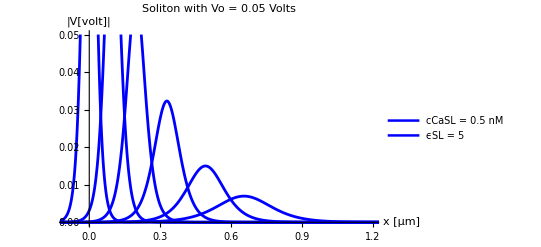

```mathematica
solSP22=Plot[ {Abs[Wx[x*10^-6,0]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxThisFile/10]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/5]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/3]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxThisFile/2]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/1.5]*gamma*nuZe^(1/2)/24]},
{x,-25*beta*10^6,120*beta*10^6},PlotRange->{{-0.1,1.2},{0,0.15}},PlotLegends->{"cCaSL = 0.5 nM", "ϵSL = 5"},PlotLabel->"Soliton with Vo = 0.05 Volts",Axes->True,AxesLabel->{"x [μm]","|V[volt]|"},AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
solSP22Data=Cases[solSP22,Line[{x__}]->x,∞];
```

{{-0.27,4.7662×10^-8},{-0.26952,4.90684×10^-8},{-0.269039,5.05163×10^-8},{-0.268079,5.35416×10^-8},{-0.266158,6.01465×10^-8},{-0.265677,6.19213×10^-8},{-0.265197,6.37485×10^-8},{-0.264237,6.75662×10^-8},{-0.262315,7.59011×10^-8},{-0.261835,7.81408×10^-8},{-0.261355,8.04466×10^-8},{-0.260394,8.52643×10^-8},{-0.258473,9.57826×10^-8},{-0.257993,9.86089×10^-8},{-0.257512,1.01519×10^-7},{-0.256552,1.07598×10^-7},{-0.254631,1.20872×10^-7},{-0.25415,1.24438×10^-7},{-0.25367,1.2811×10^-7},{-0.25271,1.35782×10^-7},{-0.250788,1.52533×10^-7},{-0.250308,1.57034×10^-7},{-0.249828,1.61667×10^-7},{-0.248867,1.71349×10^-7},{-0.246946,1.92487×10^-7},{-0.246466,1.98167×10^-7},{-0.245986,2.04014×10^-7},{-0.245025,2.16232×10^-7},{-0.243104,2.42906×10^-7},{-0.242624,2.50074×10^-7},{-0.242143,2.57453×10^-7},{-0.241183,2.72871×10^-7},{-0.239262,3.06533×10^-7},{-0.238741,3.16351×10^-7},{-0.23822,3.26483×10^-7},{-0.237179,3.47732×10^-7},{-0.236658,3.5887×10^-7},{-0.236137,3.70365×10^-7},{-0.235096,3.9447×10^-7},{-0.234575,4.07104×10^-7},{-0.234055,4.20144×10^-7},{-0.233013,4.47489×10^-7},{-0.230931,5.07634×10^-7},{-0.23041,5.23893×10^-7},{-0.229889,5.40673×10^-7},{-0.228848,5.75862×10^-7},{-0.228327,5.94307×10^-7},{-0.227806,6.13342×10^-7},{-0.226765,6.53262×10^-7},{-0.226244,6.74185×10^-7},{-0.225724,6.95779×10^-7},{-0.224682,7.41064×10^-7},{-0.2226,8.40667×10^-7},{-0.222079,8.67593×10^-7},{-0.221558,8.95381×10^-7},{-0.220517,9.53657×10^-7},{-0.219996,9.84202×10^-7},{-0.219475,1.01573×10^-6},{-0.218434,1.08183×10^-6},{-0.217913,1.11648×10^-6},{-0.217393,1.15224×10^-6},{-0.216351,1.22724×10^-6},{-0.214269,1.39218×10^-6},{-0.213748,1.43678×10^-6},{-0.213227,1.48279×10^-6},{-0.212186,1.5793×10^-6},{-0.211665,1.62989×10^-6},{-0.211144,1.68209×10^-6},{-0.210103,1.79157×10^-6},{-0.209582,1.84895×10^-6},{-0.209062,1.90817×10^-6},{-0.20802,2.03236×10^-6},{-0.205938,2.30552×10^-6},{-0.205451,2.3744×10^-6},{-0.204965,2.44534×10^-6},{-0.203993,2.59363×10^-6},{-0.203507,2.67112×10^-6},{-0.20302,2.75092×10^-6},{-0.202048,2.91774×10^-6},{-0.201562,3.00491×10^-6},{-0.201076,3.09468×10^-6},{-0.200103,3.28235×10^-6},{-0.198159,3.69253×10^-6},{-0.197672,3.80284×10^-6},{-0.197186,3.91645×10^-6},{-0.196214,4.15396×10^-6},{-0.195728,4.27806×10^-6},{-0.195241,4.40586×10^-6},{-0.194269,4.67305×10^-6},{-0.193783,4.81266×10^-6},{-0.193297,4.95643×10^-6},{-0.192324,5.25701×10^-6},{-0.19038,5.91393×10^-6},{-0.189893,6.09061×10^-6},{-0.189407,6.27257×10^-6},{-0.188435,6.65295×10^-6},{-0.187949,6.85171×10^-6},{-0.187463,7.0564×10^-6},{-0.18649,7.48432×10^-6},{-0.186004,7.70791×10^-6},{-0.185518,7.93819×10^-6},{-0.184545,8.41957×10^-6},{-0.182601,9.47169×10^-6},{-0.182115,9.75466×10^-6},{-0.181628,0.0000100461},{-0.180656,0.0000106553},{-0.18017,0.0000109736},{-0.179684,0.0000113014},{-0.178711,0.0000119868},{-0.178225,0.0000123449},{-0.177739,0.0000127137},{-0.176767,0.0000134846},{-0.174822,0.0000151696},{-0.174345,0.0000156138},{-0.173869,0.000016071},{-0.172915,0.0000170258},{-0.171009,0.0000191092},{-0.170532,0.0000196687},{-0.170055,0.0000202445},{-0.169102,0.0000214474},{-0.167196,0.0000240717},{-0.166719,0.0000247765},{-0.166242,0.0000255019},{-0.165289,0.000027017},{-0.163382,0.0000303228},{-0.162906,0.0000312106},{-0.162429,0.0000321244},{-0.161476,0.0000340329},{-0.159569,0.000038197},{-0.159093,0.0000393153},{-0.158616,0.0000404664},{-0.157663,0.0000428705},{-0.155756,0.0000481157},{-0.155279,0.0000495244},{-0.154803,0.0000509742},{-0.153849,0.0000540025},{-0.151943,0.0000606095},{-0.151466,0.0000623838},{-0.15099,0.0000642101},{-0.150036,0.0000680246},{-0.14813,0.0000763466},{-0.147653,0.0000785815},{-0.147176,0.0000808818},{-0.146223,0.0000856864},{-0.144317,0.0000961685},{-0.143799,0.0000992258},{-0.143282,0.00010238},{-0.142248,0.000108993},{-0.141731,0.000112458},{-0.141214,0.000116033},{-0.14018,0.000123528},{-0.139663,0.000127454},{-0.139146,0.000131506},{-0.138112,0.000139999},{-0.136044,0.000158666},{-0.135527,0.000163709},{-0.13501,0.000168912},{-0.133976,0.00017982},{-0.133459,0.000185535},{-0.132942,0.000191432},{-0.131907,0.000203793},{-0.13139,0.000210269},{-0.130873,0.000216951},{-0.129839,0.000230959},{-0.127771,0.000261743},{-0.127254,0.000270059},{-0.126737,0.00027864},{-0.125703,0.000296626},{-0.125186,0.00030605},{-0.124669,0.000315773},{-0.123635,0.000336154},{-0.123118,0.000346832},{-0.122601,0.000357848},{-0.121567,0.000380941},{-0.119498,0.000431688},{-0.118981,0.000445396},{-0.118464,0.000459539},{-0.11743,0.000489183},{-0.116913,0.000504714},{-0.116396,0.000520737},{-0.115362,0.000554323},{-0.114845,0.000571917},{-0.114328,0.00059007},{-0.113294,0.000628117},{-0.111226,0.000711712},{-0.110743,0.000732762},{-0.110261,0.000754433},{-0.109295,0.00079971},{-0.107365,0.000898555},{-0.106883,0.000925114},{-0.1064,0.000952455},{-0.105435,0.00100958},{-0.103505,0.00113426},{-0.103022,0.00116776},{-0.10254,0.00120224},{-0.101575,0.00127428},{-0.0996447,0.0014315},{-0.0991622,0.00147374},{-0.0986796,0.00151721},{-0.0977145,0.00160802},{-0.0957844,0.00180616},{-0.0953018,0.00185938},{-0.0948193,0.00191416},{-0.0938542,0.00202856},{-0.0919241,0.00227813},{-0.0914415,0.00234514},{-0.090959,0.00241411},{-0.0899939,0.00255814},{-0.0880638,0.00287223},{-0.0875812,0.00295654},{-0.0870987,0.00304331},{-0.0861336,0.00322446},{-0.0842034,0.00361936},{-0.0837209,0.00372532},{-0.0832384,0.00383435},{-0.0822733,0.00406194},{-0.0803431,0.00455781},{-0.0798202,0.00470212},{-0.0792972,0.00485092},{-0.0782514,0.00516255},{-0.0777284,0.00532565},{-0.0772055,0.00549382},{-0.0761596,0.00584591},{-0.0756367,0.00603016},{-0.0751137,0.00622008},{-0.0740679,0.00661765},{-0.0719761,0.00748863},{-0.0714532,0.00772326},{-0.0709302,0.00796503},{-0.0698843,0.00847083},{-0.0693614,0.00873529},{-0.0688385,0.00900774},{-0.0677926,0.00957752},{-0.0672696,0.00987532},{-0.0667467,0.010182},{-0.0657008,0.0108232},{-0.0636091,0.0122239},{-0.0630861,0.0126003},{-0.0625632,0.0129877},{-0.0615173,0.0137968},{-0.0594256,0.0155606},{-0.0589026,0.0160337},{-0.0583797,0.0165203},{-0.0573338,0.0175353},{-0.055242,0.019742},{-0.0547191,0.0203325},{-0.0541962,0.0209393},{-0.0531503,0.0222029},{-0.0510585,0.024941},{-0.0505356,0.0256715},{-0.0500127,0.0264212},{-0.0489668,0.0279793},{-0.046875,0.0313408},{-0.0463616,0.0322178},{-0.0458482,0.0331159},{-0.0448214,0.0349765},{-0.0427678,0.0389637},{-0.0422544,0.0400173},{-0.041741,0.0410941},{-0.0407142,0.0433181},{-0.0386606,0.0480518},{-0.0381472,0.0492953},{-0.0378618,0.05},{0.0378611,0.05},{0.0379232,0.0498453},{0.0384425,0.048577},{0.0394811,0.0461144},{0.0415583,0.0414829},{0.0420776,0.0403855},{0.0425969,0.0393118},{0.0436355,0.037235},{0.0457127,0.0333565},{0.046232,0.0324426},{0.0467513,0.0315503},{0.0477899,0.0298295},{0.0498671,0.0266334},{0.0503518,0.0259327},{0.0508366,0.0252487},{0.0518062,0.023929},{0.0537454,0.0214756},{0.0542302,0.0208993},{0.054715,0.0203373},{0.0556845,0.0192547},{0.0576237,0.0172482},{0.0581085,0.016778},{0.0585933,0.0163199},{0.0595629,0.0154386},{0.061502,0.013809},{0.0619868,0.0134278},{0.0624716,0.0130567},{0.0634412,0.0123436},{0.0653804,0.0110274},{0.0658652,0.01072},{0.0663499,0.0104209},{0.0673195,0.00984653},{0.0692587,0.00878816},{0.0697435,0.00854129},{0.0702283,0.00830115},{0.0711979,0.00784038},{0.073137,0.0069923},{0.0736218,0.00679466},{0.0741066,0.00660249},{0.0750762,0.00623394},{0.0770154,0.00555624},{0.0775001,0.00539843},{0.0779849,0.00524503},{0.0789545,0.00495095},{0.0808937,0.00441059},{0.0813689,0.00428728},{0.0818442,0.00416737},{0.0827947,0.00393737},{0.0846957,0.00351432},{0.085171,0.00341577},{0.0856462,0.00331996},{0.0865967,0.00313623},{0.0884977,0.00279843},{0.088973,0.00271978},{0.0894483,0.00264331},{0.0903988,0.00249671},{0.0922998,0.00222727},{0.092775,0.00216455},{0.0932503,0.00210358},{0.0942008,0.00198672},{0.0961018,0.00177199},{0.0965771,0.00172201},{0.0970523,0.00167344},{0.0980028,0.00158034},{0.0999038,0.00140932},{0.100379,0.00136953},{0.100854,0.00133085},{0.101805,0.00125673},{0.103706,0.0011206},{0.104181,0.00108893},{0.104656,0.00105815},{0.105607,0.000999169},{0.107508,0.000890855},{0.107983,0.000865658},{0.108458,0.000841171},{0.109409,0.000794251},{0.11131,0.000708098},{0.111826,0.000686381},{0.112341,0.000665328},{0.113373,0.000625137},{0.113888,0.000605959},{0.114404,0.000587368},{0.115435,0.000551877},{0.115951,0.000534943},{0.116466,0.000518527},{0.117498,0.000487189},{0.11956,0.000430072},{0.120076,0.00041687},{0.120592,0.000404073},{0.121623,0.000379643},{0.122139,0.000367987},{0.122654,0.000356689},{0.123686,0.000335121},{0.124201,0.00032483},{0.124717,0.000314855},{0.125748,0.000295814},{0.127811,0.000261114},{0.128327,0.000253094},{0.128842,0.000245321},{0.129873,0.000230481},{0.130389,0.000223402},{0.130905,0.000216539},{0.131936,0.00020344},{0.132452,0.00019719},{0.132967,0.000191133},{0.133999,0.000179569},{0.136061,0.000158498},{0.136577,0.000153628},{0.137093,0.000148908},{0.138124,0.000139898},{0.13864,0.000135599},{0.139155,0.000131433},{0.140187,0.00012348},{0.140702,0.000119686},{0.141218,0.000116008},{0.142249,0.000108988},{0.144312,0.0000961962},{0.144793,0.000093435},{0.145274,0.000090753},{0.146236,0.0000856178},{0.148161,0.0000762023},{0.148642,0.0000740148},{0.149123,0.0000718902},{0.150086,0.000067822},{0.15201,0.0000603631},{0.152491,0.0000586303},{0.152972,0.0000569472},{0.153935,0.0000537244},{0.155859,0.0000478157},{0.15634,0.000046443},{0.156822,0.0000451097},{0.157784,0.0000425568},{0.159708,0.0000378762},{0.16019,0.0000367888},{0.160671,0.0000357326},{0.161633,0.0000337103},{0.163558,0.0000300026},{0.164039,0.0000291412},{0.16452,0.0000283046},{0.165482,0.0000267026},{0.167407,0.0000237656},{0.167888,0.0000230833},{0.168369,0.0000224205},{0.169331,0.0000211516},{0.171256,0.0000188251},{0.171737,0.0000182846},{0.172218,0.0000177596},{0.173181,0.0000167545},{0.175105,0.0000149116},{0.175627,0.0000144481},{0.176148,0.0000139989},{0.177191,0.0000131422},{0.177713,0.0000127336},{0.178235,0.0000123378},{0.179278,0.0000115827},{0.179799,0.0000112227},{0.180321,0.0000108738},{0.181364,0.0000102083},{0.18345,8.99697×10^-6},{0.183972,8.7173×10^-6},{0.184493,8.44632×10^-6},{0.185536,7.92937×10^-6},{0.186058,7.68289×10^-6},{0.186579,7.44406×10^-6},{0.187622,6.98846×10^-6},{0.188144,6.77122×10^-6},{0.188665,6.56073×10^-6},{0.189709,6.15919×10^-6},{0.191795,5.42832×10^-6},{0.192316,5.25958×10^-6},{0.192838,5.09609×10^-6},{0.193881,4.78418×10^-6},{0.194402,4.63546×10^-6},{0.194924,4.49137×10^-6},{0.195967,4.21648×10^-6},{0.196489,4.08541×10^-6},{0.19701,3.95841×10^-6},{0.198053,3.71614×10^-6},{0.20014,3.27517×10^-6},{0.200661,3.17335×10^-6},{0.201183,3.07471×10^-6},{0.202226,2.88652×10^-6},{0.202747,2.79679×10^-6},{0.203269,2.70985×10^-6},{0.204312,2.544×10^-6},{0.204833,2.46491×10^-6},{0.205355,2.38829×10^-6},{0.206398,2.24212×10^-6},{0.208484,1.97606×10^-6},{0.208996,1.91574×10^-6},{0.209508,1.85726×10^-6},{0.210532,1.7456×10^-6},{0.211044,1.69231×10^-6},{0.211556,1.64065×10^-6},{0.21258,1.54201×10^-6},{0.213092,1.49494×10^-6},{0.213604,1.44931×10^-6},{0.214628,1.36218×10^-6},{0.216676,1.20331×10^-6},{0.217188,1.16658×10^-6},{0.2177,1.13097×10^-6},{0.218724,1.06297×10^-6},{0.219237,1.03052×10^-6},{0.219749,9.99066×10^-7},{0.220773,9.39002×10^-7},{0.221285,9.10337×10^-7},{0.221797,8.82548×10^-7},{0.222821,8.29489×10^-7},{0.224869,7.32749×10^-7},{0.225381,7.10381×10^-7},{0.225893,6.88695×10^-7},{0.226917,6.47291×10^-7},{0.227429,6.27531×10^-7},{0.227941,6.08375×10^-7},{0.228965,5.71799×10^-7},{0.229477,5.54345×10^-7},{0.229989,5.37423×10^-7},{0.231013,5.05112×10^-7},{0.233061,4.46203×10^-7},{0.233573,4.32582×10^-7},{0.234085,4.19377×10^-7},{0.235109,3.94164×10^-7},{0.235621,3.82131×10^-7},{0.236133,3.70466×10^-7},{0.237157,3.48194×10^-7},{0.237669,3.37565×10^-7},{0.238181,3.2726×10^-7},{0.239205,3.07585×10^-7},{0.241253,2.71712×10^-7},{0.24173,2.63969×10^-7},{0.242208,2.56446×10^-7},{0.243163,2.42038×10^-7},{0.245073,2.15604×10^-7},{0.245551,2.0946×10^-7},{0.246028,2.0349×10^-7},{0.246983,1.92057×10^-7},{0.248893,1.71082×10^-7},{0.249371,1.66206×10^-7},{0.249848,1.6147×10^-7},{0.250803,1.52398×10^-7},{0.252713,1.35754×10^-7},{0.253191,1.31885×10^-7},{0.253668,1.28126×10^-7},{0.254623,1.20928×10^-7},{0.256533,1.07721×10^-7},{0.257011,1.04651×10^-7},{0.257488,1.01668×10^-7},{0.258443,9.59561×10^-8},{0.260353,8.54764×10^-8},{0.260831,8.30404×10^-8},{0.261308,8.06739×10^-8},{0.262263,7.61412×10^-8},{0.264173,6.78256×10^-8},{0.264651,6.58927×10^-8},{0.265128,6.40148×10^-8},{0.266083,6.04181×10^-8},{0.267993,5.38197×10^-8},{0.268471,5.22859×10^-8},{0.268948,5.07958×10^-8},{0.269903,4.79418×10^-8},{0.271813,4.27059×10^-8},{0.272331,4.13875×10^-8},{0.272849,4.01098×10^-8},{0.273885,3.76715×10^-8},{0.274403,3.65085×10^-8},{0.274921,3.53814×10^-8},{0.275957,3.32305×10^-8},{0.276474,3.22046×10^-8},{0.276992,3.12104×10^-8},{0.278028,2.9313×10^-8},{0.2801,2.58574×10^-8},{0.280618,2.50591×10^-8},{0.281136,2.42855×10^-8},{0.282171,2.28092×10^-8},{0.282689,2.2105×10^-8},{0.283207,2.14226×10^-8},{0.284243,2.01203×10^-8},{0.284761,1.94991×10^-8},{0.285279,1.88971×10^-8},{0.286315,1.77483×10^-8},{0.288386,1.56561×10^-8},{0.288904,1.51727×10^-8},{0.289422,1.47043×10^-8},{0.290458,1.38104×10^-8},{0.290976,1.3384×10^-8},{0.291494,1.29709×10^-8},{0.292529,1.21823×10^-8},{0.293047,1.18062×10^-8},{0.293565,1.14418×10^-8},{0.294601,1.07462×10^-8},{0.296673,9.47936×10^-9},{0.297191,9.18672×10^-9},{0.297709,8.9031×10^-9},{0.298744,8.36187×10^-9},{0.299262,8.10372×10^-9},{0.29978,7.85354×10^-9},{0.300816,7.37612×10^-9},{0.301334,7.1484×10^-9},{0.301852,6.92771×10^-9},{0.302888,6.50657×10^-9},{0.304959,5.73953×10^-9},{0.305443,5.57397×10^-9},{0.305926,5.41319×10^-9},{0.306893,5.1054×10^-9},{0.308826,4.54134×10^-9},{0.30931,4.41034×10^-9},{0.309793,4.28312×10^-9},{0.31076,4.03959×10^-9},{0.312694,3.59328×10^-9},{0.313177,3.48963×10^-9},{0.31366,3.38897×10^-9},{0.314627,3.19628×10^-9},{0.316561,2.84314×10^-9},{0.317044,2.76113×10^-9},{0.317528,2.68148×10^-9},{0.318494,2.52902×10^-9},{0.320428,2.2496×10^-9},{0.320911,2.18471×10^-9},{0.321395,2.12169×10^-9},{0.322362,2.00106×10^-9},{0.324295,1.77997×10^-9},{0.324779,1.72863×10^-9},{0.325262,1.67876×10^-9},{0.326229,1.58331×10^-9},{0.328162,1.40838×10^-9},{0.328646,1.36776×10^-9},{0.329129,1.3283×10^-9},{0.330096,1.25278×10^-9},{0.33203,1.11437×10^-9},{0.332513,1.08222×10^-9},{0.332996,1.051×10^-9},{0.333963,9.91246×10^-10},{0.335897,8.81729×10^-10},{0.336421,8.54203×10^-10},{0.336944,8.27536×10^-10},{0.337992,7.76675×10^-10},{0.338516,7.52429×10^-10},{0.33904,7.28939×10^-10},{0.340087,6.84138×10^-10},{0.340611,6.6278×10^-10},{0.341135,6.4209×10^-10},{0.342182,6.02626×10^-10},{0.344278,5.30826×10^-10},{0.344801,5.14254×10^-10},{0.345325,4.982×10^-10},{0.346373,4.6758×10^-10},{0.346897,4.52983×10^-10},{0.34742,4.38842×10^-10},{0.348468,4.1187×10^-10},{0.348992,3.99013×10^-10},{0.349516,3.86556×10^-10},{0.350563,3.62798×10^-10},{0.352658,3.19572×10^-10},{0.353182,3.09596×10^-10},{0.353706,2.99931×10^-10},{0.354754,2.81497×10^-10},{0.355277,2.72709×10^-10},{0.355801,2.64196×10^-10},{0.356849,2.47958×10^-10},{0.357373,2.40217×10^-10},{0.357896,2.32718×10^-10},{0.358944,2.18415×10^-10},{0.361039,1.92392×10^-10},{0.361563,1.86386×10^-10},{0.362087,1.80567×10^-10},{0.363134,1.69469×10^-10},{0.363658,1.64179×10^-10},{0.364182,1.59053×10^-10},{0.36523,1.49278×10^-10},{0.365753,1.44617×10^-10},{0.366277,1.40103×10^-10},{0.367325,1.31492×10^-10},{0.36942,1.15825×10^-10},{0.369934,1.12274×10^-10},{0.370448,1.08832×10^-10},{0.371477,1.02261×10^-10},{0.371991,9.9126×10^-11},{0.372505,9.60869×10^-11},{0.373534,9.02855×10^-11},{0.374048,8.75175×10^-11},{0.374563,8.48344×10^-11},{0.375591,7.97123×10^-11},{0.377648,7.03774×10^-11},{0.378162,6.82197×10^-11},{0.378677,6.61282×10^-11},{0.379705,6.21356×10^-11},{0.380219,6.02306×10^-11},{0.380734,5.8384×10^-11},{0.381762,5.4859×10^-11},{0.382276,5.31771×10^-11},{0.382791,5.15468×10^-11},{0.383819,4.84345×10^-11},{0.385876,4.27625×10^-11},{0.386391,4.14514×10^-11},{0.386905,4.01806×10^-11},{0.387933,3.77546×10^-11},{0.388448,3.65971×10^-11},{0.388962,3.54751×10^-11},{0.38999,3.33332×10^-11},{0.390505,3.23113×10^-11},{0.391019,3.13207×10^-11},{0.392047,2.94296×10^-11},{0.394104,2.59832×10^-11},{0.394619,2.51866×10^-11},{0.395133,2.44144×10^-11},{0.396162,2.29403×10^-11},{0.396676,2.2237×10^-11},{0.39719,2.15553×10^-11},{0.398219,2.02538×10^-11},{0.398733,1.96329×10^-11},{0.399247,1.9031×10^-11},{0.400276,1.78819×10^-11},{0.402333,1.57878×10^-11},{0.402812,1.53358×10^-11},{0.403292,1.48967×10^-11},{0.404252,1.40559×10^-11},{0.406171,1.2514×10^-11},{0.40665,1.21557×10^-11},{0.40713,1.18077×10^-11},{0.40809,1.11412×10^-11},{0.410009,9.91903×10^-12},{0.410489,9.63504×10^-12},{0.410968,9.35918×10^-12},{0.411928,8.83092×10^-12},{0.413847,7.86218×10^-12},{0.414327,7.63708×10^-12},{0.414806,7.41842×10^-12},{0.415766,6.99971×10^-12},{0.417685,6.23184×10^-12},{0.418165,6.05342×10^-12},{0.418644,5.8801×10^-12},{0.419604,5.54822×10^-12},{0.421523,4.93958×10^-12},{0.422003,4.79816×10^-12},{0.422482,4.66078×10^-12},{0.423442,4.39772×10^-12},{0.425361,3.91529×10^-12},{0.425841,3.80319×10^-12},{0.426321,3.6943×10^-12},{0.42728,3.48579×10^-12},{0.429199,3.1034×10^-12},{0.429679,3.01455×10^-12},{0.430159,2.92824×10^-12},{0.431118,2.76296×10^-12},{0.433037,2.45987×10^-12},{0.433557,2.3836×10^-12},{0.434077,2.3097×10^-12},{0.435118,2.1687×10^-12},{0.435638,2.10146×10^-12},{0.436158,2.0363×10^-12},{0.437198,1.91199×10^-12},{0.437719,1.85271×10^-12},{0.438239,1.79527×10^-12},{0.439279,1.68567×10^-12},{0.44136,1.48614×10^-12},{0.44188,1.44007×10^-12},{0.4424,1.39542×10^-12},{0.44344,1.31023×10^-12},{0.44396,1.26961×10^-12},{0.444481,1.23025×10^-12},{0.445521,1.15514×10^-12},{0.446041,1.11933×10^-12},{0.446561,1.08463×10^-12},{0.447601,1.01841×10^-12},{0.449682,8.97865×10^-13},{0.450202,8.70027×10^-13},{0.450722,8.43052×10^-13},{0.451763,7.91586×10^-13},{0.452283,7.67044×10^-13},{0.452803,7.43262×10^-13},{0.453843,6.97888×10^-13},{0.454364,6.7625×10^-13},{0.454884,6.55284×10^-13},{0.455924,6.1528×10^-13},{0.458005,5.42451×10^-13},{0.458525,5.25633×10^-13},{0.459045,5.09336×10^-13},{0.460085,4.78242×10^-13},{0.460605,4.63415×10^-13},{0.461126,4.49047×10^-13},{0.462166,4.21634×10^-13},{0.462686,4.08561×10^-13},{0.463206,3.95894×10^-13},{0.464246,3.71726×10^-13},{0.466327,3.27726×10^-13},{0.466813,3.18229×10^-13},{0.467298,3.09007×10^-13},{0.46827,2.91358×10^-13},{0.470212,2.59026×10^-13},{0.470698,2.5152×10^-13},{0.471184,2.44232×10^-13},{0.472155,2.30282×10^-13},{0.474098,2.04728×10^-13},{0.474583,1.98796×10^-13},{0.475069,1.93035×10^-13},{0.47604,1.8201×10^-13},{0.477983,1.61812×10^-13},{0.478468,1.57123×10^-13},{0.478954,1.5257×10^-13},{0.479925,1.43856×10^-13},{0.481868,1.27893×10^-13},{0.482354,1.24187×10^-13},{0.482839,1.20588×10^-13},{0.483811,1.137×10^-13},{0.485753,1.01083×10^-13},{0.486239,9.8154×10^-14},{0.486724,9.53097×10^-14},{0.487696,8.98661×10^-14},{0.489638,7.98937×10^-14},{0.490124,7.75786×10^-14},{0.49061,7.53305×10^-14},{0.491581,7.1028×10^-14},{0.493524,6.31461×10^-14},{0.494009,6.13162×10^-14},{0.494495,5.95394×10^-14},{0.495466,5.61388×10^-14},{0.497409,4.99091×10^-14},{0.497885,4.84909×10^-14},{0.498361,4.71129×10^-14},{0.499313,4.44734×10^-14},{0.501218,3.96296×10^-14},{0.501694,3.85035×10^-14},{0.50217,3.74093×10^-14},{0.503122,3.53134×10^-14},{0.505027,3.14673×10^-14},{0.505503,3.05731×10^-14},{0.505979,2.97043×10^-14},{0.506931,2.80401×10^-14},{0.508836,2.49862×10^-14},{0.509312,2.42762×10^-14},{0.509788,2.35863×10^-14},{0.51074,2.22649×10^-14},{0.512644,1.98399×10^-14},{0.513121,1.92761×10^-14},{0.513597,1.87284×10^-14},{0.514549,1.76791×10^-14},{0.516453,1.57536×10^-14},{0.517406,1.4871×10^-14},{0.518358,1.40378×10^-14},{0.520262,1.25089×10^-14},{0.521214,1.18081×10^-14},{0.522167,1.11465×10^-14},{0.524071,9.93253×10^-15},{0.525023,9.37605×10^-15},{0.525976,8.85075×10^-15},{0.52788,7.88679×10^-15},{0.528913,7.40859×10^-15},{0.529946,6.95938×10^-15},{0.530979,6.53741×10^-15},{0.532012,6.14103×10^-15},{0.533045,5.76868×10^-15},{0.534078,5.41891×10^-15},{0.536144,4.7817×10^-15},{0.537177,4.49177×10^-15},{0.53821,4.21942×10^-15},{0.539243,3.96359×10^-15},{0.540276,3.72326×10^-15},{0.542342,3.28545×10^-15},{0.544408,2.89911×10^-15},{0.546475,2.55821×10^-15},{0.548541,2.25739×10^-15},{0.550607,1.99194×10^-15},{0.552673,1.75771×10^-15},{0.554739,1.55102×10^-15},{0.556805,1.36864×10^-15},{0.558871,1.2077×10^-15},{0.560937,1.06569×10^-15},{0.564793,8.43781×10^-16},{0.568649,6.68082×10^-16},{0.572505,5.28969×10^-16},{0.576361,4.18822×10^-16},{0.576843,4.06776×10^-16},{0.577325,3.95075×10^-16},{0.578289,3.72675×10^-16},{0.580217,3.31612×10^-16},{0.584073,2.62561×10^-16},{0.584555,2.55009×10^-16},{0.585037,2.47674×10^-16},{0.586001,2.33631×10^-16},{0.587929,2.07888×10^-16},{0.591785,1.646×10^-16},{0.592308,1.59475×10^-16},{0.59283,1.5451×10^-16},{0.593875,1.45038×10^-16},{0.595965,1.278×10^-16},{0.600144,9.92276×10^-17},{0.608502,5.98184×10^-17},{0.62522,2.1739×10^-17},{0.658043,2.97921×10^-18},{0.688659,4.66693×10^-19},{0.72186,6.25133×10^-20},{0.752852,9.57158×10^-21},{0.783234,1.52071×10^-21},{0.816202,2.06594×10^-22},{0.846962,3.20818×10^-23},{0.880307,4.26001×10^-24},{0.911443,6.46596×10^-25},{0.94197,1.01837×10^-25},{0.975082,1.37148×10^-26},{1.00599,2.11126×10^-27},{1.03947,2.7791×10^-28},{1.07235,3.79592×10^-29},{1.10302,5.92654×10^-30},{1.13628,7.91215×10^-31},{1.16733,1.20742×10^-31},{1.19776,1.91194×10^-32},{1.23079,2.58879×10^-33},{1.2616,4.00675×10^-34},{1.26214,3.87846×10^-34},{1.26268,3.75427×10^-34},{1.26375,3.5177×10^-34},{1.2659,3.08833×10^-34},{1.2702,2.38044×10^-34},{1.2788,1.41423×10^-34},{1.27934,1.36895×10^-34},{1.27988,1.32511×10^-34},{1.28095,1.24161×10^-34},{1.2831,1.09007×10^-34},{1.2874,8.40203×10^-35},{1.28794,8.133×10^-35},{1.28848,7.87259×10^-35},{1.28955,7.3765×10^-35},{1.2917,6.47614×10^-35},{1.29224,6.26878×10^-35},{1.29278,6.06805×10^-35},{1.29385,5.68568×10^-35},{1.29439,5.50363×10^-35},{1.29493,5.3274×10^-35},{1.29546,5.15682×10^-35},{1.296,4.9917×10^-35},{-0.27,7.39194×10^-9},{-0.26952,7.56465×10^-9},{-0.269039,7.74139×10^-9},{-0.268079,8.10735×10^-9},{-0.266158,8.892×10^-9},{-0.265677,9.09975×10^-9},{-0.265197,9.31236×10^-9},{-0.264237,9.75259×10^-9},{-0.262315,1.06965×10^-8},{-0.261835,1.09464×10^-8},{-0.261355,1.12021×10^-8},{-0.260394,1.17317×10^-8},{-0.258473,1.28671×10^-8},{-0.257993,1.31677×10^-8},{-0.257512,1.34754×10^-8},{-0.256552,1.41124×10^-8},{-0.254631,1.54782×10^-8},{-0.25415,1.58399×10^-8},{-0.25367,1.621×10^-8},{-0.25271,1.69763×10^-8},{-0.250788,1.86193×10^-8},{-0.250308,1.90543×10^-8},{-0.249828,1.94995×10^-8},{-0.248867,2.04213×10^-8},{-0.246946,2.23977×10^-8},{-0.246466,2.2921×10^-8},{-0.245986,2.34565×10^-8},{-0.245025,2.45654×10^-8},{-0.243104,2.69429×10^-8},{-0.242624,2.75724×10^-8},{-0.242143,2.82166×10^-8},{-0.241183,2.95505×10^-8},{-0.239262,3.24104×10^-8},{-0.238741,3.32322×10^-8},{-0.23822,3.40747×10^-8},{-0.237179,3.58245×10^-8},{-0.235096,3.95981×10^-8},{-0.234575,4.06021×10^-8},{-0.234055,4.16315×10^-8},{-0.233013,4.37693×10^-8},{-0.230931,4.83799×10^-8},{-0.23041,4.96065×10^-8},{-0.229889,5.08642×10^-8},{-0.228848,5.34761×10^-8},{-0.226765,5.91092×10^-8},{-0.226244,6.06079×10^-8},{-0.225724,6.21445×10^-8},{-0.224682,6.53357×10^-8},{-0.2226,7.2218×10^-8},{-0.222079,7.4049×10^-8},{-0.221558,7.59264×10^-8},{-0.220517,7.98253×10^-8},{-0.218434,8.82339×10^-8},{-0.217913,9.0471×10^-8},{-0.217393,9.27648×10^-8},{-0.216351,9.75283×10^-8},{-0.214269,1.07802×10^-7},{-0.213748,1.10535×10^-7},{-0.213227,1.13337×10^-7},{-0.212186,1.19157×10^-7},{-0.210103,1.31709×10^-7},{-0.209582,1.35048×10^-7},{-0.209062,1.38472×10^-7},{-0.20802,1.45583×10^-7},{-0.205938,1.60918×10^-7},{-0.205451,1.64725×10^-7},{-0.204965,1.68621×10^-7},{-0.203993,1.76693×10^-7},{-0.202048,1.94013×10^-7},{-0.201562,1.98602×10^-7},{-0.201076,2.033×10^-7},{-0.200103,2.13032×10^-7},{-0.198159,2.33914×10^-7},{-0.197672,2.39447×10^-7},{-0.197186,2.45111×10^-7},{-0.196214,2.56844×10^-7},{-0.194269,2.82021×10^-7},{-0.193783,2.88692×10^-7},{-0.193297,2.95521×10^-7},{-0.192324,3.09667×10^-7},{-0.19038,3.40022×10^-7},{-0.189893,3.48065×10^-7},{-0.189407,3.56298×10^-7},{-0.188435,3.73353×10^-7},{-0.18649,4.09952×10^-7},{-0.186004,4.19649×10^-7},{-0.185518,4.29575×10^-7},{-0.184545,4.50138×10^-7},{-0.182601,4.94263×10^-7},{-0.182115,5.05954×10^-7},{-0.181628,5.17922×10^-7},{-0.180656,5.42714×10^-7},{-0.178711,5.95914×10^-7},{-0.178225,6.10009×10^-7},{-0.177739,6.24438×10^-7},{-0.176767,6.54329×10^-7},{-0.174822,7.1847×10^-7},{-0.174345,7.35127×10^-7},{-0.173869,7.52171×10^-7},{-0.172915,7.87453×10^-7},{-0.171009,8.63059×10^-7},{-0.170532,8.83068×10^-7},{-0.170055,9.03542×10^-7},{-0.169102,9.45924×10^-7},{-0.167196,1.03675×10^-6},{-0.166719,1.06078×10^-6},{-0.166242,1.08538×10^-6},{-0.165289,1.13629×10^-6},{-0.163382,1.24539×10^-6},{-0.162906,1.27426×10^-6},{-0.162429,1.3038×10^-6},{-0.161476,1.36496×10^-6},{-0.159569,1.49601×10^-6},{-0.159093,1.5307×10^-6},{-0.158616,1.56619×10^-6},{-0.157663,1.63965×10^-6},{-0.155756,1.79708×10^-6},{-0.155279,1.83874×10^-6},{-0.154803,1.88137×10^-6},{-0.153849,1.96962×10^-6},{-0.151943,2.15873×10^-6},{-0.151466,2.20878×10^-6},{-0.15099,2.25999×10^-6},{-0.150036,2.366×10^-6},{-0.14813,2.59316×10^-6},{-0.147653,2.65328×10^-6},{-0.147176,2.7148×10^-6},{-0.146223,2.84214×10^-6},{-0.144317,3.11502×10^-6},{-0.143799,3.19343×10^-6},{-0.143282,3.27382×10^-6},{-0.142248,3.44073×10^-6},{-0.14018,3.8005×10^-6},{-0.139663,3.89617×10^-6},{-0.139146,3.99425×10^-6},{-0.138112,4.19788×10^-6},{-0.136044,4.63682×10^-6},{-0.135527,4.75354×10^-6},{-0.13501,4.87321×10^-6},{-0.133976,5.12165×10^-6},{-0.131907,5.65717×10^-6},{-0.13139,5.79958×10^-6},{-0.130873,5.94558×10^-6},{-0.129839,6.24869×10^-6},{-0.127771,6.90205×10^-6},{-0.127254,7.0758×10^-6},{-0.126737,7.25392×10^-6},{-0.125703,7.62373×10^-6},{-0.123635,8.42086×10^-6},{-0.123118,8.63283×10^-6},{-0.122601,8.85015×10^-6},{-0.121567,9.30133×10^-6},{-0.119498,0.0000102739},{-0.118981,0.0000105325},{-0.118464,0.0000107976},{-0.11743,0.0000113481},{-0.115362,0.0000125346},{-0.114845,0.0000128501},{-0.114328,0.0000131736},{-0.113294,0.0000138452},{-0.111226,0.0000152927},{-0.110743,0.0000156517},{-0.110261,0.0000160191},{-0.109295,0.0000167799},{-0.107365,0.0000184117},{-0.106883,0.0000188439},{-0.1064,0.0000192862},{-0.105435,0.0000202022},{-0.103505,0.0000221668},{-0.103022,0.0000226871},{-0.10254,0.0000232196},{-0.101575,0.0000243224},{-0.0996447,0.0000266876},{-0.0991622,0.000027314},{-0.0986796,0.0000279551},{-0.0977145,0.0000292828},{-0.0957844,0.0000321303},{-0.0953018,0.0000328844},{-0.0948193,0.0000336562},{-0.0938542,0.0000352546},{-0.0919241,0.0000386826},{-0.0914415,0.0000395905},{-0.090959,0.0000405197},{-0.0899939,0.000042444},{-0.0880638,0.0000465709},{-0.0875812,0.0000476639},{-0.0870987,0.0000487825},{-0.0861336,0.0000510991},{-0.0842034,0.0000560673},{-0.0837209,0.0000573831},{-0.0832384,0.0000587297},{-0.0822733,0.0000615185},{-0.0803431,0.0000674995},{-0.0798202,0.0000692177},{-0.0792972,0.0000709797},{-0.0782514,0.0000746393},{-0.0761596,0.0000825339},{-0.0756367,0.0000846347},{-0.0751137,0.0000867889},{-0.0740679,0.0000912631},{-0.0719761,0.000100915},{-0.0714532,0.000103484},{-0.0709302,0.000106117},{-0.0698843,0.000111587},{-0.0677926,0.000123387},{-0.0672696,0.000126527},{-0.0667467,0.000129747},{-0.0657008,0.000136435},{-0.0636091,0.00015086},{-0.0630861,0.000154699},{-0.0625632,0.000158635},{-0.0615173,0.00016681},{-0.0594256,0.000184444},{-0.0589026,0.000189136},{-0.0583797,0.000193947},{-0.0573338,0.00020394},{-0.055242,0.000225494},{-0.0547191,0.000231229},{-0.0541962,0.00023711},{-0.0531503,0.000249324},{-0.0510585,0.000275668},{-0.0505356,0.000282677},{-0.0500127,0.000289865},{-0.0489668,0.000304791},{-0.046875,0.000336986},{-0.0463616,0.000345393},{-0.0458482,0.00035401},{-0.0448214,0.000371893},{-0.0427678,0.000410408},{-0.0422544,0.000420643},{-0.041741,0.000431133},{-0.0407142,0.000452902},{-0.0386606,0.000499784},{-0.0381472,0.000512242},{-0.0376338,0.00052501},{-0.036607,0.000551506},{-0.0345534,0.000608562},{-0.03404,0.000623723},{-0.0335266,0.00063926},{-0.0324998,0.0006715},{-0.0304462,0.000740922},{-0.0299328,0.000759366},{-0.0294194,0.000778268},{-0.0283926,0.000817489},{-0.0263389,0.000901931},{-0.0258255,0.000924364},{-0.0253121,0.000947352},{-0.0242853,0.000995049},{-0.0222317,0.00109772},{-0.0217183,0.001125},{-0.0212049,0.00115295},{-0.0201781,0.00121093},{-0.0181245,0.00133572},{-0.0176111,0.00136886},{-0.0170977,0.00140282},{-0.0160709,0.00147327},{-0.0140173,0.00162486},{-0.0135384,0.00166238},{-0.0130595,0.00170075},{-0.0121017,0.00178016},{-0.0101861,0.00195015},{-0.00970723,0.00199509},{-0.00922833,0.00204107},{-0.00827054,0.00213618},{-0.00635495,0.00233973},{-0.00587605,0.00239354},{-0.00539716,0.00244857},{-0.00443936,0.00256241},{-0.00252378,0.00280596},{-0.00204488,0.00287033},{-0.00156598,0.00293615},{-0.000608188,0.00307227},{0.0013074,0.0033634},{0.0017863,0.00344031},{0.00226519,0.00351895},{0.00322299,0.00368155},{0.00513857,0.00402914},{0.00561747,0.00412093},{0.00609637,0.00421477},{0.00705416,0.00440874},{0.00896975,0.00482316},{0.00944865,0.00493255},{0.00992754,0.00504435},{0.0108853,0.00527538},{0.0128009,0.00576864},{0.0132798,0.00589877},{0.0137587,0.00603173},{0.0147165,0.0063064},{0.0166321,0.00689232},{0.0171514,0.00705997},{0.0176707,0.00723153},{0.0187093,0.0075867},{0.0207865,0.00834769},{0.0213058,0.00854901},{0.0218251,0.00875493},{0.0228637,0.00918097},{0.0249408,0.0100925},{0.0254601,0.0103334},{0.0259794,0.0105796},{0.027018,0.0110887},{0.0290952,0.0121761},{0.0332496,0.014652},{0.0337689,0.0149918},{0.0342882,0.0153388},{0.0353268,0.0160547},{0.0374039,0.0175768},{0.0379232,0.0179768},{0.0384425,0.0183848},{0.0394811,0.0192253},{0.0415583,0.0210072},{0.0420776,0.0214742},{0.0425969,0.0219501},{0.0436355,0.0229288},{0.0457127,0.0249959},{0.0498671,0.0295852},{0.0503518,0.0301613},{0.0508366,0.0307458},{0.0518062,0.0319407},{0.0537454,0.0344331},{0.0576237,0.0398222},{0.0581085,0.0405326},{0.0585933,0.0412508},{0.0595629,0.0427105},{0.061502,0.0457184},{0.0641254,0.05},{0.134187,0.05},{0.136061,0.0469015},{0.136577,0.0460794},{0.137093,0.045265},{0.138124,0.0436599},{0.140187,0.0405501},{0.144312,0.0347641},{0.144793,0.0341286},{0.145274,0.0335015},{0.146236,0.0322725},{0.148161,0.0299156},{0.148642,0.0293475},{0.149123,0.0287878},{0.150086,0.0276934},{0.15201,0.0256041},{0.152491,0.0251023},{0.152972,0.0246085},{0.153935,0.023645},{0.155859,0.0218124},{0.159708,0.0185089},{0.16019,0.0181283},{0.160671,0.0177546},{0.161633,0.0170277},{0.163558,0.015653},{0.164039,0.0153253},{0.16452,0.0150038},{0.165482,0.0143791},{0.167407,0.0132002},{0.167888,0.0129197},{0.168369,0.0126447},{0.169331,0.0121108},{0.171256,0.0111052},{0.175105,0.00932383},{0.175627,0.0091043},{0.176148,0.00888967},{0.177191,0.00847472},{0.179278,0.00769947},{0.179799,0.00751651},{0.180321,0.00733772},{0.181364,0.00699227},{0.18345,0.00634767},{0.183972,0.00619569},{0.184493,0.00604723},{0.185536,0.00576054},{0.187622,0.00522612},{0.188144,0.00510022},{0.188665,0.00497727},{0.189709,0.00473995},{0.191795,0.00429793},{0.192316,0.00419387},{0.192838,0.00409227},{0.193881,0.00389624},{0.195967,0.00353136},{0.196489,0.00344551},{0.19701,0.0033617},{0.198053,0.00320005},{0.20014,0.00289932},{0.200661,0.0028286},{0.201183,0.00275957},{0.202226,0.00262646},{0.204312,0.00237894},{0.204833,0.00232075},{0.205355,0.00226396},{0.206398,0.00215447},{0.208484,0.00195096},{0.208996,0.00190399},{0.209508,0.00185815},{0.210532,0.0017697},{0.21258,0.00160514},{0.213092,0.00156643},{0.213604,0.00152864},{0.214628,0.00145576},{0.216676,0.00132018},{0.217188,0.0012883},{0.2177,0.00125717},{0.218724,0.00119715},{0.220773,0.00108552},{0.221285,0.00105927},{0.221797,0.00103365},{0.222821,0.000984242},{0.224869,0.000892368},{0.225381,0.000870766},{0.225893,0.000849685},{0.226917,0.000809033},{0.228965,0.00073345},{0.229477,0.000715681},{0.229989,0.00069834},{0.231013,0.000664904},{0.233061,0.000602743},{0.233573,0.00058813},{0.234085,0.00057387},{0.235109,0.000546376},{0.237157,0.000495267},{0.237669,0.000483253},{0.238181,0.000471529},{0.239205,0.000448927},{0.241253,0.000406913},{0.24173,0.000397696},{0.242208,0.000388687},{0.243163,0.000371275},{0.245073,0.000338753},{0.245551,0.000331077},{0.246028,0.000323574},{0.246983,0.000309075},{0.248893,0.000281993},{0.249371,0.000275601},{0.249848,0.000269354},{0.250803,0.00025728},{0.252713,0.000234731},{0.253191,0.000229409},{0.253668,0.000224208},{0.254623,0.000214156},{0.256533,0.000195382},{0.257011,0.000190952},{0.257488,0.000186621},{0.258443,0.000178253},{0.260353,0.000162624},{0.260831,0.000158936},{0.261308,0.000155331},{0.262263,0.000148364},{0.264173,0.000135354},{0.264651,0.000132284},{0.265128,0.000129283},{0.266083,0.000123484},{0.267993,0.000112654},{0.268471,0.000110099},{0.268948,0.000107601},{0.269903,0.000102774},{0.271813,0.0000937596},{0.272331,0.0000914545},{0.272849,0.0000892061},{0.273885,0.0000848737},{0.275957,0.0000768297},{0.276474,0.0000749407},{0.276992,0.0000730982},{0.278028,0.0000695478},{0.2801,0.0000629558},{0.280618,0.0000614078},{0.281136,0.0000598979},{0.282171,0.0000569885},{0.284243,0.0000515866},{0.284761,0.0000503181},{0.285279,0.0000490807},{0.286315,0.0000466966},{0.288386,0.0000422701},{0.288904,0.0000412306},{0.289422,0.0000402167},{0.290458,0.000038263},{0.292529,0.0000346358},{0.293047,0.000033784},{0.293565,0.0000329532},{0.294601,0.0000313523},{0.296673,0.0000283801},{0.297191,0.0000276822},{0.297709,0.0000270014},{0.298744,0.0000256896},{0.300816,0.0000232542},{0.301334,0.0000226823},{0.301852,0.0000221244},{0.302888,0.0000210496},{0.304959,0.000019054},{0.305443,0.0000186162},{0.305926,0.0000181885},{0.306893,0.0000173624},{0.308826,0.0000158209},{0.30931,0.0000154574},{0.309793,0.0000151023},{0.31076,0.0000144163},{0.312694,0.0000131364},{0.313177,0.0000128346},{0.31366,0.0000125397},{0.314627,0.0000119702},{0.316561,0.0000109074},{0.317044,0.0000106568},{0.317528,0.000010412},{0.318494,9.93903×10^-6},{0.320428,9.05661×10^-6},{0.320911,8.84853×10^-6},{0.321395,8.64523×10^-6},{0.322362,8.25253×10^-6},{0.324295,7.51984×10^-6},{0.324779,7.34707×10^-6},{0.325262,7.17826×10^-6},{0.326229,6.8522×10^-6},{0.328162,6.24383×10^-6},{0.328646,6.10037×10^-6},{0.329129,5.96021×10^-6},{0.330096,5.68947×10^-6},{0.33203,5.18433×10^-6},{0.332513,5.06522×10^-6},{0.332996,4.94884×10^-6},{0.333963,4.72404×10^-6},{0.335897,4.30462×10^-6},{0.336421,4.19755×10^-6},{0.336944,4.09315×10^-6},{0.337992,3.89207×10^-6},{0.340087,3.51906×10^-6},{0.340611,3.43153×10^-6},{0.341135,3.34618×10^-6},{0.342182,3.18179×10^-6},{0.344278,2.87685×10^-6},{0.344801,2.8053×10^-6},{0.345325,2.73552×10^-6},{0.346373,2.60114×10^-6},{0.348468,2.35185×10^-6},{0.348992,2.29335×10^-6},{0.349516,2.23631×10^-6},{0.350563,2.12645×10^-6},{0.352658,1.92265×10^-6},{0.353182,1.87483×10^-6},{0.353706,1.8282×10^-6},{0.354754,1.73838×10^-6},{0.356849,1.57178×10^-6},{0.357373,1.53268×10^-6},{0.357896,1.49456×10^-6},{0.358944,1.42114×10^-6},{0.361039,1.28494×10^-6},{0.361563,1.25298×10^-6},{0.362087,1.22181×10^-6},{0.363134,1.16179×10^-6},{0.36523,1.05044×10^-6},{0.365753,1.02431×10^-6},{0.366277,9.98837×10^-7},{0.367325,9.49767×10^-7},{0.36942,8.58741×10^-7},{0.369934,8.37766×10^-7},{0.370448,8.17303×10^-7},{0.371477,7.77865×10^-7},{0.373534,7.04606×10^-7},{0.374048,6.87395×10^-7},{0.374563,6.70605×10^-7},{0.375591,6.38246×10^-7},{0.377648,5.78136×10^-7},{0.378162,5.64014×10^-7},{0.378677,5.50238×10^-7},{0.379705,5.23687×10^-7},{0.381762,4.74366×10^-7},{0.382276,4.62779×10^-7},{0.382791,4.51475×10^-7},{0.383819,4.2969×10^-7},{0.385876,3.89221×10^-7},{0.386391,3.79715×10^-7},{0.386905,3.7044×10^-7},{0.387933,3.52564×10^-7},{0.38999,3.1936×10^-7},{0.390505,3.11559×10^-7},{0.391019,3.03949×10^-7},{0.392047,2.89282×10^-7},{0.394104,2.62038×10^-7},{0.394619,2.55637×10^-7},{0.395133,2.49393×10^-7},{0.396162,2.37359×10^-7},{0.398219,2.15004×10^-7},{0.398733,2.09753×10^-7},{0.399247,2.04629×10^-7},{0.400276,1.94755×10^-7},{0.402333,1.76413×10^-7},{0.402812,1.7239×10^-7},{0.403292,1.68458×10^-7},{0.404252,1.60862×10^-7},{0.406171,1.46683×10^-7},{0.40665,1.43337×10^-7},{0.40713,1.40069×10^-7},{0.40809,1.33753×10^-7},{0.410009,1.21963×10^-7},{0.410489,1.19181×10^-7},{0.410968,1.16463×10^-7},{0.411928,1.11212×10^-7},{0.413847,1.01409×10^-7},{0.414327,9.90959×10^-8},{0.414806,9.6836×10^-8},{0.415766,9.24696×10^-8},{0.417685,8.43185×10^-8},{0.418165,8.23956×10^-8},{0.418644,8.05165×10^-8},{0.419604,7.68859×10^-8},{0.421523,7.01085×10^-8},{0.422003,6.85097×10^-8},{0.422482,6.69473×10^-8},{0.423442,6.39286×10^-8},{0.425361,5.82934×10^-8},{0.425841,5.69639×10^-8},{0.426321,5.56649×10^-8},{0.42728,5.31549×10^-8},{0.429199,4.84693×10^-8},{0.429679,4.7364×10^-8},{0.430159,4.62838×10^-8},{0.431118,4.41968×10^-8},{0.433037,4.03009×10^-8},{0.433557,3.93054×10^-8},{0.434077,3.83345×10^-8},{0.435118,3.6464×10^-8},{0.437198,3.29924×10^-8},{0.437719,3.21774×10^-8},{0.438239,3.13826×10^-8},{0.439279,2.98513×10^-8},{0.44136,2.70092×10^-8},{0.44188,2.63421×10^-8},{0.4424,2.56914×10^-8},{0.44344,2.44378×10^-8},{0.445521,2.21111×10^-8},{0.446041,2.15649×10^-8},{0.446561,2.10322×10^-8},{0.447601,2.0006×10^-8},{0.449682,1.81013×10^-8},{0.450202,1.76542×10^-8},{0.450722,1.72181×10^-8},{0.451763,1.63779×10^-8},{0.453843,1.48186×10^-8},{0.454364,1.44526×10^-8},{0.454884,1.40956×10^-8},{0.455924,1.34078×10^-8},{0.458005,1.21313×10^-8},{0.458525,1.18316×10^-8},{0.459045,1.15394×10^-8},{0.460085,1.09763×10^-8},{0.462166,9.93129×10^-9},{0.462686,9.68596×10^-9},{0.463206,9.4467×10^-9},{0.464246,8.98576×10^-9},{0.466327,8.13025×10^-9},{0.466813,7.94259×10^-9},{0.467298,7.75925×10^-9},{0.46827,7.40518×10^-9},{0.470212,6.74477×10^-9},{0.470698,6.58909×10^-9},{0.471184,6.437×10^-9},{0.472155,6.14326×10^-9},{0.474098,5.59539×10^-9},{0.474583,5.46624×10^-9},{0.475069,5.34006×10^-9},{0.47604,5.09639×10^-9},{0.477983,4.64188×10^-9},{0.478468,4.53473×10^-9},{0.478954,4.43006×10^-9},{0.479925,4.22791×10^-9},{0.481868,3.85086×10^-9},{0.482354,3.76197×10^-9},{0.482839,3.67513×10^-9},{0.483811,3.50743×10^-9},{0.485753,3.19463×10^-9},{0.486239,3.12089×10^-9},{0.486724,3.04885×10^-9},{0.487696,2.90973×10^-9},{0.489638,2.65023×10^-9},{0.490124,2.58906×10^-9},{0.49061,2.5293×10^-9},{0.491581,2.41388×10^-9},{0.493524,2.1986×10^-9},{0.494009,2.14786×10^-9},{0.494495,2.09828×10^-9},{0.495466,2.00253×10^-9},{0.497409,1.82394×10^-9},{0.497885,1.78266×10^-9},{0.498361,1.74231×10^-9},{0.499313,1.66433×10^-9},{0.501218,1.51868×10^-9},{0.501694,1.48431×10^-9},{0.50217,1.45071×10^-9},{0.503122,1.38578×10^-9},{0.505027,1.26451×10^-9},{0.505503,1.23589×10^-9},{0.505979,1.20792×10^-9},{0.506931,1.15386×10^-9},{0.508836,1.05288×10^-9},{0.509312,1.02905×10^-9},{0.509788,1.00576×10^-9},{0.51074,9.60746×10^-10},{0.512644,8.76672×10^-10},{0.513121,8.56829×10^-10},{0.513597,8.37435×10^-10},{0.514549,7.99954×10^-10},{0.516453,7.29951×10^-10},{0.516929,7.13429×10^-10},{0.517406,6.97281×10^-10},{0.518358,6.66073×10^-10},{0.520262,6.07785×10^-10},{0.520738,5.94028×10^-10},{0.521214,5.80583×10^-10},{0.522167,5.54598×10^-10},{0.524071,5.06066×10^-10},{0.524547,4.94611×10^-10},{0.525023,4.83416×10^-10},{0.525976,4.6178×10^-10},{0.52788,4.2137×10^-10},{0.528397,4.11033×10^-10},{0.528913,4.0095×10^-10},{0.529946,3.8152×10^-10},{0.532012,3.45438×10^-10},{0.532529,3.36964×10^-10},{0.533045,3.28698×10^-10},{0.534078,3.12769×10^-10},{0.536144,2.8319×10^-10},{0.536661,2.76243×10^-10},{0.537177,2.69466×10^-10},{0.53821,2.56408×10^-10},{0.540276,2.32159×10^-10},{0.540793,2.26464×10^-10},{0.541309,2.20908×10^-10},{0.542342,2.10203×10^-10},{0.544408,1.90323×10^-10},{0.544925,1.85655×10^-10},{0.545442,1.811×10^-10},{0.546475,1.72324×10^-10},{0.548541,1.56027×10^-10},{0.549057,1.52199×10^-10},{0.549574,1.48466×10^-10},{0.550607,1.41271×10^-10},{0.552673,1.27911×10^-10},{0.553189,1.24773×10^-10},{0.553706,1.21712×10^-10},{0.554739,1.15814×10^-10},{0.556805,1.04861×10^-10},{0.557321,1.02289×10^-10},{0.557838,9.97793×10^-11},{0.558871,9.4944×10^-11},{0.560937,8.59649×10^-11},{0.561419,8.39953×10^-11},{0.561901,8.20709×10^-11},{0.562865,7.83532×10^-11},{0.564793,7.14156×10^-11},{0.565275,6.97794×10^-11},{0.565757,6.81806×10^-11},{0.566721,6.50922×10^-11},{0.568649,5.93287×10^-11},{0.569131,5.79694×10^-11},{0.569613,5.66412×10^-11},{0.570577,5.40755×10^-11},{0.572505,4.92875×10^-11},{0.572987,4.81583×10^-11},{0.573469,4.70549×10^-11},{0.574433,4.49234×10^-11},{0.576361,4.09457×10^-11},{0.576843,4.00076×10^-11},{0.577325,3.9091×10^-11},{0.578289,3.73203×10^-11},{0.580217,3.40158×10^-11},{0.580699,3.32364×10^-11},{0.581181,3.2475×10^-11},{0.582145,3.10039×10^-11},{0.584073,2.82587×10^-11},{0.584555,2.76113×10^-11},{0.585037,2.69787×10^-11},{0.586001,2.57566×10^-11},{0.587929,2.3476×10^-11},{0.588411,2.29381×10^-11},{0.588893,2.24126×10^-11},{0.589857,2.13974×10^-11},{0.591785,1.95028×10^-11},{0.592308,1.90189×10^-11},{0.59283,1.85471×10^-11},{0.593875,1.76383×10^-11},{0.595965,1.59521×10^-11},{0.596487,1.55564×10^-11},{0.59701,1.51705×10^-11},{0.598054,1.44271×10^-11},{0.600144,1.30479×10^-11},{0.600666,1.27242×10^-11},{0.601189,1.24086×10^-11},{0.602234,1.18006×10^-11},{0.604323,1.06724×10^-11},{0.604846,1.04077×10^-11},{0.605368,1.01495×10^-11},{0.606413,9.65217×10^-12},{0.608502,8.72943×10^-12},{0.609025,8.51288×10^-12},{0.609547,8.30169×10^-12},{0.610592,7.89491×10^-12},{0.612682,7.14017×10^-12},{0.613204,6.96304×10^-12},{0.613727,6.7903×10^-12},{0.614771,6.45758×10^-12},{0.616861,5.84024×10^-12},{0.617383,5.69536×10^-12},{0.617906,5.55407×10^-12},{0.618951,5.28193×10^-12},{0.62104,4.77698×10^-12},{0.621563,4.65848×10^-12},{0.622085,4.54291×10^-12},{0.62313,4.32031×10^-12},{0.62522,3.90729×10^-12},{0.625732,3.81211×10^-12},{0.626245,3.71925×10^-12},{0.627271,3.54025×10^-12},{0.629322,3.20769×10^-12},{0.629835,3.12955×10^-12},{0.630348,3.05331×10^-12},{0.631374,2.90636×10^-12},{0.633425,2.63334×10^-12},{0.633938,2.5692×10^-12},{0.634451,2.50661×10^-12},{0.635477,2.38597×10^-12},{0.637528,2.16184×10^-12},{0.638041,2.10918×10^-12},{0.638554,2.0578×10^-12},{0.63958,1.95876×10^-12},{0.641631,1.77476×10^-12},{0.642144,1.73152×10^-12},{0.642657,1.68934×10^-12},{0.643683,1.60804×10^-12},{0.645734,1.45698×10^-12},{0.646247,1.42149×10^-12},{0.64676,1.38686×10^-12},{0.647786,1.32012×10^-12},{0.649837,1.19611×10^-12},{0.65035,1.16697×10^-12},{0.650863,1.13854×10^-12},{0.651889,1.08375×10^-12},{0.65394,9.81944×10^-13},{0.654453,9.58023×10^-13},{0.654966,9.34686×10^-13},{0.655992,8.89702×10^-13},{0.658043,8.06125×10^-13},{0.658522,7.87794×10^-13},{0.659,7.69879×10^-13},{0.659957,7.35263×10^-13},{0.66187,6.7063×10^-13},{0.662349,6.5538×10^-13},{0.662827,6.40476×10^-13},{0.663784,6.11678×10^-13},{0.665697,5.57909×10^-13},{0.666175,5.45222×10^-13},{0.666654,5.32824×10^-13},{0.667611,5.08866×10^-13},{0.669524,4.64135×10^-13},{0.670002,4.5358×10^-13},{0.670481,4.43266×10^-13},{0.671437,4.23335×10^-13},{0.673351,3.86122×10^-13},{0.673829,3.77341×10^-13},{0.674308,3.68761×10^-13},{0.675264,3.5218×10^-13},{0.677178,3.21222×10^-13},{0.677656,3.13917×10^-13},{0.678135,3.06779×10^-13},{0.679091,2.92985×10^-13},{0.681005,2.6723×10^-13},{0.681483,2.61153×10^-13},{0.681961,2.55215×10^-13},{0.682918,2.43739×10^-13},{0.684832,2.22313×10^-13},{0.68531,2.17258×10^-13},{0.685788,2.12318×10^-13},{0.686745,2.02771×10^-13},{0.688659,1.84947×10^-13},{0.689177,1.8039×10^-13},{0.689696,1.75946×10^-13},{0.690734,1.67383×10^-13},{0.692809,1.51488×10^-13},{0.693327,1.47756×10^-13},{0.693846,1.44115×10^-13},{0.694884,1.37102×10^-13},{0.696959,1.24082×10^-13},{0.697478,1.21025×10^-13},{0.697996,1.18043×10^-13},{0.699034,1.12299×10^-13},{0.701109,1.01634×10^-13},{0.701628,9.91302×10^-14},{0.702146,9.66879×10^-14},{0.703184,9.19825×10^-14},{0.705259,8.32474×10^-14},{0.705778,8.11964×10^-14},{0.706297,7.9196×10^-14},{0.707334,7.53418×10^-14},{0.709409,6.8187×10^-14},{0.709928,6.65071×10^-14},{0.710447,6.48686×10^-14},{0.711484,6.17117×10^-14},{0.713559,5.58512×10^-14},{0.714078,5.44752×10^-14},{0.714597,5.31331×10^-14},{0.715634,5.05473×10^-14},{0.717709,4.57471×10^-14},{0.718228,4.46201×10^-14},{0.718747,4.35208×10^-14},{0.719784,4.14028×10^-14},{0.72186,3.7471×10^-14},{0.722344,3.66085×10^-14},{0.722828,3.57659×10^-14},{0.723797,3.41384×10^-14},{0.725734,3.11022×10^-14},{0.726218,3.03863×10^-14},{0.726702,2.96869×10^-14},{0.727671,2.8336×10^-14},{0.729608,2.58158×10^-14},{0.730576,2.46411×10^-14},{0.731545,2.35198×10^-14},{0.733482,2.1428×10^-14},{0.73445,2.0453×10^-14},{0.735419,1.95223×10^-14},{0.737356,1.7786×10^-14},{0.738324,1.69766×10^-14},{0.739293,1.62041×10^-14},{0.74123,1.4763×10^-14},{0.742198,1.40912×10^-14},{0.743167,1.345×10^-14},{0.745104,1.22538×10^-14},{0.746073,1.16962×10^-14},{0.747041,1.11639×10^-14},{0.748978,1.0171×10^-14},{0.749947,9.70821×10^-15},{0.750915,9.26644×10^-15},{0.752852,8.4423×10^-15},{0.753802,8.06554×10^-15},{0.754751,7.70558×10^-15},{0.75665,7.03315×10^-15},{0.758549,6.4194×10^-15},{0.760448,5.85921×10^-15},{0.762347,5.3479×10^-15},{0.764246,4.88122×10^-15},{0.766144,4.45526×10^-15},{0.768043,4.06647×10^-15},{0.769942,3.71161×10^-15},{0.771841,3.38771×10^-15},{0.77374,3.09208×10^-15},{0.775639,2.82225×10^-15},{0.777538,2.57597×10^-15},{0.779437,2.35117×10^-15},{0.781336,2.146×10^-15},{0.783234,1.95873×10^-15},{0.785295,1.77396×10^-15},{0.787355,1.60662×10^-15},{0.789416,1.45507×10^-15},{0.791476,1.31781×10^-15},{0.795597,1.08092×10^-15},{0.799718,8.86609×10^-16},{0.803839,7.2723×10^-16},{0.80796,5.96502×10^-16},{0.808475,5.81908×10^-16},{0.808991,5.67671×10^-16},{0.810021,5.40233×10^-16},{0.812081,4.89273×10^-16},{0.816202,4.0132×10^-16},{0.816683,3.92152×10^-16},{0.817163,3.83193×10^-16},{0.818125,3.65884×10^-16},{0.820047,3.33576×10^-16},{0.823892,2.77268×10^-16},{0.831582,1.91562×10^-16},{0.832063,1.87185×10^-16},{0.832543,1.82909×10^-16},{0.833504,1.74647×10^-16},{0.835427,1.59226×10^-16},{0.839272,1.32348×10^-16},{0.846962,9.14378×10^-17},{0.847483,8.91754×10^-17},{0.848004,8.6969×10^-17},{0.849046,8.27186×10^-17},{0.85113,7.48309×10^-17},{0.855298,6.12401×10^-17},{0.863634,4.10153×10^-17},{0.880307,1.83978×10^-17},{0.911443,4.11645×10^-18},{0.94197,9.48475×10^-19},{0.975082,1.9299×10^-19},{1.00599,4.36677×10^-20},{1.03947,8.7255×10^-21},{1.07235,1.79543×10^-21},{1.10302,4.1083×10^-22},{1.13628,8.30159×10^-23},{1.16733,1.86543×10^-23},{1.19776,4.31659×10^-24},{1.23079,8.82083×10^-25},{1.2616,2.00445×10^-25},{1.26214,1.95331×10^-25},{1.26268,1.90347×10^-25},{1.26375,1.80758×10^-25},{1.2659,1.63005×10^-25},{1.2702,1.32558×10^-25},{1.2788,8.76631×10^-26},{1.27934,8.54265×10^-26},{1.27988,8.3247×10^-26},{1.28095,7.90533×10^-26},{1.2831,7.1289×10^-26},{1.2874,5.79733×10^-26},{1.28794,5.64942×10^-26},{1.28848,5.50528×10^-26},{1.28955,5.22795×10^-26},{1.2917,4.71448×10^-26},{1.29224,4.5942×10^-26},{1.29278,4.47698×10^-26},{1.29385,4.25145×10^-26},{1.29439,4.14297×10^-26},{1.29493,4.03727×10^-26},{1.29546,3.93427×10^-26},{1.296,3.83389×10^-26},{-0.27,4.15711×10^-9},{-0.26952,4.23407×10^-9},{-0.269039,4.31245×10^-9},{-0.268079,4.4736×10^-9},{-0.266158,4.81418×10^-9},{-0.265677,4.9033×10^-9},{-0.265197,4.99407×10^-9},{-0.264237,5.18069×10^-9},{-0.262315,5.57511×10^-9},{-0.261835,5.67832×10^-9},{-0.261355,5.78344×10^-9},{-0.260394,5.99955×10^-9},{-0.258473,6.45631×10^-9},{-0.254631,7.47679×10^-9},{-0.25415,7.6152×10^-9},{-0.25367,7.75618×10^-9},{-0.25271,8.04601×10^-9},{-0.250788,8.65857×10^-9},{-0.250308,8.81886×10^-9},{-0.249828,8.98212×10^-9},{-0.248867,9.31776×10^-9},{-0.246946,1.00271×10^-8},{-0.246466,1.02128×10^-8},{-0.245986,1.04018×10^-8},{-0.245025,1.07905×10^-8},{-0.243104,1.1612×10^-8},{-0.239262,1.34474×10^-8},{-0.238741,1.37175×10^-8},{-0.23822,1.3993×10^-8},{-0.237179,1.45608×10^-8},{-0.235096,1.57663×10^-8},{-0.234575,1.6083×10^-8},{-0.234055,1.6406×10^-8},{-0.233013,1.70717×10^-8},{-0.230931,1.84851×10^-8},{-0.23041,1.88564×10^-8},{-0.229889,1.92351×10^-8},{-0.228848,2.00156×10^-8},{-0.226765,2.16727×10^-8},{-0.2226,2.541×10^-8},{-0.222079,2.59204×10^-8},{-0.221558,2.6441×10^-8},{-0.220517,2.75138×10^-8},{-0.218434,2.97918×10^-8},{-0.217913,3.03902×10^-8},{-0.217393,3.10006×10^-8},{-0.216351,3.22584×10^-8},{-0.214269,3.49292×10^-8},{-0.213748,3.56308×10^-8},{-0.213227,3.63464×10^-8},{-0.212186,3.78211×10^-8},{-0.210103,4.09525×10^-8},{-0.205938,4.80144×10^-8},{-0.205451,4.89143×10^-8},{-0.204965,4.98311×10^-8},{-0.203993,5.17164×10^-8},{-0.202048,5.57038×10^-8},{-0.201562,5.67478×10^-8},{-0.201076,5.78114×10^-8},{-0.200103,5.99986×10^-8},{-0.198159,6.46246×10^-8},{-0.197672,6.58358×10^-8},{-0.197186,6.70697×10^-8},{-0.196214,6.96072×10^-8},{-0.194269,7.4974×10^-8},{-0.19038,8.69809×10^-8},{-0.189893,8.86111×10^-8},{-0.189407,9.02718×10^-8},{-0.188435,9.36872×10^-8},{-0.18649,1.00911×10^-7},{-0.186004,1.02802×10^-7},{-0.185518,1.04729×10^-7},{-0.184545,1.08691×10^-7},{-0.182601,1.17071×10^-7},{-0.182115,1.19265×10^-7},{-0.181628,1.21501×10^-7},{-0.180656,1.26098×10^-7},{-0.178711,1.3582×10^-7},{-0.174822,1.57571×10^-7},{-0.174345,1.60466×10^-7},{-0.173869,1.63413×10^-7},{-0.172915,1.69473×10^-7},{-0.171009,1.82273×10^-7},{-0.170532,1.85622×10^-7},{-0.170055,1.89032×10^-7},{-0.169102,1.96041×10^-7},{-0.167196,2.10849×10^-7},{-0.166719,2.14722×10^-7},{-0.166242,2.18667×10^-7},{-0.165289,2.26775×10^-7},{-0.163382,2.43904×10^-7},{-0.159569,2.82141×10^-7},{-0.159093,2.87324×10^-7},{-0.158616,2.92602×10^-7},{-0.157663,3.03452×10^-7},{-0.155756,3.26372×10^-7},{-0.155279,3.32368×10^-7},{-0.154803,3.38474×10^-7},{-0.153849,3.51024×10^-7},{-0.151943,3.77538×10^-7},{-0.151466,3.84474×10^-7},{-0.15099,3.91537×10^-7},{-0.150036,4.06054×10^-7},{-0.14813,4.36725×10^-7},{-0.144317,5.05191×10^-7},{-0.143799,5.15266×10^-7},{-0.143282,5.25542×10^-7},{-0.142248,5.46713×10^-7},{-0.14018,5.91648×10^-7},{-0.139663,6.03447×10^-7},{-0.139146,6.15482×10^-7},{-0.138112,6.40276×10^-7},{-0.136044,6.92901×10^-7},{-0.135527,7.06719×10^-7},{-0.13501,7.20814×10^-7},{-0.133976,7.49851×10^-7},{-0.131907,8.11482×10^-7},{-0.127771,9.50357×10^-7},{-0.127254,9.6931×10^-7},{-0.126737,9.88641×10^-7},{-0.125703,1.02847×10^-6},{-0.123635,1.113×10^-6},{-0.123118,1.13519×10^-6},{-0.122601,1.15783×10^-6},{-0.121567,1.20448×10^-6},{-0.119498,1.30347×10^-6},{-0.118981,1.32947×10^-6},{-0.118464,1.35598×10^-6},{-0.11743,1.41061×10^-6},{-0.115362,1.52654×10^-6},{-0.111226,1.78779×10^-6},{-0.110743,1.82104×10^-6},{-0.110261,1.85491×10^-6},{-0.109295,1.92456×10^-6},{-0.107365,2.07179×10^-6},{-0.106883,2.11032×10^-6},{-0.1064,2.14957×10^-6},{-0.105435,2.23028×10^-6},{-0.103505,2.4009×10^-6},{-0.103022,2.44555×10^-6},{-0.10254,2.49104×10^-6},{-0.101575,2.58457×10^-6},{-0.0996447,2.78229×10^-6},{-0.0957844,3.22426×10^-6},{-0.0953018,3.28423×10^-6},{-0.0948193,3.34532×10^-6},{-0.0938542,3.47092×10^-6},{-0.0919241,3.73644×10^-6},{-0.0914415,3.80594×10^-6},{-0.090959,3.87672×10^-6},{-0.0899939,4.02228×10^-6},{-0.0880638,4.32998×10^-6},{-0.0875812,4.41051×10^-6},{-0.0870987,4.49254×10^-6},{-0.0861336,4.66122×10^-6},{-0.0842034,5.01779×10^-6},{-0.0803431,5.81486×10^-6},{-0.0798202,5.93216×10^-6},{-0.0792972,6.05182×10^-6},{-0.0782514,6.29844×10^-6},{-0.0761596,6.82223×10^-6},{-0.0756367,6.95984×10^-6},{-0.0751137,7.10024×10^-6},{-0.0740679,7.38957×10^-6},{-0.0719761,8.0041×10^-6},{-0.0714532,8.16555×10^-6},{-0.0709302,8.33026×10^-6},{-0.0698843,8.66972×10^-6},{-0.0677926,9.39069×10^-6},{-0.0636091,0.0000110175},{-0.0630861,0.0000112397},{-0.0625632,0.0000114664},{-0.0615173,0.0000119337},{-0.0594256,0.000012926},{-0.0589026,0.0000131868},{-0.0583797,0.0000134528},{-0.0573338,0.0000140009},{-0.055242,0.0000151652},{-0.0547191,0.0000154711},{-0.0541962,0.0000157831},{-0.0531503,0.0000164262},{-0.0510585,0.0000177922},{-0.046875,0.0000208741},{-0.0463616,0.0000212874},{-0.0458482,0.0000217088},{-0.0448214,0.0000225769},{-0.0427678,0.0000244185},{-0.0422544,0.000024902},{-0.041741,0.000025395},{-0.0407142,0.0000264104},{-0.0386606,0.0000285647},{-0.0381472,0.0000291302},{-0.0376338,0.0000297069},{-0.036607,0.0000308947},{-0.0345534,0.0000334146},{-0.0304462,0.0000390878},{-0.0299328,0.0000398615},{-0.0294194,0.0000406506},{-0.0283926,0.0000422758},{-0.0263389,0.0000457237},{-0.0258255,0.0000466288},{-0.0253121,0.0000475517},{-0.0242853,0.0000494528},{-0.0222317,0.0000534858},{-0.0217183,0.0000545444},{-0.0212049,0.000055624},{-0.0201781,0.0000578476},{-0.0181245,0.0000625648},{-0.0140173,0.0000731841},{-0.0135384,0.0000745341},{-0.0130595,0.000075909},{-0.0121017,0.0000787353},{-0.0101861,0.0000847073},{-0.00970723,0.0000862697},{-0.00922833,0.000087861},{-0.00827054,0.0000911319},{-0.00635495,0.0000980435},{-0.00587605,0.0000998517},{-0.00539716,0.000101693},{-0.00443936,0.000105479},{-0.00252378,0.000113477},{0.0013074,0.000131338},{0.0017863,0.000133759},{0.00226519,0.000136226},{0.00322299,0.000141295},{0.00513857,0.000152006},{0.00561747,0.000154808},{0.00609637,0.000157662},{0.00705416,0.000163528},{0.00896975,0.000175922},{0.00944865,0.000179164},{0.00992754,0.000182466},{0.0108853,0.000189254},{0.0128009,0.000203594},{0.0166321,0.000235611},{0.0171514,0.000240321},{0.0176707,0.000245125},{0.0187093,0.000255022},{0.0207865,0.000276029},{0.0213058,0.000281545},{0.0218251,0.000287171},{0.0228637,0.000298762},{0.0249408,0.000323362},{0.0254601,0.000329821},{0.0259794,0.000336409},{0.027018,0.000349981},{0.0290952,0.000378785},{0.0332496,0.000443673},{0.0337689,0.000452526},{0.0342882,0.000461555},{0.0353268,0.000480156},{0.0374039,0.000519627},{0.0379232,0.000529989},{0.0384425,0.000540557},{0.0394811,0.000562327},{0.0415583,0.000608517},{0.0420776,0.000620643},{0.0425969,0.000633009},{0.0436355,0.000658481},{0.0457127,0.000712522},{0.0498671,0.000834177},{0.0503518,0.000849655},{0.0508366,0.000865417},{0.0518062,0.000897818},{0.0537454,0.000966274},{0.0542302,0.000984182},{0.054715,0.00100242},{0.0556845,0.0010399},{0.0576237,0.00111909},{0.0581085,0.0011398},{0.0585933,0.0011609},{0.0595629,0.00120425},{0.061502,0.00129581},{0.0653804,0.00150007},{0.0658652,0.00152775},{0.0663499,0.00155592},{0.0673195,0.00161382},{0.0692587,0.00173606},{0.0697435,0.00176802},{0.0702283,0.00180056},{0.0711979,0.00186741},{0.073137,0.00200853},{0.0736218,0.00204541},{0.0741066,0.00208296},{0.0750762,0.00216011},{0.0770154,0.0023229},{0.0808937,0.00268533},{0.0813689,0.00273337},{0.0818442,0.00278226},{0.0827947,0.0028826},{0.0846957,0.00309397},{0.085171,0.00314913},{0.0856462,0.00320524},{0.0865967,0.00332039},{0.0884977,0.00356286},{0.088973,0.00362611},{0.0894483,0.00369044},{0.0903988,0.00382243},{0.0922998,0.00410022},{0.0961018,0.0047152},{0.0965771,0.00479802},{0.0970523,0.00488224},{0.0980028,0.00505492},{0.0999038,0.0054179},{0.100379,0.00551244},{0.100854,0.00560855},{0.101805,0.00580556},{0.103706,0.00621936},{0.104181,0.00632707},{0.104656,0.00643653},{0.105607,0.00666082},{0.107508,0.00713152},{0.11131,0.00816716},{0.111826,0.00831785},{0.112341,0.0084711},{0.113373,0.00878539},{0.115435,0.00944611},{0.115951,0.00961819},{0.116466,0.00979309},{0.117498,0.0101515},{0.11956,0.0109039},{0.120076,0.0110995},{0.120592,0.0112983},{0.121623,0.0117053},{0.123686,0.012558},{0.127811,0.0144254},{0.128327,0.0146746},{0.128842,0.0149273},{0.129873,0.0154437},{0.131936,0.0165207},{0.136061,0.0188554},{0.136577,0.0191644},{0.137093,0.0194773},{0.138124,0.0201147},{0.140187,0.0214357},{0.144312,0.0242606},{0.144793,0.0246056},{0.145274,0.0249538},{0.146236,0.0256596},{0.148161,0.0271079},{0.15201,0.030141},{0.159708,0.0366366},{0.16019,0.0370554},{0.160671,0.0374751},{0.161633,0.0383165},{0.163558,0.0400039},{0.167407,0.0433655},{0.167888,0.0437814},{0.168369,0.0441959},{0.169331,0.0450197},{0.171256,0.0466419},{0.175105,0.0497441},{0.175437,0.05},{0.220135,0.05},{0.220773,0.049515},{0.224869,0.0461895},{0.225381,0.0457587},{0.225893,0.0453252},{0.226917,0.0444513},{0.228965,0.0426813},{0.233061,0.0390959},{0.241253,0.0320474},{0.24173,0.0316507},{0.242208,0.0312563},{0.243163,0.0304741},{0.245073,0.0289386},{0.248893,0.0259969},{0.249371,0.0256422},{0.249848,0.0252906},{0.250803,0.0245965},{0.252713,0.0232461},{0.256533,0.0207003},{0.257011,0.0203968},{0.257488,0.0200967},{0.258443,0.0195064},{0.260353,0.0183653},{0.264173,0.0162404},{0.264651,0.0159893},{0.265128,0.0157414},{0.266083,0.0152551},{0.267993,0.0143198},{0.271813,0.012594},{0.272331,0.0123745},{0.272849,0.0121582},{0.273885,0.0117356},{0.275957,0.0109289},{0.276474,0.010735},{0.276992,0.0105443},{0.278028,0.0101718},{0.2801,0.00946213},{0.280618,0.00929185},{0.281136,0.00912436},{0.282171,0.0087976},{0.284243,0.00817596},{0.288386,0.00705249},{0.288904,0.00692262},{0.289422,0.00679499},{0.290458,0.00654631},{0.292529,0.00607438},{0.293047,0.00596151},{0.293565,0.00585063},{0.294601,0.00563468},{0.296673,0.00522526},{0.297191,0.00512741},{0.297709,0.00503132},{0.298744,0.00484426},{0.300816,0.0044899},{0.304959,0.00385438},{0.305443,0.00378615},{0.305926,0.00371909},{0.306893,0.00358838},{0.308826,0.00334019},{0.30931,0.00328079},{0.309793,0.00322242},{0.31076,0.00310869},{0.312694,0.00289282},{0.313177,0.00284118},{0.31366,0.00279044},{0.314627,0.00269159},{0.316561,0.00250405},{0.320428,0.00216653},{0.320911,0.00212761},{0.321395,0.00208938},{0.322362,0.00201492},{0.324295,0.00187376},{0.324779,0.00184001},{0.325262,0.00180687},{0.326229,0.00174233},{0.328162,0.00162},{0.328646,0.00159076},{0.329129,0.00156204},{0.330096,0.00150614},{0.33203,0.00140018},{0.335897,0.00120989},{0.336421,0.00118616},{0.336944,0.0011629},{0.337992,0.00111772},{0.340087,0.00103251},{0.340611,0.00101224},{0.341135,0.000992356},{0.342182,0.000953748},{0.344278,0.000880946},{0.344801,0.000863625},{0.345325,0.000846641},{0.346373,0.000813663},{0.348468,0.000751486},{0.352658,0.000640947},{0.353182,0.000628319},{0.353706,0.000615939},{0.354754,0.000591902},{0.356849,0.000546592},{0.357373,0.000535815},{0.357896,0.000525249},{0.358944,0.000504736},{0.361039,0.000466073},{0.361563,0.000456877},{0.362087,0.000447862},{0.363134,0.00043036},{0.36523,0.000397375},{0.36942,0.000338774},{0.369934,0.000332204},{0.370448,0.00032576},{0.371477,0.000313245},{0.373534,0.000289635},{0.374048,0.000284015},{0.374563,0.000278504},{0.375591,0.0002678},{0.377648,0.000247608},{0.378162,0.000242802},{0.378677,0.00023809},{0.379705,0.000228936},{0.381762,0.000211669},{0.385876,0.000180938},{0.386391,0.000177424},{0.386905,0.000173979},{0.387933,0.000167286},{0.38999,0.000154663},{0.390505,0.000151659},{0.391019,0.000148713},{0.392047,0.000142992},{0.394104,0.0001322},{0.394619,0.000129631},{0.395133,0.000127113},{0.396162,0.000122221},{0.398219,0.000112996},{0.402333,0.0000965788},{0.402812,0.0000948267},{0.403292,0.0000931064},{0.404252,0.0000897587},{0.406171,0.0000834199},{0.40665,0.0000819063},{0.40713,0.0000804202},{0.40809,0.0000775284},{0.410009,0.0000720527},{0.410489,0.0000707453},{0.410968,0.0000694616},{0.411928,0.0000669636},{0.413847,0.0000622337},{0.417685,0.0000537522},{0.418165,0.0000527767},{0.418644,0.0000518189},{0.419604,0.0000499551},{0.421523,0.0000464261},{0.422003,0.0000455835},{0.422482,0.0000447562},{0.423442,0.0000431464},{0.425361,0.0000400982},{0.425841,0.0000393704},{0.426321,0.0000386559},{0.42728,0.0000372654},{0.429199,0.0000346326},{0.433037,0.0000299117},{0.433557,0.0000293235},{0.434077,0.0000287469},{0.435118,0.0000276273},{0.437198,0.0000255174},{0.437719,0.0000250156},{0.438239,0.0000245236},{0.439279,0.0000235685},{0.44136,0.0000217685},{0.44188,0.0000213404},{0.4424,0.0000209207},{0.44344,0.0000201059},{0.445521,0.0000185703},{0.449682,0.0000158419},{0.450202,0.0000155304},{0.450722,0.0000152249},{0.451763,0.0000146319},{0.453843,0.0000135144},{0.454364,0.0000132486},{0.454884,0.000012988},{0.455924,0.0000124821},{0.458005,0.0000115287},{0.458525,0.000011302},{0.459045,0.0000110797},{0.460085,0.0000106482},{0.462166,9.83483×10^-6},{0.466327,8.38978×10^-6},{0.466813,8.23561×10^-6},{0.467298,8.08428×10^-6},{0.46827,7.7899×10^-6},{0.470212,7.2329×10^-6},{0.470698,7.09999×10^-6},{0.471184,6.96952×10^-6},{0.472155,6.71573×10^-6},{0.474098,6.23553×10^-6},{0.474583,6.12095×10^-6},{0.475069,6.00847×10^-6},{0.47604,5.78967×10^-6},{0.477983,5.37569×10^-6},{0.481868,4.63441×10^-6},{0.482354,4.54924×10^-6},{0.482839,4.46565×10^-6},{0.483811,4.30303×10^-6},{0.485753,3.99534×10^-6},{0.486239,3.92192×10^-6},{0.486724,3.84985×10^-6},{0.487696,3.70966×10^-6},{0.489638,3.4444×10^-6},{0.490124,3.3811×10^-6},{0.49061,3.31897×10^-6},{0.491581,3.19811×10^-6},{0.493524,2.96943×10^-6},{0.497409,2.55995×10^-6},{0.497885,2.51382×10^-6},{0.498361,2.46853×10^-6},{0.499313,2.38037×10^-6},{0.501218,2.21338×10^-6},{0.501694,2.1735×10^-6},{0.50217,2.13433×10^-6},{0.503122,2.05811×10^-6},{0.505027,1.91373×10^-6},{0.505503,1.87924×10^-6},{0.505979,1.84538×10^-6},{0.506931,1.77948×10^-6},{0.508836,1.65464×10^-6},{0.512644,1.43063×10^-6},{0.513121,1.40485×10^-6},{0.513597,1.37954×10^-6},{0.514549,1.33027×10^-6},{0.516453,1.23695×10^-6},{0.516929,1.21466×10^-6},{0.517406,1.19277×10^-6},{0.518358,1.15017×10^-6},{0.520262,1.06949×10^-6},{0.520738,1.05021×10^-6},{0.521214,1.03129×10^-6},{0.522167,9.94458×10^-7},{0.524071,9.24695×10^-7},{0.52788,7.99506×10^-7},{0.528397,7.83889×10^-7},{0.528913,7.68577×10^-7},{0.529946,7.38845×10^-7},{0.532012,6.82786×10^-7},{0.532529,6.69449×10^-7},{0.533045,6.56372×10^-7},{0.534078,6.3098×10^-7},{0.536144,5.83105×10^-7},{0.536661,5.71715×10^-7},{0.537177,5.60548×10^-7},{0.53821,5.38863×10^-7},{0.540276,4.97977×10^-7},{0.544408,4.25277×10^-7},{0.544925,4.1697×10^-7},{0.545442,4.08825×10^-7},{0.546475,3.9301×10^-7},{0.548541,3.63191×10^-7},{0.549057,3.56096×10^-7},{0.549574,3.49141×10^-7},{0.550607,3.35634×10^-7},{0.552673,3.10168×10^-7},{0.553189,3.04109×10^-7},{0.553706,2.98169×10^-7},{0.554739,2.86634×10^-7},{0.556805,2.64886×10^-7},{0.560937,2.26215×10^-7},{0.561419,2.22089×10^-7},{0.561901,2.18038×10^-7},{0.562865,2.10156×10^-7},{0.564793,1.95237×10^-7},{0.565275,1.91676×10^-7},{0.565757,1.8818×10^-7},{0.566721,1.81377×10^-7},{0.568649,1.68502×10^-7},{0.569131,1.65428×10^-7},{0.569613,1.6241×10^-7},{0.570577,1.5654×10^-7},{0.572505,1.45427×10^-7},{0.576361,1.25512×10^-7},{0.576843,1.23223×10^-7},{0.577325,1.20975×10^-7},{0.578289,1.16602×10^-7},{0.580217,1.08324×10^-7},{0.580699,1.06349×10^-7},{0.581181,1.04409×10^-7},{0.582145,1.00635×10^-7},{0.584073,9.34905×10^-8},{0.584555,9.17852×10^-8},{0.585037,9.0111×10^-8},{0.586001,8.68536×10^-8},{0.587929,8.06879×10^-8},{0.591785,6.96385×10^-8},{0.592308,6.82628×10^-8},{0.59283,6.69143×10^-8},{0.593875,6.42968×10^-8},{0.595965,5.93648×10^-8},{0.596487,5.81921×10^-8},{0.59701,5.70426×10^-8},{0.598054,5.48112×10^-8},{0.600144,5.06069×10^-8},{0.600666,4.96072×10^-8},{0.601189,4.86272×10^-8},{0.602234,4.6725×10^-8},{0.604323,4.31409×10^-8},{0.608502,3.67765×10^-8},{0.609025,3.605×10^-8},{0.609547,3.53378×10^-8},{0.610592,3.39555×10^-8},{0.612682,3.13509×10^-8},{0.613204,3.07316×10^-8},{0.613727,3.01245×10^-8},{0.614771,2.89461×10^-8},{0.616861,2.67258×10^-8},{0.617383,2.61978×10^-8},{0.617906,2.56803×10^-8},{0.618951,2.46757×10^-8},{0.62104,2.2783×10^-8},{0.62522,1.94218×10^-8},{0.625732,1.90451×10^-8},{0.626245,1.86757×10^-8},{0.627271,1.79582×10^-8},{0.629322,1.66049×10^-8},{0.629835,1.62828×10^-8},{0.630348,1.5967×10^-8},{0.631374,1.53536×10^-8},{0.633425,1.41965×10^-8},{0.633938,1.39211×10^-8},{0.634451,1.36511×10^-8},{0.635477,1.31267×10^-8},{0.637528,1.21374×10^-8},{0.641631,1.0377×10^-8},{0.642144,1.01757×10^-8},{0.642657,9.97837×10^-9},{0.643683,9.59502×10^-9},{0.645734,8.87194×10^-9},{0.646247,8.69985×10^-9},{0.64676,8.5311×10^-9},{0.647786,8.20335×10^-9},{0.649837,7.58515×10^-9},{0.65035,7.43802×10^-9},{0.650863,7.29375×10^-9},{0.651889,7.01354×10^-9},{0.65394,6.485×10^-9},{0.658043,5.54441×10^-9},{0.658522,5.44404×10^-9},{0.659,5.34548×10^-9},{0.659957,5.15368×10^-9},{0.66187,4.79049×10^-9},{0.662349,4.70376×10^-9},{0.662827,4.6186×10^-9},{0.663784,4.45289×10^-9},{0.665697,4.13908×10^-9},{0.666175,4.06415×10^-9},{0.666654,3.99057×10^-9},{0.667611,3.84739×10^-9},{0.669524,3.57625×10^-9},{0.673351,3.08996×10^-9},{0.673829,3.03402×10^-9},{0.674308,2.97909×10^-9},{0.675264,2.8722×10^-9},{0.677178,2.66979×10^-9},{0.677656,2.62145×10^-9},{0.678135,2.57399×10^-9},{0.679091,2.48164×10^-9},{0.681005,2.30675×10^-9},{0.681483,2.26499×10^-9},{0.681961,2.22399×10^-9},{0.682918,2.14419×10^-9},{0.684832,1.99308×10^-9},{0.688659,1.72206×10^-9},{0.689177,1.68828×10^-9},{0.689696,1.65516×10^-9},{0.690734,1.59086×10^-9},{0.692809,1.46965×10^-9},{0.693327,1.44081×10^-9},{0.693846,1.41255×10^-9},{0.694884,1.35767×10^-9},{0.696959,1.25423×10^-9},{0.697478,1.22962×10^-9},{0.697996,1.2055×10^-9},{0.699034,1.15867×10^-9},{0.701109,1.07038×10^-9},{0.705259,9.13489×10^-10},{0.705778,8.95568×10^-10},{0.706297,8.77999×10^-10},{0.707334,8.43889×10^-10},{0.709409,7.79591×10^-10},{0.709928,7.64297×10^-10},{0.710447,7.49303×10^-10},{0.711484,7.20192×10^-10},{0.713559,6.6532×10^-10},{0.714078,6.52268×10^-10},{0.714597,6.39472×10^-10},{0.715634,6.14628×10^-10},{0.717709,5.67798×10^-10},{0.72186,4.84571×10^-10},{0.722344,4.75691×10^-10},{0.722828,4.66974×10^-10},{0.723797,4.50016×10^-10},{0.725734,4.17926×10^-10},{0.726218,4.10268×10^-10},{0.726702,4.02749×10^-10},{0.727671,3.88124×10^-10},{0.729608,3.60447×10^-10},{0.730092,3.53842×10^-10},{0.730576,3.47358×10^-10},{0.731545,3.34744×10^-10},{0.733482,3.10873×10^-10},{0.737356,2.68118×10^-10},{0.73784,2.63205×10^-10},{0.738324,2.58381×10^-10},{0.739293,2.48999×10^-10},{0.74123,2.31243×10^-10},{0.741714,2.27005×10^-10},{0.742198,2.22845×10^-10},{0.743167,2.14753×10^-10},{0.745104,1.99439×10^-10},{0.745588,1.95784×10^-10},{0.746073,1.92197×10^-10},{0.747041,1.85217×10^-10},{0.748978,1.72009×10^-10},{0.752852,1.48352×10^-10},{0.753327,1.45687×10^-10},{0.753802,1.43069×10^-10},{0.754751,1.37974×10^-10},{0.75665,1.28322×10^-10},{0.757125,1.26017×10^-10},{0.757599,1.23752×10^-10},{0.758549,1.19345×10^-10},{0.760448,1.10997×10^-10},{0.760922,1.09002×10^-10},{0.761397,1.07044×10^-10},{0.762347,1.03232×10^-10},{0.764246,9.60101×10^-11},{0.768043,8.30471×10^-11},{0.768518,8.1555×10^-11},{0.768993,8.00897×10^-11},{0.769942,7.72375×10^-11},{0.771841,7.18343×10^-11},{0.772316,7.05437×10^-11},{0.772791,6.92762×10^-11},{0.77374,6.68091×10^-11},{0.775639,6.21355×10^-11},{0.776114,6.10191×10^-11},{0.776588,5.99227×10^-11},{0.777538,5.77888×10^-11},{0.779437,5.37461×10^-11},{0.783234,4.64895×10^-11},{0.78375,4.55838×10^-11},{0.784265,4.46958×10^-11},{0.785295,4.29713×10^-11},{0.787355,3.97193×10^-11},{0.787871,3.89455×10^-11},{0.788386,3.81868×10^-11},{0.789416,3.67134×10^-11},{0.791476,3.39351×10^-11},{0.791991,3.3274×10^-11},{0.792507,3.26257×10^-11},{0.793537,3.13669×10^-11},{0.795597,2.89932×10^-11},{0.799718,2.47709×10^-11},{0.800233,2.42884×10^-11},{0.800749,2.38152×10^-11},{0.801779,2.28963×10^-11},{0.803839,2.11636×10^-11},{0.804354,2.07513×10^-11},{0.80487,2.0347×10^-11},{0.8059,1.9562×10^-11},{0.80796,1.80816×10^-11},{0.808475,1.77293×10^-11},{0.808991,1.73839×10^-11},{0.810021,1.67132×10^-11},{0.812081,1.54484×10^-11},{0.816202,1.31987×10^-11},{0.816683,1.29586×10^-11},{0.817163,1.27229×10^-11},{0.818125,1.22643×10^-11},{0.820047,1.13961×10^-11},{0.820528,1.11888×10^-11},{0.821008,1.09853×10^-11},{0.82197,1.05893×10^-11},{0.823892,9.83968×10^-12},{0.824373,9.66071×10^-12},{0.824853,9.485×10^-12},{0.825815,9.1431×10^-12},{0.827737,8.49584×10^-12},{0.831582,7.33554×10^-12},{0.832063,7.20211×10^-12},{0.832543,7.07112×10^-12},{0.833504,6.81624×10^-12},{0.835427,6.3337×10^-12},{0.835907,6.2185×10^-12},{0.836388,6.10539×10^-12},{0.837349,5.88532×10^-12},{0.839272,5.46868×10^-12},{0.839752,5.36922×10^-12},{0.840233,5.27156×10^-12},{0.841194,5.08154×10^-12},{0.843117,4.72181×10^-12},{0.846962,4.07693×10^-12},{0.847483,3.99661×10^-12},{0.848004,3.91787×10^-12},{0.849046,3.76501×10^-12},{0.85113,3.47695×10^-12},{0.851651,3.40845×10^-12},{0.852172,3.34129×10^-12},{0.853214,3.21093×10^-12},{0.855298,2.96526×10^-12},{0.855819,2.90684×10^-12},{0.85634,2.84957×10^-12},{0.857382,2.73839×10^-12},{0.859466,2.52888×10^-12},{0.863634,2.15672×10^-12},{0.864155,2.11422×10^-12},{0.864676,2.07257×10^-12},{0.865718,1.99171×10^-12},{0.867802,1.83932×10^-12},{0.868323,1.80308×10^-12},{0.868844,1.76756×10^-12},{0.869886,1.6986×10^-12},{0.87197,1.56864×10^-12},{0.872491,1.53773×10^-12},{0.873012,1.50743×10^-12},{0.874055,1.44862×10^-12},{0.876139,1.33779×10^-12},{0.880307,1.14091×10^-12},{0.880793,1.11991×10^-12},{0.88128,1.09929×10^-12},{0.882253,1.05919×10^-12},{0.884199,9.83321×10^-13},{0.884685,9.65219×10^-13},{0.885172,9.4745×10^-13},{0.886145,9.12887×10^-13},{0.888091,8.47498×10^-13},{0.888577,8.31896×10^-13},{0.889064,8.16581×10^-13},{0.890037,7.86793×10^-13},{0.891983,7.30436×10^-13},{0.895875,6.29543×10^-13},{0.896362,6.17953×10^-13},{0.896848,6.06577×10^-13},{0.897821,5.8445×10^-13},{0.899767,5.42586×10^-13},{0.900254,5.32597×10^-13},{0.90074,5.22793×10^-13},{0.901713,5.03721×10^-13},{0.903659,4.6764×10^-13},{0.904146,4.59031×10^-13},{0.904632,4.50581×10^-13},{0.905605,4.34144×10^-13},{0.907551,4.03047×10^-13},{0.911443,3.47375×10^-13},{0.91192,3.41104×10^-13},{0.912397,3.34947×10^-13},{0.913351,3.22963×10^-13},{0.915259,3.00267×10^-13},{0.915736,2.94847×10^-13},{0.916213,2.89524×10^-13},{0.917167,2.79166×10^-13},{0.919075,2.59547×10^-13},{0.919552,2.54862×10^-13},{0.920029,2.50261×10^-13},{0.920983,2.41308×10^-13},{0.922891,2.2435×10^-13},{0.926707,1.93925×10^-13},{0.927184,1.90424×10^-13},{0.927661,1.86987×10^-13},{0.928614,1.80297×10^-13},{0.930522,1.67627×10^-13},{0.930999,1.64601×10^-13},{0.931476,1.61629×10^-13},{0.93243,1.55847×10^-13},{0.934338,1.44894×10^-13},{0.934815,1.42279×10^-13},{0.935292,1.3971×10^-13},{0.936246,1.34712×10^-13},{0.938154,1.25245×10^-13},{0.94197,1.0826×10^-13},{0.942487,1.06142×10^-13},{0.943004,1.04065×10^-13},{0.944039,1.00033×10^-13},{0.946109,9.2431×10^-14},{0.946626,9.06225×10^-14},{0.947143,8.88494×10^-14},{0.948178,8.54067×10^-14},{0.950248,7.89161×10^-14},{0.950765,7.73721×10^-14},{0.951282,7.58583×10^-14},{0.952317,7.29189×10^-14},{0.954387,6.73774×10^-14},{0.958526,5.75257×10^-14},{0.959043,5.64002×10^-14},{0.95956,5.52967×10^-14},{0.960595,5.3154×10^-14},{0.962665,4.91146×10^-14},{0.963182,4.81536×10^-14},{0.963699,4.72114×10^-14},{0.964734,4.53821×10^-14},{0.966804,4.19332×10^-14},{0.967321,4.11128×10^-14},{0.967838,4.03084×10^-14},{0.968873,3.87465×10^-14},{0.970943,3.58019×10^-14},{0.975082,3.05671×10^-14},{0.976047,2.94602×10^-14},{0.977013,2.83934×10^-14},{0.978945,2.63743×10^-14},{0.97991,2.54193×10^-14},{0.980876,2.44988×10^-14},{0.982808,2.27566×10^-14},{0.983773,2.19326×10^-14},{0.984739,2.11384×10^-14},{0.98667,1.96352×10^-14},{0.990533,1.69419×10^-14},{0.991499,1.63284×10^-14},{0.992465,1.57371×10^-14},{0.994396,1.4618×10^-14},{0.995362,1.40887×10^-14},{0.996328,1.35785×10^-14},{0.998259,1.26129×10^-14},{0.999225,1.21562×10^-14},{1.00019,1.1716×10^-14},{1.00212,1.08828×10^-14},{1.00599,9.39006×10^-15},{1.00703,9.02215×10^-15},{1.00808,8.66865×10^-15},{1.01017,8.00266×10^-15},{1.01226,7.38784×10^-15},{1.01436,6.82025×10^-15},{1.01645,6.29627×10^-15},{1.01854,5.81255×10^-15},{1.02273,4.95373×10^-15},{1.02482,4.57315×10^-15},{1.02692,4.22181×10^-15},{1.02901,3.89746×10^-15},{1.0311,3.59803×10^-15},{1.0332,3.3216×10^-15},{1.03529,3.06641×10^-15},{1.03947,2.61335×10^-15},{1.04358,2.23372×10^-15},{1.04769,1.90924×10^-15},{1.0518,1.63189×10^-15},{1.05591,1.39483×10^-15},{1.06002,1.19221×10^-15},{1.06413,1.01903×10^-15},{1.06824,8.70998×10^-16},{1.07235,7.44473×10^-16},{1.08002,5.55481×10^-16},{1.08769,4.14466×10^-16},{1.08817,4.0695×10^-16},{1.08865,3.99569×10^-16},{1.08961,3.85207×10^-16},{1.09152,3.58014×10^-16},{1.09536,3.0925×10^-16},{1.10302,2.30744×10^-16},{1.10354,2.2621×10^-16},{1.10406,2.21765×10^-16},{1.1051,2.13135×10^-16},{1.10718,1.9687×10^-16},{1.11134,1.67969×10^-16},{1.11965,1.22272×10^-16},{1.13628,6.47925×10^-17},{1.16733,1.97947×10^-17},{1.19776,6.19009×10^-18},{1.23079,1.75371×10^-18},{1.2616,5.40567×10^-19},{1.26214,5.29584×10^-19},{1.26268,5.18824×10^-19},{1.26375,4.97955×10^-19},{1.2659,4.58702×10^-19},{1.2702,3.89235×10^-19},{1.2788,2.80268×10^-19},{1.27934,2.74574×10^-19},{1.27988,2.68995×10^-19},{1.28095,2.58175×10^-19},{1.2831,2.37824×10^-19},{1.2874,2.01807×10^-19},{1.28794,1.97707×10^-19},{1.28848,1.9369×10^-19},{1.28955,1.85899×10^-19},{1.2917,1.71245×10^-19},{1.29224,1.67766×10^-19},{1.29278,1.64357×10^-19},{1.29385,1.57746×10^-19},{1.29439,1.54541×10^-19},{1.29493,1.51401×10^-19},{1.29546,1.48325×10^-19},{1.296,1.45311×10^-19},{-0.27,6.37811×10^-9},{-0.26952,6.46476×10^-9},{-0.269039,6.55258×10^-9},{-0.268079,6.73183×10^-9},{-0.266158,7.10515×10^-9},{-0.262315,7.91507×10^-9},{-0.261835,8.0226×10^-9},{-0.261355,8.13158×10^-9},{-0.260394,8.35402×10^-9},{-0.258473,8.81731×10^-9},{-0.254631,9.8224×10^-9},{-0.25415,9.95584×10^-9},{-0.25367,1.00911×10^-8},{-0.25271,1.03671×10^-8},{-0.250788,1.09421×10^-8},{-0.246946,1.21893×10^-8},{-0.246466,1.23549×10^-8},{-0.245986,1.25228×10^-8},{-0.245025,1.28653×10^-8},{-0.243104,1.35788×10^-8},{-0.239262,1.51267×10^-8},{-0.238741,1.53496×10^-8},{-0.23822,1.55758×10^-8},{-0.237179,1.60382×10^-8},{-0.235096,1.70046×10^-8},{-0.234575,1.72552×10^-8},{-0.234055,1.75095×10^-8},{-0.233013,1.80293×10^-8},{-0.230931,1.91158×10^-8},{-0.23041,1.93975×10^-8},{-0.229889,1.96833×10^-8},{-0.228848,2.02677×10^-8},{-0.226765,2.1489×10^-8},{-0.2226,2.41569×10^-8},{-0.222079,2.45129×10^-8},{-0.221558,2.48741×10^-8},{-0.220517,2.56126×10^-8},{-0.218434,2.7156×10^-8},{-0.217913,2.75562×10^-8},{-0.217393,2.79623×10^-8},{-0.216351,2.87925×10^-8},{-0.214269,3.05275×10^-8},{-0.213748,3.09774×10^-8},{-0.213227,3.14338×10^-8},{-0.212186,3.23671×10^-8},{-0.210103,3.43175×10^-8},{-0.205938,3.85781×10^-8},{-0.205451,3.91087×10^-8},{-0.204965,3.96465×10^-8},{-0.203993,4.07445×10^-8},{-0.202048,4.30326×10^-8},{-0.198159,4.80014×10^-8},{-0.197672,4.86616×10^-8},{-0.197186,4.93308×10^-8},{-0.196214,5.0697×10^-8},{-0.194269,5.3544×10^-8},{-0.19038,5.97265×10^-8},{-0.189893,6.05479×10^-8},{-0.189407,6.13807×10^-8},{-0.188435,6.30806×10^-8},{-0.18649,6.6623×10^-8},{-0.182601,7.43157×10^-8},{-0.182115,7.53378×10^-8},{-0.181628,7.63739×10^-8},{-0.180656,7.8489×10^-8},{-0.178711,8.28967×10^-8},{-0.174822,9.24685×10^-8},{-0.174345,9.37151×10^-8},{-0.173869,9.49785×10^-8},{-0.172915,9.75566×10^-8},{-0.171009,1.02925×10^-7},{-0.167196,1.14563×10^-7},{-0.166719,1.16108×10^-7},{-0.166242,1.17673×10^-7},{-0.165289,1.20867×10^-7},{-0.163382,1.27518×10^-7},{-0.159569,1.41937×10^-7},{-0.159093,1.43851×10^-7},{-0.158616,1.4579×10^-7},{-0.157663,1.49747×10^-7},{-0.155756,1.57987×10^-7},{-0.151943,1.75852×10^-7},{-0.151466,1.78223×10^-7},{-0.15099,1.80626×10^-7},{-0.150036,1.85529×10^-7},{-0.14813,1.95737×10^-7},{-0.144317,2.17871×10^-7},{-0.143799,2.21059×10^-7},{-0.143282,2.24293×10^-7},{-0.142248,2.30905×10^-7},{-0.14018,2.44719×10^-7},{-0.136044,2.74876×10^-7},{-0.135527,2.78898×10^-7},{-0.13501,2.82979×10^-7},{-0.133976,2.91321×10^-7},{-0.131907,3.08749×10^-7},{-0.127771,3.46797×10^-7},{-0.127254,3.51871×10^-7},{-0.126737,3.5702×10^-7},{-0.125703,3.67544×10^-7},{-0.123635,3.89533×10^-7},{-0.119498,4.37535×10^-7},{-0.118981,4.43937×10^-7},{-0.118464,4.50433×10^-7},{-0.11743,4.63711×10^-7},{-0.115362,4.91453×10^-7},{-0.111226,5.52014×10^-7},{-0.110743,5.59549×10^-7},{-0.110261,5.67186×10^-7},{-0.109295,5.82775×10^-7},{-0.107365,6.15249×10^-7},{-0.103505,6.85728×10^-7},{-0.103022,6.95087×10^-7},{-0.10254,7.04574×10^-7},{-0.101575,7.23939×10^-7},{-0.0996447,7.6428×10^-7},{-0.0957844,8.5183×10^-7},{-0.0953018,8.63456×10^-7},{-0.0948193,8.75241×10^-7},{-0.0938542,8.99297×10^-7},{-0.0919241,9.49409×10^-7},{-0.0880638,1.05817×10^-6},{-0.0875812,1.07261×10^-6},{-0.0870987,1.08725×10^-6},{-0.0861336,1.11713×10^-6},{-0.0842034,1.17938×10^-6},{-0.0803431,1.31448×10^-6},{-0.0798202,1.33393×10^-6},{-0.0792972,1.35368×10^-6},{-0.0782514,1.39404×10^-6},{-0.0761596,1.47842×10^-6},{-0.0756367,1.5003×10^-6},{-0.0751137,1.5225×10^-6},{-0.0740679,1.5679×10^-6},{-0.0719761,1.6628×10^-6},{-0.0714532,1.68741×10^-6},{-0.0709302,1.71239×10^-6},{-0.0698843,1.76345×10^-6},{-0.0677926,1.87018×10^-6},{-0.0636091,2.10342×10^-6},{-0.0630861,2.13455×10^-6},{-0.0625632,2.16614×10^-6},{-0.0615173,2.23074×10^-6},{-0.0594256,2.36575×10^-6},{-0.0589026,2.40077×10^-6},{-0.0583797,2.4363×10^-6},{-0.0573338,2.50894×10^-6},{-0.055242,2.6608×10^-6},{-0.0547191,2.70018×10^-6},{-0.0541962,2.74014×10^-6},{-0.0531503,2.82185×10^-6},{-0.0510585,2.99264×10^-6},{-0.046875,3.36586×10^-6},{-0.0463616,3.41476×10^-6},{-0.0458482,3.46437×10^-6},{-0.0448214,3.56576×10^-6},{-0.0427678,3.77752×10^-6},{-0.0386606,4.23953×10^-6},{-0.0381472,4.30112×10^-6},{-0.0376338,4.3636×10^-6},{-0.036607,4.49131×10^-6},{-0.0345534,4.75804×10^-6},{-0.0304462,5.33995×10^-6},{-0.0299328,5.41753×10^-6},{-0.0294194,5.49623×10^-6},{-0.0283926,5.65708×10^-6},{-0.0263389,5.99303×10^-6},{-0.0222317,6.72598×10^-6},{-0.0217183,6.82368×10^-6},{-0.0212049,6.92281×10^-6},{-0.0201781,7.1254×10^-6},{-0.0181245,7.54855×10^-6},{-0.0140173,8.4717×10^-6},{-0.0135384,8.58644×10^-6},{-0.0130595,8.70273×10^-6},{-0.0121017,8.94006×10^-6},{-0.0101861,9.4343×10^-6},{-0.00635495,0.0000105063},{-0.00587605,0.0000106485},{-0.00539716,0.0000107928},{-0.00443936,0.0000110871},{-0.00252378,0.0000117},{0.0013074,0.0000130293},{0.0017863,0.0000132058},{0.00226519,0.0000133846},{0.00322299,0.0000137496},{0.00513857,0.0000145097},{0.00896975,0.0000161582},{0.00944865,0.000016377},{0.00992754,0.0000165988},{0.0108853,0.0000170514},{0.0128009,0.0000179939},{0.0166321,0.0000200381},{0.0171514,0.0000203325},{0.0176707,0.0000206312},{0.0187093,0.0000212419},{0.0207865,0.000022518},{0.0213058,0.0000228488},{0.0218251,0.0000231845},{0.0228637,0.0000238707},{0.0249408,0.0000253046},{0.0254601,0.0000256764},{0.0259794,0.0000260535},{0.027018,0.0000268246},{0.0290952,0.0000284359},{0.0332496,0.0000319546},{0.0337689,0.0000324239},{0.0342882,0.0000329002},{0.0353268,0.0000338738},{0.0374039,0.0000359083},{0.0415583,0.000040351},{0.0420776,0.0000409436},{0.0425969,0.000041545},{0.0436355,0.0000427742},{0.0457127,0.0000453429},{0.0498671,0.0000509519},{0.0503518,0.0000516501},{0.0508366,0.0000523578},{0.0518062,0.0000538024},{0.0537454,0.0000568123},{0.0576237,0.000063346},{0.0581085,0.0000642138},{0.0585933,0.0000650935},{0.0595629,0.0000668891},{0.061502,0.0000706303},{0.0653804,0.0000787512},{0.0658652,0.0000798298},{0.0663499,0.0000809231},{0.0673195,0.0000831549},{0.0692587,0.0000878045},{0.073137,0.0000978971},{0.0736218,0.0000992375},{0.0741066,0.000100596},{0.0750762,0.00010337},{0.0770154,0.000109148},{0.0808937,0.000121689},{0.0813689,0.000123321},{0.0818442,0.000124976},{0.0827947,0.000128352},{0.0846957,0.000135378},{0.0884977,0.000150604},{0.088973,0.000152623},{0.0894483,0.00015467},{0.0903988,0.000158846},{0.0922998,0.000167537},{0.0961018,0.000186369},{0.0965771,0.000188867},{0.0970523,0.000191398},{0.0980028,0.000196562},{0.0999038,0.000207311},{0.103706,0.000230598},{0.104181,0.000233686},{0.104656,0.000236816},{0.105607,0.000243201},{0.107508,0.00025649},{0.11131,0.000285276},{0.111826,0.00028942},{0.112341,0.000293624},{0.113373,0.000302216},{0.115435,0.000320157},{0.11956,0.000359278},{0.120076,0.000364491},{0.120592,0.00036978},{0.121623,0.000380586},{0.123686,0.00040315},{0.127811,0.000452341},{0.128327,0.000458895},{0.128842,0.000465543},{0.129873,0.000479127},{0.131936,0.000507486},{0.136061,0.000569294},{0.136577,0.000577527},{0.137093,0.000585878},{0.138124,0.00060294},{0.140187,0.000638554},{0.144312,0.000716145},{0.144793,0.000725781},{0.145274,0.000735545},{0.146236,0.000755465},{0.148161,0.000796917},{0.15201,0.000886672},{0.152491,0.00089857},{0.152972,0.000910626},{0.153935,0.000935217},{0.155859,0.000986377},{0.159708,0.0010971},{0.16019,0.00111177},{0.160671,0.00112663},{0.161633,0.00115695},{0.163558,0.00122},{0.167407,0.00135638},{0.167888,0.00137444},{0.168369,0.00139274},{0.169331,0.00143005},{0.171256,0.00150763},{0.175105,0.00167529},{0.175627,0.00169935},{0.176148,0.00172376},{0.177191,0.00177359},{0.179278,0.0018775},{0.18345,0.00210327},{0.183972,0.00213328},{0.184493,0.00216369},{0.185536,0.00222578},{0.187622,0.00235514},{0.191795,0.00263586},{0.192316,0.00267312},{0.192838,0.00271088},{0.193881,0.00278794},{0.195967,0.00294837},{0.20014,0.00329587},{0.200661,0.00334193},{0.201183,0.0033886},{0.202226,0.00348379},{0.204312,0.00368174},{0.208484,0.00410956},{0.208996,0.00416513},{0.209508,0.0042214},{0.210532,0.00433604},{0.21258,0.00457399},{0.216676,0.00508613},{0.217188,0.00515369},{0.2177,0.00522206},{0.218724,0.00536126},{0.220773,0.00564971},{0.224869,0.00626848},{0.225381,0.00634989},{0.225893,0.00643222},{0.226917,0.0065997},{0.228965,0.00694607},{0.233061,0.00768594},{0.241253,0.00936454},{0.24173,0.00947087},{0.242208,0.00957816},{0.243163,0.00979561},{0.245073,0.0102421},{0.248893,0.0111814},{0.256533,0.0132444},{0.257011,0.0133813},{0.257488,0.0135191},{0.258443,0.0137975},{0.260353,0.0143649},{0.264173,0.0155403},{0.271813,0.0180331},{0.272331,0.0182078},{0.272849,0.018383},{0.273885,0.0187352},{0.275957,0.0194456},{0.2801,0.0208834},{0.288386,0.023764},{0.288904,0.0239414},{0.289422,0.0241183},{0.290458,0.0244701},{0.292529,0.025165},{0.296673,0.0265083},{0.297191,0.0266709},{0.297709,0.0268321},{0.298744,0.0271504},{0.300816,0.0277684},{0.304959,0.0289196},{0.305443,0.0290457},{0.305926,0.0291698},{0.306893,0.0294124},{0.308826,0.0298734},{0.30931,0.0299834},{0.309793,0.0300912},{0.31076,0.0303002},{0.312694,0.0306906},{0.313177,0.0307823},{0.31366,0.0308715},{0.314627,0.0310425},{0.315111,0.0311242},{0.315594,0.0312034},{0.316561,0.0313539},{0.317044,0.0314253},{0.317528,0.0314939},{0.318494,0.0316231},{0.318978,0.0316837},{0.319461,0.0317414},{0.320428,0.0318486},{0.320911,0.031898},{0.321395,0.0319446},{0.321878,0.0319882},{0.322362,0.0320291},{0.322845,0.032067},{0.323328,0.0321021},{0.323812,0.0321342},{0.324295,0.0321635},{0.324779,0.0321898},{0.325262,0.0322131},{0.325745,0.0322335},{0.326229,0.032251},{0.326712,0.0322655},{0.327196,0.032277},{0.327679,0.0322855},{0.328162,0.0322911},{0.328646,0.0322937},{0.329129,0.0322933},{0.329613,0.03229},{0.330096,0.0322836},{0.330579,0.0322743},{0.331063,0.0322621},{0.331546,0.0322468},{0.33203,0.0322286},{0.332513,0.0322074},{0.332996,0.0321833},{0.33348,0.0321563},{0.333963,0.0321263},{0.334447,0.0320934},{0.33493,0.0320576},{0.335897,0.0319774},{0.336421,0.0319291},{0.336944,0.0318775},{0.337992,0.0317644},{0.338516,0.0317029},{0.33904,0.0316382},{0.340087,0.0314991},{0.340611,0.0314248},{0.341135,0.0313474},{0.342182,0.0311833},{0.344278,0.030819},{0.344801,0.0307207},{0.345325,0.0306195},{0.346373,0.0304087},{0.348468,0.029955},{0.352658,0.0289287},{0.353182,0.0287902},{0.353706,0.0286496},{0.354754,0.0283623},{0.356849,0.0277647},{0.361039,0.0264894},{0.36942,0.023711},{0.369934,0.0235342},{0.370448,0.0233569},{0.371477,0.023001},{0.373534,0.0222858},{0.377648,0.0208499},{0.385876,0.0180204},{0.386391,0.0178476},{0.386905,0.0176755},{0.387933,0.0173332},{0.38999,0.0166573},{0.394104,0.0153443},{0.402333,0.0129005},{0.402812,0.0127662},{0.403292,0.0126329},{0.404252,0.0123691},{0.406171,0.0118529},{0.410009,0.0108672},{0.410489,0.0107484},{0.410968,0.0106305},{0.411928,0.0103978},{0.413847,0.00994399},{0.417685,0.00908292},{0.418165,0.0089796},{0.418644,0.00887724},{0.419604,0.00867535},{0.421523,0.00828284},{0.425361,0.00754199},{0.425841,0.00745343},{0.426321,0.00736577},{0.42728,0.00719307},{0.429199,0.00685807},{0.433037,0.00622847},{0.433557,0.00614717},{0.434077,0.00606681},{0.435118,0.00590886},{0.437198,0.0056039},{0.44136,0.00503598},{0.44188,0.00496878},{0.4424,0.00490239},{0.44344,0.00477204},{0.445521,0.00452079},{0.449682,0.00405442},{0.450202,0.00399937},{0.450722,0.00394501},{0.451763,0.00383834},{0.453843,0.00363304},{0.458005,0.00325295},{0.458525,0.00320817},{0.459045,0.00316396},{0.460085,0.00307728},{0.462166,0.00291062},{0.466327,0.00260271},{0.466813,0.00256887},{0.467298,0.00253546},{0.46827,0.00246986},{0.470212,0.00234353},{0.474098,0.00210925},{0.474583,0.0020816},{0.475069,0.00205431},{0.47604,0.00200075},{0.477983,0.00189765},{0.481868,0.00170668},{0.482354,0.00168416},{0.482839,0.00166193},{0.483811,0.00161833},{0.485753,0.00153444},{0.489638,0.0013792},{0.490124,0.0013609},{0.49061,0.00134285},{0.491581,0.00130744},{0.493524,0.00123934},{0.497409,0.00111341},{0.497885,0.00109887},{0.498361,0.00108452},{0.499313,0.00105636},{0.501218,0.00100219},{0.505027,0.000901915},{0.505503,0.000890097},{0.505979,0.000878432},{0.506931,0.000855553},{0.508836,0.000811543},{0.512644,0.000730122},{0.513121,0.000720529},{0.513597,0.000711061},{0.514549,0.000692493},{0.516453,0.000656784},{0.520262,0.000590744},{0.520738,0.000582966},{0.521214,0.000575289},{0.522167,0.000560235},{0.524071,0.000531289},{0.52788,0.000477772},{0.528397,0.000470939},{0.528913,0.000464204},{0.529946,0.000451018},{0.532012,0.000425752},{0.536144,0.000379363},{0.536661,0.000373929},{0.537177,0.000368573},{0.53821,0.000358088},{0.540276,0.000338001},{0.544408,0.000301127},{0.544925,0.000296809},{0.545442,0.000292553},{0.546475,0.000284221},{0.548541,0.00026826},{0.552673,0.000238966},{0.553189,0.000235536},{0.553706,0.000232155},{0.554739,0.000225537},{0.556805,0.000212861},{0.560937,0.000189599},{0.561419,0.000187056},{0.561901,0.000184547},{0.562865,0.00017963},{0.564793,0.000170183},{0.568649,0.000152751},{0.569131,0.000150702},{0.569613,0.000148679},{0.570577,0.000144715},{0.572505,0.000137101},{0.576361,0.000123052},{0.576843,0.0001214},{0.577325,0.00011977},{0.578289,0.000116575},{0.580217,0.000110439},{0.584073,0.0000991175},{0.584555,0.0000977863},{0.585037,0.000096473},{0.586001,0.000093899},{0.587929,0.0000889548},{0.591785,0.0000798329},{0.592308,0.0000786711},{0.59283,0.0000775263},{0.593875,0.0000752863},{0.595965,0.0000709984},{0.600144,0.0000631406},{0.600666,0.0000622216},{0.601189,0.0000613159},{0.602234,0.0000595438},{0.604323,0.0000561517},{0.608502,0.0000499359},{0.609025,0.0000492089},{0.609547,0.0000484924},{0.610592,0.0000470907},{0.612682,0.0000444076},{0.616861,0.0000394909},{0.617383,0.0000389159},{0.617906,0.0000383493},{0.618951,0.0000372406},{0.62104,0.0000351184},{0.62522,0.0000312297},{0.625732,0.0000307832},{0.626245,0.000030343},{0.627271,0.0000294814},{0.629322,0.000027831},{0.633425,0.0000248021},{0.633938,0.0000244474},{0.634451,0.0000240978},{0.635477,0.0000234135},{0.637528,0.0000221026},{0.641631,0.0000196969},{0.642144,0.0000194152},{0.642657,0.0000191376},{0.643683,0.0000185941},{0.645734,0.000017553},{0.649837,0.0000156424},{0.65035,0.0000154186},{0.650863,0.0000151981},{0.651889,0.0000147665},{0.65394,0.0000139397},{0.658043,0.0000124223},{0.658522,0.0000122565},{0.659,0.0000120929},{0.659957,0.0000117722},{0.66187,0.0000111562},{0.665697,0.0000100191},{0.666175,9.88539×10^-6},{0.666654,9.75344×10^-6},{0.667611,9.49481×10^-6},{0.669524,8.99793×10^-6},{0.673351,8.08082×10^-6},{0.673829,7.97295×10^-6},{0.674308,7.86653×10^-6},{0.675264,7.65793×10^-6},{0.677178,7.25717×10^-6},{0.681005,6.51746×10^-6},{0.681483,6.43046×10^-6},{0.681961,6.34463×10^-6},{0.682918,6.17638×10^-6},{0.684832,5.85314×10^-6},{0.688659,5.25654×10^-6},{0.689177,5.18049×10^-6},{0.689696,5.10554×10^-6},{0.690734,4.95887×10^-6},{0.692809,4.67807×10^-6},{0.696959,4.16325×10^-6},{0.697478,4.10302×10^-6},{0.697996,4.04366×10^-6},{0.699034,3.9275×10^-6},{0.701109,3.70509×10^-6},{0.705259,3.29735×10^-6},{0.705778,3.24964×10^-6},{0.706297,3.20262×10^-6},{0.707334,3.11062×10^-6},{0.709409,2.93447×10^-6},{0.713559,2.61153×10^-6},{0.714078,2.57375×10^-6},{0.714597,2.53651×10^-6},{0.715634,2.46364×10^-6},{0.717709,2.32413×10^-6},{0.72186,2.06835×10^-6},{0.722344,2.0404×10^-6},{0.722828,2.01283×10^-6},{0.723797,1.9588×10^-6},{0.725734,1.85506×10^-6},{0.729608,1.66375×10^-6},{0.730092,1.64127×10^-6},{0.730576,1.6191×10^-6},{0.731545,1.57563×10^-6},{0.733482,1.49218×10^-6},{0.737356,1.3383×10^-6},{0.73784,1.32022×10^-6},{0.738324,1.30238×10^-6},{0.739293,1.26742×10^-6},{0.74123,1.20029×10^-6},{0.745104,1.07651×10^-6},{0.745588,1.06196×10^-6},{0.746073,1.04761×10^-6},{0.747041,1.01949×10^-6},{0.748978,9.65493×10^-7},{0.752852,8.65926×10^-7},{0.753327,8.54454×10^-7},{0.753802,8.43134×10^-7},{0.754751,8.20941×10^-7},{0.75665,7.78293×10^-7},{0.760448,6.99529×10^-7},{0.760922,6.90261×10^-7},{0.761397,6.81116×10^-7},{0.762347,6.63188×10^-7},{0.764246,6.28736×10^-7},{0.768043,5.65107×10^-7},{0.768518,5.5762×10^-7},{0.768993,5.50232×10^-7},{0.769942,5.35749×10^-7},{0.771841,5.07917×10^-7},{0.775639,4.56515×10^-7},{0.776114,4.50467×10^-7},{0.776588,4.44499×10^-7},{0.777538,4.32799×10^-7},{0.779437,4.10315×10^-7},{0.783234,3.6879×10^-7},{0.78375,3.63492×10^-7},{0.784265,3.58269×10^-7},{0.785295,3.48048×10^-7},{0.787355,3.28472×10^-7},{0.791476,2.92561×10^-7},{0.791991,2.88358×10^-7},{0.792507,2.84215×10^-7},{0.793537,2.76106×10^-7},{0.795597,2.60577×10^-7},{0.799718,2.32089×10^-7},{0.800233,2.28754×10^-7},{0.800749,2.25468×10^-7},{0.801779,2.19035×10^-7},{0.803839,2.06716×10^-7},{0.80796,1.84116×10^-7},{0.808475,1.81471×10^-7},{0.808991,1.78863×10^-7},{0.810021,1.73761×10^-7},{0.812081,1.63987×10^-7},{0.816202,1.46059×10^-7},{0.816683,1.441×10^-7},{0.817163,1.42168×10^-7},{0.818125,1.3838×10^-7},{0.820047,1.31104×10^-7},{0.823892,1.1768×10^-7},{0.824373,1.16102×10^-7},{0.824853,1.14545×10^-7},{0.825815,1.11493×10^-7},{0.827737,1.0563×10^-7},{0.831582,9.48148×10^-8},{0.832063,9.35431×10^-8},{0.832543,9.22885×10^-8},{0.833504,8.98296×10^-8},{0.835427,8.51065×10^-8},{0.839272,7.63922×10^-8},{0.839752,7.53677×10^-8},{0.840233,7.43568×10^-8},{0.841194,7.23757×10^-8},{0.843117,6.85703×10^-8},{0.846962,6.15492×10^-8},{0.847483,6.06548×10^-8},{0.848004,5.97734×10^-8},{0.849046,5.80489×10^-8},{0.85113,5.47477×10^-8},{0.855298,4.86978×10^-8},{0.855819,4.79901×10^-8},{0.85634,4.72928×10^-8},{0.857382,4.59283×10^-8},{0.859466,4.33164×10^-8},{0.863634,3.85297×10^-8},{0.864155,3.79698×10^-8},{0.864676,3.74181×10^-8},{0.865718,3.63385×10^-8},{0.867802,3.42719×10^-8},{0.87197,3.04847×10^-8},{0.872491,3.00417×10^-8},{0.873012,2.96052×10^-8},{0.874055,2.8751×10^-8},{0.876139,2.7116×10^-8},{0.880307,2.41195×10^-8},{0.880793,2.37921×10^-8},{0.88128,2.34691×10^-8},{0.882253,2.28362×10^-8},{0.884199,2.16212×10^-8},{0.888091,1.93817×10^-8},{0.888577,1.91185×10^-8},{0.889064,1.8859×10^-8},{0.890037,1.83504×10^-8},{0.891983,1.73741×10^-8},{0.895875,1.55745×10^-8},{0.896362,1.5363×10^-8},{0.896848,1.51545×10^-8},{0.897821,1.47458×10^-8},{0.899767,1.39613×10^-8},{0.903659,1.25151×10^-8},{0.904146,1.23452×10^-8},{0.904632,1.21777×10^-8},{0.905605,1.18493×10^-8},{0.907551,1.12188×10^-8},{0.911443,1.00568×10^-8},{0.91192,9.9229×10^-9},{0.912397,9.79082×10^-9},{0.913351,9.5319×10^-9},{0.915259,9.03443×10^-9},{0.919075,8.11601×10^-9},{0.919552,8.00798×10^-9},{0.920029,7.90139×10^-9},{0.920983,7.69243×10^-9},{0.922891,7.29096×10^-9},{0.926707,6.54979×10^-9},{0.927184,6.4626×10^-9},{0.927661,6.37658×10^-9},{0.928614,6.20795×10^-9},{0.930522,5.88395×10^-9},{0.934338,5.28581×10^-9},{0.934815,5.21545×10^-9},{0.935292,5.14603×10^-9},{0.936246,5.00994×10^-9},{0.938154,4.74847×10^-9},{0.94197,4.26575×10^-9},{0.942487,4.2042×10^-9},{0.943004,4.14353×10^-9},{0.944039,4.02481×10^-9},{0.946109,3.79747×10^-9},{0.950248,3.3806×10^-9},{0.950765,3.33181×10^-9},{0.951282,3.28373×10^-9},{0.952317,3.18965×10^-9},{0.954387,3.00948×10^-9},{0.958526,2.67911×10^-9},{0.959043,2.64045×10^-9},{0.95956,2.60235×10^-9},{0.960595,2.52779×10^-9},{0.962665,2.38501×10^-9},{0.966804,2.12319×10^-9},{0.967321,2.09255×10^-9},{0.967838,2.06235×10^-9},{0.968873,2.00326×10^-9},{0.970943,1.89011×10^-9},{0.975082,1.68262×10^-9},{0.975564,1.65995×10^-9},{0.976047,1.63758×10^-9},{0.977013,1.59375×10^-9},{0.978945,1.50957×10^-9},{0.982808,1.35431×10^-9},{0.98329,1.33607×10^-9},{0.983773,1.31806×10^-9},{0.984739,1.28278×10^-9},{0.98667,1.21503×10^-9},{0.990533,1.09007×10^-9},{0.991016,1.07538×10^-9},{0.991499,1.06089×10^-9},{0.992465,1.03249×10^-9},{0.994396,9.77958×10^-10},{0.998259,8.77378×10^-10},{0.998742,8.65556×10^-10},{0.999225,8.53893×10^-10},{1.00019,8.31037×10^-10},{1.00212,7.87143×10^-10},{1.00599,7.06188×10^-10},{1.00651,6.95883×10^-10},{1.00703,6.85727×10^-10},{1.00808,6.65859×10^-10},{1.01017,6.27833×10^-10},{1.01436,5.58171×10^-10},{1.01488,5.50025×10^-10},{1.0154,5.41999×10^-10},{1.01645,5.26295×10^-10},{1.01854,4.96239×10^-10},{1.02273,4.41178×10^-10},{1.02325,4.3474×10^-10},{1.02378,4.28396×10^-10},{1.02482,4.15983×10^-10},{1.02692,3.92227×10^-10},{1.0311,3.48707×10^-10},{1.03163,3.43618×10^-10},{1.03215,3.38604×10^-10},{1.0332,3.28793×10^-10},{1.03529,3.10016×10^-10},{1.03947,2.75618×10^-10},{1.03999,2.71669×10^-10},{1.0405,2.67776×10^-10},{1.04153,2.60157×10^-10},{1.04358,2.45563×10^-10},{1.04769,2.18785×10^-10},{1.04821,2.15649×10^-10},{1.04872,2.12559×10^-10},{1.04975,2.06511×10^-10},{1.0518,1.94927×10^-10},{1.05591,1.7367×10^-10},{1.05643,1.71182×10^-10},{1.05694,1.68729×10^-10},{1.05797,1.63928×10^-10},{1.06002,1.54732×10^-10},{1.06413,1.37859×10^-10},{1.06465,1.35883×10^-10},{1.06516,1.33936×10^-10},{1.06619,1.30125×10^-10},{1.06824,1.22825×10^-10},{1.07235,1.09432×10^-10},{1.07283,1.07968×10^-10},{1.07331,1.06524×10^-10},{1.07427,1.03694×10^-10},{1.07619,9.82574×10^-11},{1.08002,8.82241×10^-11},{1.0805,8.70443×10^-11},{1.08098,8.58802×10^-11},{1.08194,8.35985×10^-11},{1.08385,7.92154×10^-11},{1.08769,7.11266×10^-11},{1.08817,7.01754×10^-11},{1.08865,6.92369×10^-11},{1.08961,6.73975×10^-11},{1.09152,6.38638×10^-11},{1.09536,5.73426×10^-11},{1.09584,5.65757×10^-11},{1.09631,5.58191×10^-11},{1.09727,5.43361×10^-11},{1.09919,5.14872×10^-11},{1.10302,4.62298×10^-11},{1.10354,4.55598×10^-11},{1.10406,4.48995×10^-11},{1.1051,4.36075×10^-11},{1.10718,4.1134×10^-11},{1.11134,3.65999×10^-11},{1.11186,3.60695×10^-11},{1.11238,3.55467×10^-11},{1.11342,3.45239×10^-11},{1.11549,3.25656×10^-11},{1.11965,2.8976×10^-11},{1.12017,2.8556×10^-11},{1.12069,2.81422×10^-11},{1.12173,2.73324×10^-11},{1.12381,2.5782×10^-11},{1.12797,2.29401×10^-11},{1.12849,2.26077×10^-11},{1.129,2.228×10^-11},{1.13004,2.16389×10^-11},{1.13212,2.04115×10^-11},{1.13628,1.81616×10^-11},{1.13676,1.79157×10^-11},{1.13725,1.76732×10^-11},{1.13822,1.7198×10^-11},{1.14016,1.62855×10^-11},{1.14404,1.46032×10^-11},{1.14453,1.44055×10^-11},{1.14501,1.42105×10^-11},{1.14598,1.38284×10^-11},{1.14792,1.30947×10^-11},{1.1518,1.1742×10^-11},{1.15229,1.15831×10^-11},{1.15277,1.14263×10^-11},{1.15374,1.1119×10^-11},{1.15568,1.05291×10^-11},{1.15957,9.4414×10^-12},{1.16005,9.31359×10^-12},{1.16054,9.18752×10^-12},{1.16151,8.94046×10^-12},{1.16345,8.4661×10^-12},{1.16733,7.59155×10^-12},{1.1678,7.49079×10^-12},{1.16828,7.39137×10^-12},{1.16923,7.19647×10^-12},{1.17113,6.82195×10^-12},{1.17494,6.13037×10^-12},{1.17541,6.049×10^-12},{1.17589,5.96872×10^-12},{1.17684,5.81133×10^-12},{1.17874,5.50889×10^-12},{1.18255,4.95042×10^-12},{1.18302,4.88472×10^-12},{1.1835,4.81989×10^-12},{1.18445,4.69279×10^-12},{1.18635,4.44857×10^-12},{1.19016,3.99759×10^-12},{1.19063,3.94453×10^-12},{1.19111,3.89218×10^-12},{1.19206,3.78955×10^-12},{1.19396,3.59233×10^-12},{1.19776,3.22816×10^-12},{1.19828,3.1817×10^-12},{1.1988,3.13591×10^-12},{1.19983,3.04629×10^-12},{1.20189,2.87468×10^-12},{1.20602,2.5599×10^-12},{1.20654,2.52306×10^-12},{1.20705,2.48675×10^-12},{1.20808,2.41569×10^-12},{1.21015,2.2796×10^-12},{1.21428,2.02998×10^-12},{1.21479,2.00077×10^-12},{1.21531,1.97197×10^-12},{1.21634,1.91562×10^-12},{1.2184,1.8077×10^-12},{1.22253,1.60976×10^-12},{1.22305,1.5866×10^-12},{1.22356,1.56376×10^-12},{1.2246,1.51907×10^-12},{1.22666,1.4335×10^-12},{1.23079,1.27653×10^-12},{1.23127,1.25938×10^-12},{1.23175,1.24246×10^-12},{1.23271,1.2093×10^-12},{1.23464,1.1456×10^-12},{1.23849,1.0281×10^-12},{1.23897,1.01429×10^-12},{1.23945,1.00066×10^-12},{1.24042,9.73952×10^-13},{1.24234,9.22654×10^-13},{1.24619,8.28022×10^-13},{1.24668,8.16896×10^-13},{1.24716,8.05921×10^-13},{1.24812,7.8441×10^-13},{1.25005,7.43095×10^-13},{1.2539,6.66879×10^-13},{1.25438,6.57919×10^-13},{1.25486,6.49079×10^-13},{1.25582,6.31754×10^-13},{1.25775,5.9848×10^-13},{1.2616,5.37096×10^-13},{1.26214,5.29047×10^-13},{1.26268,5.21118×10^-13},{1.26375,5.05616×10^-13},{1.2659,4.7598×10^-13},{1.26644,4.68847×10^-13},{1.26698,4.61821×10^-13},{1.26805,4.48082×10^-13},{1.2702,4.21819×10^-13},{1.27074,4.15497×10^-13},{1.27128,4.0927×10^-13},{1.27235,3.97095×10^-13},{1.2745,3.7382×10^-13},{1.2788,3.31283×10^-13},{1.27934,3.26319×10^-13},{1.27988,3.21428×10^-13},{1.28095,3.11866×10^-13},{1.2831,2.93587×10^-13},{1.28364,2.89187×10^-13},{1.28418,2.84853×10^-13},{1.28525,2.76379×10^-13},{1.2874,2.6018×10^-13},{1.28794,2.5628×10^-13},{1.28848,2.5244×10^-13},{1.28955,2.4493×10^-13},{1.2917,2.30574×10^-13},{1.29224,2.27118×10^-13},{1.29278,2.23715×10^-13},{1.29385,2.17059×10^-13},{1.29439,2.13806×10^-13},{1.29493,2.10602×10^-13},{1.29546,2.07446×10^-13},{1.296,2.04337×10^-13},{-0.27,2.7655×10^-8},{-0.26952,2.79104×10^-8},{-0.269039,2.81682×10^-8},{-0.268079,2.86909×10^-8},{-0.266158,2.97656×10^-8},{-0.262315,3.20373×10^-8},{-0.261835,3.23332×10^-8},{-0.261355,3.26318×10^-8},{-0.260394,3.32373×10^-8},{-0.258473,3.44823×10^-8},{-0.254631,3.7114×10^-8},{-0.25415,3.74568×10^-8},{-0.25367,3.78027×10^-8},{-0.25271,3.85042×10^-8},{-0.250788,3.99465×10^-8},{-0.246946,4.29952×10^-8},{-0.239262,4.98083×10^-8},{-0.238741,5.03072×10^-8},{-0.23822,5.08111×10^-8},{-0.237179,5.18341×10^-8},{-0.235096,5.39423×10^-8},{-0.230931,5.84194×10^-8},{-0.23041,5.90046×10^-8},{-0.229889,5.95956×10^-8},{-0.228848,6.07955×10^-8},{-0.226765,6.32682×10^-8},{-0.2226,6.85193×10^-8},{-0.222079,6.92056×10^-8},{-0.221558,6.98988×10^-8},{-0.220517,7.13061×10^-8},{-0.218434,7.42063×10^-8},{-0.214269,8.03653×10^-8},{-0.205938,9.42592×10^-8},{-0.205451,9.51405×10^-8},{-0.204965,9.603×10^-8},{-0.203993,9.78341×10^-8},{-0.202048,1.01545×10^-7},{-0.198159,1.09393×10^-7},{-0.197672,1.10416×10^-7},{-0.197186,1.11448×10^-7},{-0.196214,1.13542×10^-7},{-0.194269,1.17848×10^-7},{-0.19038,1.26957×10^-7},{-0.189893,1.28144×10^-7},{-0.189407,1.29342×10^-7},{-0.188435,1.31772×10^-7},{-0.18649,1.36769×10^-7},{-0.182601,1.4734×10^-7},{-0.174822,1.70997×10^-7},{-0.174345,1.72564×10^-7},{-0.173869,1.74145×10^-7},{-0.172915,1.77352×10^-7},{-0.171009,1.83944×10^-7},{-0.167196,1.97872×10^-7},{-0.166719,1.99686×10^-7},{-0.166242,2.01516×10^-7},{-0.165289,2.05227×10^-7},{-0.163382,2.12855×10^-7},{-0.159569,2.28972×10^-7},{-0.159093,2.3107×10^-7},{-0.158616,2.33188×10^-7},{-0.157663,2.37482×10^-7},{-0.155756,2.46309×10^-7},{-0.151943,2.64959×10^-7},{-0.144317,3.06603×10^-7},{-0.143799,3.09652×10^-7},{-0.143282,3.12732×10^-7},{-0.142248,3.18984×10^-7},{-0.14018,3.31865×10^-7},{-0.136044,3.59209×10^-7},{-0.135527,3.62781×10^-7},{-0.13501,3.66389×10^-7},{-0.133976,3.73714×10^-7},{-0.131907,3.88805×10^-7},{-0.127771,4.2084×10^-7},{-0.127254,4.25026×10^-7},{-0.126737,4.29253×10^-7},{-0.125703,4.37834×10^-7},{-0.123635,4.55514×10^-7},{-0.119498,4.93046×10^-7},{-0.111226,5.7764×10^-7},{-0.110743,5.83×10^-7},{-0.110261,5.88409×10^-7},{-0.109295,5.9938×10^-7},{-0.107365,6.21938×10^-7},{-0.103505,6.69634×10^-7},{-0.103022,6.75847×10^-7},{-0.10254,6.82118×10^-7},{-0.101575,6.94836×10^-7},{-0.0996447,7.20987×10^-7},{-0.0957844,7.76278×10^-7},{-0.0953018,7.83481×10^-7},{-0.0948193,7.90751×10^-7},{-0.0938542,8.05494×10^-7},{-0.0919241,8.3581×10^-7},{-0.0880638,8.99906×10^-7},{-0.0803431,1.04322×10^-6},{-0.0798202,1.05372×10^-6},{-0.0792972,1.06432×10^-6},{-0.0782514,1.08584×10^-6},{-0.0761596,1.13019×10^-6},{-0.0719761,1.22442×10^-6},{-0.0714532,1.23673×10^-6},{-0.0709302,1.24918×10^-6},{-0.0698843,1.27443×10^-6},{-0.0677926,1.32649×10^-6},{-0.0636091,1.43708×10^-6},{-0.0630861,1.45154×10^-6},{-0.0625632,1.46614×10^-6},{-0.0615173,1.49579×10^-6},{-0.0594256,1.55689×10^-6},{-0.055242,1.68668×10^-6},{-0.046875,1.97963×10^-6},{-0.0463616,1.99918×10^-6},{-0.0458482,2.01892×10^-6},{-0.0448214,2.05899×10^-6},{-0.0427678,2.14153×10^-6},{-0.0386606,2.31668×10^-6},{-0.0381472,2.33955×10^-6},{-0.0376338,2.36266×10^-6},{-0.036607,2.40955×10^-6},{-0.0345534,2.50614×10^-6},{-0.0304462,2.7111×10^-6},{-0.0299328,2.73788×10^-6},{-0.0294194,2.76491×10^-6},{-0.0283926,2.81979×10^-6},{-0.0263389,2.93283×10^-6},{-0.0222317,3.17268×10^-6},{-0.0140173,3.71283×10^-6},{-0.0135384,3.74702×10^-6},{-0.0130595,3.78152×10^-6},{-0.0121017,3.85148×10^-6},{-0.0101861,3.9953×10^-6},{-0.00635495,4.29926×10^-6},{-0.00587605,4.33884×10^-6},{-0.00539716,4.37879×10^-6},{-0.00443936,4.4598×10^-6},{-0.00252378,4.62634×10^-6},{0.0013074,4.9783×10^-6},{0.0017863,5.02414×10^-6},{0.00226519,5.07039×10^-6},{0.00322299,5.16419×10^-6},{0.00513857,5.35703×10^-6},{0.00896975,5.76457×10^-6},{0.0166321,6.67499×10^-6},{0.0171514,6.74166×10^-6},{0.0176707,6.80899×10^-6},{0.0187093,6.94567×10^-6},{0.0207865,7.22733×10^-6},{0.0249408,7.82536×10^-6},{0.0254601,7.90352×10^-6},{0.0259794,7.98245×10^-6},{0.027018,8.14268×10^-6},{0.0290952,8.47287×10^-6},{0.0332496,9.17393×10^-6},{0.0337689,9.26555×10^-6},{0.0342882,9.35808×10^-6},{0.0353268,9.54592×10^-6},{0.0374039,9.93299×10^-6},{0.0415583,0.0000107548},{0.0498671,0.000012608},{0.0503518,0.0000127255},{0.0508366,0.0000128441},{0.0518062,0.0000130846},{0.0537454,0.0000135792},{0.0576237,0.0000146251},{0.0581085,0.0000147614},{0.0585933,0.0000148989},{0.0595629,0.0000151779},{0.061502,0.0000157515},{0.0653804,0.0000169647},{0.0658652,0.0000171228},{0.0663499,0.0000172823},{0.0673195,0.0000176058},{0.0692587,0.0000182712},{0.073137,0.0000196783},{0.0808937,0.0000228257},{0.0813689,0.0000230341},{0.0818442,0.0000232444},{0.0827947,0.0000236709},{0.0846957,0.0000245473},{0.0884977,0.0000263988},{0.088973,0.0000266398},{0.0894483,0.0000268831},{0.0903988,0.0000273762},{0.0922998,0.0000283897},{0.0961018,0.0000305307},{0.0965771,0.0000308094},{0.0970523,0.0000310907},{0.0980028,0.0000316609},{0.0999038,0.0000328329},{0.103706,0.0000353086},{0.11131,0.0000408331},{0.111826,0.0000412376},{0.112341,0.0000416461},{0.113373,0.0000424752},{0.115435,0.0000441832},{0.11956,0.0000478076},{0.120076,0.0000482811},{0.120592,0.0000487592},{0.121623,0.0000497297},{0.123686,0.0000517289},{0.127811,0.0000559712},{0.128327,0.0000565254},{0.128842,0.000057085},{0.129873,0.0000582209},{0.131936,0.0000605607},{0.136061,0.0000655258},{0.144312,0.0000767071},{0.144793,0.000077415},{0.145274,0.0000781294},{0.146236,0.000079578},{0.148161,0.000082556},{0.15201,0.0000888496},{0.152491,0.0000896692},{0.152972,0.0000904964},{0.153935,0.0000921735},{0.155859,0.0000956214},{0.159708,0.000102908},{0.16019,0.000103856},{0.160671,0.000104814},{0.161633,0.000106756},{0.163558,0.000110747},{0.167407,0.000119181},{0.175105,0.000138016},{0.175627,0.000139394},{0.176148,0.000140786},{0.177191,0.000143612},{0.179278,0.000149433},{0.18345,0.00016179},{0.183972,0.000163405},{0.184493,0.000165035},{0.185536,0.000168344},{0.187622,0.000175163},{0.191795,0.000189634},{0.192316,0.000191524},{0.192838,0.000193433},{0.193881,0.000197308},{0.195967,0.000205292},{0.20014,0.000222233},{0.208484,0.000260387},{0.208996,0.000262929},{0.209508,0.000265495},{0.210532,0.000270703},{0.21258,0.000281424},{0.216676,0.000304143},{0.217188,0.000307107},{0.2177,0.0003101},{0.218724,0.000316174},{0.220773,0.000328675},{0.224869,0.000355163},{0.225381,0.000358619},{0.225893,0.000362108},{0.226917,0.000369186},{0.228965,0.000383757},{0.233061,0.00041462},{0.241253,0.000483867},{0.24173,0.000488237},{0.242208,0.000492646},{0.243163,0.000501581},{0.245073,0.000519931},{0.248893,0.000558632},{0.249371,0.000563664},{0.249848,0.000568741},{0.250803,0.000579028},{0.252713,0.000600154},{0.256533,0.000644692},{0.257011,0.000650482},{0.257488,0.000656323},{0.258443,0.000668158},{0.260353,0.000692457},{0.264173,0.000743668},{0.271813,0.000857383},{0.272331,0.000865675},{0.272849,0.000874044},{0.273885,0.000891018},{0.275957,0.00092593},{0.2801,0.000999763},{0.280618,0.00100938},{0.281136,0.00101909},{0.282171,0.00103878},{0.284243,0.00107926},{0.288386,0.00116481},{0.288904,0.00117595},{0.289422,0.00118719},{0.290458,0.00120998},{0.292529,0.00125683},{0.296673,0.00135577},{0.304959,0.00157624},{0.305443,0.00159009},{0.305926,0.00160406},{0.306893,0.00163234},{0.308826,0.00169032},{0.312694,0.0018121},{0.313177,0.00182788},{0.31366,0.0018438},{0.314627,0.00187601},{0.316561,0.00194201},{0.320428,0.00208049},{0.320911,0.00209842},{0.321395,0.0021165},{0.322362,0.00215309},{0.324295,0.002228},{0.328162,0.00238499},{0.335897,0.0027293},{0.336421,0.00275415},{0.336944,0.00277919},{0.337992,0.0028299},{0.340087,0.00293376},{0.344278,0.00315156},{0.352658,0.00362931},{0.353182,0.0036611},{0.353706,0.00369313},{0.354754,0.00375789},{0.356849,0.00389024},{0.361039,0.00416646},{0.36942,0.00476601},{0.369934,0.00480488},{0.370448,0.00484399},{0.371477,0.00492293},{0.373534,0.00508372},{0.377648,0.00541691},{0.385876,0.00612914},{0.402333,0.00772336},{0.402812,0.00777282},{0.403292,0.00782242},{0.404252,0.00792205},{0.406171,0.00812296},{0.410009,0.00853074},{0.417685,0.00936481},{0.418165,0.00941752},{0.418644,0.00947027},{0.419604,0.0095759},{0.421523,0.00978753},{0.425361,0.0102113},{0.433037,0.0110528},{0.433557,0.0111091},{0.434077,0.0111654},{0.435118,0.0112774},{0.437198,0.0114997},{0.44136,0.0119356},{0.44188,0.0119892},{0.4424,0.0120425},{0.44344,0.0121483},{0.445521,0.0123568},{0.449682,0.0127595},{0.450202,0.0128083},{0.450722,0.0128568},{0.451763,0.0129526},{0.453843,0.0131397},{0.458005,0.0134937},{0.458525,0.0135359},{0.459045,0.0135777},{0.460085,0.0136597},{0.462166,0.0138178},{0.466327,0.0141083},{0.466813,0.0141399},{0.467298,0.0141709},{0.46827,0.0142315},{0.470212,0.0143464},{0.470698,0.0143737},{0.471184,0.0144006},{0.472155,0.0144526},{0.474098,0.0145499},{0.474583,0.0145728},{0.475069,0.0145951},{0.47604,0.014638},{0.476526,0.0146586},{0.477011,0.0146786},{0.477983,0.0147168},{0.478468,0.014735},{0.478954,0.0147526},{0.479925,0.0147859},{0.480411,0.0148017},{0.480897,0.0148168},{0.481868,0.0148452},{0.482354,0.0148585},{0.482839,0.0148712},{0.483325,0.0148832},{0.483811,0.0148946},{0.484296,0.0149054},{0.484782,0.0149155},{0.485753,0.0149339},{0.486239,0.0149421},{0.486724,0.0149497},{0.48721,0.0149566},{0.487696,0.0149629},{0.488181,0.0149686},{0.488667,0.0149736},{0.489153,0.014978},{0.489638,0.0149817},{0.490124,0.0149848},{0.49061,0.0149872},{0.491095,0.014989},{0.491581,0.0149901},{0.492067,0.0149906},{0.492552,0.0149905},{0.493038,0.0149897},{0.493524,0.0149882},{0.494009,0.0149861},{0.494495,0.0149834},{0.494981,0.01498},{0.495466,0.0149759},{0.495952,0.0149713},{0.496437,0.0149659},{0.496923,0.01496},{0.497409,0.0149533},{0.497885,0.0149462},{0.498361,0.0149385},{0.498837,0.0149302},{0.499313,0.0149212},{0.499789,0.0149117},{0.500265,0.0149015},{0.501218,0.0148794},{0.501694,0.0148674},{0.50217,0.0148548},{0.503122,0.0148278},{0.505027,0.0147667},{0.505503,0.01475},{0.505979,0.0147327},{0.506931,0.0146963},{0.508836,0.0146166},{0.509312,0.0145953},{0.509788,0.0145734},{0.51074,0.014528},{0.512644,0.0144306},{0.513121,0.014405},{0.513597,0.0143787},{0.514549,0.0143248},{0.516453,0.0142106},{0.520262,0.0139587},{0.520738,0.0139251},{0.521214,0.0138911},{0.522167,0.0138216},{0.524071,0.0136774},{0.52788,0.0133694},{0.528397,0.0133257},{0.528913,0.0132815},{0.529946,0.013192},{0.532012,0.0130081},{0.536144,0.0126223},{0.544408,0.0117921},{0.560937,0.01},{0.561419,0.00994681},{0.561901,0.00989358},{0.562865,0.00978715},{0.564793,0.00957453},{0.568649,0.00915118},{0.576361,0.00831885},{0.576843,0.00826771},{0.577325,0.00821668},{0.578289,0.00811501},{0.580217,0.00791326},{0.584073,0.00751662},{0.591785,0.00675473},{0.592308,0.00670477},{0.59283,0.00665504},{0.593875,0.00655624},{0.595965,0.00636135},{0.600144,0.00598275},{0.608502,0.00527198},{0.609025,0.00522966},{0.609547,0.00518759},{0.610592,0.00510419},{0.612682,0.00494039},{0.616861,0.00462477},{0.62522,0.00404101},{0.625732,0.00400722},{0.626245,0.00397366},{0.627271,0.00390724},{0.629322,0.00377713},{0.633425,0.00352775},{0.633938,0.00349758},{0.634451,0.00346762},{0.635477,0.00340836},{0.637528,0.00329244},{0.641631,0.00307075},{0.642144,0.00304397},{0.642657,0.00301739},{0.643683,0.00296485},{0.645734,0.00286217},{0.649837,0.00266619},{0.658043,0.00230985},{0.658522,0.00229047},{0.659,0.00227124},{0.659957,0.00223322},{0.66187,0.00215892},{0.665697,0.00201707},{0.666175,0.00199995},{0.666654,0.00198297},{0.667611,0.00194941},{0.669524,0.00188386},{0.673351,0.00175885},{0.673829,0.00174378},{0.674308,0.00172883},{0.675264,0.00169929},{0.677178,0.00164162},{0.681005,0.00153176},{0.688659,0.00133252},{0.689177,0.00131995},{0.689696,0.00130749},{0.690734,0.00128291},{0.692809,0.00123505},{0.696959,0.00114441},{0.697478,0.00113354},{0.697996,0.00112277},{0.699034,0.00110151},{0.701109,0.00106017},{0.705259,0.000981904},{0.705778,0.000972522},{0.706297,0.000963226},{0.707334,0.000944892},{0.709409,0.000909231},{0.713559,0.000841776},{0.72186,0.000721133},{0.722344,0.00071464},{0.722828,0.000708204},{0.723797,0.000695501},{0.725734,0.000670759},{0.729608,0.000623827},{0.730092,0.000618191},{0.730576,0.000612605},{0.731545,0.00060158},{0.733482,0.000580112},{0.737356,0.000539403},{0.73784,0.000534515},{0.738324,0.000529672},{0.739293,0.000520113},{0.74123,0.000501501},{0.745104,0.000466219},{0.752852,0.000402827},{0.753327,0.000399232},{0.753802,0.000395669},{0.754751,0.000388636},{0.75665,0.000374938},{0.760448,0.000348957},{0.760922,0.000345837},{0.761397,0.000342745},{0.762347,0.000336642},{0.764246,0.000324756},{0.768043,0.000302217},{0.768518,0.00029951},{0.768993,0.000296828},{0.769942,0.000291534},{0.771841,0.000281226},{0.775639,0.000261681},{0.783234,0.00022654},{0.78375,0.000224334},{0.784265,0.000222149},{0.785295,0.000217843},{0.787355,0.000209478},{0.791476,0.000193692},{0.791991,0.000191803},{0.792507,0.000189933},{0.793537,0.000186248},{0.795597,0.000179088},{0.799718,0.000165579},{0.800233,0.000163964},{0.800749,0.000162364},{0.801779,0.00015921},{0.803839,0.000153084},{0.80796,0.000141528},{0.816202,0.000120956},{0.816683,0.000119853},{0.817163,0.000118759},{0.818125,0.000116603},{0.820047,0.000112406},{0.823892,0.000104458},{0.824373,0.000103505},{0.824853,0.00010256},{0.825815,0.000100697},{0.827737,0.0000970702},{0.831582,0.0000902034},{0.832063,0.0000893798},{0.832543,0.0000885637},{0.833504,0.0000869538},{0.835427,0.000083821},{0.839272,0.000077889},{0.846962,0.0000672519},{0.847483,0.000066586},{0.848004,0.0000659267},{0.849046,0.0000646276},{0.85113,0.0000621055},{0.855298,0.0000573521},{0.855819,0.000056784},{0.85634,0.0000562216},{0.857382,0.0000551134},{0.859466,0.0000529619},{0.863634,0.0000489072},{0.864155,0.0000484226},{0.864676,0.0000479429},{0.865718,0.0000469976},{0.867802,0.0000451624},{0.87197,0.000041704},{0.880307,0.0000355605},{0.880793,0.0000352313},{0.88128,0.0000349051},{0.882253,0.0000342617},{0.884199,0.0000330103},{0.888091,0.0000306428},{0.888577,0.0000303591},{0.889064,0.000030078},{0.890037,0.0000295235},{0.891983,0.000028445},{0.895875,0.0000264047},{0.896362,0.0000261601},{0.896848,0.0000259179},{0.897821,0.00002544},{0.899767,0.0000245106},{0.903659,0.0000227522},{0.911443,0.0000196047},{0.91192,0.0000194266},{0.912397,0.0000192502},{0.913351,0.0000189021},{0.915259,0.0000182246},{0.919075,0.0000169417},{0.919552,0.0000167878},{0.920029,0.0000166353},{0.920983,0.0000163345},{0.922891,0.000015749},{0.926707,0.0000146403},{0.927184,0.0000145073},{0.927661,0.0000143755},{0.928614,0.0000141155},{0.930522,0.0000136095},{0.934338,0.0000126513},{0.94197,0.0000109325},{0.942487,0.0000108248},{0.943004,0.0000107182},{0.944039,0.0000105081},{0.946109,0.0000101001},{0.950248,9.331×10^-6},{0.950765,9.23908×10^-6},{0.951282,9.14806×10^-6},{0.952317,8.9687×10^-6},{0.954387,8.62047×10^-6},{0.958526,7.96404×10^-6},{0.959043,7.88558×10^-6},{0.95956,7.80789×10^-6},{0.960595,7.6548×10^-6},{0.962665,7.35757×10^-6},{0.966804,6.79728×10^-6},{0.975082,5.80143×10^-6},{0.975564,5.74806×10^-6},{0.976047,5.69519×10^-6},{0.977013,5.5909×10^-6},{0.978945,5.38801×10^-6},{0.982808,5.00404×10^-6},{0.98329,4.95801×10^-6},{0.983773,4.91241×10^-6},{0.984739,4.82245×10^-6},{0.98667,4.64744×10^-6},{0.990533,4.31624×10^-6},{0.991016,4.27654×10^-6},{0.991499,4.2372×10^-6},{0.992465,4.1596×10^-6},{0.994396,4.00864×10^-6},{0.998259,3.72296×10^-6},{1.00599,3.21123×10^-6},{1.00651,3.17923×10^-6},{1.00703,3.14755×10^-6},{1.00808,3.08513×10^-6},{1.01017,2.96398×10^-6},{1.01436,2.73577×10^-6},{1.01488,2.7085×10^-6},{1.0154,2.68151×10^-6},{1.01645,2.62834×10^-6},{1.01854,2.52512×10^-6},{1.02273,2.3307×10^-6},{1.02325,2.30747×10^-6},{1.02378,2.28448×10^-6},{1.02482,2.23917×10^-6},{1.02692,2.15124×10^-6},{1.0311,1.9856×10^-6},{1.03947,1.6916×10^-6},{1.03999,1.67505×10^-6},{1.0405,1.65866×10^-6},{1.04153,1.62636×10^-6},{1.04358,1.56363×10^-6},{1.04769,1.44534×10^-6},{1.04821,1.4312×10^-6},{1.04872,1.4172×10^-6},{1.04975,1.3896×10^-6},{1.0518,1.336×10^-6},{1.05591,1.23493×10^-6},{1.05643,1.22285×10^-6},{1.05694,1.21089×10^-6},{1.05797,1.1873×10^-6},{1.06002,1.14151×10^-6},{1.06413,1.05515×10^-6},{1.07235,9.01547×10^-7},{1.07283,8.93315×10^-7},{1.07331,8.85158×10^-7},{1.07427,8.69067×10^-7},{1.07619,8.37758×10^-7},{1.08002,7.78483×10^-7},{1.0805,7.71375×10^-7},{1.08098,7.64331×10^-7},{1.08194,7.50437×10^-7},{1.08385,7.23402×10^-7},{1.08769,6.72217×10^-7},{1.08817,6.6608×10^-7},{1.08865,6.59998×10^-7},{1.08961,6.48×10^-7},{1.09152,6.24655×10^-7},{1.09536,5.80457×10^-7},{1.10302,5.01223×10^-7},{1.10354,4.96262×10^-7},{1.10406,4.91351×10^-7},{1.1051,4.81673×10^-7},{1.10718,4.62886×10^-7},{1.11134,4.27482×10^-7},{1.11186,4.23251×10^-7},{1.11238,4.19062×10^-7},{1.11342,4.10808×10^-7},{1.11549,3.94785×10^-7},{1.11965,3.64589×10^-7},{1.12017,3.60981×10^-7},{1.12069,3.57408×10^-7},{1.12173,3.50369×10^-7},{1.12381,3.36703×10^-7},{1.12797,3.1095×10^-7},{1.13628,2.65202×10^-7},{1.13676,2.62751×10^-7},{1.13725,2.60322×10^-7},{1.13822,2.55532×10^-7},{1.14016,2.46215×10^-7},{1.14404,2.28588×10^-7},{1.14453,2.26475×10^-7},{1.14501,2.24382×10^-7},{1.14598,2.20253×10^-7},{1.14792,2.12222×10^-7},{1.1518,1.97028×10^-7},{1.15229,1.95207×10^-7},{1.15277,1.93403×10^-7},{1.15374,1.89844×10^-7},{1.15568,1.82922×10^-7},{1.15957,1.69826×10^-7},{1.16733,1.46379×10^-7},{1.1678,1.45053×10^-7},{1.16828,1.43738×10^-7},{1.16923,1.41145×10^-7},{1.17113,1.36098×10^-7},{1.17494,1.26539×10^-7},{1.17541,1.25392×10^-7},{1.17589,1.24256×10^-7},{1.17684,1.22014×10^-7},{1.17874,1.17651×10^-7},{1.18255,1.09387×10^-7},{1.18302,1.08396×10^-7},{1.1835,1.07414×10^-7},{1.18445,1.05476×10^-7},{1.18635,1.01704×10^-7},{1.19016,9.45608×10^-8},{1.19776,8.17439×10^-8},{1.19828,8.09405×10^-8},{1.1988,8.0145×10^-8},{1.19983,7.85774×10^-8},{1.20189,7.55336×10^-8},{1.20602,6.97952×10^-8},{1.20654,6.91093×10^-8},{1.20705,6.843×10^-8},{1.20808,6.70916×10^-8},{1.21015,6.44927×10^-8},{1.21428,5.95931×10^-8},{1.21479,5.90074×10^-8},{1.21531,5.84275×10^-8},{1.21634,5.72847×10^-8},{1.2184,5.50657×10^-8},{1.22253,5.08823×10^-8},{1.23079,4.34447×10^-8},{1.23127,4.30461×10^-8},{1.23175,4.26512×10^-8},{1.23271,4.18723×10^-8},{1.23464,4.03568×10^-8},{1.23849,3.74884×10^-8},{1.23897,3.71445×10^-8},{1.23945,3.68037×10^-8},{1.24042,3.61315×10^-8},{1.24234,3.48238×10^-8},{1.24619,3.23487×10^-8},{1.24668,3.20519×10^-8},{1.24716,3.17579×10^-8},{1.24812,3.11779×10^-8},{1.25005,3.00494×10^-8},{1.2539,2.79136×10^-8},{1.2616,2.40866×10^-8},{1.26214,2.38401×10^-8},{1.26268,2.35961×10^-8},{1.26375,2.31155×10^-8},{1.2659,2.21836×10^-8},{1.2702,2.04309×10^-8},{1.27074,2.02218×10^-8},{1.27128,2.00148×10^-8},{1.27235,1.96072×10^-8},{1.2745,1.88167×10^-8},{1.2788,1.733×10^-8},{1.27934,1.71527×10^-8},{1.27988,1.69771×10^-8},{1.28095,1.66314×10^-8},{1.2831,1.59608×10^-8},{1.2874,1.46998×10^-8},{1.28794,1.45493×10^-8},{1.28848,1.44004×10^-8},{1.28955,1.41072×10^-8},{1.2917,1.35384×10^-8},{1.29224,1.33998×10^-8},{1.29278,1.32627×10^-8},{1.29385,1.29926×10^-8},{1.29439,1.28596×10^-8},{1.29493,1.2728×10^-8},{1.29546,1.25977×10^-8},{1.296,1.24688×10^-8},{-0.27,1.59777×10^-7},{-0.26952,1.60781×10^-7},{-0.269039,1.61791×10^-7},{-0.268079,1.63831×10^-7},{-0.266158,1.67987×10^-7},{-0.262315,1.7662×10^-7},{-0.254631,1.95238×10^-7},{-0.25415,1.96465×10^-7},{-0.25367,1.977×10^-7},{-0.25271,2.00192×10^-7},{-0.250788,2.05271×10^-7},{-0.246946,2.15819×10^-7},{-0.239262,2.3857×10^-7},{-0.238741,2.40196×10^-7},{-0.23822,2.41832×10^-7},{-0.237179,2.45139×10^-7},{-0.235096,2.51889×10^-7},{-0.230931,2.65952×10^-7},{-0.2226,2.96476×10^-7},{-0.222079,2.98496×10^-7},{-0.221558,3.0053×10^-7},{-0.220517,3.04639×10^-7},{-0.218434,3.13027×10^-7},{-0.214269,3.30503×10^-7},{-0.205938,3.68436×10^-7},{-0.205451,3.70779×10^-7},{-0.204965,3.73137×10^-7},{-0.203993,3.77899×10^-7},{-0.202048,3.87606×10^-7},{-0.198159,4.07775×10^-7},{-0.19038,4.51315×10^-7},{-0.189893,4.54185×10^-7},{-0.189407,4.57074×10^-7},{-0.188435,4.62908×10^-7},{-0.18649,4.74798×10^-7},{-0.182601,4.99503×10^-7},{-0.174822,5.52837×10^-7},{-0.174345,5.56284×10^-7},{-0.173869,5.59753×10^-7},{-0.172915,5.66755×10^-7},{-0.171009,5.81024×10^-7},{-0.167196,6.10649×10^-7},{-0.159569,6.74505×10^-7},{-0.159093,6.78711×10^-7},{-0.158616,6.82943×10^-7},{-0.157663,6.91487×10^-7},{-0.155756,7.08896×10^-7},{-0.151943,7.45039×10^-7},{-0.144317,8.22949×10^-7},{-0.143799,8.28517×10^-7},{-0.143282,8.34122×10^-7},{-0.142248,8.45447×10^-7},{-0.14018,8.6856×10^-7},{-0.136044,9.167×10^-7},{-0.127771,1.02113×10^-6},{-0.127254,1.02804×10^-6},{-0.126737,1.03499×10^-6},{-0.125703,1.04905×10^-6},{-0.123635,1.07773×10^-6},{-0.119498,1.13746×10^-6},{-0.111226,1.26703×10^-6},{-0.110743,1.27503×10^-6},{-0.110261,1.28308×10^-6},{-0.109295,1.29933×10^-6},{-0.107365,1.33245×10^-6},{-0.103505,1.40124×10^-6},{-0.0957844,1.54967×10^-6},{-0.0953018,1.55945×10^-6},{-0.0948193,1.5693×10^-6},{-0.0938542,1.58917×10^-6},{-0.0919241,1.62968×10^-6},{-0.0880638,1.71382×10^-6},{-0.0803431,1.89535×10^-6},{-0.0798202,1.90832×10^-6},{-0.0792972,1.92138×10^-6},{-0.0782514,1.94776×10^-6},{-0.0761596,2.00162×10^-6},{-0.0719761,2.11385×10^-6},{-0.0636091,2.35753×10^-6},{-0.0630861,2.37366×10^-6},{-0.0625632,2.3899×10^-6},{-0.0615173,2.42272×10^-6},{-0.0594256,2.48971×10^-6},{-0.055242,2.6293×10^-6},{-0.046875,2.93239×10^-6},{-0.0463616,2.95209×10^-6},{-0.0458482,2.97192×10^-6},{-0.0448214,3.01198×10^-6},{-0.0427678,3.09372×10^-6},{-0.0386606,3.26392×10^-6},{-0.0304462,3.63291×10^-6},{-0.0299328,3.65731×10^-6},{-0.0294194,3.68188×10^-6},{-0.0283926,3.7315×10^-6},{-0.0263389,3.83276×10^-6},{-0.0222317,4.04361×10^-6},{-0.0140173,4.50072×10^-6},{-0.0135384,4.52891×10^-6},{-0.0130595,4.55727×10^-6},{-0.0121017,4.61454×10^-6},{-0.0101861,4.73124×10^-6},{-0.00635495,4.97356×10^-6},{0.0013074,5.49605×10^-6},{0.0017863,5.53047×10^-6},{0.00226519,5.56511×10^-6},{0.00322299,5.63504×10^-6},{0.00513857,5.77753×10^-6},{0.00896975,6.07342×10^-6},{0.0166321,6.7114×10^-6},{0.0171514,6.75699×10^-6},{0.0176707,6.80288×10^-6},{0.0187093,6.89561×10^-6},{0.0207865,7.08487×10^-6},{0.0249408,7.47912×10^-6},{0.0332496,8.33461×10^-6},{0.0337689,8.39121×10^-6},{0.0342882,8.4482×10^-6},{0.0353268,8.56334×10^-6},{0.0374039,8.79835×10^-6},{0.0415583,9.28788×10^-6},{0.0498671,0.0000103501},{0.0503518,0.0000104157},{0.0508366,0.0000104817},{0.0518062,0.000010615},{0.0537454,0.0000108867},{0.0576237,0.000011451},{0.0653804,0.000012669},{0.0658652,0.0000127492},{0.0663499,0.00001283},{0.0673195,0.0000129931},{0.0692587,0.0000133256},{0.073137,0.0000140163},{0.0808937,0.0000155067},{0.0813689,0.000015603},{0.0818442,0.0000156999},{0.0827947,0.0000158956},{0.0846957,0.0000162941},{0.0884977,0.0000171214},{0.0961018,0.000018904},{0.0965771,0.0000190214},{0.0970523,0.0000191395},{0.0980028,0.0000193779},{0.0999038,0.0000198637},{0.103706,0.0000208719},{0.11131,0.0000230444},{0.111826,0.0000231996},{0.112341,0.0000233559},{0.113373,0.0000236716},{0.115435,0.0000243159},{0.11956,0.0000256575},{0.127811,0.0000285663},{0.128327,0.0000287587},{0.128842,0.0000289523},{0.129873,0.0000293435},{0.131936,0.0000301419},{0.136061,0.0000318042},{0.144312,0.0000354081},{0.144793,0.0000356304},{0.145274,0.0000358541},{0.146236,0.0000363057},{0.148161,0.0000372261},{0.15201,0.0000391372},{0.159708,0.0000432578},{0.16019,0.0000435292},{0.160671,0.0000438024},{0.161633,0.0000443538},{0.163558,0.0000454775},{0.167407,0.0000478108},{0.175105,0.0000528411},{0.175627,0.0000532004},{0.176148,0.0000535621},{0.177191,0.0000542929},{0.179278,0.0000557843},{0.18345,0.0000588908},{0.191795,0.0000656298},{0.192316,0.0000660756},{0.192838,0.0000665244},{0.193881,0.0000674312},{0.195967,0.0000692818},{0.20014,0.0000731359},{0.208484,0.0000814953},{0.208996,0.0000820381},{0.209508,0.0000825845},{0.210532,0.0000836881},{0.21258,0.0000859396},{0.216676,0.0000906246},{0.224869,0.000100769},{0.225381,0.000101439},{0.225893,0.000102114},{0.226917,0.000103477},{0.228965,0.000106256},{0.233061,0.00011204},{0.241253,0.00012456},{0.24173,0.000125331},{0.242208,0.000126107},{0.243163,0.000127673},{0.245073,0.000130863},{0.248893,0.000137481},{0.256533,0.000151728},{0.257011,0.000152665},{0.257488,0.000153608},{0.258443,0.000155512},{0.260353,0.000159389},{0.264173,0.000167433},{0.271813,0.000184741},{0.272331,0.000185977},{0.272849,0.00018722},{0.273885,0.000189731},{0.275957,0.000194854},{0.2801,0.000205512},{0.288386,0.000228578},{0.288904,0.000230102},{0.289422,0.000231635},{0.290458,0.000234732},{0.292529,0.000241048},{0.296673,0.000254185},{0.304959,0.0002826},{0.305443,0.00028435},{0.305926,0.000286111},{0.306893,0.000289665},{0.308826,0.000296904},{0.312694,0.000311914},{0.320428,0.000344191},{0.320911,0.000346313},{0.321395,0.000348447},{0.322362,0.000352755},{0.324295,0.000361527},{0.328162,0.000379712},{0.335897,0.000418782},{0.336421,0.000421564},{0.336944,0.000424364},{0.337992,0.000430019},{0.340087,0.000441547},{0.344278,0.000465507},{0.352658,0.000517238},{0.353182,0.000520648},{0.353706,0.00052408},{0.354754,0.000531009},{0.356849,0.000545131},{0.361039,0.000574462},{0.36942,0.000637703},{0.369934,0.000641792},{0.370448,0.000645905},{0.371477,0.000654208},{0.373534,0.000671117},{0.377648,0.000706185},{0.385876,0.000781563},{0.386391,0.000786517},{0.386905,0.0007915},{0.387933,0.000801554},{0.38999,0.000822022},{0.394104,0.000864429},{0.402333,0.000955395},{0.402812,0.000960963},{0.403292,0.00096656},{0.404252,0.000977844},{0.406171,0.00100078},{0.410009,0.00104812},{0.417685,0.00114898},{0.418165,0.00115557},{0.418644,0.00116219},{0.419604,0.00117553},{0.421523,0.00120263},{0.425361,0.00125851},{0.433037,0.00137722},{0.433557,0.00138561},{0.434077,0.00139405},{0.435118,0.00141105},{0.437198,0.0014456},{0.44136,0.00151691},{0.449682,0.00166862},{0.450202,0.00167852},{0.450722,0.00168846},{0.451763,0.0017085},{0.453843,0.00174917},{0.458005,0.00183292},{0.466327,0.00201027},{0.466813,0.00202103},{0.467298,0.00203183},{0.46827,0.00205358},{0.470212,0.00209763},{0.474098,0.00218795},{0.481868,0.00237749},{0.497409,0.00279211},{0.497885,0.00280555},{0.498361,0.00281903},{0.499313,0.00284611},{0.501218,0.0029008},{0.505027,0.00301217},{0.512644,0.00324264},{0.52788,0.00373136},{0.560937,0.00486944},{0.561419,0.00488621},{0.561901,0.00490296},{0.562865,0.00493645},{0.564793,0.00500326},{0.568649,0.0051361},{0.576361,0.00539718},{0.576843,0.00541323},{0.577325,0.00542926},{0.578289,0.00546119},{0.580217,0.00552459},{0.584073,0.00564933},{0.591785,0.00588903},{0.592308,0.00590473},{0.59283,0.00592035},{0.593875,0.00595137},{0.595965,0.00601245},{0.600144,0.00613059},{0.600666,0.00614496},{0.601189,0.00615923},{0.602234,0.0061875},{0.604323,0.00624288},{0.608502,0.00634875},{0.609025,0.00636151},{0.609547,0.00637416},{0.610592,0.00639912},{0.612682,0.00644768},{0.616861,0.00653915},{0.617383,0.00655003},{0.617906,0.00656079},{0.618951,0.00658193},{0.62104,0.00662267},{0.62522,0.00669777},{0.625732,0.00670639},{0.626245,0.00671487},{0.627271,0.00673144},{0.629322,0.00676293},{0.629835,0.00677046},{0.630348,0.00677785},{0.631374,0.0067922},{0.633425,0.00681922},{0.633938,0.00682562},{0.634451,0.00683188},{0.635477,0.00684395},{0.637528,0.00686635},{0.638041,0.00687158},{0.638554,0.00687667},{0.63958,0.00688639},{0.641631,0.00690404},{0.642144,0.00690808},{0.642657,0.00691197},{0.643683,0.00691928},{0.644196,0.00692271},{0.644709,0.00692599},{0.645734,0.00693209},{0.646247,0.00693491},{0.64676,0.00693758},{0.647273,0.00694009},{0.647786,0.00694245},{0.648299,0.00694465},{0.648812,0.0069467},{0.649324,0.00694859},{0.649837,0.00695033},{0.65035,0.00695192},{0.650863,0.00695335},{0.651376,0.00695463},{0.651889,0.00695575},{0.652402,0.00695671},{0.652915,0.00695752},{0.653427,0.00695817},{0.65394,0.00695867},{0.654453,0.00695901},{0.654966,0.0069592},{0.655479,0.00695923},{0.655992,0.00695911},{0.656505,0.00695883},{0.657017,0.00695839},{0.65753,0.0069578},{0.658043,0.00695705},{0.658522,0.00695621},{0.659,0.00695524},{0.659478,0.00695413},{0.659957,0.00695289},{0.660435,0.00695151},{0.660913,0.00695},{0.66187,0.00694657},{0.662349,0.00694466},{0.662827,0.00694261},{0.663784,0.00693811},{0.664262,0.00693565},{0.66474,0.00693307},{0.665697,0.0069275},{0.666175,0.00692451},{0.666654,0.00692139},{0.667611,0.00691476},{0.668089,0.00691124},{0.668567,0.0069076},{0.669524,0.00689991},{0.670002,0.00689587},{0.670481,0.0068917},{0.671437,0.00688297},{0.673351,0.00686396},{0.673829,0.00685888},{0.674308,0.00685368},{0.675264,0.00684289},{0.677178,0.0068198},{0.677656,0.00681372},{0.678135,0.00680751},{0.679091,0.00679472},{0.681005,0.00676767},{0.681483,0.00676061},{0.681961,0.00675342},{0.682918,0.00673869},{0.684832,0.00670781},{0.688659,0.0066405},{0.689177,0.00663082},{0.689696,0.00662101},{0.690734,0.006601},{0.692809,0.00655946},{0.696959,0.00647046},{0.705259,0.00627054},{0.705778,0.00625714},{0.706297,0.00624365},{0.707334,0.00621636},{0.709409,0.00616063},{0.713559,0.00604481},{0.72186,0.00579763},{0.722344,0.00578264},{0.722828,0.00576759},{0.723797,0.00573734},{0.725734,0.00567618},{0.729608,0.00555149},{0.737356,0.0052942},{0.752852,0.00476},{0.783234,0.00371596},{0.78375,0.00369893},{0.784265,0.00368194},{0.785295,0.00364806},{0.787355,0.00358072},{0.791476,0.00344785},{0.799718,0.00318993},{0.816202,0.00270949},{0.816683,0.00269624},{0.817163,0.00268303},{0.818125,0.00265675},{0.820047,0.00260474},{0.823892,0.00250286},{0.831582,0.00230781},{0.832063,0.002296},{0.832543,0.00228424},{0.833504,0.00226086},{0.835427,0.00221465},{0.839272,0.00212441},{0.846962,0.00195258},{0.847483,0.00194135},{0.848004,0.00193018},{0.849046,0.00190798},{0.85113,0.00186422},{0.855298,0.00177914},{0.863634,0.00161866},{0.864155,0.00160905},{0.864676,0.00159949},{0.865718,0.00158051},{0.867802,0.00154313},{0.87197,0.00147063},{0.880307,0.00133447},{0.880793,0.00132688},{0.88128,0.00131932},{0.882253,0.00130433},{0.884199,0.00127478},{0.888091,0.00121748},{0.895875,0.00110975},{0.896362,0.00110331},{0.896848,0.0010969},{0.897821,0.0010842},{0.899767,0.00105918},{0.903659,0.00101072},{0.911443,0.000919833},{0.91192,0.000914517},{0.912397,0.000909229},{0.913351,0.000898738},{0.915259,0.000878092},{0.919075,0.000838114},{0.926707,0.000763199},{0.927184,0.000758732},{0.927661,0.000754289},{0.928614,0.000745477},{0.930522,0.000728141},{0.934338,0.000694603},{0.94197,0.00063186},{0.942487,0.000627807},{0.943004,0.000623779},{0.944039,0.000615796},{0.946109,0.000600121},{0.950248,0.000569905},{0.958526,0.000513778},{0.959043,0.000510452},{0.95956,0.000507147},{0.960595,0.000500598},{0.962665,0.000487743},{0.966804,0.00046298},{0.975082,0.000417043},{0.975564,0.000414504},{0.976047,0.00041198},{0.977013,0.000406977},{0.978945,0.000397146},{0.982808,0.000378171},{0.990533,0.000342828},{0.991016,0.000340729},{0.991499,0.000338642},{0.992465,0.000334507},{0.994396,0.000326383},{0.998259,0.00031071},{1.00599,0.000281537},{1.00651,0.000279661},{1.00703,0.000277797},{1.00808,0.000274106},{1.01017,0.000266868},{1.01436,0.000252949},{1.02273,0.000227214},{1.02325,0.000225694},{1.02378,0.000224184},{1.02482,0.000221194},{1.02692,0.00021533},{1.0311,0.000204058},{1.03947,0.00018323},{1.03999,0.000182023},{1.0405,0.000180823},{1.04153,0.000178447},{1.04358,0.000173788},{1.04769,0.000164826},{1.05591,0.00014825},{1.05643,0.00014727},{1.05694,0.000146297},{1.05797,0.00014437},{1.06002,0.000140591},{1.06413,0.000133325},{1.07235,0.000119889},{1.07283,0.000119148},{1.07331,0.000118412},{1.07427,0.000116954},{1.07619,0.00011409},{1.08002,0.000108569},{1.08769,0.0000983106},{1.08817,0.0000977024},{1.08865,0.0000970979},{1.08961,0.0000959},{1.09152,0.0000935482},{1.09536,0.000089015},{1.10302,0.0000805933},{1.10354,0.0000800521},{1.10406,0.0000795145},{1.1051,0.0000784501},{1.10718,0.0000763636},{1.11134,0.0000723547},{1.11965,0.0000649544},{1.12017,0.0000645177},{1.12069,0.000064084},{1.12173,0.0000632252},{1.12381,0.0000615418},{1.12797,0.0000583078},{1.13628,0.0000523387},{1.13676,0.0000520098},{1.13725,0.000051683},{1.13822,0.0000510355},{1.14016,0.0000497647},{1.14404,0.0000473169},{1.1518,0.0000427754},{1.15229,0.0000425065},{1.15277,0.0000422392},{1.15374,0.0000417097},{1.15568,0.0000406704},{1.15957,0.0000386687},{1.16733,0.0000349552},{1.1678,0.0000347396},{1.16828,0.0000345253},{1.16923,0.0000341007},{1.17113,0.0000332671},{1.17494,0.0000316603},{1.18255,0.0000286754},{1.18302,0.0000284984},{1.1835,0.0000283225},{1.18445,0.0000279741},{1.18635,0.0000272899},{1.19016,0.0000259713},{1.19776,0.0000235218},{1.19828,0.0000233643},{1.1988,0.0000232079},{1.19983,0.0000228981},{1.20189,0.000022291},{1.20602,0.0000211244},{1.21428,0.000018971},{1.21479,0.000018844},{1.21531,0.0000187178},{1.21634,0.0000184679},{1.2184,0.000017978},{1.22253,0.0000170369},{1.23079,0.0000152997},{1.23127,0.0000152041},{1.23175,0.000015109},{1.23271,0.0000149206},{1.23464,0.0000145509},{1.23849,0.0000138387},{1.24619,0.0000125171},{1.24668,0.0000124388},{1.24716,0.000012361},{1.24812,0.0000122069},{1.25005,0.0000119043},{1.2539,0.0000113216},{1.2616,0.0000102402},{1.26214,0.0000101687},{1.26268,0.0000100977},{1.26375,9.95722×10^-6},{1.2659,9.6821×10^-6},{1.2702,9.15444×10^-6},{1.2788,8.18378×10^-6},{1.27934,8.12665×10^-6},{1.27988,8.06991×10^-6},{1.28095,7.95763×10^-6},{1.2831,7.73773×10^-6},{1.2874,7.31598×10^-6},{1.28794,7.2649×10^-6},{1.28848,7.21418×10^-6},{1.28955,7.1138×10^-6},{1.2917,6.9172×10^-6},{1.29224,6.86891×10^-6},{1.29278,6.82095×10^-6},{1.29385,6.72604×10^-6},{1.29439,6.67908×10^-6},{1.29493,6.63245×10^-6},{1.29546,6.58614×10^-6},{1.296,6.54016×10^-6}}

#### compare regular with tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM

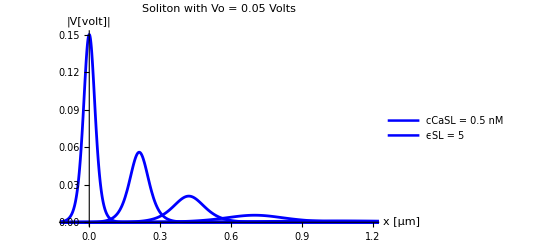

```mathematica
(*Print["Intracellular conditions at 0.05 and 0.15 molar concentration"]*)

solSP2=Plot[ {Abs[Wx[x*10^-6,0]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/10]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/5]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/3]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/2]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/1.5]*gamma*nuZe^(1/2)/24]},
{x,-25*beta*10^6,120*beta*10^6},PlotRange->{{-0.1,1.2},{0,0.15}},PlotLegends->{"cCaSL = 0.5 nM", "ϵSL = 5"},PlotLabel->"Soliton with Vo = 0.05 Volts",Axes->True,AxesLabel->{"x [μm]","|V[volt]|"},AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
solSP2Data=Cases[solSP2,Line[{x__}]->x,∞];
```

{{-0.27,4.7662×10^-8},{-0.26952,4.90684×10^-8},{-0.269039,5.05163×10^-8},{-0.268079,5.35416×10^-8},{-0.266158,6.01465×10^-8},{-0.265677,6.19213×10^-8},{-0.265197,6.37485×10^-8},{-0.264237,6.75662×10^-8},{-0.262315,7.59011×10^-8},{-0.261835,7.81408×10^-8},{-0.261355,8.04466×10^-8},{-0.260394,8.52643×10^-8},{-0.258473,9.57826×10^-8},{-0.257993,9.86089×10^-8},{-0.257512,1.01519×10^-7},{-0.256552,1.07598×10^-7},{-0.254631,1.20872×10^-7},{-0.25415,1.24438×10^-7},{-0.25367,1.2811×10^-7},{-0.25271,1.35782×10^-7},{-0.250788,1.52533×10^-7},{-0.250308,1.57034×10^-7},{-0.249828,1.61667×10^-7},{-0.248867,1.71349×10^-7},{-0.246946,1.92487×10^-7},{-0.246466,1.98167×10^-7},{-0.245986,2.04014×10^-7},{-0.245025,2.16232×10^-7},{-0.243104,2.42906×10^-7},{-0.242624,2.50074×10^-7},{-0.242143,2.57453×10^-7},{-0.241183,2.72871×10^-7},{-0.239262,3.06533×10^-7},{-0.238741,3.16351×10^-7},{-0.23822,3.26483×10^-7},{-0.237179,3.47732×10^-7},{-0.236658,3.5887×10^-7},{-0.236137,3.70365×10^-7},{-0.235096,3.9447×10^-7},{-0.234575,4.07104×10^-7},{-0.234055,4.20144×10^-7},{-0.233013,4.47489×10^-7},{-0.230931,5.07634×10^-7},{-0.23041,5.23893×10^-7},{-0.229889,5.40673×10^-7},{-0.228848,5.75862×10^-7},{-0.228327,5.94307×10^-7},{-0.227806,6.13342×10^-7},{-0.226765,6.53262×10^-7},{-0.226244,6.74185×10^-7},{-0.225724,6.95779×10^-7},{-0.224682,7.41064×10^-7},{-0.2226,8.40667×10^-7},{-0.222079,8.67593×10^-7},{-0.221558,8.95381×10^-7},{-0.220517,9.53657×10^-7},{-0.219996,9.84202×10^-7},{-0.219475,1.01573×10^-6},{-0.218434,1.08183×10^-6},{-0.217913,1.11648×10^-6},{-0.217393,1.15224×10^-6},{-0.216351,1.22724×10^-6},{-0.214269,1.39218×10^-6},{-0.213748,1.43678×10^-6},{-0.213227,1.48279×10^-6},{-0.212186,1.5793×10^-6},{-0.211665,1.62989×10^-6},{-0.211144,1.68209×10^-6},{-0.210103,1.79157×10^-6},{-0.209582,1.84895×10^-6},{-0.209062,1.90817×10^-6},{-0.20802,2.03236×10^-6},{-0.205938,2.30552×10^-6},{-0.205451,2.3744×10^-6},{-0.204965,2.44534×10^-6},{-0.203993,2.59363×10^-6},{-0.203507,2.67112×10^-6},{-0.20302,2.75092×10^-6},{-0.202048,2.91774×10^-6},{-0.201562,3.00491×10^-6},{-0.201076,3.09468×10^-6},{-0.200103,3.28235×10^-6},{-0.198159,3.69253×10^-6},{-0.197672,3.80284×10^-6},{-0.197186,3.91645×10^-6},{-0.196214,4.15396×10^-6},{-0.195728,4.27806×10^-6},{-0.195241,4.40586×10^-6},{-0.194269,4.67305×10^-6},{-0.193783,4.81266×10^-6},{-0.193297,4.95643×10^-6},{-0.192324,5.25701×10^-6},{-0.19038,5.91393×10^-6},{-0.189893,6.09061×10^-6},{-0.189407,6.27257×10^-6},{-0.188435,6.65295×10^-6},{-0.187949,6.85171×10^-6},{-0.187463,7.0564×10^-6},{-0.18649,7.48432×10^-6},{-0.186004,7.70791×10^-6},{-0.185518,7.93819×10^-6},{-0.184545,8.41957×10^-6},{-0.182601,9.47169×10^-6},{-0.182115,9.75466×10^-6},{-0.181628,0.0000100461},{-0.180656,0.0000106553},{-0.18017,0.0000109736},{-0.179684,0.0000113014},{-0.178711,0.0000119868},{-0.178225,0.0000123449},{-0.177739,0.0000127137},{-0.176767,0.0000134846},{-0.174822,0.0000151696},{-0.174345,0.0000156138},{-0.173869,0.000016071},{-0.172915,0.0000170258},{-0.171009,0.0000191092},{-0.170532,0.0000196687},{-0.170055,0.0000202445},{-0.169102,0.0000214474},{-0.167196,0.0000240717},{-0.166719,0.0000247765},{-0.166242,0.0000255019},{-0.165289,0.000027017},{-0.163382,0.0000303228},{-0.162906,0.0000312106},{-0.162429,0.0000321244},{-0.161476,0.0000340329},{-0.159569,0.000038197},{-0.159093,0.0000393153},{-0.158616,0.0000404664},{-0.157663,0.0000428705},{-0.155756,0.0000481157},{-0.155279,0.0000495244},{-0.154803,0.0000509742},{-0.153849,0.0000540025},{-0.151943,0.0000606095},{-0.151466,0.0000623838},{-0.15099,0.0000642101},{-0.150036,0.0000680246},{-0.14813,0.0000763466},{-0.147653,0.0000785815},{-0.147176,0.0000808818},{-0.146223,0.0000856864},{-0.144317,0.0000961685},{-0.143799,0.0000992258},{-0.143282,0.00010238},{-0.142248,0.000108993},{-0.141731,0.000112458},{-0.141214,0.000116033},{-0.14018,0.000123528},{-0.139663,0.000127454},{-0.139146,0.000131506},{-0.138112,0.000139999},{-0.136044,0.000158666},{-0.135527,0.000163709},{-0.13501,0.000168912},{-0.133976,0.00017982},{-0.133459,0.000185535},{-0.132942,0.000191432},{-0.131907,0.000203793},{-0.13139,0.000210269},{-0.130873,0.000216951},{-0.129839,0.000230959},{-0.127771,0.000261743},{-0.127254,0.000270059},{-0.126737,0.00027864},{-0.125703,0.000296626},{-0.125186,0.00030605},{-0.124669,0.000315773},{-0.123635,0.000336154},{-0.123118,0.000346832},{-0.122601,0.000357848},{-0.121567,0.000380941},{-0.119498,0.000431688},{-0.118981,0.000445396},{-0.118464,0.000459539},{-0.11743,0.000489183},{-0.116913,0.000504714},{-0.116396,0.000520737},{-0.115362,0.000554323},{-0.114845,0.000571917},{-0.114328,0.00059007},{-0.113294,0.000628117},{-0.111226,0.000711712},{-0.110743,0.000732762},{-0.110261,0.000754433},{-0.109295,0.00079971},{-0.107365,0.000898555},{-0.106883,0.000925114},{-0.1064,0.000952455},{-0.105435,0.00100958},{-0.103505,0.00113426},{-0.103022,0.00116776},{-0.10254,0.00120224},{-0.101575,0.00127428},{-0.0996447,0.0014315},{-0.0991622,0.00147374},{-0.0986796,0.00151721},{-0.0977145,0.00160802},{-0.0957844,0.00180616},{-0.0953018,0.00185938},{-0.0948193,0.00191416},{-0.0938542,0.00202856},{-0.0919241,0.00227813},{-0.0914415,0.00234514},{-0.090959,0.00241411},{-0.0899939,0.00255814},{-0.0880638,0.00287223},{-0.0875812,0.00295654},{-0.0870987,0.00304331},{-0.0861336,0.00322446},{-0.0842034,0.00361936},{-0.0837209,0.00372532},{-0.0832384,0.00383435},{-0.0822733,0.00406194},{-0.0803431,0.00455781},{-0.0798202,0.00470212},{-0.0792972,0.00485092},{-0.0782514,0.00516255},{-0.0777284,0.00532565},{-0.0772055,0.00549382},{-0.0761596,0.00584591},{-0.0756367,0.00603016},{-0.0751137,0.00622008},{-0.0740679,0.00661765},{-0.0719761,0.00748863},{-0.0714532,0.00772326},{-0.0709302,0.00796503},{-0.0698843,0.00847083},{-0.0693614,0.00873529},{-0.0688385,0.00900774},{-0.0677926,0.00957752},{-0.0672696,0.00987532},{-0.0667467,0.010182},{-0.0657008,0.0108232},{-0.0636091,0.0122239},{-0.0630861,0.0126003},{-0.0625632,0.0129877},{-0.0615173,0.0137968},{-0.0594256,0.0155606},{-0.0589026,0.0160337},{-0.0583797,0.0165203},{-0.0573338,0.0175353},{-0.055242,0.019742},{-0.0547191,0.0203325},{-0.0541962,0.0209393},{-0.0531503,0.0222029},{-0.0510585,0.024941},{-0.0505356,0.0256715},{-0.0500127,0.0264212},{-0.0489668,0.0279793},{-0.046875,0.0313408},{-0.0463616,0.0322178},{-0.0458482,0.0331159},{-0.0448214,0.0349765},{-0.0427678,0.0389637},{-0.0422544,0.0400173},{-0.041741,0.0410941},{-0.0407142,0.0433181},{-0.0386606,0.0480518},{-0.0381472,0.0492953},{-0.0376338,0.050563},{-0.036607,0.0531708},{-0.0345534,0.058674},{-0.0304462,0.0707811},{-0.0299328,0.07239},{-0.0294194,0.0740182},{-0.0283926,0.0773296},{-0.0263389,0.0841478},{-0.0222317,0.0983168},{-0.0217183,0.100111},{-0.0212049,0.101906},{-0.0201781,0.105487},{-0.0181245,0.112567},{-0.0140173,0.125927},{-0.0135384,0.127376},{-0.0130595,0.128796},{-0.0121017,0.131539},{-0.0116228,0.132859},{-0.0111439,0.134143},{-0.0101861,0.136593},{-0.00970723,0.137756},{-0.00922833,0.138875},{-0.00827054,0.140975},{-0.00779164,0.141954},{-0.00731274,0.142882},{-0.00635495,0.144582},{-0.00587605,0.145351},{-0.00539716,0.146065},{-0.00491826,0.146723},{-0.00443936,0.147323},{-0.00396047,0.147864},{-0.00348157,0.148346},{-0.00300267,0.148767},{-0.00252378,0.149128},{-0.00204488,0.149427},{-0.00156598,0.149663},{-0.00108708,0.149838},{-0.000608188,0.149949},{-0.000129291,0.149998},{0.000349606,0.149983},{0.000828503,0.149906},{0.0013074,0.149765},{0.0017863,0.149562},{0.00226519,0.149297},{0.00274409,0.148969},{0.00322299,0.148581},{0.00370188,0.148132},{0.00418078,0.147622},{0.00465968,0.147054},{0.00513857,0.146428},{0.00561747,0.145744},{0.00609637,0.145004},{0.00705416,0.143361},{0.00753306,0.142461},{0.00801196,0.14151},{0.00896975,0.139461},{0.00944865,0.138366},{0.00992754,0.137226},{0.0108853,0.13482},{0.0128009,0.129549},{0.0132798,0.128146},{0.0137587,0.126713},{0.0147165,0.123763},{0.0166321,0.117582},{0.0171514,0.115853},{0.0176707,0.114106},{0.0187093,0.110567},{0.0207865,0.103367},{0.0249408,0.0889115},{0.0254601,0.0871325},{0.0259794,0.0853646},{0.027018,0.081867},{0.0290952,0.0750559},{0.0332496,0.0623631},{0.0337689,0.0608759},{0.0342882,0.0594123},{0.0353268,0.0565568},{0.0374039,0.0511383},{0.0379232,0.0498453},{0.0384425,0.048577},{0.0394811,0.0461144},{0.0415583,0.0414829},{0.0420776,0.0403855},{0.0425969,0.0393118},{0.0436355,0.037235},{0.0457127,0.0333565},{0.046232,0.0324426},{0.0467513,0.0315503},{0.0477899,0.0298295},{0.0498671,0.0266334},{0.0503518,0.0259327},{0.0508366,0.0252487},{0.0518062,0.023929},{0.0537454,0.0214756},{0.0542302,0.0208993},{0.054715,0.0203373},{0.0556845,0.0192547},{0.0576237,0.0172482},{0.0581085,0.016778},{0.0585933,0.0163199},{0.0595629,0.0154386},{0.061502,0.013809},{0.0619868,0.0134278},{0.0624716,0.0130567},{0.0634412,0.0123436},{0.0653804,0.0110274},{0.0658652,0.01072},{0.0663499,0.0104209},{0.0673195,0.00984653},{0.0692587,0.00878816},{0.0697435,0.00854129},{0.0702283,0.00830115},{0.0711979,0.00784038},{0.073137,0.0069923},{0.0736218,0.00679466},{0.0741066,0.00660249},{0.0750762,0.00623394},{0.0770154,0.00555624},{0.0775001,0.00539843},{0.0779849,0.00524503},{0.0789545,0.00495095},{0.0808937,0.00441059},{0.0813689,0.00428728},{0.0818442,0.00416737},{0.0827947,0.00393737},{0.0846957,0.00351432},{0.085171,0.00341577},{0.0856462,0.00331996},{0.0865967,0.00313623},{0.0884977,0.00279843},{0.088973,0.00271978},{0.0894483,0.00264331},{0.0903988,0.00249671},{0.0922998,0.00222727},{0.092775,0.00216455},{0.0932503,0.00210358},{0.0942008,0.00198672},{0.0961018,0.00177199},{0.0965771,0.00172201},{0.0970523,0.00167344},{0.0980028,0.00158034},{0.0999038,0.00140932},{0.100379,0.00136953},{0.100854,0.00133085},{0.101805,0.00125673},{0.103706,0.0011206},{0.104181,0.00108893},{0.104656,0.00105815},{0.105607,0.000999169},{0.107508,0.000890855},{0.107983,0.000865658},{0.108458,0.000841171},{0.109409,0.000794251},{0.11131,0.000708098},{0.111826,0.000686381},{0.112341,0.000665328},{0.113373,0.000625137},{0.113888,0.000605959},{0.114404,0.000587368},{0.115435,0.000551877},{0.115951,0.000534943},{0.116466,0.000518527},{0.117498,0.000487189},{0.11956,0.000430072},{0.120076,0.00041687},{0.120592,0.000404073},{0.121623,0.000379643},{0.122139,0.000367987},{0.122654,0.000356689},{0.123686,0.000335121},{0.124201,0.00032483},{0.124717,0.000314855},{0.125748,0.000295814},{0.127811,0.000261114},{0.128327,0.000253094},{0.128842,0.000245321},{0.129873,0.000230481},{0.130389,0.000223402},{0.130905,0.000216539},{0.131936,0.00020344},{0.132452,0.00019719},{0.132967,0.000191133},{0.133999,0.000179569},{0.136061,0.000158498},{0.136577,0.000153628},{0.137093,0.000148908},{0.138124,0.000139898},{0.13864,0.000135599},{0.139155,0.000131433},{0.140187,0.00012348},{0.140702,0.000119686},{0.141218,0.000116008},{0.142249,0.000108988},{0.144312,0.0000961962},{0.144793,0.000093435},{0.145274,0.000090753},{0.146236,0.0000856178},{0.148161,0.0000762023},{0.148642,0.0000740148},{0.149123,0.0000718902},{0.150086,0.000067822},{0.15201,0.0000603631},{0.152491,0.0000586303},{0.152972,0.0000569472},{0.153935,0.0000537244},{0.155859,0.0000478157},{0.15634,0.000046443},{0.156822,0.0000451097},{0.157784,0.0000425568},{0.159708,0.0000378762},{0.16019,0.0000367888},{0.160671,0.0000357326},{0.161633,0.0000337103},{0.163558,0.0000300026},{0.164039,0.0000291412},{0.16452,0.0000283046},{0.165482,0.0000267026},{0.167407,0.0000237656},{0.167888,0.0000230833},{0.168369,0.0000224205},{0.169331,0.0000211516},{0.171256,0.0000188251},{0.171737,0.0000182846},{0.172218,0.0000177596},{0.173181,0.0000167545},{0.175105,0.0000149116},{0.175627,0.0000144481},{0.176148,0.0000139989},{0.177191,0.0000131422},{0.177713,0.0000127336},{0.178235,0.0000123378},{0.179278,0.0000115827},{0.179799,0.0000112227},{0.180321,0.0000108738},{0.181364,0.0000102083},{0.18345,8.99697×10^-6},{0.183972,8.7173×10^-6},{0.184493,8.44632×10^-6},{0.185536,7.92937×10^-6},{0.186058,7.68289×10^-6},{0.186579,7.44406×10^-6},{0.187622,6.98846×10^-6},{0.188144,6.77122×10^-6},{0.188665,6.56073×10^-6},{0.189709,6.15919×10^-6},{0.191795,5.42832×10^-6},{0.192316,5.25958×10^-6},{0.192838,5.09609×10^-6},{0.193881,4.78418×10^-6},{0.194402,4.63546×10^-6},{0.194924,4.49137×10^-6},{0.195967,4.21648×10^-6},{0.196489,4.08541×10^-6},{0.19701,3.95841×10^-6},{0.198053,3.71614×10^-6},{0.20014,3.27517×10^-6},{0.200661,3.17335×10^-6},{0.201183,3.07471×10^-6},{0.202226,2.88652×10^-6},{0.202747,2.79679×10^-6},{0.203269,2.70985×10^-6},{0.204312,2.544×10^-6},{0.204833,2.46491×10^-6},{0.205355,2.38829×10^-6},{0.206398,2.24212×10^-6},{0.208484,1.97606×10^-6},{0.208996,1.91574×10^-6},{0.209508,1.85726×10^-6},{0.210532,1.7456×10^-6},{0.211044,1.69231×10^-6},{0.211556,1.64065×10^-6},{0.21258,1.54201×10^-6},{0.213092,1.49494×10^-6},{0.213604,1.44931×10^-6},{0.214628,1.36218×10^-6},{0.216676,1.20331×10^-6},{0.217188,1.16658×10^-6},{0.2177,1.13097×10^-6},{0.218724,1.06297×10^-6},{0.219237,1.03052×10^-6},{0.219749,9.99066×10^-7},{0.220773,9.39002×10^-7},{0.221285,9.10337×10^-7},{0.221797,8.82548×10^-7},{0.222821,8.29489×10^-7},{0.224869,7.32749×10^-7},{0.225381,7.10381×10^-7},{0.225893,6.88695×10^-7},{0.226917,6.47291×10^-7},{0.227429,6.27531×10^-7},{0.227941,6.08375×10^-7},{0.228965,5.71799×10^-7},{0.229477,5.54345×10^-7},{0.229989,5.37423×10^-7},{0.231013,5.05112×10^-7},{0.233061,4.46203×10^-7},{0.233573,4.32582×10^-7},{0.234085,4.19377×10^-7},{0.235109,3.94164×10^-7},{0.235621,3.82131×10^-7},{0.236133,3.70466×10^-7},{0.237157,3.48194×10^-7},{0.237669,3.37565×10^-7},{0.238181,3.2726×10^-7},{0.239205,3.07585×10^-7},{0.241253,2.71712×10^-7},{0.24173,2.63969×10^-7},{0.242208,2.56446×10^-7},{0.243163,2.42038×10^-7},{0.245073,2.15604×10^-7},{0.245551,2.0946×10^-7},{0.246028,2.0349×10^-7},{0.246983,1.92057×10^-7},{0.248893,1.71082×10^-7},{0.249371,1.66206×10^-7},{0.249848,1.6147×10^-7},{0.250803,1.52398×10^-7},{0.252713,1.35754×10^-7},{0.253191,1.31885×10^-7},{0.253668,1.28126×10^-7},{0.254623,1.20928×10^-7},{0.256533,1.07721×10^-7},{0.257011,1.04651×10^-7},{0.257488,1.01668×10^-7},{0.258443,9.59561×10^-8},{0.260353,8.54764×10^-8},{0.260831,8.30404×10^-8},{0.261308,8.06739×10^-8},{0.262263,7.61412×10^-8},{0.264173,6.78256×10^-8},{0.264651,6.58927×10^-8},{0.265128,6.40148×10^-8},{0.266083,6.04181×10^-8},{0.267993,5.38197×10^-8},{0.268471,5.22859×10^-8},{0.268948,5.07958×10^-8},{0.269903,4.79418×10^-8},{0.271813,4.27059×10^-8},{0.272331,4.13875×10^-8},{0.272849,4.01098×10^-8},{0.273885,3.76715×10^-8},{0.274403,3.65085×10^-8},{0.274921,3.53814×10^-8},{0.275957,3.32305×10^-8},{0.276474,3.22046×10^-8},{0.276992,3.12104×10^-8},{0.278028,2.9313×10^-8},{0.2801,2.58574×10^-8},{0.280618,2.50591×10^-8},{0.281136,2.42855×10^-8},{0.282171,2.28092×10^-8},{0.282689,2.2105×10^-8},{0.283207,2.14226×10^-8},{0.284243,2.01203×10^-8},{0.284761,1.94991×10^-8},{0.285279,1.88971×10^-8},{0.286315,1.77483×10^-8},{0.288386,1.56561×10^-8},{0.288904,1.51727×10^-8},{0.289422,1.47043×10^-8},{0.290458,1.38104×10^-8},{0.290976,1.3384×10^-8},{0.291494,1.29709×10^-8},{0.292529,1.21823×10^-8},{0.293047,1.18062×10^-8},{0.293565,1.14418×10^-8},{0.294601,1.07462×10^-8},{0.296673,9.47936×10^-9},{0.297191,9.18672×10^-9},{0.297709,8.9031×10^-9},{0.298744,8.36187×10^-9},{0.299262,8.10372×10^-9},{0.29978,7.85354×10^-9},{0.300816,7.37612×10^-9},{0.301334,7.1484×10^-9},{0.301852,6.92771×10^-9},{0.302888,6.50657×10^-9},{0.304959,5.73953×10^-9},{0.305443,5.57397×10^-9},{0.305926,5.41319×10^-9},{0.306893,5.1054×10^-9},{0.308826,4.54134×10^-9},{0.30931,4.41034×10^-9},{0.309793,4.28312×10^-9},{0.31076,4.03959×10^-9},{0.312694,3.59328×10^-9},{0.313177,3.48963×10^-9},{0.31366,3.38897×10^-9},{0.314627,3.19628×10^-9},{0.316561,2.84314×10^-9},{0.317044,2.76113×10^-9},{0.317528,2.68148×10^-9},{0.318494,2.52902×10^-9},{0.320428,2.2496×10^-9},{0.320911,2.18471×10^-9},{0.321395,2.12169×10^-9},{0.322362,2.00106×10^-9},{0.324295,1.77997×10^-9},{0.324779,1.72863×10^-9},{0.325262,1.67876×10^-9},{0.326229,1.58331×10^-9},{0.328162,1.40838×10^-9},{0.328646,1.36776×10^-9},{0.329129,1.3283×10^-9},{0.330096,1.25278×10^-9},{0.33203,1.11437×10^-9},{0.332513,1.08222×10^-9},{0.332996,1.051×10^-9},{0.333963,9.91246×10^-10},{0.335897,8.81729×10^-10},{0.336421,8.54203×10^-10},{0.336944,8.27536×10^-10},{0.337992,7.76675×10^-10},{0.338516,7.52429×10^-10},{0.33904,7.28939×10^-10},{0.340087,6.84138×10^-10},{0.340611,6.6278×10^-10},{0.341135,6.4209×10^-10},{0.342182,6.02626×10^-10},{0.344278,5.30826×10^-10},{0.344801,5.14254×10^-10},{0.345325,4.982×10^-10},{0.346373,4.6758×10^-10},{0.346897,4.52983×10^-10},{0.34742,4.38842×10^-10},{0.348468,4.1187×10^-10},{0.348992,3.99013×10^-10},{0.349516,3.86556×10^-10},{0.350563,3.62798×10^-10},{0.352658,3.19572×10^-10},{0.353182,3.09596×10^-10},{0.353706,2.99931×10^-10},{0.354754,2.81497×10^-10},{0.355277,2.72709×10^-10},{0.355801,2.64196×10^-10},{0.356849,2.47958×10^-10},{0.357373,2.40217×10^-10},{0.357896,2.32718×10^-10},{0.358944,2.18415×10^-10},{0.361039,1.92392×10^-10},{0.361563,1.86386×10^-10},{0.362087,1.80567×10^-10},{0.363134,1.69469×10^-10},{0.363658,1.64179×10^-10},{0.364182,1.59053×10^-10},{0.36523,1.49278×10^-10},{0.365753,1.44617×10^-10},{0.366277,1.40103×10^-10},{0.367325,1.31492×10^-10},{0.36942,1.15825×10^-10},{0.369934,1.12274×10^-10},{0.370448,1.08832×10^-10},{0.371477,1.02261×10^-10},{0.371991,9.9126×10^-11},{0.372505,9.60869×10^-11},{0.373534,9.02855×10^-11},{0.374048,8.75175×10^-11},{0.374563,8.48344×10^-11},{0.375591,7.97123×10^-11},{0.377648,7.03774×10^-11},{0.378162,6.82197×10^-11},{0.378677,6.61282×10^-11},{0.379705,6.21356×10^-11},{0.380219,6.02306×10^-11},{0.380734,5.8384×10^-11},{0.381762,5.4859×10^-11},{0.382276,5.31771×10^-11},{0.382791,5.15468×10^-11},{0.383819,4.84345×10^-11},{0.385876,4.27625×10^-11},{0.386391,4.14514×10^-11},{0.386905,4.01806×10^-11},{0.387933,3.77546×10^-11},{0.388448,3.65971×10^-11},{0.388962,3.54751×10^-11},{0.38999,3.33332×10^-11},{0.390505,3.23113×10^-11},{0.391019,3.13207×10^-11},{0.392047,2.94296×10^-11},{0.394104,2.59832×10^-11},{0.394619,2.51866×10^-11},{0.395133,2.44144×10^-11},{0.396162,2.29403×10^-11},{0.396676,2.2237×10^-11},{0.39719,2.15553×10^-11},{0.398219,2.02538×10^-11},{0.398733,1.96329×10^-11},{0.399247,1.9031×10^-11},{0.400276,1.78819×10^-11},{0.402333,1.57878×10^-11},{0.402812,1.53358×10^-11},{0.403292,1.48967×10^-11},{0.404252,1.40559×10^-11},{0.406171,1.2514×10^-11},{0.40665,1.21557×10^-11},{0.40713,1.18077×10^-11},{0.40809,1.11412×10^-11},{0.410009,9.91903×10^-12},{0.410489,9.63504×10^-12},{0.410968,9.35918×10^-12},{0.411928,8.83092×10^-12},{0.413847,7.86218×10^-12},{0.414327,7.63708×10^-12},{0.414806,7.41842×10^-12},{0.415766,6.99971×10^-12},{0.417685,6.23184×10^-12},{0.418165,6.05342×10^-12},{0.418644,5.8801×10^-12},{0.419604,5.54822×10^-12},{0.421523,4.93958×10^-12},{0.422003,4.79816×10^-12},{0.422482,4.66078×10^-12},{0.423442,4.39772×10^-12},{0.425361,3.91529×10^-12},{0.425841,3.80319×10^-12},{0.426321,3.6943×10^-12},{0.42728,3.48579×10^-12},{0.429199,3.1034×10^-12},{0.429679,3.01455×10^-12},{0.430159,2.92824×10^-12},{0.431118,2.76296×10^-12},{0.433037,2.45987×10^-12},{0.433557,2.3836×10^-12},{0.434077,2.3097×10^-12},{0.435118,2.1687×10^-12},{0.435638,2.10146×10^-12},{0.436158,2.0363×10^-12},{0.437198,1.91199×10^-12},{0.437719,1.85271×10^-12},{0.438239,1.79527×10^-12},{0.439279,1.68567×10^-12},{0.44136,1.48614×10^-12},{0.44188,1.44007×10^-12},{0.4424,1.39542×10^-12},{0.44344,1.31023×10^-12},{0.44396,1.26961×10^-12},{0.444481,1.23025×10^-12},{0.445521,1.15514×10^-12},{0.446041,1.11933×10^-12},{0.446561,1.08463×10^-12},{0.447601,1.01841×10^-12},{0.449682,8.97865×10^-13},{0.450202,8.70027×10^-13},{0.450722,8.43052×10^-13},{0.451763,7.91586×10^-13},{0.452283,7.67044×10^-13},{0.452803,7.43262×10^-13},{0.453843,6.97888×10^-13},{0.454364,6.7625×10^-13},{0.454884,6.55284×10^-13},{0.455924,6.1528×10^-13},{0.458005,5.42451×10^-13},{0.458525,5.25633×10^-13},{0.459045,5.09336×10^-13},{0.460085,4.78242×10^-13},{0.460605,4.63415×10^-13},{0.461126,4.49047×10^-13},{0.462166,4.21634×10^-13},{0.462686,4.08561×10^-13},{0.463206,3.95894×10^-13},{0.464246,3.71726×10^-13},{0.466327,3.27726×10^-13},{0.466813,3.18229×10^-13},{0.467298,3.09007×10^-13},{0.46827,2.91358×10^-13},{0.470212,2.59026×10^-13},{0.470698,2.5152×10^-13},{0.471184,2.44232×10^-13},{0.472155,2.30282×10^-13},{0.474098,2.04728×10^-13},{0.474583,1.98796×10^-13},{0.475069,1.93035×10^-13},{0.47604,1.8201×10^-13},{0.477983,1.61812×10^-13},{0.478468,1.57123×10^-13},{0.478954,1.5257×10^-13},{0.479925,1.43856×10^-13},{0.481868,1.27893×10^-13},{0.482354,1.24187×10^-13},{0.482839,1.20588×10^-13},{0.483811,1.137×10^-13},{0.485753,1.01083×10^-13},{0.486239,9.8154×10^-14},{0.486724,9.53097×10^-14},{0.487696,8.98661×10^-14},{0.489638,7.98937×10^-14},{0.490124,7.75786×10^-14},{0.49061,7.53305×10^-14},{0.491581,7.1028×10^-14},{0.493524,6.31461×10^-14},{0.494009,6.13162×10^-14},{0.494495,5.95394×10^-14},{0.495466,5.61388×10^-14},{0.497409,4.99091×10^-14},{0.497885,4.84909×10^-14},{0.498361,4.71129×10^-14},{0.499313,4.44734×10^-14},{0.501218,3.96296×10^-14},{0.501694,3.85035×10^-14},{0.50217,3.74093×10^-14},{0.503122,3.53134×10^-14},{0.505027,3.14673×10^-14},{0.505503,3.05731×10^-14},{0.505979,2.97043×10^-14},{0.506931,2.80401×10^-14},{0.508836,2.49862×10^-14},{0.509312,2.42762×10^-14},{0.509788,2.35863×10^-14},{0.51074,2.22649×10^-14},{0.512644,1.98399×10^-14},{0.513121,1.92761×10^-14},{0.513597,1.87284×10^-14},{0.514549,1.76791×10^-14},{0.516453,1.57536×10^-14},{0.517406,1.4871×10^-14},{0.518358,1.40378×10^-14},{0.520262,1.25089×10^-14},{0.521214,1.18081×10^-14},{0.522167,1.11465×10^-14},{0.524071,9.93253×10^-15},{0.525023,9.37605×10^-15},{0.525976,8.85075×10^-15},{0.52788,7.88679×10^-15},{0.528913,7.40859×10^-15},{0.529946,6.95938×10^-15},{0.530979,6.53741×10^-15},{0.532012,6.14103×10^-15},{0.533045,5.76868×10^-15},{0.534078,5.41891×10^-15},{0.536144,4.7817×10^-15},{0.537177,4.49177×10^-15},{0.53821,4.21942×10^-15},{0.539243,3.96359×10^-15},{0.540276,3.72326×10^-15},{0.542342,3.28545×10^-15},{0.544408,2.89911×10^-15},{0.546475,2.55821×10^-15},{0.548541,2.25739×10^-15},{0.550607,1.99194×10^-15},{0.552673,1.75771×10^-15},{0.554739,1.55102×10^-15},{0.556805,1.36864×10^-15},{0.558871,1.2077×10^-15},{0.560937,1.06569×10^-15},{0.564793,8.43781×10^-16},{0.568649,6.68082×10^-16},{0.572505,5.28969×10^-16},{0.576361,4.18822×10^-16},{0.576843,4.06776×10^-16},{0.577325,3.95075×10^-16},{0.578289,3.72675×10^-16},{0.580217,3.31612×10^-16},{0.584073,2.62561×10^-16},{0.584555,2.55009×10^-16},{0.585037,2.47674×10^-16},{0.586001,2.33631×10^-16},{0.587929,2.07888×10^-16},{0.591785,1.646×10^-16},{0.592308,1.59475×10^-16},{0.59283,1.5451×10^-16},{0.593875,1.45038×10^-16},{0.595965,1.278×10^-16},{0.600144,9.92276×10^-17},{0.608502,5.98184×10^-17},{0.62522,2.1739×10^-17},{0.658043,2.97921×10^-18},{0.688659,4.66693×10^-19},{0.72186,6.25133×10^-20},{0.752852,9.57158×10^-21},{0.783234,1.52071×10^-21},{0.816202,2.06594×10^-22},{0.846962,3.20818×10^-23},{0.880307,4.26001×10^-24},{0.911443,6.46596×10^-25},{0.94197,1.01837×10^-25},{0.975082,1.37148×10^-26},{1.00599,2.11126×10^-27},{1.03947,2.7791×10^-28},{1.07235,3.79592×10^-29},{1.10302,5.92654×10^-30},{1.13628,7.91215×10^-31},{1.16733,1.20742×10^-31},{1.19776,1.91194×10^-32},{1.23079,2.58879×10^-33},{1.2616,4.00675×10^-34},{1.26214,3.87846×10^-34},{1.26268,3.75427×10^-34},{1.26375,3.5177×10^-34},{1.2659,3.08833×10^-34},{1.2702,2.38044×10^-34},{1.2788,1.41423×10^-34},{1.27934,1.36895×10^-34},{1.27988,1.32511×10^-34},{1.28095,1.24161×10^-34},{1.2831,1.09007×10^-34},{1.2874,8.40203×10^-35},{1.28794,8.133×10^-35},{1.28848,7.87259×10^-35},{1.28955,7.3765×10^-35},{1.2917,6.47614×10^-35},{1.29224,6.26878×10^-35},{1.29278,6.06805×10^-35},{1.29385,5.68568×10^-35},{1.29439,5.50363×10^-35},{1.29493,5.3274×10^-35},{1.29546,5.15682×10^-35},{1.296,4.9917×10^-35},{-0.27,4.12734×10^-9},{-0.26952,4.2013×10^-9},{-0.269039,4.27659×10^-9},{-0.268079,4.43124×10^-9},{-0.266158,4.75751×10^-9},{-0.265677,4.84277×10^-9},{-0.265197,4.92955×10^-9},{-0.264237,5.10781×10^-9},{-0.262315,5.4839×10^-9},{-0.261835,5.58217×10^-9},{-0.261355,5.68221×10^-9},{-0.260394,5.88768×10^-9},{-0.258473,6.3212×10^-9},{-0.254631,7.28633×10^-9},{-0.25415,7.41691×10^-9},{-0.25367,7.54982×10^-9},{-0.25271,7.82283×10^-9},{-0.250788,8.39883×10^-9},{-0.250308,8.54934×10^-9},{-0.249828,8.70255×10^-9},{-0.248867,9.01724×10^-9},{-0.246946,9.68119×10^-9},{-0.246466,9.85468×10^-9},{-0.245986,1.00313×10^-8},{-0.245025,1.0394×10^-8},{-0.243104,1.11593×10^-8},{-0.239262,1.28632×10^-8},{-0.238741,1.31133×10^-8},{-0.23822,1.33682×10^-8},{-0.237179,1.38931×10^-8},{-0.235096,1.50054×10^-8},{-0.234575,1.52972×10^-8},{-0.234055,1.55946×10^-8},{-0.233013,1.62069×10^-8},{-0.230931,1.75045×10^-8},{-0.23041,1.78448×10^-8},{-0.229889,1.81917×10^-8},{-0.228848,1.8906×10^-8},{-0.226765,2.04197×10^-8},{-0.2226,2.38205×10^-8},{-0.222079,2.42836×10^-8},{-0.221558,2.47557×10^-8},{-0.220517,2.57277×10^-8},{-0.218434,2.77876×10^-8},{-0.217913,2.83278×10^-8},{-0.217393,2.88786×10^-8},{-0.216351,3.00124×10^-8},{-0.214269,3.24154×10^-8},{-0.213748,3.30456×10^-8},{-0.213227,3.36881×10^-8},{-0.212186,3.50107×10^-8},{-0.210103,3.78139×10^-8},{-0.205938,4.41115×10^-8},{-0.205451,4.49118×10^-8},{-0.204965,4.57266×10^-8},{-0.203993,4.74008×10^-8},{-0.202048,5.09353×10^-8},{-0.201562,5.18594×10^-8},{-0.201076,5.28002×10^-8},{-0.200103,5.47334×10^-8},{-0.198159,5.88147×10^-8},{-0.197672,5.98818×10^-8},{-0.197186,6.09681×10^-8},{-0.196214,6.32004×10^-8},{-0.194269,6.7913×10^-8},{-0.19038,7.84188×10^-8},{-0.189893,7.98415×10^-8},{-0.189407,8.129×10^-8},{-0.188435,8.42663×10^-8},{-0.18649,9.05498×10^-8},{-0.186004,9.21925×10^-8},{-0.185518,9.38651×10^-8},{-0.184545,9.73018×10^-8},{-0.182601,1.04557×10^-7},{-0.182115,1.06454×10^-7},{-0.181628,1.08385×10^-7},{-0.180656,1.12354×10^-7},{-0.178711,1.20732×10^-7},{-0.174822,1.39408×10^-7},{-0.174345,1.41887×10^-7},{-0.173869,1.44411×10^-7},{-0.172915,1.49592×10^-7},{-0.171009,1.6052×10^-7},{-0.170532,1.63375×10^-7},{-0.170055,1.6628×10^-7},{-0.169102,1.72247×10^-7},{-0.167196,1.8483×10^-7},{-0.166719,1.88117×10^-7},{-0.166242,1.91462×10^-7},{-0.165289,1.98332×10^-7},{-0.163382,2.1282×10^-7},{-0.159569,2.4505×10^-7},{-0.159093,2.49408×10^-7},{-0.158616,2.53843×10^-7},{-0.157663,2.62952×10^-7},{-0.155756,2.82161×10^-7},{-0.155279,2.87178×10^-7},{-0.154803,2.92285×10^-7},{-0.153849,3.02773×10^-7},{-0.151943,3.24891×10^-7},{-0.151466,3.30669×10^-7},{-0.15099,3.36549×10^-7},{-0.150036,3.48625×10^-7},{-0.14813,3.74093×10^-7},{-0.144317,4.30746×10^-7},{-0.143799,4.39061×10^-7},{-0.143282,4.47537×10^-7},{-0.142248,4.64983×10^-7},{-0.14018,5.01942×10^-7},{-0.139663,5.11632×10^-7},{-0.139146,5.21509×10^-7},{-0.138112,5.41838×10^-7},{-0.136044,5.84905×10^-7},{-0.135527,5.96197×10^-7},{-0.13501,6.07706×10^-7},{-0.133976,6.31396×10^-7},{-0.131907,6.81581×10^-7},{-0.127771,7.94236×10^-7},{-0.127254,8.09568×10^-7},{-0.126737,8.25197×10^-7},{-0.125703,8.57365×10^-7},{-0.123635,9.25511×10^-7},{-0.123118,9.43377×10^-7},{-0.122601,9.61589×10^-7},{-0.121567,9.99073×10^-7},{-0.119498,1.07848×10^-6},{-0.118981,1.0993×10^-6},{-0.118464,1.12052×10^-6},{-0.11743,1.1642×10^-6},{-0.115362,1.25674×10^-6},{-0.111226,1.46446×10^-6},{-0.110743,1.49082×10^-6},{-0.110261,1.51767×10^-6},{-0.109295,1.57281×10^-6},{-0.107365,1.68918×10^-6},{-0.106883,1.71959×10^-6},{-0.1064,1.75055×10^-6},{-0.105435,1.81415×10^-6},{-0.103505,1.94838×10^-6},{-0.103022,1.98346×10^-6},{-0.10254,2.01917×10^-6},{-0.101575,2.09253×10^-6},{-0.0996447,2.24735×10^-6},{-0.0957844,2.5922×10^-6},{-0.0953018,2.63887×10^-6},{-0.0948193,2.68638×10^-6},{-0.0938542,2.78399×10^-6},{-0.0919241,2.98996×10^-6},{-0.0914415,3.0438×10^-6},{-0.090959,3.0986×10^-6},{-0.0899939,3.21118×10^-6},{-0.0880638,3.44876×10^-6},{-0.0875812,3.51086×10^-6},{-0.0870987,3.57407×10^-6},{-0.0861336,3.70392×10^-6},{-0.0842034,3.97796×10^-6},{-0.0803431,4.58836×10^-6},{-0.0798202,4.67795×10^-6},{-0.0792972,4.76929×10^-6},{-0.0782514,4.95736×10^-6},{-0.0761596,5.35604×10^-6},{-0.0756367,5.46062×10^-6},{-0.0751137,5.56725×10^-6},{-0.0740679,5.78678×10^-6},{-0.0719761,6.25216×10^-6},{-0.0714532,6.37424×10^-6},{-0.0709302,6.4987×10^-6},{-0.0698843,6.75496×10^-6},{-0.0677926,7.2982×10^-6},{-0.0636091,8.51924×10^-6},{-0.0630861,8.68558×10^-6},{-0.0625632,8.85517×10^-6},{-0.0615173,9.20435×10^-6},{-0.0594256,9.94455×10^-6},{-0.0589026,0.0000101387},{-0.0583797,0.0000103367},{-0.0573338,0.0000107443},{-0.055242,0.0000116083},{-0.0547191,0.0000118349},{-0.0541962,0.000012066},{-0.0531503,0.0000125418},{-0.0510585,0.0000135504},{-0.046875,0.0000158173},{-0.0463616,0.0000161204},{-0.0458482,0.0000164293},{-0.0448214,0.0000170651},{-0.0427678,0.0000184114},{-0.0422544,0.0000187642},{-0.041741,0.0000191238},{-0.0407142,0.0000198638},{-0.0386606,0.0000214308},{-0.0381472,0.0000218415},{-0.0376338,0.0000222601},{-0.036607,0.0000231214},{-0.0345534,0.0000249453},{-0.0304462,0.0000290361},{-0.0299328,0.0000295925},{-0.0294194,0.0000301595},{-0.0283926,0.0000313264},{-0.0263389,0.0000337974},{-0.0258255,0.000034445},{-0.0253121,0.0000351051},{-0.0242853,0.0000364633},{-0.0222317,0.0000393393},{-0.0217183,0.0000400931},{-0.0212049,0.0000408613},{-0.0201781,0.0000424421},{-0.0181245,0.0000457895},{-0.0140173,0.0000532968},{-0.0135384,0.0000542486},{-0.0130595,0.0000552175},{-0.0121017,0.0000572073},{-0.0101861,0.0000614046},{-0.00970723,0.0000625011},{-0.00922833,0.0000636172},{-0.00827054,0.0000659096},{-0.00635495,0.0000707449},{-0.00587605,0.0000720082},{-0.00539716,0.000073294},{-0.00443936,0.0000759348},{-0.00252378,0.0000815051},{0.0013074,0.0000939004},{0.0017863,0.0000955768},{0.00226519,0.000097283},{0.00322299,0.000100787},{0.00513857,0.000108179},{0.00561747,0.00011011},{0.00609637,0.000112075},{0.00705416,0.000116112},{0.00896975,0.000124626},{0.00944865,0.000126851},{0.00992754,0.000129115},{0.0108853,0.000133764},{0.0128009,0.000143571},{0.0166321,0.000165392},{0.0171514,0.000168594},{0.0176707,0.000171858},{0.0187093,0.000178576},{0.0207865,0.00019281},{0.0213058,0.000196542},{0.0218251,0.000200346},{0.0228637,0.000208176},{0.0249408,0.000224764},{0.0254601,0.000229113},{0.0259794,0.000233546},{0.027018,0.000242671},{0.0290952,0.000262001},{0.0332496,0.00030539},{0.0337689,0.000311295},{0.0342882,0.000317314},{0.0353268,0.000329702},{0.0374039,0.000355943},{0.0379232,0.000362822},{0.0384425,0.000369833},{0.0394811,0.000384265},{0.0415583,0.000414832},{0.0420776,0.000422845},{0.0425969,0.000431012},{0.0436355,0.000447821},{0.0457127,0.000483421},{0.0498671,0.000563294},{0.0503518,0.000573432},{0.0508366,0.000583751},{0.0518062,0.000604946},{0.0537454,0.00064966},{0.0542302,0.000661342},{0.054715,0.000673233},{0.0556845,0.000697657},{0.0576237,0.000749177},{0.0581085,0.000762636},{0.0585933,0.000776336},{0.0595629,0.000804473},{0.061502,0.000863819},{0.0653804,0.000995846},{0.0658652,0.0010137},{0.0663499,0.00103186},{0.0673195,0.00106917},{0.0692587,0.00114784},{0.0697435,0.00116839},{0.0702283,0.0011893},{0.0711979,0.00123223},{0.073137,0.00132276},{0.0736218,0.0013464},{0.0741066,0.00137045},{0.0750762,0.00141984},{0.0770154,0.00152396},{0.0808937,0.00175527},{0.0813689,0.00178589},{0.0818442,0.00181703},{0.0827947,0.00188094},{0.0846957,0.00201544},{0.085171,0.00205051},{0.0856462,0.00208619},{0.0865967,0.00215937},{0.0884977,0.00231335},{0.088973,0.0023535},{0.0894483,0.00239433},{0.0903988,0.00247807},{0.0922998,0.00265422},{0.0961018,0.00304388},{0.0965771,0.00309633},{0.0970523,0.00314966},{0.0980028,0.00325902},{0.0999038,0.00348886},{0.100379,0.00354873},{0.100854,0.00360958},{0.101805,0.00373434},{0.103706,0.00399643},{0.104181,0.00406467},{0.104656,0.00413402},{0.105607,0.00427616},{0.107508,0.0045746},{0.11131,0.00523219},{0.111826,0.00532801},{0.112341,0.00542548},{0.113373,0.00562552},{0.115435,0.00604666},{0.115951,0.00615648},{0.116466,0.00626817},{0.117498,0.00649727},{0.11956,0.00697911},{0.120076,0.00710466},{0.120592,0.0072323},{0.121623,0.00749396},{0.123686,0.00804366},{0.127811,0.00925507},{0.128327,0.00941757},{0.128842,0.00958263},{0.129873,0.00992055},{0.131936,0.0106284},{0.136061,0.0121786},{0.136577,0.0123855},{0.137093,0.0125954},{0.138124,0.0130243},{0.140187,0.0139194},{0.144312,0.0158631},{0.144793,0.0161035},{0.145274,0.0163468},{0.146236,0.016842},{0.148161,0.0178677},{0.15201,0.0200605},{0.159708,0.0250014},{0.16019,0.0253335},{0.160671,0.0256683},{0.161633,0.0263453},{0.163558,0.0277284},{0.167407,0.0305988},{0.175105,0.0366277},{0.175627,0.037043},{0.176148,0.0374583},{0.177191,0.0382887},{0.179278,0.0399437},{0.18345,0.0431914},{0.183972,0.043588},{0.184493,0.0439818},{0.185536,0.0447604},{0.187622,0.0462762},{0.191795,0.0490957},{0.192316,0.0494243},{0.192838,0.0497469},{0.193881,0.0503734},{0.195967,0.0515461},{0.196489,0.0518215},{0.19701,0.0520893},{0.198053,0.0526018},{0.20014,0.0535291},{0.200661,0.0537396},{0.201183,0.0539414},{0.202226,0.0543179},{0.202747,0.0544924},{0.203269,0.0546576},{0.204312,0.0549594},{0.204833,0.0550958},{0.205355,0.0552225},{0.205877,0.0553393},{0.206398,0.0554462},{0.20692,0.055543},{0.207441,0.0556297},{0.207963,0.0557062},{0.208484,0.0557726},{0.208996,0.0558277},{0.209508,0.0558729},{0.21002,0.0559081},{0.210532,0.0559333},{0.211044,0.0559485},{0.211556,0.0559537},{0.212068,0.0559488},{0.21258,0.0559339},{0.213092,0.055909},{0.213604,0.0558741},{0.214116,0.0558293},{0.214628,0.0557745},{0.21514,0.0557098},{0.215652,0.0556352},{0.216164,0.0555508},{0.216676,0.0554567},{0.217188,0.0553529},{0.2177,0.0552395},{0.218212,0.0551166},{0.218724,0.0549843},{0.219237,0.0548426},{0.219749,0.0546917},{0.220773,0.0543625},{0.221285,0.0541845},{0.221797,0.0539976},{0.222821,0.0535982},{0.224869,0.0526996},{0.225381,0.0524551},{0.225893,0.052203},{0.226917,0.0516764},{0.228965,0.0505391},{0.233061,0.0479677},{0.233573,0.0476222},{0.234085,0.0472719},{0.235109,0.046558},{0.237157,0.0450819},{0.241253,0.04198},{0.24173,0.0416088},{0.242208,0.041236},{0.243163,0.0404866},{0.245073,0.0389759},{0.248893,0.035936},{0.256533,0.0299835},{0.257011,0.0296237},{0.257488,0.0292658},{0.258443,0.028556},{0.260353,0.0271619},{0.264173,0.0244869},{0.271813,0.0196509},{0.272331,0.0193494},{0.272849,0.0190514},{0.273885,0.0184656},{0.275957,0.017335},{0.2801,0.0152365},{0.280618,0.0149892},{0.281136,0.0147452},{0.282171,0.014267},{0.284243,0.0133492},{0.288386,0.0116629},{0.288904,0.0114657},{0.289422,0.0112713},{0.290458,0.0108912},{0.292529,0.0101648},{0.293047,0.00998999},{0.293565,0.00981792},{0.294601,0.00948169},{0.296673,0.00884013},{0.297191,0.008686},{0.297709,0.00853431},{0.298744,0.00823815},{0.300816,0.00767386},{0.304959,0.00665072},{0.305443,0.00653998},{0.305926,0.00643097},{0.306893,0.00621803},{0.308826,0.00581185},{0.30931,0.00571428},{0.309793,0.00561825},{0.31076,0.00543075},{0.312694,0.00507339},{0.313177,0.0049876},{0.31366,0.00490319},{0.314627,0.00473844},{0.316561,0.00442465},{0.320428,0.00385574},{0.320911,0.00378978},{0.321395,0.00372491},{0.322362,0.00359836},{0.324295,0.00335761},{0.324779,0.0032999},{0.325262,0.00324315},{0.326229,0.00313249},{0.328162,0.00292204},{0.328646,0.00287161},{0.329129,0.00282203},{0.330096,0.00272536},{0.33203,0.00254161},{0.335897,0.00220968},{0.336421,0.00216812},{0.336944,0.00212733},{0.337992,0.00204798},{0.340087,0.0018979},{0.340611,0.0018621},{0.341135,0.00182697},{0.342182,0.00175864},{0.344278,0.00162945},{0.344801,0.00159864},{0.345325,0.0015684},{0.346373,0.00150961},{0.348468,0.00139848},{0.352658,0.00119989},{0.353182,0.00117711},{0.353706,0.00115476},{0.354754,0.00111132},{0.356849,0.00102923},{0.357373,0.00100966},{0.357896,0.000990466},{0.358944,0.00095315},{0.361039,0.000882649},{0.361563,0.000865848},{0.362087,0.000849364},{0.363134,0.000817324},{0.36523,0.000756801},{0.36942,0.000648791},{0.369934,0.000636638},{0.370448,0.000624712},{0.371477,0.000601523},{0.373534,0.000557681},{0.374048,0.000547227},{0.374563,0.000536968},{0.375591,0.00051702},{0.377648,0.000479311},{0.378162,0.00047032},{0.378677,0.000461496},{0.379705,0.000444341},{0.381762,0.000411913},{0.385876,0.000353962},{0.386391,0.000347315},{0.386905,0.000340792},{0.387933,0.000328111},{0.38999,0.000304142},{0.390505,0.000298428},{0.391019,0.000292821},{0.392047,0.00028192},{0.394104,0.000261317},{0.394619,0.000256406},{0.395133,0.000251587},{0.396162,0.000242217},{0.398219,0.00022451},{0.402333,0.000192879},{0.402812,0.000189493},{0.403292,0.000186166},{0.404252,0.000179686},{0.406171,0.000167395},{0.40665,0.000164456},{0.40713,0.000161568},{0.40809,0.000155943},{0.410009,0.000145274},{0.410489,0.000142722},{0.410968,0.000140216},{0.411928,0.000135333},{0.413847,0.000126072},{0.417685,0.000109407},{0.418165,0.000107484},{0.418644,0.000105596},{0.419604,0.000101918},{0.421523,0.0000949419},{0.422003,0.0000932737},{0.422482,0.0000916348},{0.423442,0.0000884428},{0.425361,0.0000823883},{0.425841,0.0000809405},{0.426321,0.0000795181},{0.42728,0.0000767479},{0.429199,0.0000714934},{0.433037,0.0000620385},{0.433557,0.0000608572},{0.434077,0.0000596984},{0.435118,0.0000574464},{0.437198,0.0000531941},{0.437719,0.0000521811},{0.438239,0.0000511874},{0.439279,0.0000492564},{0.44136,0.0000456101},{0.44188,0.0000447415},{0.4424,0.0000438894},{0.44344,0.0000422336},{0.445521,0.0000391069},{0.449682,0.0000335308},{0.450202,0.0000328921},{0.450722,0.0000322656},{0.451763,0.0000310482},{0.453843,0.0000287495},{0.454364,0.0000282019},{0.454884,0.0000276647},{0.455924,0.0000266208},{0.458005,0.0000246498},{0.458525,0.0000241803},{0.459045,0.0000237197},{0.460085,0.0000228247},{0.462166,0.0000211346},{0.466327,0.0000181207},{0.466813,0.0000177982},{0.467298,0.0000174814},{0.46827,0.0000168647},{0.470212,0.0000156959},{0.470698,0.0000154165},{0.471184,0.0000151421},{0.472155,0.000014608},{0.474098,0.0000135955},{0.474583,0.0000133535},{0.475069,0.0000131159},{0.47604,0.0000126531},{0.477983,0.0000117761},{0.481868,0.0000102002},{0.482354,0.0000100187},{0.482839,9.84037×10^-6},{0.483811,9.49321×10^-6},{0.485753,8.8352×10^-6},{0.486239,8.67795×10^-6},{0.486724,8.5235×10^-6},{0.487696,8.22279×10^-6},{0.489638,7.65283×10^-6},{0.490124,7.51662×10^-6},{0.49061,7.38284×10^-6},{0.491581,7.12237×10^-6},{0.493524,6.62868×10^-6},{0.497409,5.74159×10^-6},{0.497885,5.64138×10^-6},{0.498361,5.54293×10^-6},{0.499313,5.35114×10^-6},{0.501218,4.98725×10^-6},{0.501694,4.90021×10^-6},{0.50217,4.81469×10^-6},{0.503122,4.64811×10^-6},{0.505027,4.33202×10^-6},{0.505503,4.25642×10^-6},{0.505979,4.18213×10^-6},{0.506931,4.03743×10^-6},{0.508836,3.76287×10^-6},{0.512644,3.26849×10^-6},{0.513121,3.21145×10^-6},{0.513597,3.1554×10^-6},{0.514549,3.04622×10^-6},{0.516453,2.83907×10^-6},{0.516929,2.78952×10^-6},{0.517406,2.74084×10^-6},{0.518358,2.646×10^-6},{0.520262,2.46606×10^-6},{0.520738,2.42302×10^-6},{0.521214,2.38073×10^-6},{0.522167,2.29836×10^-6},{0.524071,2.14206×10^-6},{0.52788,1.86063×10^-6},{0.528397,1.82542×10^-6},{0.528913,1.79089×10^-6},{0.529946,1.72376×10^-6},{0.532012,1.59697×10^-6},{0.532529,1.56675×10^-6},{0.533045,1.53711×10^-6},{0.534078,1.4795×10^-6},{0.536144,1.37067×10^-6},{0.536661,1.34474×10^-6},{0.537177,1.3193×10^-6},{0.53821,1.26985×10^-6},{0.540276,1.17644×10^-6},{0.544408,1.00973×10^-6},{0.544925,9.90628×10^-7},{0.545442,9.71886×10^-7},{0.546475,9.35458×10^-7},{0.548541,8.66647×10^-7},{0.549057,8.50251×10^-7},{0.549574,8.34164×10^-7},{0.550607,8.02898×10^-7},{0.552673,7.43839×10^-7},{0.553189,7.29765×10^-7},{0.553706,7.15958×10^-7},{0.554739,6.89123×10^-7},{0.556805,6.38433×10^-7},{0.560937,5.47963×10^-7},{0.561419,5.38282×10^-7},{0.561901,5.28772×10^-7},{0.562865,5.10253×10^-7},{0.564793,4.75139×10^-7},{0.565275,4.66745×10^-7},{0.565757,4.58499×10^-7},{0.566721,4.42441×10^-7},{0.568649,4.11993×10^-7},{0.569131,4.04715×10^-7},{0.569613,3.97564×10^-7},{0.570577,3.83641×10^-7},{0.572505,3.5724×10^-7},{0.576361,3.09763×10^-7},{0.576843,3.0429×10^-7},{0.577325,2.98914×10^-7},{0.578289,2.88445×10^-7},{0.580217,2.68595×10^-7},{0.580699,2.6385×10^-7},{0.581181,2.59189×10^-7},{0.582145,2.50111×10^-7},{0.584073,2.32899×10^-7},{0.584555,2.28784×10^-7},{0.585037,2.24742×10^-7},{0.586001,2.16871×10^-7},{0.587929,2.01947×10^-7},{0.591785,1.75108×10^-7},{0.592308,1.71758×10^-7},{0.59283,1.68471×10^-7},{0.593875,1.62086×10^-7},{0.595965,1.50032×10^-7},{0.596487,1.47162×10^-7},{0.59701,1.44346×10^-7},{0.598054,1.38875×10^-7},{0.600144,1.28548×10^-7},{0.600666,1.26088×10^-7},{0.601189,1.23675×10^-7},{0.602234,1.18988×10^-7},{0.604323,1.10139×10^-7},{0.608502,9.43672×10^-8},{0.609025,9.25616×10^-8},{0.609547,9.07905×10^-8},{0.610592,8.73495×10^-8},{0.612682,8.08536×10^-8},{0.613204,7.93066×10^-8},{0.613727,7.77892×10^-8},{0.614771,7.48409×10^-8},{0.616861,6.92753×10^-8},{0.617383,6.79498×10^-8},{0.617906,6.66496×10^-8},{0.618951,6.41235×10^-8},{0.62104,5.93549×10^-8},{0.62522,5.08552×10^-8},{0.625732,4.98997×10^-8},{0.626245,4.89622×10^-8},{0.627271,4.71397×10^-8},{0.629322,4.36957×10^-8},{0.629835,4.28748×10^-8},{0.630348,4.20693×10^-8},{0.631374,4.05034×10^-8},{0.633425,3.75442×10^-8},{0.633938,3.68389×10^-8},{0.634451,3.61467×10^-8},{0.635477,3.48013×10^-8},{0.637528,3.22587×10^-8},{0.641631,2.77173×10^-8},{0.642144,2.71966×10^-8},{0.642657,2.66856×10^-8},{0.643683,2.56923×10^-8},{0.645734,2.38152×10^-8},{0.646247,2.33678×10^-8},{0.64676,2.29288×10^-8},{0.647786,2.20753×10^-8},{0.649837,2.04625×10^-8},{0.65035,2.00781×10^-8},{0.650863,1.97008×10^-8},{0.651889,1.89675×10^-8},{0.65394,1.75818×10^-8},{0.658043,1.51066×10^-8},{0.658522,1.48417×10^-8},{0.659,1.45815×10^-8},{0.659957,1.40746×10^-8},{0.66187,1.31131×10^-8},{0.662349,1.28831×10^-8},{0.662827,1.26572×10^-8},{0.663784,1.22172×10^-8},{0.665697,1.13826×10^-8},{0.666175,1.1183×10^-8},{0.666654,1.09869×10^-8},{0.667611,1.0605×10^-8},{0.669524,9.88049×10^-9},{0.673351,8.57661×10^-9},{0.673829,8.42622×10^-9},{0.674308,8.27847×10^-9},{0.675264,7.99069×10^-9},{0.677178,7.4448×10^-9},{0.677656,7.31426×10^-9},{0.678135,7.186×10^-9},{0.679091,6.9362×10^-9},{0.681005,6.46235×10^-9},{0.681483,6.34903×10^-9},{0.681961,6.2377×10^-9},{0.682918,6.02086×10^-9},{0.684832,5.60954×10^-9},{0.688659,4.86928×10^-9},{0.689177,4.77676×10^-9},{0.689696,4.68599×10^-9},{0.690734,4.5096×10^-9},{0.692809,4.17649×10^-9},{0.693327,4.09713×10^-9},{0.693846,4.01928×10^-9},{0.694884,3.86798×10^-9},{0.696959,3.58227×10^-9},{0.697478,3.5142×10^-9},{0.697996,3.44742×10^-9},{0.699034,3.31766×10^-9},{0.701109,3.07259×10^-9},{0.705259,2.63543×10^-9},{0.705778,2.58535×10^-9},{0.706297,2.53622×10^-9},{0.707334,2.44076×10^-9},{0.709409,2.26046×10^-9},{0.709928,2.21751×10^-9},{0.710447,2.17538×10^-9},{0.711484,2.09349×10^-9},{0.713559,1.93885×10^-9},{0.714078,1.90201×10^-9},{0.714597,1.86587×10^-9},{0.715634,1.79563×10^-9},{0.717709,1.66299×10^-9},{0.72186,1.42639×10^-9},{0.722344,1.40107×10^-9},{0.722828,1.3762×10^-9},{0.723797,1.32778×10^-9},{0.725734,1.236×10^-9},{0.726218,1.21406×10^-9},{0.726702,1.19251×10^-9},{0.727671,1.15056×10^-9},{0.729608,1.07102×10^-9},{0.730092,1.05201×10^-9},{0.730576,1.03334×10^-9},{0.731545,9.96982×10^-10},{0.733482,9.28063×10^-10},{0.737356,8.04187×10^-10},{0.73784,7.89914×10^-10},{0.738324,7.75894×10^-10},{0.739293,7.48596×10^-10},{0.74123,6.96847×10^-10},{0.741714,6.84478×10^-10},{0.742198,6.7233×10^-10},{0.743167,6.48675×10^-10},{0.745104,6.03834×10^-10},{0.745588,5.93116×10^-10},{0.746073,5.82589×10^-10},{0.747041,5.62092×10^-10},{0.748978,5.23235×10^-10},{0.752852,4.53395×10^-10},{0.753327,4.45505×10^-10},{0.753802,4.37752×10^-10},{0.754751,4.22649×10^-10},{0.75665,3.93988×10^-10},{0.757125,3.87131×10^-10},{0.757599,3.80394×10^-10},{0.758549,3.6727×10^-10},{0.760448,3.42364×10^-10},{0.760922,3.36406×10^-10},{0.761397,3.30551×10^-10},{0.762347,3.19147×10^-10},{0.764246,2.97504×10^-10},{0.768043,2.58523×10^-10},{0.768518,2.54024×10^-10},{0.768993,2.49603×10^-10},{0.769942,2.40991×10^-10},{0.771841,2.24649×10^-10},{0.772316,2.20739×10^-10},{0.772791,2.16898×10^-10},{0.77374,2.09414×10^-10},{0.775639,1.95213×10^-10},{0.776114,1.91816×10^-10},{0.776588,1.88478×10^-10},{0.777538,1.81975×10^-10},{0.779437,1.69635×10^-10},{0.783234,1.47408×10^-10},{0.78375,1.44626×10^-10},{0.784265,1.41897×10^-10},{0.785295,1.36593×10^-10},{0.787355,1.26571×10^-10},{0.787871,1.24183×10^-10},{0.788386,1.21839×10^-10},{0.789416,1.17285×10^-10},{0.791476,1.0868×10^-10},{0.791991,1.06629×10^-10},{0.792507,1.04617×10^-10},{0.793537,1.00706×10^-10},{0.795597,9.33176×10^-11},{0.799718,8.01269×10^-11},{0.800233,7.86149×10^-11},{0.800749,7.71315×10^-11},{0.801779,7.42481×10^-11},{0.803839,6.88007×10^-11},{0.804354,6.75025×10^-11},{0.80487,6.62287×10^-11},{0.8059,6.37529×10^-11},{0.80796,5.90755×10^-11},{0.808475,5.79608×10^-11},{0.808991,5.68671×10^-11},{0.810021,5.47413×10^-11},{0.812081,5.0725×10^-11},{0.816202,4.35549×10^-11},{0.816683,4.27876×10^-11},{0.817163,4.20338×10^-11},{0.818125,4.05659×10^-11},{0.820047,3.7782×10^-11},{0.820528,3.71164×10^-11},{0.821008,3.64625×10^-11},{0.82197,3.51891×10^-11},{0.823892,3.27742×10^-11},{0.824373,3.21969×10^-11},{0.824853,3.16297×10^-11},{0.825815,3.05251×10^-11},{0.827737,2.84303×10^-11},{0.831582,2.4662×10^-11},{0.832063,2.42276×10^-11},{0.832543,2.38008×10^-11},{0.833504,2.29696×10^-11},{0.835427,2.13932×10^-11},{0.835907,2.10164×10^-11},{0.836388,2.06461×10^-11},{0.837349,1.99251×10^-11},{0.839272,1.85577×10^-11},{0.839752,1.82308×10^-11},{0.840233,1.79096×10^-11},{0.841194,1.72842×10^-11},{0.843117,1.6098×10^-11},{0.846962,1.39644×10^-11},{0.847483,1.36979×10^-11},{0.848004,1.34365×10^-11},{0.849046,1.29285×10^-11},{0.85113,1.19696×10^-11},{0.851651,1.17411×10^-11},{0.852172,1.15171×10^-11},{0.853214,1.10817×10^-11},{0.855298,1.02597×10^-11},{0.855819,1.00639×10^-11},{0.85634,9.87188×10^-12},{0.857382,9.4987×10^-12},{0.859466,8.79413×10^-12},{0.863634,7.53789×10^-12},{0.864155,7.39405×10^-12},{0.864676,7.25294×10^-12},{0.865718,6.97877×10^-12},{0.867802,6.46111×10^-12},{0.868323,6.33781×10^-12},{0.868844,6.21687×10^-12},{0.869886,5.98186×10^-12},{0.87197,5.53815×10^-12},{0.872491,5.43246×10^-12},{0.873012,5.32879×10^-12},{0.874055,5.12735×10^-12},{0.876139,4.74703×10^-12},{0.880307,4.06892×10^-12},{0.880793,3.99637×10^-12},{0.88128,3.92511×10^-12},{0.882253,3.78638×10^-12},{0.884199,3.52347×10^-12},{0.884685,3.46064×10^-12},{0.885172,3.39893×10^-12},{0.886145,3.2788×10^-12},{0.888091,3.05113×10^-12},{0.888577,2.99673×10^-12},{0.889064,2.94329×10^-12},{0.890037,2.83927×10^-12},{0.891983,2.64211×10^-12},{0.895875,2.28793×10^-12},{0.896362,2.24713×10^-12},{0.896848,2.20706×10^-12},{0.897821,2.12906×10^-12},{0.899767,1.98122×10^-12},{0.900254,1.94589×10^-12},{0.90074,1.9112×10^-12},{0.901713,1.84365×10^-12},{0.903659,1.71563×10^-12},{0.904146,1.68504×10^-12},{0.904632,1.65499×10^-12},{0.905605,1.5965×10^-12},{0.907551,1.48564×10^-12},{0.911443,1.28649×10^-12},{0.91192,1.26399×10^-12},{0.912397,1.24189×10^-12},{0.913351,1.19884×10^-12},{0.915259,1.11717×10^-12},{0.915736,1.09764×10^-12},{0.916213,1.07845×10^-12},{0.917167,1.04107×10^-12},{0.919075,9.70146×10^-13},{0.919552,9.53183×10^-13},{0.920029,9.36518×10^-13},{0.920983,9.04055×10^-13},{0.922891,8.42467×10^-13},{0.926707,7.31592×10^-13},{0.927184,7.18801×10^-13},{0.927661,7.06233×10^-13},{0.928614,6.81753×10^-13},{0.930522,6.35309×10^-13},{0.930999,6.24201×10^-13},{0.931476,6.13287×10^-13},{0.93243,5.92029×10^-13},{0.934338,5.51698×10^-13},{0.934815,5.42052×10^-13},{0.935292,5.32574×10^-13},{0.936246,5.14114×10^-13},{0.938154,4.7909×10^-13},{0.94197,4.16038×10^-13},{0.942487,4.08154×10^-13},{0.943004,4.00419×10^-13},{0.944039,3.85386×10^-13},{0.946109,3.56992×10^-13},{0.946626,3.50227×10^-13},{0.947143,3.4359×10^-13},{0.948178,3.3069×10^-13},{0.950248,3.06326×10^-13},{0.950765,3.00521×10^-13},{0.951282,2.94826×10^-13},{0.952317,2.83757×10^-13},{0.954387,2.62851×10^-13},{0.958526,2.25546×10^-13},{0.959043,2.21271×10^-13},{0.95956,2.17078×10^-13},{0.960595,2.08928×10^-13},{0.962665,1.93535×10^-13},{0.963182,1.89868×10^-13},{0.963699,1.86269×10^-13},{0.964734,1.79276×10^-13},{0.966804,1.66068×10^-13},{0.967321,1.62921×10^-13},{0.967838,1.59833×10^-13},{0.968873,1.53832×10^-13},{0.970943,1.42499×10^-13},{0.975082,1.22275×10^-13},{0.975564,1.2011×10^-13},{0.976047,1.17985×10^-13},{0.977013,1.13845×10^-13},{0.978945,1.05997×10^-13},{0.979427,1.04121×10^-13},{0.97991,1.02279×10^-13},{0.980876,9.86902×10^-14},{0.982808,9.18869×10^-14},{0.98329,9.02606×10^-14},{0.983773,8.86632×10^-14},{0.984739,8.55526×10^-14},{0.98667,7.96549×10^-14},{0.990533,6.90512×10^-14},{0.991016,6.78291×10^-14},{0.991499,6.66286×10^-14},{0.992465,6.4291×10^-14},{0.994396,5.9859×10^-14},{0.994879,5.87996×10^-14},{0.995362,5.7759×10^-14},{0.996328,5.57326×10^-14},{0.998259,5.18906×10^-14},{0.998742,5.09722×10^-14},{0.999225,5.00701×10^-14},{1.00019,4.83134×10^-14},{1.00212,4.49829×10^-14},{1.00599,3.89947×10^-14},{1.00651,3.82474×10^-14},{1.00703,3.75144×10^-14},{1.00808,3.60903×10^-14},{1.01017,3.34021×10^-14},{1.01122,3.21341×10^-14},{1.01226,3.09142×10^-14},{1.01436,2.86116×10^-14},{1.0154,2.75254×10^-14},{1.01645,2.64805×10^-14},{1.01854,2.45081×10^-14},{1.02273,2.09932×10^-14},{1.02378,2.01962×10^-14},{1.02482,1.94295×10^-14},{1.02692,1.79823×10^-14},{1.02796,1.72997×10^-14},{1.02901,1.66429×10^-14},{1.0311,1.54033×10^-14},{1.03215,1.48186×10^-14},{1.0332,1.4256×10^-14},{1.03529,1.31942×10^-14},{1.03947,1.13019×10^-14},{1.0405,1.08805×10^-14},{1.04153,1.04748×10^-14},{1.04358,9.70831×10^-15},{1.04564,8.99789×10^-15},{1.04769,8.33945×10^-15},{1.04975,7.72919×10^-15},{1.0518,7.16359×10^-15},{1.05591,6.15353×10^-15},{1.05797,5.70323×10^-15},{1.06002,5.28588×10^-15},{1.06208,4.89908×10^-15},{1.06413,4.54057×10^-15},{1.06619,4.20831×10^-15},{1.06824,3.90036×10^-15},{1.07235,3.35041×10^-15},{1.07427,3.12112×10^-15},{1.07619,2.90753×10^-15},{1.0781,2.70856×10^-15},{1.08002,2.5232×10^-15},{1.08385,2.18967×10^-15},{1.08769,1.90022×10^-15},{1.09152,1.64904×10^-15},{1.09536,1.43106×10^-15},{1.09919,1.2419×10^-15},{1.10302,1.07773×10^-15},{1.10718,9.24162×10^-16},{1.11134,7.92472×10^-16},{1.11186,7.77389×10^-16},{1.11238,7.62593×10^-16},{1.11342,7.33841×10^-16},{1.11549,6.79548×10^-16},{1.11965,5.82715×10^-16},{1.12797,4.28478×10^-16},{1.13628,3.15065×10^-16},{1.13676,3.09463×10^-16},{1.13725,3.03961×10^-16},{1.13822,2.93248×10^-16},{1.14016,2.72942×10^-16},{1.14404,2.3645×10^-16},{1.1518,1.77451×10^-16},{1.16733,9.99439×10^-17},{1.19776,3.24276×10^-17},{1.23079,9.56199×10^-18},{1.2616,3.05948×10^-18},{1.26214,2.99927×10^-18},{1.26268,2.94025×10^-18},{1.26375,2.82566×10^-18},{1.2659,2.6097×10^-18},{1.2702,2.22605×10^-18},{1.2788,1.61965×10^-18},{1.27934,1.58777×10^-18},{1.27988,1.55652×10^-18},{1.28095,1.49586×10^-18},{1.2831,1.38154×10^-18},{1.2874,1.17844×10^-18},{1.28794,1.15524×10^-18},{1.28848,1.13251×10^-18},{1.28955,1.08837×10^-18},{1.2917,1.00519×10^-18},{1.29224,9.85409×10^-19},{1.29278,9.66016×10^-19},{1.29385,9.28368×10^-19},{1.29439,9.10097×10^-19},{1.29493,8.92187×10^-19},{1.29546,8.74628×10^-19},{1.296,8.57416×10^-19},{-0.27,1.36588×10^-8},{-0.26952,1.38078×10^-8},{-0.269039,1.39585×10^-8},{-0.268079,1.42647×10^-8},{-0.266158,1.48975×10^-8},{-0.262315,1.62486×10^-8},{-0.261835,1.64258×10^-8},{-0.261355,1.6605×10^-8},{-0.260394,1.69694×10^-8},{-0.258473,1.77221×10^-8},{-0.254631,1.93293×10^-8},{-0.25415,1.95402×10^-8},{-0.25367,1.97534×10^-8},{-0.25271,2.01868×10^-8},{-0.250788,2.10823×10^-8},{-0.246946,2.29942×10^-8},{-0.246466,2.32451×10^-8},{-0.245986,2.34987×10^-8},{-0.245025,2.40143×10^-8},{-0.243104,2.50796×10^-8},{-0.239262,2.7354×10^-8},{-0.238741,2.76777×10^-8},{-0.23822,2.80052×10^-8},{-0.237179,2.8672×10^-8},{-0.235096,3.00534×10^-8},{-0.230931,3.30191×10^-8},{-0.23041,3.34099×10^-8},{-0.229889,3.38052×10^-8},{-0.228848,3.461×10^-8},{-0.226765,3.62776×10^-8},{-0.2226,3.98575×10^-8},{-0.222079,4.03292×10^-8},{-0.221558,4.08064×10^-8},{-0.220517,4.17779×10^-8},{-0.218434,4.37908×10^-8},{-0.214269,4.81122×10^-8},{-0.213748,4.86815×10^-8},{-0.213227,4.92576×10^-8},{-0.212186,5.04303×10^-8},{-0.210103,5.286×10^-8},{-0.205938,5.80764×10^-8},{-0.205451,5.87178×10^-8},{-0.204965,5.93664×10^-8},{-0.203993,6.0685×10^-8},{-0.202048,6.34108×10^-8},{-0.198159,6.92352×10^-8},{-0.197672,6.99999×10^-8},{-0.197186,7.0773×10^-8},{-0.196214,7.23451×10^-8},{-0.194269,7.55946×10^-8},{-0.19038,8.25381×10^-8},{-0.189893,8.34497×10^-8},{-0.189407,8.43714×10^-8},{-0.188435,8.62455×10^-8},{-0.18649,9.01194×10^-8},{-0.182601,9.8397×10^-8},{-0.182115,9.94838×10^-8},{-0.181628,1.00583×10^-7},{-0.180656,1.02817×10^-7},{-0.178711,1.07435×10^-7},{-0.174822,1.17303×10^-7},{-0.174345,1.18573×10^-7},{-0.173869,1.19857×10^-7},{-0.172915,1.22466×10^-7},{-0.171009,1.27857×10^-7},{-0.167196,1.3936×10^-7},{-0.166719,1.40869×10^-7},{-0.166242,1.42394×10^-7},{-0.165289,1.45495×10^-7},{-0.163382,1.51899×10^-7},{-0.159569,1.65565×10^-7},{-0.159093,1.67358×10^-7},{-0.158616,1.6917×10^-7},{-0.157663,1.72853×10^-7},{-0.155756,1.80461×10^-7},{-0.151943,1.96698×10^-7},{-0.151466,1.98827×10^-7},{-0.15099,2.0098×10^-7},{-0.150036,2.05356×10^-7},{-0.14813,2.14395×10^-7},{-0.144317,2.33684×10^-7},{-0.143799,2.3643×10^-7},{-0.143282,2.39208×10^-7},{-0.142248,2.44863×10^-7},{-0.14018,2.56576×10^-7},{-0.136044,2.81709×10^-7},{-0.135527,2.8502×10^-7},{-0.13501,2.88369×10^-7},{-0.133976,2.95185×10^-7},{-0.131907,3.09305×10^-7},{-0.127771,3.39605×10^-7},{-0.127254,3.43595×10^-7},{-0.126737,3.47632×10^-7},{-0.125703,3.5585×10^-7},{-0.123635,3.72872×10^-7},{-0.119498,4.09398×10^-7},{-0.118981,4.14208×10^-7},{-0.118464,4.19075×10^-7},{-0.11743,4.28982×10^-7},{-0.115362,4.49502×10^-7},{-0.111226,4.93534×10^-7},{-0.110743,4.98944×10^-7},{-0.110261,5.04414×10^-7},{-0.109295,5.15533×10^-7},{-0.107365,5.38511×10^-7},{-0.103505,5.87587×10^-7},{-0.103022,5.94028×10^-7},{-0.10254,6.00539×10^-7},{-0.101575,6.13777×10^-7},{-0.0996447,6.41135×10^-7},{-0.0957844,6.99563×10^-7},{-0.0953018,7.07231×10^-7},{-0.0948193,7.14983×10^-7},{-0.0938542,7.30744×10^-7},{-0.0919241,7.63315×10^-7},{-0.0880638,8.32877×10^-7},{-0.0875812,8.42007×10^-7},{-0.0870987,8.51236×10^-7},{-0.0861336,8.7×10^-7},{-0.0842034,9.08778×10^-7},{-0.0803431,9.91596×10^-7},{-0.0798202,1.00338×10^-6},{-0.0792972,1.01531×10^-6},{-0.0782514,1.03958×10^-6},{-0.0761596,1.08989×10^-6},{-0.0719761,1.19793×10^-6},{-0.0714532,1.21217×10^-6},{-0.0709302,1.22657×10^-6},{-0.0698843,1.2559×10^-6},{-0.0677926,1.31668×10^-6},{-0.0636091,1.44719×10^-6},{-0.0630861,1.46439×10^-6},{-0.0625632,1.4818×10^-6},{-0.0615173,1.51723×10^-6},{-0.0594256,1.59065×10^-6},{-0.055242,1.74832×10^-6},{-0.0547191,1.7691×10^-6},{-0.0541962,1.79012×10^-6},{-0.0531503,1.83293×10^-6},{-0.0510585,1.92162×10^-6},{-0.046875,2.11211×10^-6},{-0.0463616,2.13675×10^-6},{-0.0458482,2.16167×10^-6},{-0.0448214,2.21241×10^-6},{-0.0427678,2.31747×10^-6},{-0.0386606,2.5428×10^-6},{-0.0381472,2.57246×10^-6},{-0.0376338,2.60247×10^-6},{-0.036607,2.66355×10^-6},{-0.0345534,2.79004×10^-6},{-0.0304462,3.06131×10^-6},{-0.0299328,3.09702×10^-6},{-0.0294194,3.13315×10^-6},{-0.0283926,3.20668×10^-6},{-0.0263389,3.35896×10^-6},{-0.0222317,3.68555×10^-6},{-0.0217183,3.72854×10^-6},{-0.0212049,3.77204×10^-6},{-0.0201781,3.86056×10^-6},{-0.0181245,4.04388×10^-6},{-0.0140173,4.43706×10^-6},{-0.0135384,4.48532×10^-6},{-0.0130595,4.53411×10^-6},{-0.0121017,4.63328×10^-6},{-0.0101861,4.83819×10^-6},{-0.00635495,5.27558×10^-6},{-0.00587605,5.33296×10^-6},{-0.00539716,5.39097×10^-6},{-0.00443936,5.50888×10^-6},{-0.00252378,5.7525×10^-6},{0.0013074,6.27254×10^-6},{0.0017863,6.34076×10^-6},{0.00226519,6.40973×10^-6},{0.00322299,6.54993×10^-6},{0.00513857,6.83958×10^-6},{0.00896975,7.45787×10^-6},{0.00944865,7.53899×10^-6},{0.00992754,7.62098×10^-6},{0.0108853,7.78767×10^-6},{0.0128009,8.13204×10^-6},{0.0166321,8.86715×10^-6},{0.0171514,8.97177×10^-6},{0.0176707,9.07763×10^-6},{0.0187093,9.29311×10^-6},{0.0207865,9.73953×10^-6},{0.0249408,0.0000106977},{0.0254601,0.0000108239},{0.0259794,0.0000109516},{0.027018,0.0000112116},{0.0290952,0.0000117501},{0.0332496,0.0000129061},{0.0337689,0.0000130583},{0.0342882,0.0000132124},{0.0353268,0.000013526},{0.0374039,0.0000141757},{0.0415583,0.0000155701},{0.0420776,0.0000157538},{0.0425969,0.0000159397},{0.0436355,0.000016318},{0.0457127,0.0000171017},{0.0498671,0.0000187839},{0.0503518,0.0000189907},{0.0508366,0.0000191997},{0.0518062,0.0000196247},{0.0537454,0.0000205032},{0.0576237,0.0000223799},{0.0581085,0.0000226262},{0.0585933,0.0000228752},{0.0595629,0.0000233816},{0.061502,0.0000244281},{0.0653804,0.0000266638},{0.0658652,0.0000269572},{0.0663499,0.0000272539},{0.0673195,0.0000278571},{0.0692587,0.0000291039},{0.073137,0.0000317671},{0.0736218,0.0000321167},{0.0741066,0.0000324701},{0.0750762,0.0000331887},{0.0770154,0.0000346738},{0.0808937,0.0000378463},{0.0813689,0.0000382545},{0.0818442,0.0000386671},{0.0827947,0.0000395057},{0.0846957,0.0000412377},{0.0884977,0.0000449326},{0.088973,0.0000454171},{0.0894483,0.0000459069},{0.0903988,0.0000469023},{0.0922998,0.0000489582},{0.0961018,0.000053344},{0.0965771,0.0000539192},{0.0970523,0.0000545005},{0.0980028,0.000055682},{0.0999038,0.0000581222},{0.103706,0.0000633277},{0.104181,0.0000640103},{0.104656,0.0000647002},{0.105607,0.0000661025},{0.107508,0.0000689987},{0.11131,0.0000751765},{0.111826,0.0000760558},{0.112341,0.0000769455},{0.113373,0.000078756},{0.115435,0.0000825055},{0.11956,0.0000905474},{0.120076,0.0000916062},{0.120592,0.0000926773},{0.121623,0.0000948571},{0.123686,0.0000993714},{0.127811,0.000109053},{0.128327,0.000110327},{0.128842,0.000111617},{0.129873,0.000114241},{0.131936,0.000119675},{0.136061,0.000131329},{0.136577,0.000132863},{0.137093,0.000134414},{0.138124,0.000137573},{0.140187,0.000144113},{0.144312,0.000158137},{0.144793,0.000159859},{0.145274,0.000161599},{0.146236,0.000165137},{0.148161,0.000172446},{0.15201,0.000188043},{0.152491,0.000190089},{0.152972,0.000192157},{0.153935,0.000196361},{0.155859,0.000205044},{0.159708,0.000223575},{0.16019,0.000226005},{0.160671,0.000228462},{0.161633,0.000233455},{0.163558,0.000243769},{0.167407,0.000265777},{0.167888,0.000268663},{0.168369,0.00027158},{0.169331,0.00027751},{0.171256,0.000289757},{0.175105,0.000315884},{0.175627,0.0003196},{0.176148,0.000323358},{0.177191,0.000331008},{0.179278,0.00034685},{0.18345,0.000380823},{0.183972,0.000385296},{0.184493,0.00038982},{0.185536,0.000399026},{0.187622,0.000418091},{0.191795,0.000458964},{0.192316,0.000464343},{0.192838,0.000469785},{0.193881,0.000480858},{0.195967,0.000503784},{0.20014,0.000552921},{0.200661,0.000559386},{0.201183,0.000565926},{0.202226,0.000579233},{0.204312,0.000606779},{0.208484,0.000665798},{0.208996,0.000673419},{0.209508,0.000681125},{0.210532,0.000696799},{0.21258,0.000729218},{0.216676,0.00079856},{0.217188,0.000807669},{0.2177,0.000816881},{0.218724,0.000835614},{0.220773,0.000874351},{0.224869,0.000957165},{0.225381,0.00096804},{0.225893,0.000979037},{0.226917,0.0010014},{0.228965,0.00104762},{0.233061,0.00114637},{0.241253,0.00137168},{0.24173,0.00138606},{0.242208,0.00140058},{0.243163,0.00143006},{0.245073,0.00149083},{0.248893,0.0016199},{0.249371,0.00163677},{0.249848,0.00165381},{0.250803,0.00168839},{0.252713,0.00175964},{0.256533,0.00191084},{0.257011,0.00193058},{0.257488,0.00195052},{0.258443,0.00199099},{0.260353,0.00207431},{0.264173,0.00225094},{0.271813,0.00264732},{0.272331,0.00267641},{0.272849,0.0027058},{0.273885,0.00276548},{0.275957,0.0028885},{0.2801,0.00314974},{0.280618,0.00318387},{0.281136,0.00321833},{0.282171,0.00328829},{0.284243,0.00343234},{0.288386,0.00373759},{0.288904,0.00377741},{0.289422,0.0038176},{0.290458,0.00389913},{0.292529,0.00406681},{0.296673,0.00442125},{0.304959,0.00521055},{0.305443,0.00526004},{0.305926,0.00530993},{0.306893,0.00541087},{0.308826,0.00561751},{0.312694,0.00605005},{0.320428,0.00699375},{0.320911,0.00705626},{0.321395,0.00711917},{0.322362,0.00724625},{0.324295,0.00750538},{0.328162,0.00804338},{0.335897,0.00919625},{0.336421,0.00927789},{0.336944,0.00935996},{0.337992,0.00952538},{0.340087,0.00986124},{0.344278,0.010552},{0.352658,0.0119983},{0.353182,0.012091},{0.353706,0.012184},{0.354754,0.0123705},{0.356849,0.0127459},{0.361039,0.013503},{0.36942,0.0150213},{0.369934,0.0151137},{0.370448,0.015206},{0.371477,0.0153898},{0.373534,0.0157548},{0.377648,0.0164703},{0.378162,0.016558},{0.378677,0.0166454},{0.379705,0.0168188},{0.381762,0.0171597},{0.385876,0.0178147},{0.386391,0.0178937},{0.386905,0.017972},{0.387933,0.0181265},{0.38999,0.0184266},{0.390505,0.0184997},{0.391019,0.0185719},{0.392047,0.0187138},{0.394104,0.0189871},{0.394619,0.0190531},{0.395133,0.0191182},{0.396162,0.0192455},{0.398219,0.0194879},{0.398733,0.019546},{0.399247,0.0196029},{0.400276,0.0197136},{0.402333,0.0199216},{0.402812,0.0199674},{0.403292,0.0200123},{0.404252,0.0200989},{0.404731,0.0201406},{0.405211,0.0201813},{0.406171,0.0202594},{0.40665,0.0202969},{0.40713,0.0203333},{0.40809,0.0204027},{0.410009,0.0205281},{0.410489,0.0205566},{0.410968,0.0205839},{0.411928,0.0206352},{0.412408,0.020659},{0.412887,0.0206817},{0.413847,0.0207236},{0.414327,0.0207427},{0.414806,0.0207606},{0.415286,0.0207774},{0.415766,0.0207929},{0.416246,0.0208073},{0.416725,0.0208204},{0.417205,0.0208323},{0.417685,0.020843},{0.418165,0.0208525},{0.418644,0.0208608},{0.419124,0.0208678},{0.419604,0.0208736},{0.420084,0.0208782},{0.420563,0.0208816},{0.421043,0.0208838},{0.421523,0.0208847},{0.422003,0.0208844},{0.422482,0.0208828},{0.422962,0.0208801},{0.423442,0.0208761},{0.423922,0.0208709},{0.424401,0.0208645},{0.424881,0.0208568},{0.425361,0.0208479},{0.425841,0.0208378},{0.426321,0.0208265},{0.4268,0.020814},{0.42728,0.0208003},{0.42776,0.0207853},{0.42824,0.0207692},{0.429199,0.0207333},{0.429679,0.0207136},{0.430159,0.0206927},{0.431118,0.0206473},{0.431598,0.0206228},{0.432078,0.0205972},{0.433037,0.0205425},{0.433557,0.020511},{0.434077,0.020478},{0.435118,0.0204082},{0.435638,0.0203713},{0.436158,0.0203332},{0.437198,0.0202529},{0.437719,0.0202109},{0.438239,0.0201676},{0.439279,0.0200773},{0.44136,0.019882},{0.44188,0.0198302},{0.4424,0.0197773},{0.44344,0.019668},{0.445521,0.019436},{0.449682,0.018922},{0.450202,0.0188534},{0.450722,0.0187838},{0.451763,0.018642},{0.453843,0.018348},{0.458005,0.0177225},{0.466327,0.0163521},{0.466813,0.0162684},{0.467298,0.0161843},{0.46827,0.0160152},{0.470212,0.0156736},{0.474098,0.0149799},{0.481868,0.0135719},{0.482354,0.0134838},{0.482839,0.0133958},{0.483811,0.0132199},{0.485753,0.0128691},{0.489638,0.0121738},{0.497409,0.010822},{0.497885,0.0107413},{0.498361,0.0106609},{0.499313,0.0105011},{0.501218,0.0101849},{0.505027,0.00956801},{0.512644,0.00840208},{0.513121,0.0083324},{0.513597,0.0082631},{0.514549,0.00812568},{0.516453,0.00785555},{0.520262,0.00733435},{0.52788,0.00636906},{0.528397,0.00630733},{0.528913,0.00624607},{0.529946,0.00612496},{0.532012,0.00588833},{0.536144,0.0054372},{0.536661,0.00538286},{0.537177,0.00532896},{0.53821,0.00522252},{0.540276,0.00501494},{0.544408,0.00462064},{0.544925,0.00457326},{0.545442,0.00452631},{0.546475,0.00443364},{0.548541,0.00425323},{0.552673,0.00391156},{0.560937,0.00330048},{0.561419,0.00326765},{0.561901,0.00323511},{0.562865,0.00317092},{0.564793,0.00304602},{0.568649,0.00280962},{0.569131,0.00278128},{0.569613,0.00275322},{0.570577,0.00269786},{0.572505,0.00259024},{0.576361,0.00238687},{0.576843,0.00236252},{0.577325,0.00233841},{0.578289,0.00229087},{0.580217,0.00219851},{0.584073,0.0020242},{0.591785,0.00171412},{0.592308,0.00169484},{0.59283,0.00167577},{0.593875,0.00163824},{0.595965,0.00156558},{0.600144,0.00142943},{0.600666,0.00141324},{0.601189,0.00139722},{0.602234,0.00136571},{0.604323,0.00130473},{0.608502,0.00119057},{0.609025,0.001177},{0.609547,0.00116358},{0.610592,0.00113719},{0.612682,0.00108613},{0.616861,0.000990616},{0.617383,0.000979269},{0.617906,0.000968048},{0.618951,0.000945982},{0.62104,0.000903313},{0.62522,0.000823544},{0.625732,0.000814243},{0.626245,0.000805045},{0.627271,0.000786954},{0.629322,0.000751959},{0.633425,0.00068649},{0.633938,0.000678711},{0.634451,0.000671018},{0.635477,0.00065589},{0.637528,0.000626632},{0.641631,0.00057192},{0.642144,0.000565421},{0.642657,0.000558995},{0.643683,0.000546358},{0.645734,0.000521924},{0.649837,0.000476247},{0.65035,0.000470822},{0.650863,0.000465459},{0.651889,0.000454913},{0.65394,0.000434525},{0.658043,0.000396422},{0.658522,0.000392201},{0.659,0.000388024},{0.659957,0.000379803},{0.66187,0.000363874},{0.665697,0.000333976},{0.666175,0.000330415},{0.666654,0.000326891},{0.667611,0.000319954},{0.669524,0.000306517},{0.673351,0.0002813},{0.673829,0.000278296},{0.674308,0.000275324},{0.675264,0.000269475},{0.677178,0.000258144},{0.681005,0.000236883},{0.681483,0.000234351},{0.681961,0.000231846},{0.682918,0.000226916},{0.684832,0.000217365},{0.688659,0.000199447},{0.689177,0.000197134},{0.689696,0.000194847},{0.690734,0.000190354},{0.692809,0.000181673},{0.696959,0.000165478},{0.697478,0.000163557},{0.697996,0.000161659},{0.699034,0.000157928},{0.701109,0.000150721},{0.705259,0.000137275},{0.705778,0.000135681},{0.706297,0.000134105},{0.707334,0.000131008},{0.709409,0.000125025},{0.713559,0.000113866},{0.714078,0.000112543},{0.714597,0.000111235},{0.715634,0.000108664},{0.717709,0.0001037},{0.72186,0.0000944394},{0.722344,0.0000934141},{0.722828,0.0000923999},{0.723797,0.0000904043},{0.725734,0.0000865412},{0.729608,0.0000793023},{0.730092,0.000078441},{0.730576,0.000077589},{0.731545,0.0000759127},{0.733482,0.0000726678},{0.737356,0.0000665875},{0.73784,0.000065864},{0.738324,0.0000651485},{0.739293,0.0000637405},{0.74123,0.0000610151},{0.745104,0.0000559085},{0.752852,0.0000469403},{0.753327,0.0000464401},{0.753802,0.0000459452},{0.754751,0.0000449712},{0.75665,0.0000430846},{0.760448,0.0000395453},{0.760922,0.0000391238},{0.761397,0.0000387068},{0.762347,0.0000378861},{0.764246,0.0000362964},{0.768043,0.0000333143},{0.768518,0.0000329592},{0.768993,0.0000326078},{0.769942,0.0000319164},{0.771841,0.000030577},{0.775639,0.0000280645},{0.776114,0.0000277653},{0.776588,0.0000274693},{0.777538,0.0000268867},{0.779437,0.0000257583},{0.783234,0.0000236415},{0.78375,0.0000233681},{0.784265,0.0000230978},{0.785295,0.0000225667},{0.787355,0.0000215408},{0.791476,0.0000196266},{0.791991,0.0000193996},{0.792507,0.0000191753},{0.793537,0.0000187343},{0.795597,0.0000178825},{0.799718,0.0000162933},{0.800233,0.0000161049},{0.800749,0.0000159186},{0.801779,0.0000155525},{0.803839,0.0000148453},{0.80796,0.0000135259},{0.808475,0.0000133695},{0.808991,0.0000132148},{0.810021,0.0000129109},{0.812081,0.0000123238},{0.816202,0.0000112285},{0.816683,0.0000111072},{0.817163,0.0000109873},{0.818125,0.0000107513},{0.820047,0.0000102944},{0.823892,9.43811×10^-6},{0.824373,9.3362×10^-6},{0.824853,9.2354×10^-6},{0.825815,9.03703×10^-6},{0.827737,8.65299×10^-6},{0.831582,7.93317×10^-6},{0.832063,7.84751×10^-6},{0.832543,7.76278×10^-6},{0.833504,7.59604×10^-6},{0.835427,7.27322×10^-6},{0.839272,6.66817×10^-6},{0.839752,6.59616×10^-6},{0.840233,6.52493×10^-6},{0.841194,6.38478×10^-6},{0.843117,6.11343×10^-6},{0.846962,5.60485×10^-6},{0.847483,5.53926×10^-6},{0.848004,5.47445×10^-6},{0.849046,5.34709×10^-6},{0.85113,5.10118×10^-6},{0.855298,4.64277×10^-6},{0.855819,4.58845×10^-6},{0.85634,4.53476×10^-6},{0.857382,4.42925×10^-6},{0.859466,4.22555×10^-6},{0.863634,3.84583×10^-6},{0.864155,3.80082×10^-6},{0.864676,3.75635×10^-6},{0.865718,3.66895×10^-6},{0.867802,3.50022×10^-6},{0.87197,3.18567×10^-6},{0.872491,3.14839×10^-6},{0.873012,3.11155×10^-6},{0.874055,3.03915×10^-6},{0.876139,2.89938×10^-6},{0.880307,2.63882×10^-6},{0.880793,2.60997×10^-6},{0.88128,2.58145×10^-6},{0.882253,2.52532×10^-6},{0.884199,2.4167×10^-6},{0.888091,2.21327×10^-6},{0.888577,2.18908×10^-6},{0.889064,2.16515×10^-6},{0.890037,2.11807×10^-6},{0.891983,2.02697×10^-6},{0.895875,1.85635×10^-6},{0.896362,1.83606×10^-6},{0.896848,1.81599×10^-6},{0.897821,1.7765×10^-6},{0.899767,1.70009×10^-6},{0.903659,1.55698×10^-6},{0.904146,1.53996×10^-6},{0.904632,1.52313×10^-6},{0.905605,1.49001×10^-6},{0.907551,1.42592×10^-6},{0.911443,1.30589×10^-6},{0.91192,1.29189×10^-6},{0.912397,1.27805×10^-6},{0.913351,1.2508×10^-6},{0.915259,1.19803×10^-6},{0.919075,1.09907×10^-6},{0.919552,1.08729×10^-6},{0.920029,1.07564×10^-6},{0.920983,1.05271×10^-6},{0.922891,1.00829×10^-6},{0.926707,9.25012×10^-7},{0.927184,9.15097×10^-7},{0.927661,9.05289×10^-7},{0.928614,8.85987×10^-7},{0.930522,8.48608×10^-7},{0.934338,7.78515×10^-7},{0.934815,7.7017×10^-7},{0.935292,7.61915×10^-7},{0.936246,7.4567×10^-7},{0.938154,7.14211×10^-7},{0.94197,6.55219×10^-7},{0.942487,6.47604×10^-7},{0.943004,6.40079×10^-7},{0.944039,6.25289×10^-7},{0.946109,5.96726×10^-7},{0.950248,5.43454×10^-7},{0.950765,5.37139×10^-7},{0.951282,5.30897×10^-7},{0.952317,5.1863×10^-7},{0.954387,4.94939×10^-7},{0.958526,4.50754×10^-7},{0.959043,4.45516×10^-7},{0.95956,4.40339×10^-7},{0.960595,4.30164×10^-7},{0.962665,4.10514×10^-7},{0.966804,3.73866×10^-7},{0.967321,3.69522×10^-7},{0.967838,3.65227×10^-7},{0.968873,3.56788×10^-7},{0.970943,3.4049×10^-7},{0.975082,3.10093×10^-7},{0.975564,3.06729×10^-7},{0.976047,3.03401×10^-7},{0.977013,2.96853×10^-7},{0.978945,2.84177×10^-7},{0.982808,2.60427×10^-7},{0.98329,2.57601×10^-7},{0.983773,2.54806×10^-7},{0.984739,2.49307×10^-7},{0.98667,2.38662×10^-7},{0.990533,2.18715×10^-7},{0.991016,2.16342×10^-7},{0.991499,2.13995×10^-7},{0.992465,2.09376×10^-7},{0.994396,2.00436×10^-7},{0.998259,1.83684×10^-7},{0.998742,1.81691×10^-7},{0.999225,1.7972×10^-7},{1.00019,1.75841×10^-7},{1.00212,1.68333×10^-7},{1.00599,1.54264×10^-7},{1.00651,1.52451×10^-7},{1.00703,1.5066×10^-7},{1.00808,1.47139×10^-7},{1.01017,1.40343×10^-7},{1.01436,1.27678×10^-7},{1.01488,1.26177×10^-7},{1.0154,1.24694×10^-7},{1.01645,1.21781×10^-7},{1.01854,1.16156×10^-7},{1.02273,1.05674×10^-7},{1.02325,1.04432×10^-7},{1.02378,1.03204×10^-7},{1.02482,1.00793×10^-7},{1.02692,9.61373×10^-8},{1.0311,8.74615×10^-8},{1.03163,8.64336×10^-8},{1.03215,8.54178×10^-8},{1.0332,8.34218×10^-8},{1.03529,7.95687×10^-8},{1.03947,7.23882×10^-8},{1.03999,7.15528×10^-8},{1.0405,7.07271×10^-8},{1.04153,6.91042×10^-8},{1.04358,6.59692×10^-8},{1.04769,6.01195×10^-8},{1.04821,5.94257×10^-8},{1.04872,5.874×10^-8},{1.04975,5.73921×10^-8},{1.0518,5.47885×10^-8},{1.05591,4.99302×10^-8},{1.05643,4.9354×10^-8},{1.05694,4.87844×10^-8},{1.05797,4.7665×10^-8},{1.06002,4.55027×10^-8},{1.06413,4.14678×10^-8},{1.06465,4.09892×10^-8},{1.06516,4.05162×10^-8},{1.06619,3.95865×10^-8},{1.06824,3.77907×10^-8},{1.07235,3.44396×10^-8},{1.07283,3.40687×10^-8},{1.07331,3.37019×10^-8},{1.07427,3.29799×10^-8},{1.07619,3.15821×10^-8},{1.08002,2.89616×10^-8},{1.0805,2.86497×10^-8},{1.08098,2.83412×10^-8},{1.08194,2.77341×10^-8},{1.08385,2.65586×10^-8},{1.08769,2.4355×10^-8},{1.08817,2.40927×10^-8},{1.08865,2.38332×10^-8},{1.08961,2.33227×10^-8},{1.09152,2.23342×10^-8},{1.09536,2.04811×10^-8},{1.09584,2.02605×10^-8},{1.09631,2.00423×10^-8},{1.09727,1.9613×10^-8},{1.09919,1.87817×10^-8},{1.10302,1.72233×10^-8},{1.10354,1.70223×10^-8},{1.10406,1.68236×10^-8},{1.1051,1.64332×10^-8},{1.10718,1.56794×10^-8},{1.11134,1.42738×10^-8},{1.11186,1.41072×10^-8},{1.11238,1.39425×10^-8},{1.11342,1.3619×10^-8},{1.11549,1.29942×10^-8},{1.11965,1.18294×10^-8},{1.12017,1.16913×10^-8},{1.12069,1.15549×10^-8},{1.12173,1.12867×10^-8},{1.12381,1.07689×10^-8},{1.12797,9.80356×10^-9},{1.12849,9.68914×10^-9},{1.129,9.57605×10^-9},{1.13004,9.35383×10^-9},{1.13212,8.92473×10^-9},{1.13628,8.12468×10^-9},{1.13676,8.03611×10^-9},{1.13725,7.94852×10^-9},{1.13822,7.77617×10^-9},{1.14016,7.44262×10^-9},{1.14404,6.81782×10^-9},{1.14453,6.7435×10^-9},{1.14501,6.66999×10^-9},{1.14598,6.52537×10^-9},{1.14792,6.24547×10^-9},{1.1518,5.72117×10^-9},{1.15229,5.6588×10^-9},{1.15277,5.59712×10^-9},{1.15374,5.47576×10^-9},{1.15568,5.24088×10^-9},{1.15957,4.80092×10^-9},{1.16005,4.74858×10^-9},{1.16054,4.69682×10^-9},{1.16151,4.59498×10^-9},{1.16345,4.39788×10^-9},{1.16733,4.02869×10^-9},{1.1678,3.98563×10^-9},{1.16828,3.94303×10^-9},{1.16923,3.8592×10^-9},{1.17113,3.69685×10^-9},{1.17494,3.39234×10^-9},{1.17541,3.35609×10^-9},{1.17589,3.32022×10^-9},{1.17684,3.24963×10^-9},{1.17874,3.11292×10^-9},{1.18255,2.85652×10^-9},{1.18302,2.82599×10^-9},{1.1835,2.79578×10^-9},{1.18445,2.73634×10^-9},{1.18635,2.62123×10^-9},{1.19016,2.40532×10^-9},{1.19063,2.37961×10^-9},{1.19111,2.35418×10^-9},{1.19206,2.30413×10^-9},{1.19396,2.2072×10^-9},{1.19776,2.02539×10^-9},{1.19828,2.00192×10^-9},{1.1988,1.97872×10^-9},{1.19983,1.93312×10^-9},{1.20189,1.84504×10^-9},{1.20602,1.68075×10^-9},{1.20654,1.66127×10^-9},{1.20705,1.64202×10^-9},{1.20808,1.60418×10^-9},{1.21015,1.53109×10^-9},{1.21428,1.39476×10^-9},{1.21479,1.37859×10^-9},{1.21531,1.36261×10^-9},{1.21634,1.33121×10^-9},{1.2184,1.27056×10^-9},{1.22253,1.15742×10^-9},{1.22305,1.14401×10^-9},{1.22356,1.13075×10^-9},{1.2246,1.10469×10^-9},{1.22666,1.05436×10^-9},{1.23079,9.60475×10^-10},{1.23127,9.50084×10^-10},{1.23175,9.39805×10^-10},{1.23271,9.19579×10^-10},{1.23464,8.80424×10^-10},{1.23849,8.07044×10^-10},{1.23897,7.98313×10^-10},{1.23945,7.89676×10^-10},{1.24042,7.72681×10^-10},{1.24234,7.39781×10^-10},{1.24619,6.78123×10^-10},{1.24668,6.70787×10^-10},{1.24716,6.63529×10^-10},{1.24812,6.49249×10^-10},{1.25005,6.21605×10^-10},{1.2539,5.69797×10^-10},{1.25438,5.63632×10^-10},{1.25486,5.57534×10^-10},{1.25582,5.45535×10^-10},{1.25775,5.22307×10^-10},{1.2616,4.78775×10^-10},{1.26214,4.72996×10^-10},{1.26268,4.67287×10^-10},{1.26375,4.56075×10^-10},{1.2659,4.34451×10^-10},{1.2702,3.94231×10^-10},{1.27074,3.89473×10^-10},{1.27128,3.84772×10^-10},{1.27235,3.7554×10^-10},{1.2745,3.57735×10^-10},{1.2788,3.24617×10^-10},{1.27934,3.20699×10^-10},{1.27988,3.16828×10^-10},{1.28095,3.09226×10^-10},{1.2831,2.94565×10^-10},{1.2874,2.67296×10^-10},{1.28794,2.64069×10^-10},{1.28848,2.60882×10^-10},{1.28955,2.54623×10^-10},{1.2917,2.4255×10^-10},{1.29224,2.39623×10^-10},{1.29278,2.36731×10^-10},{1.29385,2.31051×10^-10},{1.29439,2.28262×10^-10},{1.29493,2.25507×10^-10},{1.29546,2.22785×10^-10},{1.296,2.20096×10^-10},{-0.27,2.58037×10^-7},{-0.26952,2.59493×10^-7},{-0.269039,2.60957×10^-7},{-0.268079,2.6391×10^-7},{-0.266158,2.69916×10^-7},{-0.262315,2.82342×10^-7},{-0.254631,3.08937×10^-7},{-0.25415,3.1068×10^-7},{-0.25367,3.12433×10^-7},{-0.25271,3.15968×10^-7},{-0.250788,3.23159×10^-7},{-0.246946,3.38036×10^-7},{-0.239262,3.69877×10^-7},{-0.238741,3.7214×10^-7},{-0.23822,3.74417×10^-7},{-0.237179,3.79012×10^-7},{-0.235096,3.88372×10^-7},{-0.230931,4.07793×10^-7},{-0.2226,4.49595×10^-7},{-0.222079,4.52345×10^-7},{-0.221558,4.55113×10^-7},{-0.220517,4.60698×10^-7},{-0.218434,4.72076×10^-7},{-0.214269,4.95682×10^-7},{-0.205938,5.46493×10^-7},{-0.205451,5.49614×10^-7},{-0.204965,5.52753×10^-7},{-0.203993,5.59084×10^-7},{-0.202048,5.71967×10^-7},{-0.198159,5.98628×10^-7},{-0.19038,6.55737×10^-7},{-0.189893,6.59482×10^-7},{-0.189407,6.63248×10^-7},{-0.188435,6.70846×10^-7},{-0.18649,6.86303×10^-7},{-0.182601,7.18293×10^-7},{-0.174822,7.86817×10^-7},{-0.174345,7.91223×10^-7},{-0.173869,7.95652×10^-7},{-0.172915,8.04587×10^-7},{-0.171009,8.22757×10^-7},{-0.167196,8.60339×10^-7},{-0.159569,9.4073×10^-7},{-0.159093,9.45997×10^-7},{-0.158616,9.51293×10^-7},{-0.157663,9.61975×10^-7},{-0.155756,9.837×10^-7},{-0.151943,1.02863×10^-6},{-0.144317,1.12475×10^-6},{-0.143799,1.13158×10^-6},{-0.143282,1.13845×10^-6},{-0.142248,1.15233×10^-6},{-0.14018,1.18058×10^-6},{-0.136044,1.23919×10^-6},{-0.127771,1.36527×10^-6},{-0.127254,1.37357×10^-6},{-0.126737,1.38191×10^-6},{-0.125703,1.39875×10^-6},{-0.123635,1.43305×10^-6},{-0.119498,1.50418×10^-6},{-0.111226,1.65723×10^-6},{-0.110743,1.66662×10^-6},{-0.110261,1.67606×10^-6},{-0.109295,1.69512×10^-6},{-0.107365,1.73388×10^-6},{-0.103505,1.81407×10^-6},{-0.0957844,1.98575×10^-6},{-0.0953018,1.99701×10^-6},{-0.0948193,2.00833×10^-6},{-0.0938542,2.03116×10^-6},{-0.0919241,2.0776×10^-6},{-0.0880638,2.17368×10^-6},{-0.0803431,2.3794×10^-6},{-0.0798202,2.39401×10^-6},{-0.0792972,2.40872×10^-6},{-0.0782514,2.43841×10^-6},{-0.0761596,2.49888×10^-6},{-0.0719761,2.62436×10^-6},{-0.0636091,2.89454×10^-6},{-0.0630861,2.91233×10^-6},{-0.0625632,2.93022×10^-6},{-0.0615173,2.96633×10^-6},{-0.0594256,3.03989×10^-6},{-0.055242,3.19253×10^-6},{-0.046875,3.52119×10^-6},{-0.0463616,3.54242×10^-6},{-0.0458482,3.56379×10^-6},{-0.0448214,3.6069×10^-6},{-0.0427678,3.69469×10^-6},{-0.0386606,3.87673×10^-6},{-0.0304462,4.26817×10^-6},{-0.0299328,4.2939×10^-6},{-0.0294194,4.31979×10^-6},{-0.0283926,4.37205×10^-6},{-0.0263389,4.47846×10^-6},{-0.0222317,4.6991×10^-6},{-0.0140173,5.17353×10^-6},{-0.0135384,5.20262×10^-6},{-0.0130595,5.23188×10^-6},{-0.0121017,5.29088×10^-6},{-0.0101861,5.41089×10^-6},{-0.00635495,5.65913×10^-6},{0.0013074,6.19029×10^-6},{0.0017863,6.2251×10^-6},{0.00226519,6.2601×10^-6},{0.00322299,6.33069×10^-6},{0.00513857,6.47427×10^-6},{0.00896975,6.77127×10^-6},{0.0166321,7.40675×10^-6},{0.0171514,7.45191×10^-6},{0.0176707,7.49735×10^-6},{0.0187093,7.58906×10^-6},{0.0207865,7.77586×10^-6},{0.0249408,8.16335×10^-6},{0.0332496,8.99718×10^-6},{0.0337689,9.05203×10^-6},{0.0342882,9.10722×10^-6},{0.0353268,9.21861×10^-6},{0.0374039,9.44548×10^-6},{0.0415583,9.9161×10^-6},{0.0498671,0.0000109288},{0.0503518,0.000010991},{0.0508366,0.0000110535},{0.0518062,0.0000111796},{0.0537454,0.0000114362},{0.0576237,0.0000119672},{0.0653804,0.0000131042},{0.0658652,0.0000131787},{0.0663499,0.0000132537},{0.0673195,0.0000134049},{0.0692587,0.0000137125},{0.073137,0.0000143491},{0.0808937,0.000015712},{0.0813689,0.0000157996},{0.0818442,0.0000158877},{0.0827947,0.0000160653},{0.0846957,0.0000164266},{0.0884977,0.0000171736},{0.0961018,0.0000187709},{0.0965771,0.0000188755},{0.0970523,0.0000189807},{0.0980028,0.0000191928},{0.0999038,0.0000196243},{0.103706,0.0000205164},{0.11131,0.000022424},{0.111826,0.0000225596},{0.112341,0.000022696},{0.113373,0.0000229713},{0.115435,0.0000235319},{0.11956,0.0000246944},{0.127811,0.0000271941},{0.128327,0.0000273585},{0.128842,0.0000275238},{0.129873,0.0000278575},{0.131936,0.0000285371},{0.136061,0.0000299462},{0.144312,0.000032976},{0.144793,0.0000331618},{0.145274,0.0000333487},{0.146236,0.0000337256},{0.148161,0.0000344923},{0.15201,0.000036078},{0.159708,0.0000394708},{0.16019,0.0000396931},{0.160671,0.0000399166},{0.161633,0.0000403675},{0.163558,0.0000412845},{0.167407,0.0000431814},{0.175105,0.0000472393},{0.175627,0.0000475275},{0.176148,0.0000478176},{0.177191,0.0000484029},{0.179278,0.000049595},{0.18345,0.0000520677},{0.191795,0.0000573872},{0.192316,0.0000577371},{0.192838,0.000058089},{0.193881,0.0000587994},{0.195967,0.0000602463},{0.20014,0.000063247},{0.208484,0.0000697014},{0.208996,0.0000701181},{0.209508,0.0000705372},{0.210532,0.000071383},{0.21258,0.000073105},{0.216676,0.0000766737},{0.224869,0.0000843381},{0.225381,0.0000848416},{0.225893,0.0000853481},{0.226917,0.0000863701},{0.228965,0.0000884507},{0.233061,0.0000927622},{0.241253,0.00010202},{0.24173,0.000102587},{0.242208,0.000103157},{0.243163,0.000104307},{0.245073,0.000106644},{0.248893,0.000111476},{0.256533,0.0001218},{0.257011,0.000122475},{0.257488,0.000123155},{0.258443,0.000124525},{0.260353,0.00012731},{0.264173,0.000133067},{0.271813,0.000145363},{0.272331,0.000146236},{0.272849,0.000147114},{0.273885,0.000148886},{0.275957,0.000152494},{0.2801,0.000159969},{0.288386,0.000176018},{0.288904,0.000177072},{0.289422,0.000178132},{0.290458,0.000180272},{0.292529,0.000184627},{0.296673,0.000193649},{0.304959,0.000213011},{0.305443,0.000214197},{0.305926,0.00021539},{0.306893,0.000217795},{0.308826,0.000222685},{0.312694,0.000232788},{0.320428,0.000254359},{0.320911,0.00025577},{0.321395,0.000257189},{0.322362,0.00026005},{0.324295,0.000265864},{0.328162,0.000277877},{0.335897,0.000303507},{0.336421,0.000305324},{0.336944,0.000307151},{0.337992,0.000310837},{0.340087,0.000318338},{0.344278,0.000333871},{0.352658,0.000367167},{0.353182,0.000369351},{0.353706,0.000371548},{0.354754,0.00037598},{0.356849,0.000384996},{0.361039,0.000403657},{0.36942,0.000443619},{0.369934,0.000446191},{0.370448,0.000448777},{0.371477,0.000453992},{0.373534,0.000464597},{0.377648,0.00048652},{0.385876,0.000533354},{0.386391,0.000536419},{0.386905,0.000539501},{0.387933,0.000545714},{0.38999,0.000558345},{0.394104,0.000584439},{0.402333,0.000640107},{0.402812,0.000643502},{0.403292,0.000646913},{0.404252,0.000653787},{0.406171,0.000667739},{0.410009,0.000696479},{0.417685,0.000757435},{0.418165,0.000761404},{0.418644,0.000765392},{0.419604,0.000773425},{0.421523,0.000789726},{0.425361,0.000823276},{0.433037,0.000894311},{0.433557,0.00089932},{0.434077,0.000904354},{0.435118,0.0009145},{0.437198,0.000935099},{0.44136,0.000977554},{0.449682,0.00106766},{0.450202,0.00107353},{0.450722,0.00107943},{0.451763,0.00109131},{0.453843,0.00111541},{0.458005,0.00116502},{0.466327,0.00127001},{0.466813,0.00127637},{0.467298,0.00128277},{0.46827,0.00129565},{0.470212,0.00132172},{0.474098,0.00137522},{0.481868,0.00148763},{0.497409,0.0017349},{0.497885,0.00174296},{0.498361,0.00175104},{0.499313,0.0017673},{0.501218,0.00180017},{0.505027,0.00186731},{0.512644,0.00200716},{0.52788,0.00230895},{0.528397,0.00231969},{0.528913,0.00233045},{0.529946,0.00235209},{0.532012,0.00239573},{0.536144,0.00248454},{0.544408,0.00266794},{0.560937,0.00305538},{0.591785,0.00382528},{0.592308,0.0038385},{0.59283,0.0038517},{0.593875,0.00387811},{0.595965,0.00393085},{0.600144,0.00403595},{0.608502,0.00424357},{0.609025,0.0042564},{0.609547,0.00426919},{0.610592,0.00429473},{0.612682,0.0043455},{0.616861,0.00444574},{0.62522,0.0046399},{0.625732,0.0046515},{0.626245,0.00466305},{0.627271,0.00468603},{0.629322,0.00473147},{0.633425,0.00482016},{0.641631,0.0049876},{0.642144,0.00499758},{0.642657,0.0050075},{0.643683,0.00502716},{0.645734,0.00506573},{0.649837,0.00513972},{0.658043,0.00527414},{0.658522,0.00528138},{0.659,0.00528856},{0.659957,0.0053027},{0.66187,0.00533014},{0.665697,0.0053816},{0.666175,0.00538771},{0.666654,0.00539374},{0.667611,0.00540557},{0.669524,0.00542833},{0.673351,0.00547015},{0.673829,0.00547502},{0.674308,0.00547982},{0.675264,0.00548916},{0.677178,0.00550689},{0.677656,0.00551112},{0.678135,0.00551527},{0.679091,0.00552332},{0.681005,0.00553842},{0.681483,0.00554199},{0.681961,0.00554548},{0.682918,0.00555219},{0.683397,0.00555543},{0.683875,0.00555857},{0.684832,0.00556462},{0.68531,0.00556751},{0.685788,0.00557032},{0.686745,0.00557568},{0.688659,0.00558537},{0.689177,0.00558776},{0.689696,0.00559005},{0.690734,0.00559432},{0.691252,0.0055963},{0.691771,0.00559818},{0.692809,0.00560163},{0.693327,0.0056032},{0.693846,0.00560467},{0.694365,0.00560603},{0.694884,0.0056073},{0.695403,0.00560846},{0.695921,0.00560951},{0.69644,0.00561047},{0.696959,0.00561132},{0.697478,0.00561206},{0.697996,0.0056127},{0.698515,0.00561324},{0.699034,0.00561368},{0.699553,0.00561401},{0.700071,0.00561424},{0.70059,0.00561436},{0.701109,0.00561438},{0.701628,0.0056143},{0.702146,0.00561412},{0.702665,0.00561383},{0.703184,0.00561343},{0.703703,0.00561294},{0.704222,0.00561233},{0.70474,0.00561163},{0.705259,0.00561082},{0.705778,0.00560991},{0.706297,0.0056089},{0.706815,0.00560778},{0.707334,0.00560656},{0.707853,0.00560523},{0.708372,0.00560381},{0.709409,0.00560065},{0.709928,0.00559891},{0.710447,0.00559707},{0.711484,0.00559309},{0.712003,0.00559094},{0.712522,0.0055887},{0.713559,0.0055839},{0.714078,0.00558135},{0.714597,0.0055787},{0.715634,0.00557309},{0.717709,0.00556067},{0.718228,0.00555731},{0.718747,0.00555386},{0.719784,0.00554665},{0.72186,0.00553105},{0.722344,0.00552719},{0.722828,0.00552324},{0.723797,0.00551508},{0.725734,0.00549777},{0.726218,0.00549324},{0.726702,0.00548862},{0.727671,0.00547913},{0.729608,0.00545918},{0.730092,0.00545399},{0.730576,0.00544873},{0.731545,0.00543795},{0.733482,0.00541544},{0.737356,0.00536672},{0.73784,0.00536029},{0.738324,0.00535378},{0.739293,0.00534055},{0.74123,0.0053132},{0.745104,0.00525509},{0.752852,0.00512599},{0.753327,0.00511756},{0.753802,0.00510906},{0.754751,0.0050919},{0.75665,0.0050569},{0.760448,0.00498429},{0.768043,0.0048295},{0.783234,0.00448866},{0.816202,0.00367146},{0.846962,0.00291212},{0.847483,0.0028998},{0.848004,0.00288751},{0.849046,0.00286299},{0.85113,0.00281426},{0.855298,0.00271807},{0.863634,0.00253111},{0.880307,0.00218109},{0.880793,0.00217139},{0.88128,0.00216171},{0.882253,0.00214245},{0.884199,0.00210428},{0.888091,0.00202938},{0.895875,0.00188539},{0.896362,0.00187664},{0.896848,0.00186793},{0.897821,0.0018506},{0.899767,0.0018163},{0.903659,0.00174916},{0.911443,0.00162068},{0.91192,0.00161306},{0.912397,0.00160546},{0.913351,0.00159036},{0.915259,0.0015605},{0.919075,0.00150213},{0.926707,0.00139076},{0.927184,0.00138404},{0.927661,0.00137734},{0.928614,0.00136402},{0.930522,0.00133771},{0.934338,0.00128638},{0.94197,0.00118874},{0.942487,0.00118236},{0.943004,0.00117601},{0.944039,0.00116339},{0.946109,0.00113851},{0.950248,0.00109015},{0.958526,0.000998825},{0.959043,0.00099335},{0.95956,0.000987902},{0.960595,0.000977085},{0.962665,0.000955768},{0.966804,0.000914385},{0.975082,0.000836441},{0.975564,0.000832087},{0.976047,0.000827754},{0.977013,0.000819148},{0.978945,0.000802183},{0.982808,0.000769215},{0.990533,0.000706994},{0.991016,0.000703264},{0.991499,0.000699553},{0.992465,0.000692185},{0.994396,0.000677664},{0.998259,0.000649471},{1.00599,0.000596346},{1.00651,0.000592899},{1.00703,0.000589472},{1.00808,0.000582672},{1.01017,0.000569294},{1.01436,0.000543404},{1.02273,0.000494931},{1.02325,0.000492042},{1.02378,0.00048917},{1.02482,0.000483472},{1.02692,0.000472265},{1.0311,0.000450591},{1.03947,0.000410066},{1.03999,0.000407696},{1.0405,0.00040534},{1.04153,0.000400667},{1.04358,0.000391476},{1.04769,0.000373698},{1.05591,0.000340451},{1.05643,0.000338471},{1.05694,0.000336502},{1.05797,0.000332597},{1.06002,0.000324919},{1.06413,0.000310074},{1.07235,0.000282336},{1.07283,0.000280795},{1.07331,0.000279263},{1.07427,0.000276223},{1.07619,0.000270239},{1.08002,0.000258647},{1.08769,0.000236903},{1.08817,0.000235604},{1.08865,0.000234313},{1.08961,0.000231752},{1.09152,0.000226711},{1.09536,0.000216949},{1.10302,0.000198645},{1.10354,0.000197461},{1.10406,0.000196283},{1.1051,0.00019395},{1.10718,0.000189364},{1.11134,0.000180509},{1.11965,0.000164005},{1.12017,0.000163024},{1.12069,0.000162049},{1.12173,0.000160116},{1.12381,0.000156319},{1.12797,0.000148988},{1.13628,0.00013533},{1.13676,0.000134572},{1.13725,0.000133819},{1.13822,0.000132325},{1.14016,0.000129385},{1.14404,0.000123698},{1.1518,0.000113056},{1.15229,0.000112422},{1.15277,0.000111791},{1.15374,0.00011054},{1.15568,0.00010808},{1.15957,0.000103321},{1.16733,0.0000944166},{1.1678,0.0000938964},{1.16828,0.0000933792},{1.16923,0.000092353},{1.17113,0.0000903342},{1.17494,0.0000864269},{1.18255,0.0000791086},{1.18302,0.0000786721},{1.1835,0.0000782381},{1.18445,0.0000773772},{1.18635,0.0000756835},{1.19016,0.0000724058},{1.19776,0.0000662676},{1.19828,0.0000658706},{1.1988,0.000065476},{1.19983,0.0000646938},{1.20189,0.0000631571},{1.20602,0.0000601918},{1.21428,0.0000546704},{1.21479,0.0000543426},{1.21531,0.0000540167},{1.21634,0.0000533707},{1.2184,0.0000521018},{1.22253,0.0000496532},{1.23079,0.0000450946},{1.23127,0.000044842},{1.23175,0.0000445908},{1.23271,0.0000440926},{1.23464,0.0000431128},{1.23849,0.0000412177},{1.24619,0.000037673},{1.24668,0.0000374618},{1.24716,0.0000372518},{1.24812,0.0000368353},{1.25005,0.0000360162},{1.2539,0.0000344321},{1.2616,0.0000314693},{1.26214,0.0000312724},{1.26268,0.0000310766},{1.26375,0.0000306888},{1.2659,0.0000299276},{1.2702,0.0000284613},{1.2788,0.0000257401},{1.27934,0.0000255789},{1.27988,0.0000254187},{1.28095,0.0000251014},{1.2831,0.0000244785},{1.2874,0.0000232786},{1.28794,0.0000231328},{1.28848,0.0000229879},{1.28955,0.0000227008},{1.2917,0.0000221373},{1.29224,0.0000219987},{1.29278,0.0000218609},{1.29385,0.0000215879},{1.29439,0.0000214526},{1.29493,0.0000213182},{1.29546,0.0000211847},{1.296,0.000021052},{-0.27,4.82089×10^-6},{-0.26952,4.83281×10^-6},{-0.269039,4.84476×10^-6},{-0.268079,4.86876×10^-6},{-0.266158,4.9171×10^-6},{-0.262315,5.01522×10^-6},{-0.254631,5.21737×10^-6},{-0.239262,5.64636×10^-6},{-0.205938,6.7012×10^-6},{-0.174822,7.86268×10^-6},{-0.144317,9.19577×10^-6},{-0.111226,0.0000108973},{-0.0803431,0.0000127665},{-0.046875,0.0000151533},{-0.0140173,0.0000179267},{0.0166321,0.0000209649},{0.0498671,0.0000248371},{0.0808937,0.0000290863},{0.11131,0.0000339455},{0.144312,0.0000401227},{0.175105,0.0000468738},{0.208484,0.0000554463},{0.241253,0.0000653375},{0.271813,0.0000760873},{0.304959,0.0000896665},{0.335897,0.000104406},{0.36942,0.000122954},{0.402333,0.000144129},{0.433037,0.000166873},{0.466327,0.000195177},{0.497409,0.000225384},{0.52788,0.000258862},{0.560937,0.000299824},{0.591785,0.000342639},{0.62522,0.000394188},{0.658043,0.000449968},{0.688659,0.000506384},{0.72186,0.000571809},{0.752852,0.000636063},{0.783234,0.000700958},{0.816202,0.000771932},{0.846962,0.000836862},{0.880307,0.000903486},{0.911443,0.000959803},{0.91192,0.000960609},{0.912397,0.000961413},{0.913351,0.000963016},{0.915259,0.000966198},{0.919075,0.000972469},{0.926707,0.000984621},{0.927184,0.000985362},{0.927661,0.000986102},{0.928614,0.000987574},{0.930522,0.000990493},{0.934338,0.000996226},{0.94197,0.00100725},{0.942487,0.00100798},{0.943004,0.0010087},{0.944039,0.00101014},{0.946109,0.00101298},{0.950248,0.00101853},{0.958526,0.00102905},{0.959043,0.00102968},{0.95956,0.00103031},{0.960595,0.00103156},{0.962665,0.00103402},{0.966804,0.00103878},{0.975082,0.0010477},{0.975564,0.00104819},{0.976047,0.00104868},{0.977013,0.00104966},{0.978945,0.00105157},{0.982808,0.00105525},{0.98329,0.0010557},{0.983773,0.00105614},{0.984739,0.00105702},{0.98667,0.00105874},{0.990533,0.00106204},{0.991016,0.00106244},{0.991499,0.00106284},{0.992465,0.00106362},{0.994396,0.00106515},{0.998259,0.00106805},{0.998742,0.0010684},{0.999225,0.00106874},{1.00019,0.00106943},{1.00212,0.00107075},{1.00599,0.00107325},{1.00651,0.00107358},{1.00703,0.0010739},{1.00808,0.00107452},{1.01017,0.00107573},{1.01069,0.00107603},{1.01122,0.00107631},{1.01226,0.00107688},{1.01436,0.00107797},{1.01488,0.00107823},{1.0154,0.00107849},{1.01645,0.001079},{1.01854,0.00107996},{1.02273,0.00108171},{1.02325,0.00108191},{1.02378,0.0010821},{1.02482,0.00108249},{1.02692,0.0010832},{1.02744,0.00108337},{1.02796,0.00108354},{1.02901,0.00108386},{1.0311,0.00108445},{1.03163,0.00108459},{1.03215,0.00108472},{1.0332,0.00108498},{1.03372,0.0010851},{1.03424,0.00108522},{1.03529,0.00108545},{1.03581,0.00108555},{1.03633,0.00108566},{1.03738,0.00108585},{1.0379,0.00108594},{1.03843,0.00108603},{1.03947,0.00108619},{1.03999,0.00108627},{1.0405,0.00108634},{1.04102,0.0010864},{1.04153,0.00108647},{1.04204,0.00108652},{1.04256,0.00108658},{1.04358,0.00108668},{1.0441,0.00108672},{1.04461,0.00108676},{1.04513,0.0010868},{1.04564,0.00108683},{1.04615,0.00108686},{1.04667,0.00108688},{1.04718,0.0010869},{1.04769,0.00108692},{1.04821,0.00108693},{1.04872,0.00108694},{1.04924,0.00108695},{1.04975,0.00108695},{1.05026,0.00108695},{1.05078,0.00108694},{1.05129,0.00108693},{1.0518,0.00108692},{1.05232,0.0010869},{1.05283,0.00108688},{1.05335,0.00108686},{1.05386,0.00108683},{1.05437,0.00108679},{1.05489,0.00108676},{1.0554,0.00108672},{1.05591,0.00108667},{1.05643,0.00108663},{1.05694,0.00108657},{1.05745,0.00108652},{1.05797,0.00108646},{1.05848,0.0010864},{1.059,0.00108633},{1.06002,0.00108619},{1.06054,0.00108611},{1.06105,0.00108603},{1.06208,0.00108585},{1.06413,0.00108545},{1.06465,0.00108534},{1.06516,0.00108523},{1.06619,0.001085},{1.06824,0.00108448},{1.06876,0.00108434},{1.06927,0.0010842},{1.0703,0.0010839},{1.07235,0.00108326},{1.07283,0.00108311},{1.07331,0.00108294},{1.07427,0.00108261},{1.07619,0.00108191},{1.07667,0.00108173},{1.07715,0.00108154},{1.0781,0.00108116},{1.08002,0.00108035},{1.0805,0.00108014},{1.08098,0.00107993},{1.08194,0.00107949},{1.08385,0.00107859},{1.08769,0.00107661},{1.08817,0.00107635},{1.08865,0.00107609},{1.08961,0.00107555},{1.09152,0.00107444},{1.09536,0.00107206},{1.10302,0.0010667},{1.10354,0.00106631},{1.10406,0.00106591},{1.1051,0.00106511},{1.10718,0.00106346},{1.11134,0.00106},{1.11965,0.0010524},{1.12017,0.0010519},{1.12069,0.00105139},{1.12173,0.00105037},{1.12381,0.00104827},{1.12797,0.00104393},{1.13628,0.00103461},{1.13676,0.00103404},{1.13725,0.00103347},{1.13822,0.00103232},{1.14016,0.00102998},{1.14404,0.00102518},{1.1518,0.00101507},{1.16733,0.000992921},{1.1678,0.000992204},{1.16828,0.000991485},{1.16923,0.00099004},{1.17113,0.000987124},{1.17494,0.000981189},{1.18255,0.000968924},{1.19776,0.000942917},{1.23079,0.000880834},{1.2616,0.00081788},{1.26214,0.000816752},{1.26268,0.000815624},{1.26375,0.000813365},{1.2659,0.000808837},{1.2702,0.000799747},{1.2788,0.000781451},{1.27934,0.000780303},{1.27988,0.000779155},{1.28095,0.000776857},{1.2831,0.000772256},{1.2874,0.000763035},{1.28794,0.000761881},{1.28848,0.000760726},{1.28955,0.000758417},{1.2917,0.000753794},{1.29224,0.000752638},{1.29278,0.000751482},{1.29385,0.000749168},{1.29439,0.000748011},{1.29493,0.000746854},{1.29546,0.000745696},{1.296,0.000744539},{-0.27,0.0000182965},{-0.26952,0.0000183156},{-0.269039,0.0000183347},{-0.268079,0.0000183729},{-0.266158,0.0000184495},{-0.262315,0.0000186037},{-0.254631,0.0000189157},{-0.239262,0.0000195547},{-0.205938,0.0000210113},{-0.174822,0.0000224634},{-0.144317,0.0000239781},{-0.111226,0.0000257291},{-0.0803431,0.0000274698},{-0.046875,0.0000294788},{-0.0140173,0.0000315816},{0.0166321,0.0000336655},{0.0498671,0.000036065},{0.0808937,0.0000384423},{0.11131,0.000040907},{0.144312,0.0000437373},{0.175105,0.0000465302},{0.208484,0.0000497289},{0.241253,0.0000530481},{0.271813,0.0000563076},{0.304959,0.000060026},{0.335897,0.0000636717},{0.36942,0.0000678152},{0.402333,0.0000720802},{0.433037,0.000076235},{0.466327,0.0000809301},{0.497409,0.00008549},{0.52788,0.0000901213},{0.560937,0.0000953193},{0.591785,0.000100325},{0.62522,0.000105908},{0.658043,0.000111533},{0.688659,0.000116895},{0.72186,0.000122815},{0.752852,0.00012842},{0.783234,0.000133966},{0.816202,0.000140016},{0.846962,0.000145663},{0.880307,0.000151752},{0.911443,0.000157375},{0.94197,0.000162795},{0.975082,0.000168531},{1.00599,0.000173713},{1.03947,0.000179097},{1.07235,0.000184106},{1.10302,0.000188492},{1.13628,0.000192892},{1.16733,0.000196629},{1.19776,0.000199914},{1.23079,0.000203019},{1.23127,0.00020306},{1.23175,0.000203102},{1.23271,0.000203185},{1.23464,0.000203348},{1.23849,0.000203671},{1.24619,0.000204295},{1.24668,0.000204333},{1.24716,0.000204371},{1.24812,0.000204447},{1.25005,0.000204597},{1.2539,0.000204891},{1.2616,0.000205458},{1.26214,0.000205496},{1.26268,0.000205535},{1.26375,0.000205611},{1.2659,0.000205762},{1.2702,0.000206056},{1.2788,0.000206618},{1.27934,0.000206652},{1.27988,0.000206686},{1.28095,0.000206753},{1.2831,0.000206885},{1.2874,0.000207143},{1.28794,0.000207174},{1.28848,0.000207206},{1.28955,0.000207268},{1.2917,0.000207391},{1.29224,0.000207421},{1.29278,0.000207452},{1.29385,0.000207512},{1.29439,0.000207541},{1.29493,0.000207571},{1.29546,0.0002076},{1.296,0.00020763}}